# Notebook for : Introduction to General Relativity and Cosmology by Plebanski and Krasinski

Geoff Cope
University of Utah
															𐐏𐐭𐑌𐐲𐑂𐐲𐑉𐑅𐐮𐐻𐐨 𐐲𐑂 𐐏𐐭𐐻𐐫
April 25, 2022

```mathematica
(* 
To figure out... equation 18.107 go back make sure it's the right sign for dr/dt
*)
```

```mathematica
(* 
From page 285:  "It is a mystery why the inflationary idea has become such a huge success with cosmologists.  Inflationary models have created more problems than they have solved"
*)
```

```mathematica
(* 
be careful.. k appears in the frlw metric and then you've got a vector k defined somewhere... maybe use different notation? 
*)
```

```mathematica
(* This first integral is not immediately obvious but can be done in a few lines of algebra.  See page 297 of "Introduction to General Relativity and Cosmology" by Plebanski and Krasinski" *)
```

```mathematica
(* 
slices t = constant of these spacetimes are confomally flat i.e. Cotton tensor is zero 
See page 333 for shell crossing
*)
```

```mathematica
(* 
Understatement of the year award goes to page 173 - "By whatever method... prefably by using an algebraic computer program...."
*)
```

## Hyperlink To Documentation

```mathematica
Hyperlink["GeneralRelativityTensors Documentation and Download",
"https://github.com/BlackHolePerturbationToolkit"]
```

[GeneralRelativityTensors Documentation and Download](https://github.com/BlackHolePerturbationToolkit)

## Hyperlink To Book and Related

```mathematica
Hyperlink["Structures in the Universe by Exact Methods Formation Evolution Interactions by Bolejko Celerier Krasinski Hellaby and Celerier","https://www.cambridge.org/us/academic/subjects/physics/cosmology-relativity-and-gravitation/structures-universe-exact-methods-formation-evolution-interactions?format=HB&isbn=9780521769143"]
```

[Structures in the Universe by Exact Methods Formation Evolution Interactions by Bolejko Celerier Krasinski Hellaby and Celerier](https://www.cambridge.org/us/academic/subjects/physics/cosmology-relativity-and-gravitation/structures-universe-exact-methods-formation-evolution-interactions?format=HB&isbn=9780521769143)

```mathematica
Hyperlink["Inhomogeneous Cosmological Models by Krasinski",
"https://www.cambridge.org/core/books/inhomogeneous-cosmological-models/5262510EFFBD4CD0E23879ED87DE9765"]
```

[Inhomogeneous Cosmological Models by Krasinski](https://www.cambridge.org/core/books/inhomogeneous-cosmological-models/5262510EFFBD4CD0E23879ED87DE9765)

```mathematica
Hyperlink["Inhomogeneous cosmological models -  exact solutions and their applications by Bolejko Celerier and Krasinski",
"https://arxiv.org/abs/1102.1449"]
```

[Inhomogeneous cosmological models -  exact solutions and their applications by Bolejko Celerier and Krasinski](https://arxiv.org/abs/1102.1449)

```mathematica
Hyperlink["An Introduction to General Relativity and Cosmology by Plebanski and Krasinski",
"https://www.cambridge.org/core/books/an-introduction-to-general-relativity-and-cosmology/1902AF0474DA8E6D4C90783E08D88683"]
```

[An Introduction to General Relativity and Cosmology by Plebanski and Krasinski](https://www.cambridge.org/core/books/an-introduction-to-general-relativity-and-cosmology/1902AF0474DA8E6D4C90783E08D88683)

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 2 Kb

{Utilities`CleanSlate`,DocumentationSearch`,ResourceLocator`,NaturalLanguageProcessingLoader`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

## Custom Notation

```mathematica
<<Notation`
```

```mathematica
CreatePalette[{ 
PasteButton[SubPlus[β]] , 
PasteButton[SubPlus[f]] , 
PasteButton[SubMinus[β]] , 
PasteButton[SubMinus[f]] , 
PasteButton[SubPlus[r]] , 
PasteButton[SubMinus[r]] , 
PasteButton[Subscript[Φ,1]],
PasteButton[Subscript[Φ,2]],
PasteButton[Subscript[Φ,3]],
PasteButton[Subscript[Φ,4]],
PasteButton[Subscript[ψ,H]],
PasteButton[Subscript[ψ,X]] , 
PasteButton[Subscript[ψ,c]] , 
PasteButton[Subscript[ψ,1]] , 
PasteButton[Subscript[ψ,2]],
PasteButton[Subscript[ψ,3]]
}]
```

xbk8s_shm20FrontEndObject[LinkObject["xbk8s_shm", 3, 1]]20Untitled-1

```mathematica
Symbolize[β_+]
```

```mathematica
Symbolize[f_+]
```

```mathematica
Symbolize[β_-]
```

```mathematica
Symbolize[f_-]
```

```mathematica
Symbolize[r_+]
```

```mathematica
Symbolize[r_-]
```

```mathematica
Symbolize[Subscript[Φ, 1]]
```

```mathematica
Symbolize[Subscript[Φ, 2]]
```

```mathematica
Symbolize[Subscript[Φ, 3]]
```

```mathematica
Symbolize[Subscript[Φ, 4]]
```

```mathematica
Symbolize[Subscript[ψ, H]]
```

```mathematica
Symbolize[Subscript[ψ, X]]
```

```mathematica
Symbolize[Subscript[ψ, c]]
```

```mathematica
Symbolize[Subscript[ψ, 1]]
```

```mathematica
Symbolize[Subscript[ψ, 2]]
```

```mathematica
Symbolize[Subscript[ψ, 3]]
```

```mathematica
Clear[dtReplace]
dtReplace = {
Dt[x]-> dx , 
Dt[y] -> dy , 
Dt[z]-> dz  ,
Dt[p]-> dp , 
Dt[q]-> dq , 
Dt[r]-> dr , 
Dt[t]-> dt , 
Dt[u]-> du , 
Dt[v]-> dv , 
 Dt[θ] -> dθ , 
Dt[ϕ] -> dϕ  ,
Dt[ψ]-> dψ, 
Dt[ζ]-> dζ , 
Dt[ξ]-> dξ , 
Dt[𝓅]-> d𝓅 , 
Dt[𝓆]-> d𝓆 , 
Dt[𝓇]-> d𝓇 , 
Dt[Φ]-> dΦ , 
Dt[T]-> dT , 
Dt[Z1]-> dZ1 , 
Dt[Z2]-> dZ2 , 
Dt[Z3]-> dZ3 , 
Dt[Z4]-> dZ4 , 
Dt[Z5]-> dZ5 , 
Dt[Z6]-> dZ6 
} ;
dtReplace // TableForm
```

Dt[x]→dx
Dt[y]→dy
Dt[z]→dz
Dt[p]→dp
Dt[q]→dq
Dt[r]→dr
Dt[t]→dt
Dt[u]→du
Dt[v]→dv
Dt[θ]→dθ
Dt[ϕ]→dϕ
Dt[ψ]→dψ
Dt[ζ]→dζ
Dt[ξ]→dξ
Dt[𝓅]→d𝓅
Dt[𝓆]→d𝓆
Dt[𝓇]→d𝓇
Dt[Φ]→dΦ
Dt[T]→dT
Dt[Z1]→dZ1
Dt[Z2]→dZ2
Dt[Z3]→dZ3
Dt[Z4]→dZ4
Dt[Z5]→dZ5
Dt[Z6]→dZ6

```mathematica
M/:Dt[M]=0  ; 
k/:Dt[k]=0  ; 
a/:Dt[a]=0  ; 
b/:Dt[b]=0  ;  
a0/:Dt[a0]=0  ;
```

## Line Element and Metric Functions

```mathematica
Clear[lineToMetric]
lineToMetric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

```mathematica
Clear[metricToLine]
metricToLine[metric_, differentials_]:= 
Sum[metric[[i,j]] differentials[[i]] differentials[[j]] , {i,1,Length[differentials]},{j,1,Length[differentials]}]
```

## Line Element and Metric 14.18: Curvature Coordinates

```mathematica
Clear[eq14pt18]
eq14pt18 = 
Exp[2ν[t,r]] dt^2- Exp[2μ[t,r]] dr^2- r^2( dθ^2+ Sin[θ]^2 dϕ^2)
```

-dr^2 ⅇ^(2 μ[t,r])+dt^2 ⅇ^(2 ν[t,r])-r^2 (dθ^2+dϕ^2 Sin[θ]^2)

```mathematica
Clear[metric14pt18]
metric14pt18 = 
lineToMetric[eq14pt18,{dt,dr,dθ,dϕ}]  ;
metric14pt18 // MatrixForm // pdConv
```

(ⅇ^(2 ν(t,r)) | 0 | 0 | 0
0 | -ⅇ^(2 μ(t,r)) | 0 | 0
0 | 0 | -r^2 | 0
0 | 0 | 0 | -r^2 sin^2(θ))

```mathematica
Clear[inverseMetric14pt18]
inverseMetric14pt18 = 
Inverse[metric14pt18] ;
inverseMetric14pt18  // MatrixForm
```

(ⅇ^(-2 ν[t,r]) | 0 | 0 | 0
0 | -ⅇ^(-2 μ[t,r]) | 0 | 0
0 | 0 | -1/r^2 | 0
0 | 0 | 0 | -Csc[θ]^2/r^2)

```mathematica
metric14pt18 . inverseMetric14pt18 // MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

## Calculation of Tensors Associated With Metric 14.18: Curvature Coordinates

```mathematica
(* $CacheTensorValues=True; *)
```

```mathematica
Clear[input14pt18] 
input14pt18[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList14pt18];
tensorList14pt18 = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList14pt18[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList14pt18[[2]]  = 
ChristoffelSymbol[ tensorList14pt18[[1]] , ActWith-> Simplify] ;
tensorList14pt18[[3]] = 
RiemannTensor[ tensorList14pt18[[1]] , ActWithNested-> Simplify ];
tensorList14pt18[[4]] = 
RicciTensor[ tensorList14pt18[[1]] , ActWith-> Simplify ] ;
tensorList14pt18[[5]] = 
RicciScalar[ tensorList14pt18[[1]] , ActWith-> Simplify ] ;
 tensorList14pt18[[6]] = 
KretschmannScalar[ tensorList14pt18[[1]] , ActWith-> Simplify] ; 
tensorList14pt18[[7]] = 
EinsteinTensor[ tensorList14pt18[[1]] , ActWith-> Simplify] ;  
tensorList14pt18[[8]] = 
WeylTensor[ tensorList14pt18[[1]] , ActWith-> Simplify ] ;
 tensorList14pt18[[9]] = 
CottonTensor[ tensorList14pt18[[1]] , ActWith-> Simplify ] ; 
];
```

```mathematica
(* Last timing took 9.02 for all tensors  *) 
input14pt18[ "metric14pt18", metric14pt18, "CurvatureCoordinates","g^cc",{t,r,θ,ϕ}, "Greek"] // Timing
```

{8.23914,Null}

```mathematica
tensorList14pt18
```

{(g^cc)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,K,G_αβ^,C_αβγδ^,C_αβγ^}

```mathematica
tensorList14pt18[[1]] 
TensorName[tensorList14pt18[[1]]] 
TensorValues[tensorList14pt18[[1]]] // MatrixForm // pdConv
```

(g^cc)_αβ^

CurvatureCoordinates

(ⅇ^(2 ν(t,r)) | 0 | 0 | 0
0 | -ⅇ^(2 μ(t,r)) | 0 | 0
0 | 0 | -r^2 | 0
0 | 0 | 0 | -r^2 sin^2(θ))

```mathematica
tensorList14pt18[[2]] 
TensorName[tensorList14pt18[[2]]] 
TensorValues[tensorList14pt18[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolCurvatureCoordinates

(((∂ν(t,r))/(∂t)
(∂ν(t,r))/(∂r)
0
0) | ((∂ν(t,r))/(∂r)
ⅇ^(2 μ(t,r)-2 ν(t,r)) (∂μ(t,r))/(∂t)
0
0) | (0
0
0
0) | (0
0
0
0)
(ⅇ^(2 ν(t,r)-2 μ(t,r)) (∂ν(t,r))/(∂r)
(∂μ(t,r))/(∂t)
0
0) | ((∂μ(t,r))/(∂t)
(∂μ(t,r))/(∂r)
0
0) | (0
0
r (-ⅇ^(-2 μ(t,r)))
0) | (0
0
0
r sin^2(θ) (-ⅇ^(-2 μ(t,r))))
(0
0
0
0) | (0
0
1/r
0) | (0
1/r
0
0) | (0
0
0
sin(θ) (-cos(θ)))
(0
0
0
0) | (0
0
0
1/r) | (0
0
0
cot(θ)) | (0
1/r
cot(θ)
0))

```mathematica
tensorList14pt18[[3]] 
TensorName[tensorList14pt18[[3]]] 
TensorValues[tensorList14pt18[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorCurvatureCoordinates

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | -ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)+ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)-ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (∂ν(t,r))/(∂r)+ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2-ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2 | 0 | 0
ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)-ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)+ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)-ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (∂ν(t,r))/(∂r)-ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2+ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | r (-ⅇ^(2 ν(t,r)-2 μ(t,r))) (∂ν(t,r))/(∂r) | 0
0 | 0 | -r (∂μ(t,r))/(∂t) | 0
r ⅇ^(2 ν(t,r)-2 μ(t,r)) (∂ν(t,r))/(∂r) | r (∂μ(t,r))/(∂t) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | r sin^2(θ) (-ⅇ^(2 ν(t,r)-2 μ(t,r))) (∂ν(t,r))/(∂r)
0 | 0 | 0 | -r sin^2(θ) (∂μ(t,r))/(∂t)
0 | 0 | 0 | 0
r sin^2(θ) ⅇ^(2 ν(t,r)-2 μ(t,r)) (∂ν(t,r))/(∂r) | r sin^2(θ) (∂μ(t,r))/(∂t) | 0 | 0)
(0 | ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)-ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)+ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)-ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (∂ν(t,r))/(∂r)-ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2+ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2 | 0 | 0
-ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)+ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)-ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (∂ν(t,r))/(∂r)+ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2-ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | -r (∂μ(t,r))/(∂t) | 0
0 | 0 | -r (∂μ(t,r))/(∂r) | 0
r (∂μ(t,r))/(∂t) | r (∂μ(t,r))/(∂r) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | -r sin^2(θ) (∂μ(t,r))/(∂t)
0 | 0 | 0 | -r sin^2(θ) (∂μ(t,r))/(∂r)
0 | 0 | 0 | 0
r sin^2(θ) (∂μ(t,r))/(∂t) | r sin^2(θ) (∂μ(t,r))/(∂r) | 0 | 0)
(0 | 0 | r ⅇ^(2 ν(t,r)-2 μ(t,r)) (∂ν(t,r))/(∂r) | 0
0 | 0 | r (∂μ(t,r))/(∂t) | 0
r (-ⅇ^(2 ν(t,r)-2 μ(t,r))) (∂ν(t,r))/(∂r) | -r (∂μ(t,r))/(∂t) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | r (∂μ(t,r))/(∂t) | 0
0 | 0 | r (∂μ(t,r))/(∂r) | 0
-r (∂μ(t,r))/(∂t) | -r (∂μ(t,r))/(∂r) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | r^2 sin^2(θ) (ⅇ^(-2 μ(t,r))-1)
0 | 0 | -(r^2 sin^2(θ) (ⅇ^(-2 μ(t,r))-1)) | 0)
(0 | 0 | 0 | r sin^2(θ) ⅇ^(2 ν(t,r)-2 μ(t,r)) (∂ν(t,r))/(∂r)
0 | 0 | 0 | r sin^2(θ) (∂μ(t,r))/(∂t)
0 | 0 | 0 | 0
r sin^2(θ) (-ⅇ^(2 ν(t,r)-2 μ(t,r))) (∂ν(t,r))/(∂r) | -r sin^2(θ) (∂μ(t,r))/(∂t) | 0 | 0) | (0 | 0 | 0 | r sin^2(θ) (∂μ(t,r))/(∂t)
0 | 0 | 0 | r sin^2(θ) (∂μ(t,r))/(∂r)
0 | 0 | 0 | 0
-r sin^2(θ) (∂μ(t,r))/(∂t) | -r sin^2(θ) (∂μ(t,r))/(∂r) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(r^2 sin^2(θ) (ⅇ^(-2 μ(t,r))-1))
0 | 0 | r^2 sin^2(θ) (ⅇ^(-2 μ(t,r))-1) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList14pt18[[4]] 
TensorName[tensorList14pt18[[4]]] 
TensorValues[tensorList14pt18[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorCurvatureCoordinates

((ⅇ^(-2 μ(t,r)) (r ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)-r ⅇ^(2 μ(t,r)) ((∂^2 μ(t,r))/(∂t^2)-(∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+((∂μ(t,r))/(∂t))^2)-ⅇ^(2 ν(t,r)) (r (∂μ(t,r))/(∂r)-2) (∂ν(t,r))/(∂r)+r ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2))/r | (2 (∂μ(t,r))/(∂t))/r | 0 | 0
(2 (∂μ(t,r))/(∂t))/r | -(∂^2 ν(t,r))/(∂r^2)+ⅇ^(2 μ(t,r)-2 ν(t,r)) ((∂^2 μ(t,r))/(∂t^2)-(∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+((∂μ(t,r))/(∂t))^2)+(∂μ(t,r))/(∂r) ((∂ν(t,r))/(∂r)+2/r)-((∂ν(t,r))/(∂r))^2 | 0 | 0
0 | 0 | ⅇ^(-2 μ(t,r)) (ⅇ^(2 μ(t,r))+r (∂μ(t,r))/(∂r)-r (∂ν(t,r))/(∂r)-1) | 0
0 | 0 | 0 | sin^2(θ) ⅇ^(-2 μ(t,r)) (ⅇ^(2 μ(t,r))+r (∂μ(t,r))/(∂r)-r (∂ν(t,r))/(∂r)-1))

```mathematica
tensorList14pt18[[5]] 
TensorName[tensorList14pt18[[5]]] 
TensorValues[tensorList14pt18[[5]]] // MatrixForm // pdConv
```

R

RicciScalarCurvatureCoordinates

2 (ⅇ^(-2 μ(t,r)) (∂^2 ν(t,r))/(∂r^2)+ⅇ^(-2 μ(t,r))/r^2-ⅇ^(-2 ν(t,r)) (∂^2 μ(t,r))/(∂t^2)-ⅇ^(-2 ν(t,r)) ((∂μ(t,r))/(∂t))^2+ⅇ^(-2 ν(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+ⅇ^(-2 μ(t,r)) ((∂ν(t,r))/(∂r))^2+(2 ⅇ^(-2 μ(t,r)) (∂ν(t,r))/(∂r))/r-(ⅇ^(-2 μ(t,r)) (∂μ(t,r))/(∂r) (r (∂ν(t,r))/(∂r)+2))/r-1/r^2)

```mathematica
tensorList14pt18[[6]] 
TensorName[tensorList14pt18[[6]]] 
TensorValues[tensorList14pt18[[6]]] // MatrixForm // pdConv
```

K

KretschmannScalarCurvatureCoordinates

(4 ⅇ^(-4 μ(t,r)) (-4 r^2 ⅇ^(2 μ(t,r)-2 ν(t,r)) ((∂μ(t,r))/(∂t))^2+2 r^2 ((∂μ(t,r))/(∂r))^2+2 r^2 ((∂ν(t,r))/(∂r))^2+r^4 ⅇ^(-4 ν(t,r)) (-ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)+ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)-ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (∂ν(t,r))/(∂r)+ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2-ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2)^2+(ⅇ^(2 μ(t,r))-1)^2))/r^4

```mathematica
tensorList14pt18[[7]] 
TensorName[tensorList14pt18[[7]]] 
TensorValues[tensorList14pt18[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorCurvatureCoordinates

((ⅇ^(2 ν(t,r)-2 μ(t,r)) (ⅇ^(2 μ(t,r))+2 r (∂μ(t,r))/(∂r)-1))/r^2 | (2 (∂μ(t,r))/(∂t))/r | 0 | 0
(2 (∂μ(t,r))/(∂t))/r | (-ⅇ^(2 μ(t,r))+2 r (∂ν(t,r))/(∂r)+1)/r^2 | 0 | 0
0 | 0 | r ⅇ^(-2 (μ(t,r)+ν(t,r))) (r ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)-r ⅇ^(2 μ(t,r)) ((∂^2 μ(t,r))/(∂t^2)-(∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+((∂μ(t,r))/(∂t))^2)-ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (r (∂ν(t,r))/(∂r)+1)+r ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2+ⅇ^(2 ν(t,r)) (∂ν(t,r))/(∂r)) | 0
0 | 0 | 0 | r sin^2(θ) ⅇ^(-2 (μ(t,r)+ν(t,r))) (r ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)-r ⅇ^(2 μ(t,r)) ((∂^2 μ(t,r))/(∂t^2)-(∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+((∂μ(t,r))/(∂t))^2)-ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (r (∂ν(t,r))/(∂r)+1)+r ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2+ⅇ^(2 ν(t,r)) (∂ν(t,r))/(∂r)))

```mathematica
tensorList14pt18[[8]] 
TensorName[tensorList14pt18[[8]]] 
TensorValues[tensorList14pt18[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorCurvatureCoordinates

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | (r^2 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)-r^2 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+r^2 ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2-r^2 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)-r^2 ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2+ⅇ^(2 (μ(t,r)+ν(t,r)))+r ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (r (∂ν(t,r))/(∂r)-1)-ⅇ^(2 ν(t,r))+r ⅇ^(2 ν(t,r)) (∂ν(t,r))/(∂r))/(3 r^2) | 0 | 0
-(r^2 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)-r^2 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+r^2 ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2-r^2 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)-r^2 ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2+ⅇ^(2 (μ(t,r)+ν(t,r)))+r ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (r (∂ν(t,r))/(∂r)-1)-ⅇ^(2 ν(t,r))+r ⅇ^(2 ν(t,r)) (∂ν(t,r))/(∂r))/(3 r^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 1/6 ⅇ^(-2 μ(t,r)) (-r^2 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)+r^2 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+r^2 (-ⅇ^(2 μ(t,r))) ((∂μ(t,r))/(∂t))^2+r^2 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)+r^2 ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2-ⅇ^(2 (μ(t,r)+ν(t,r)))-r ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (r (∂ν(t,r))/(∂r)-1)+ⅇ^(2 ν(t,r))-r ⅇ^(2 ν(t,r)) (∂ν(t,r))/(∂r)) | 0
0 | 0 | 0 | 0
1/6 ⅇ^(-2 μ(t,r)) (r^2 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)-r^2 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+r^2 ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2-r^2 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)-r^2 ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2+ⅇ^(2 (μ(t,r)+ν(t,r)))+r ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (r (∂ν(t,r))/(∂r)-1)-ⅇ^(2 ν(t,r))+r ⅇ^(2 ν(t,r)) (∂ν(t,r))/(∂r)) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | -1/6 sin^2(θ) ⅇ^(-2 μ(t,r)) (r^2 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)-r^2 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+r^2 ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2-r^2 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)-r^2 ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2+ⅇ^(2 (μ(t,r)+ν(t,r)))+r ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (r (∂ν(t,r))/(∂r)-1)-ⅇ^(2 ν(t,r))+r ⅇ^(2 ν(t,r)) (∂ν(t,r))/(∂r))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1/6 sin^2(θ) ⅇ^(-2 μ(t,r)) (r^2 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)-r^2 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+r^2 ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2-r^2 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)-r^2 ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2+ⅇ^(2 (μ(t,r)+ν(t,r)))+r ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (r (∂ν(t,r))/(∂r)-1)-ⅇ^(2 ν(t,r))+r ⅇ^(2 ν(t,r)) (∂ν(t,r))/(∂r)) | 0 | 0 | 0)
(0 | -(r^2 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)-r^2 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+r^2 ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2-r^2 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)-r^2 ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2+ⅇ^(2 (μ(t,r)+ν(t,r)))+r ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (r (∂ν(t,r))/(∂r)-1)-ⅇ^(2 ν(t,r))+r ⅇ^(2 ν(t,r)) (∂ν(t,r))/(∂r))/(3 r^2) | 0 | 0
(r^2 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)-r^2 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+r^2 ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2-r^2 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)-r^2 ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2+ⅇ^(2 (μ(t,r)+ν(t,r)))+r ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (r (∂ν(t,r))/(∂r)-1)-ⅇ^(2 ν(t,r))+r ⅇ^(2 ν(t,r)) (∂ν(t,r))/(∂r))/(3 r^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 1/6 (r^2 ⅇ^(2 μ(t,r)-2 ν(t,r)) (∂^2 μ(t,r))/(∂t^2)+r^2 ⅇ^(2 μ(t,r)-2 ν(t,r)) ((∂μ(t,r))/(∂t))^2-r^2 ⅇ^(2 μ(t,r)-2 ν(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)-r^2 (∂^2 ν(t,r))/(∂r^2)-r^2 ((∂ν(t,r))/(∂r))^2+r (∂μ(t,r))/(∂r) (r (∂ν(t,r))/(∂r)-1)+ⅇ^(2 μ(t,r))+r (∂ν(t,r))/(∂r)-1) | 0
0 | 1/6 (-r^2 ⅇ^(2 μ(t,r)-2 ν(t,r)) (∂^2 μ(t,r))/(∂t^2)+r^2 (-ⅇ^(2 μ(t,r)-2 ν(t,r))) ((∂μ(t,r))/(∂t))^2+r^2 ⅇ^(2 μ(t,r)-2 ν(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+(∂μ(t,r))/(∂r) (r-r^2 (∂ν(t,r))/(∂r))+r^2 (∂^2 ν(t,r))/(∂r^2)+r^2 ((∂ν(t,r))/(∂r))^2-ⅇ^(2 μ(t,r))-r (∂ν(t,r))/(∂r)+1) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 1/6 sin^2(θ) ⅇ^(-2 ν(t,r)) (r^2 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)-r^2 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+r^2 ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2-r^2 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)-r^2 ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2+ⅇ^(2 (μ(t,r)+ν(t,r)))+r ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (r (∂ν(t,r))/(∂r)-1)-ⅇ^(2 ν(t,r))+r ⅇ^(2 ν(t,r)) (∂ν(t,r))/(∂r))
0 | 0 | 0 | 0
0 | -1/6 sin^2(θ) ⅇ^(-2 ν(t,r)) (r^2 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)-r^2 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+r^2 ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2-r^2 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)-r^2 ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2+ⅇ^(2 (μ(t,r)+ν(t,r)))+r ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (r (∂ν(t,r))/(∂r)-1)-ⅇ^(2 ν(t,r))+r ⅇ^(2 ν(t,r)) (∂ν(t,r))/(∂r)) | 0 | 0)
(0 | 0 | 1/6 ⅇ^(-2 μ(t,r)) (r^2 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)-r^2 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+r^2 ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2-r^2 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)-r^2 ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2+ⅇ^(2 (μ(t,r)+ν(t,r)))+r ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (r (∂ν(t,r))/(∂r)-1)-ⅇ^(2 ν(t,r))+r ⅇ^(2 ν(t,r)) (∂ν(t,r))/(∂r)) | 0
0 | 0 | 0 | 0
1/6 ⅇ^(-2 μ(t,r)) (-r^2 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)+r^2 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+r^2 (-ⅇ^(2 μ(t,r))) ((∂μ(t,r))/(∂t))^2+r^2 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)+r^2 ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2-ⅇ^(2 (μ(t,r)+ν(t,r)))-r ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (r (∂ν(t,r))/(∂r)-1)+ⅇ^(2 ν(t,r))-r ⅇ^(2 ν(t,r)) (∂ν(t,r))/(∂r)) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 1/6 (-r^2 ⅇ^(2 μ(t,r)-2 ν(t,r)) (∂^2 μ(t,r))/(∂t^2)+r^2 (-ⅇ^(2 μ(t,r)-2 ν(t,r))) ((∂μ(t,r))/(∂t))^2+r^2 ⅇ^(2 μ(t,r)-2 ν(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+(∂μ(t,r))/(∂r) (r-r^2 (∂ν(t,r))/(∂r))+r^2 (∂^2 ν(t,r))/(∂r^2)+r^2 ((∂ν(t,r))/(∂r))^2-ⅇ^(2 μ(t,r))-r (∂ν(t,r))/(∂r)+1) | 0
0 | 1/6 (r^2 ⅇ^(2 μ(t,r)-2 ν(t,r)) (∂^2 μ(t,r))/(∂t^2)+r^2 ⅇ^(2 μ(t,r)-2 ν(t,r)) ((∂μ(t,r))/(∂t))^2-r^2 ⅇ^(2 μ(t,r)-2 ν(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)-r^2 (∂^2 ν(t,r))/(∂r^2)-r^2 ((∂ν(t,r))/(∂r))^2+r (∂μ(t,r))/(∂r) (r (∂ν(t,r))/(∂r)-1)+ⅇ^(2 μ(t,r))+r (∂ν(t,r))/(∂r)-1) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -1/3 r^2 sin^2(θ) ⅇ^(-2 (μ(t,r)+ν(t,r))) (r^2 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)-r^2 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+r^2 ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2-r^2 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)-r^2 ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2+ⅇ^(2 (μ(t,r)+ν(t,r)))+r ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (r (∂ν(t,r))/(∂r)-1)-ⅇ^(2 ν(t,r))+r ⅇ^(2 ν(t,r)) (∂ν(t,r))/(∂r))
0 | 0 | 1/3 r^2 sin^2(θ) ⅇ^(-2 (μ(t,r)+ν(t,r))) (r^2 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)-r^2 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+r^2 ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2-r^2 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)-r^2 ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2+ⅇ^(2 (μ(t,r)+ν(t,r)))+r ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (r (∂ν(t,r))/(∂r)-1)-ⅇ^(2 ν(t,r))+r ⅇ^(2 ν(t,r)) (∂ν(t,r))/(∂r)) | 0)
(0 | 0 | 0 | 1/6 sin^2(θ) ⅇ^(-2 μ(t,r)) (r^2 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)-r^2 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+r^2 ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2-r^2 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)-r^2 ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2+ⅇ^(2 (μ(t,r)+ν(t,r)))+r ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (r (∂ν(t,r))/(∂r)-1)-ⅇ^(2 ν(t,r))+r ⅇ^(2 ν(t,r)) (∂ν(t,r))/(∂r))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-1/6 sin^2(θ) ⅇ^(-2 μ(t,r)) (r^2 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)-r^2 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+r^2 ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2-r^2 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)-r^2 ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2+ⅇ^(2 (μ(t,r)+ν(t,r)))+r ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (r (∂ν(t,r))/(∂r)-1)-ⅇ^(2 ν(t,r))+r ⅇ^(2 ν(t,r)) (∂ν(t,r))/(∂r)) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -1/6 sin^2(θ) ⅇ^(-2 ν(t,r)) (r^2 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)-r^2 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+r^2 ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2-r^2 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)-r^2 ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2+ⅇ^(2 (μ(t,r)+ν(t,r)))+r ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (r (∂ν(t,r))/(∂r)-1)-ⅇ^(2 ν(t,r))+r ⅇ^(2 ν(t,r)) (∂ν(t,r))/(∂r))
0 | 0 | 0 | 0
0 | 1/6 sin^2(θ) ⅇ^(-2 ν(t,r)) (r^2 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)-r^2 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+r^2 ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2-r^2 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)-r^2 ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2+ⅇ^(2 (μ(t,r)+ν(t,r)))+r ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (r (∂ν(t,r))/(∂r)-1)-ⅇ^(2 ν(t,r))+r ⅇ^(2 ν(t,r)) (∂ν(t,r))/(∂r)) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1/3 r^2 sin^2(θ) ⅇ^(-2 (μ(t,r)+ν(t,r))) (r^2 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)-r^2 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+r^2 ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2-r^2 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)-r^2 ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2+ⅇ^(2 (μ(t,r)+ν(t,r)))+r ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (r (∂ν(t,r))/(∂r)-1)-ⅇ^(2 ν(t,r))+r ⅇ^(2 ν(t,r)) (∂ν(t,r))/(∂r))
0 | 0 | -1/3 r^2 sin^2(θ) ⅇ^(-2 (μ(t,r)+ν(t,r))) (r^2 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)-r^2 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+r^2 ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2-r^2 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)-r^2 ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2+ⅇ^(2 (μ(t,r)+ν(t,r)))+r ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (r (∂ν(t,r))/(∂r)-1)-ⅇ^(2 ν(t,r))+r ⅇ^(2 ν(t,r)) (∂ν(t,r))/(∂r)) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList14pt18[[9]] 
TensorName[tensorList14pt18[[9]]] 
TensorValues[tensorList14pt18[[9]]] // MatrixForm // pdConv
```

C_αβγ^

CottonTensorCurvatureCoordinates

((0
(2 ⅇ^(-2 μ(t,r)) (-r^3 ⅇ^(2 μ(t,r)) (∂^3 μ(t,r))/(∂t^2 ∂r)+r^3 ⅇ^(2 μ(t,r)) (∂ν(t,r))/(∂t) (∂^2 μ(t,r))/(∂t ∂r)+r^3 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂^2 ν(t,r))/(∂t ∂r)-2 r^3 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂^2 μ(t,r))/(∂t ∂r)+r^3 ⅇ^(2 ν(t,r)) (∂^3 ν(t,r))/(∂r^3)-3 r^2 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)+r^2 ⅇ^(2 ν(t,r)) (∂^2 μ(t,r))/(∂r^2)-r^2 ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (3 r (∂^2 ν(t,r))/(∂r^2)+2 r ((∂ν(t,r))/(∂r))^2+(∂ν(t,r))/(∂r))+2 r^2 ⅇ^(2 ν(t,r)) ((∂μ(t,r))/(∂r))^2 (r (∂ν(t,r))/(∂r)-1)+3 r^2 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)-3 r^2 ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2+2 r^2 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)+3 r^2 ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2+(∂ν(t,r))/(∂r) (2 r^3 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)-2 r^3 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+2 r^3 ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2-r^3 ⅇ^(2 ν(t,r)) (∂^2 μ(t,r))/(∂r^2)+2 r^3 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)-2 r ⅇ^(2 ν(t,r)))-ⅇ^(2 (μ(t,r)+ν(t,r)))+ⅇ^(2 ν(t,r))))/(3 r^3)
0
0) | ((2 ⅇ^(-2 μ(t,r)) (r^3 ⅇ^(2 μ(t,r)) (∂^3 μ(t,r))/(∂t^2 ∂r)-r^3 ⅇ^(2 μ(t,r)) (∂ν(t,r))/(∂t) (∂^2 μ(t,r))/(∂t ∂r)-r^3 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂^2 ν(t,r))/(∂t ∂r)+2 r^3 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂^2 μ(t,r))/(∂t ∂r)+r^3 (-ⅇ^(2 ν(t,r))) (∂^3 ν(t,r))/(∂r^3)+r (∂ν(t,r))/(∂r) (-2 r^2 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)+r^2 ⅇ^(2 ν(t,r)) (∂^2 μ(t,r))/(∂r^2)+2 r^2 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)-2 r^2 ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2-2 r^2 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)+2 ⅇ^(2 ν(t,r)))+3 r^2 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)-r^2 ⅇ^(2 ν(t,r)) (∂^2 μ(t,r))/(∂r^2)+r^2 ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (3 r (∂^2 ν(t,r))/(∂r^2)+2 r ((∂ν(t,r))/(∂r))^2+(∂ν(t,r))/(∂r))-2 r^2 ⅇ^(2 ν(t,r)) ((∂μ(t,r))/(∂r))^2 (r (∂ν(t,r))/(∂r)-1)-3 r^2 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+3 r^2 ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2-2 r^2 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)-3 r^2 ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2+ⅇ^(2 (μ(t,r)+ν(t,r)))-ⅇ^(2 ν(t,r))))/(3 r^3)
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
-(2 ⅇ^(-2 ν(t,r)) (r (-r ⅇ^(2 ν(t,r)) (∂^3 ν(t,r))/(∂t ∂r^2)+ⅇ^(2 ν(t,r)) (r (∂ν(t,r))/(∂r)-1) (∂^2 μ(t,r))/(∂t ∂r)+ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂t ∂r) (r (∂μ(t,r))/(∂r)-2 r (∂ν(t,r))/(∂r)+1)+r ⅇ^(2 μ(t,r)) ((∂^3 μ(t,r))/(∂t^3)-3 (∂^2 μ(t,r))/(∂t^2) (∂ν(t,r))/(∂t)))+(∂μ(t,r))/(∂t) (-r^2 ⅇ^(2 μ(t,r)) (∂^2 ν(t,r))/(∂t^2)+2 r^2 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)+2 r^2 ⅇ^(2 μ(t,r)) ((∂ν(t,r))/(∂t))^2+2 r^2 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)+2 r^2 ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2-2 r ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (r (∂ν(t,r))/(∂r)-1)+2 ⅇ^(2 ν(t,r))-2 r ⅇ^(2 ν(t,r)) (∂ν(t,r))/(∂r))-2 r^2 ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2 (∂ν(t,r))/(∂t)))/(3 r^2)
0
0) | ((2 ⅇ^(-2 ν(t,r)) (r (-r ⅇ^(2 ν(t,r)) (∂^3 ν(t,r))/(∂t ∂r^2)+ⅇ^(2 ν(t,r)) (r (∂ν(t,r))/(∂r)-1) (∂^2 μ(t,r))/(∂t ∂r)+ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂t ∂r) (r (∂μ(t,r))/(∂r)-2 r (∂ν(t,r))/(∂r)+1)+r ⅇ^(2 μ(t,r)) ((∂^3 μ(t,r))/(∂t^3)-3 (∂^2 μ(t,r))/(∂t^2) (∂ν(t,r))/(∂t)))+(∂μ(t,r))/(∂t) (-r^2 ⅇ^(2 μ(t,r)) (∂^2 ν(t,r))/(∂t^2)+2 r^2 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)+2 r^2 ⅇ^(2 μ(t,r)) ((∂ν(t,r))/(∂t))^2+2 r^2 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)+2 r^2 ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2-2 r ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (r (∂ν(t,r))/(∂r)-1)+2 ⅇ^(2 ν(t,r))-2 r ⅇ^(2 ν(t,r)) (∂ν(t,r))/(∂r))-2 r^2 ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2 (∂ν(t,r))/(∂t)))/(3 r^2)
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
1/3 ⅇ^(-2 (μ(t,r)+ν(t,r))) (r (-r ⅇ^(2 ν(t,r)) (∂^3 ν(t,r))/(∂t ∂r^2)+ⅇ^(2 ν(t,r)) (r (∂ν(t,r))/(∂r)-1) (∂^2 μ(t,r))/(∂t ∂r)+ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂t ∂r) (r (∂μ(t,r))/(∂r)-2 r (∂ν(t,r))/(∂r)+1)+r ⅇ^(2 μ(t,r)) ((∂^3 μ(t,r))/(∂t^3)-3 (∂^2 μ(t,r))/(∂t^2) (∂ν(t,r))/(∂t)))+(∂μ(t,r))/(∂t) (-r^2 ⅇ^(2 μ(t,r)) (∂^2 ν(t,r))/(∂t^2)+2 r^2 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)+2 r^2 ⅇ^(2 μ(t,r)) ((∂ν(t,r))/(∂t))^2+2 r^2 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)+2 r^2 ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2-2 r ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (r (∂ν(t,r))/(∂r)-1)+2 ⅇ^(2 ν(t,r))-2 r ⅇ^(2 ν(t,r)) (∂ν(t,r))/(∂r))-2 r^2 ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2 (∂ν(t,r))/(∂t))
0) | (0
0
(ⅇ^(-2 (μ(t,r)+ν(t,r))) (r^3 ⅇ^(2 μ(t,r)) (∂^3 μ(t,r))/(∂t^2 ∂r)-r^3 ⅇ^(2 μ(t,r)) (∂ν(t,r))/(∂t) (∂^2 μ(t,r))/(∂t ∂r)-r^3 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂^2 ν(t,r))/(∂t ∂r)+2 r^3 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂^2 μ(t,r))/(∂t ∂r)+r^3 (-ⅇ^(2 ν(t,r))) (∂^3 ν(t,r))/(∂r^3)+r (∂ν(t,r))/(∂r) (-2 r^2 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)+r^2 ⅇ^(2 ν(t,r)) (∂^2 μ(t,r))/(∂r^2)+2 r^2 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)-2 r^2 ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2-2 r^2 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)+2 ⅇ^(2 ν(t,r)))+3 r^2 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)-r^2 ⅇ^(2 ν(t,r)) (∂^2 μ(t,r))/(∂r^2)+r^2 ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (3 r (∂^2 ν(t,r))/(∂r^2)+2 r ((∂ν(t,r))/(∂r))^2+(∂ν(t,r))/(∂r))-2 r^2 ⅇ^(2 ν(t,r)) ((∂μ(t,r))/(∂r))^2 (r (∂ν(t,r))/(∂r)-1)-3 r^2 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+3 r^2 ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2-2 r^2 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)-3 r^2 ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2+ⅇ^(2 (μ(t,r)+ν(t,r)))-ⅇ^(2 ν(t,r))))/(3 r)
0) | (1/3 ⅇ^(-2 (μ(t,r)+ν(t,r))) (-r (-r ⅇ^(2 ν(t,r)) (∂^3 ν(t,r))/(∂t ∂r^2)+ⅇ^(2 ν(t,r)) (r (∂ν(t,r))/(∂r)-1) (∂^2 μ(t,r))/(∂t ∂r)+ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂t ∂r) (r (∂μ(t,r))/(∂r)-2 r (∂ν(t,r))/(∂r)+1)+r ⅇ^(2 μ(t,r)) ((∂^3 μ(t,r))/(∂t^3)-3 (∂^2 μ(t,r))/(∂t^2) (∂ν(t,r))/(∂t)))+(∂μ(t,r))/(∂t) (r^2 ⅇ^(2 μ(t,r)) (∂^2 ν(t,r))/(∂t^2)-2 r^2 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)-2 r^2 ⅇ^(2 μ(t,r)) ((∂ν(t,r))/(∂t))^2-2 r^2 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)-2 r^2 ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2+2 r ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (r (∂ν(t,r))/(∂r)-1)-2 ⅇ^(2 ν(t,r))+2 r ⅇ^(2 ν(t,r)) (∂ν(t,r))/(∂r))+2 r^2 ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2 (∂ν(t,r))/(∂t))
(ⅇ^(-2 (μ(t,r)+ν(t,r))) (-r^3 ⅇ^(2 μ(t,r)) (∂^3 μ(t,r))/(∂t^2 ∂r)+r^3 ⅇ^(2 μ(t,r)) (∂ν(t,r))/(∂t) (∂^2 μ(t,r))/(∂t ∂r)+r^3 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂^2 ν(t,r))/(∂t ∂r)-2 r^3 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂^2 μ(t,r))/(∂t ∂r)+r^3 ⅇ^(2 ν(t,r)) (∂^3 ν(t,r))/(∂r^3)-3 r^2 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)+r^2 ⅇ^(2 ν(t,r)) (∂^2 μ(t,r))/(∂r^2)-r^2 ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (3 r (∂^2 ν(t,r))/(∂r^2)+2 r ((∂ν(t,r))/(∂r))^2+(∂ν(t,r))/(∂r))+2 r^2 ⅇ^(2 ν(t,r)) ((∂μ(t,r))/(∂r))^2 (r (∂ν(t,r))/(∂r)-1)+3 r^2 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)-3 r^2 ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2+2 r^2 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)+3 r^2 ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2+(∂ν(t,r))/(∂r) (2 r^3 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)-2 r^3 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+2 r^3 ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2-r^3 ⅇ^(2 ν(t,r)) (∂^2 μ(t,r))/(∂r^2)+2 r^3 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)-2 r ⅇ^(2 ν(t,r)))-ⅇ^(2 (μ(t,r)+ν(t,r)))+ⅇ^(2 ν(t,r))))/(3 r)
0
0) | (0
0
0
0)
(0
0
0
1/3 sin^2(θ) ⅇ^(-2 (μ(t,r)+ν(t,r))) (r (-r ⅇ^(2 ν(t,r)) (∂^3 ν(t,r))/(∂t ∂r^2)+ⅇ^(2 ν(t,r)) (r (∂ν(t,r))/(∂r)-1) (∂^2 μ(t,r))/(∂t ∂r)+ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂t ∂r) (r (∂μ(t,r))/(∂r)-2 r (∂ν(t,r))/(∂r)+1)+r ⅇ^(2 μ(t,r)) ((∂^3 μ(t,r))/(∂t^3)-3 (∂^2 μ(t,r))/(∂t^2) (∂ν(t,r))/(∂t)))+(∂μ(t,r))/(∂t) (-r^2 ⅇ^(2 μ(t,r)) (∂^2 ν(t,r))/(∂t^2)+2 r^2 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)+2 r^2 ⅇ^(2 μ(t,r)) ((∂ν(t,r))/(∂t))^2+2 r^2 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)+2 r^2 ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2-2 r ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (r (∂ν(t,r))/(∂r)-1)+2 ⅇ^(2 ν(t,r))-2 r ⅇ^(2 ν(t,r)) (∂ν(t,r))/(∂r))-2 r^2 ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2 (∂ν(t,r))/(∂t))) | (0
0
0
(sin^2(θ) ⅇ^(-2 (μ(t,r)+ν(t,r))) (r^3 ⅇ^(2 μ(t,r)) (∂^3 μ(t,r))/(∂t^2 ∂r)-r^3 ⅇ^(2 μ(t,r)) (∂ν(t,r))/(∂t) (∂^2 μ(t,r))/(∂t ∂r)-r^3 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂^2 ν(t,r))/(∂t ∂r)+2 r^3 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂^2 μ(t,r))/(∂t ∂r)+r^3 (-ⅇ^(2 ν(t,r))) (∂^3 ν(t,r))/(∂r^3)+r (∂ν(t,r))/(∂r) (-2 r^2 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)+r^2 ⅇ^(2 ν(t,r)) (∂^2 μ(t,r))/(∂r^2)+2 r^2 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)-2 r^2 ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2-2 r^2 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)+2 ⅇ^(2 ν(t,r)))+3 r^2 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)-r^2 ⅇ^(2 ν(t,r)) (∂^2 μ(t,r))/(∂r^2)+r^2 ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (3 r (∂^2 ν(t,r))/(∂r^2)+2 r ((∂ν(t,r))/(∂r))^2+(∂ν(t,r))/(∂r))-2 r^2 ⅇ^(2 ν(t,r)) ((∂μ(t,r))/(∂r))^2 (r (∂ν(t,r))/(∂r)-1)-3 r^2 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+3 r^2 ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2-2 r^2 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)-3 r^2 ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2+ⅇ^(2 (μ(t,r)+ν(t,r)))-ⅇ^(2 ν(t,r))))/(3 r)) | (0
0
0
0) | (-1/3 sin^2(θ) ⅇ^(-2 (μ(t,r)+ν(t,r))) (r (-r ⅇ^(2 ν(t,r)) (∂^3 ν(t,r))/(∂t ∂r^2)+ⅇ^(2 ν(t,r)) (r (∂ν(t,r))/(∂r)-1) (∂^2 μ(t,r))/(∂t ∂r)+ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂t ∂r) (r (∂μ(t,r))/(∂r)-2 r (∂ν(t,r))/(∂r)+1)+r ⅇ^(2 μ(t,r)) ((∂^3 μ(t,r))/(∂t^3)-3 (∂^2 μ(t,r))/(∂t^2) (∂ν(t,r))/(∂t)))+(∂μ(t,r))/(∂t) (-r^2 ⅇ^(2 μ(t,r)) (∂^2 ν(t,r))/(∂t^2)+2 r^2 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)+2 r^2 ⅇ^(2 μ(t,r)) ((∂ν(t,r))/(∂t))^2+2 r^2 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)+2 r^2 ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2-2 r ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (r (∂ν(t,r))/(∂r)-1)+2 ⅇ^(2 ν(t,r))-2 r ⅇ^(2 ν(t,r)) (∂ν(t,r))/(∂r))-2 r^2 ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2 (∂ν(t,r))/(∂t))
(sin^2(θ) ⅇ^(-2 (μ(t,r)+ν(t,r))) (-r^3 ⅇ^(2 μ(t,r)) (∂^3 μ(t,r))/(∂t^2 ∂r)+r^3 ⅇ^(2 μ(t,r)) (∂ν(t,r))/(∂t) (∂^2 μ(t,r))/(∂t ∂r)+r^3 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂^2 ν(t,r))/(∂t ∂r)-2 r^3 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂^2 μ(t,r))/(∂t ∂r)+r^3 ⅇ^(2 ν(t,r)) (∂^3 ν(t,r))/(∂r^3)-3 r^2 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)+r^2 ⅇ^(2 ν(t,r)) (∂^2 μ(t,r))/(∂r^2)-r^2 ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (3 r (∂^2 ν(t,r))/(∂r^2)+2 r ((∂ν(t,r))/(∂r))^2+(∂ν(t,r))/(∂r))+2 r^2 ⅇ^(2 ν(t,r)) ((∂μ(t,r))/(∂r))^2 (r (∂ν(t,r))/(∂r)-1)+3 r^2 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)-3 r^2 ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2+2 r^2 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)+3 r^2 ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2+(∂ν(t,r))/(∂r) (2 r^3 ⅇ^(2 μ(t,r)) (∂^2 μ(t,r))/(∂t^2)-2 r^3 ⅇ^(2 μ(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+2 r^3 ⅇ^(2 μ(t,r)) ((∂μ(t,r))/(∂t))^2-r^3 ⅇ^(2 ν(t,r)) (∂^2 μ(t,r))/(∂r^2)+2 r^3 ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)-2 r ⅇ^(2 ν(t,r)))-ⅇ^(2 (μ(t,r)+ν(t,r)))+ⅇ^(2 ν(t,r))))/(3 r)
0
0))

## Derivation of Vacuum Field Equations For Metric 14.18: Curvature Coordinates

```mathematica
Clear[nonzeroRicci14pt18] 
nonzeroRicci14pt18 = 
DeleteDuplicates[Cases[ Flatten[Table[If[ i<= j , TensorValues[tensorList14pt18[[4]]][[i,j]],Nothing] ,{i,1,4},{j,1,4}]] , Except[0]]] ;
nonzeroRicci14pt18 // TableForm // pdConv
```

(ⅇ^(-2 μ(t,r)) (r ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)-r ⅇ^(2 μ(t,r)) ((∂^2 μ(t,r))/(∂t^2)-(∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+((∂μ(t,r))/(∂t))^2)-ⅇ^(2 ν(t,r)) (r (∂μ(t,r))/(∂r)-2) (∂ν(t,r))/(∂r)+r ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2))/r
(2 (∂μ(t,r))/(∂t))/r
-(∂^2 ν(t,r))/(∂r^2)+ⅇ^(2 μ(t,r)-2 ν(t,r)) ((∂^2 μ(t,r))/(∂t^2)-(∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+((∂μ(t,r))/(∂t))^2)+(∂μ(t,r))/(∂r) ((∂ν(t,r))/(∂r)+2/r)-((∂ν(t,r))/(∂r))^2
ⅇ^(-2 μ(t,r)) (ⅇ^(2 μ(t,r))+r (∂μ(t,r))/(∂r)-r (∂ν(t,r))/(∂r)-1)
sin^2(θ) ⅇ^(-2 μ(t,r)) (ⅇ^(2 μ(t,r))+r (∂μ(t,r))/(∂r)-r (∂ν(t,r))/(∂r)-1)

```mathematica
Clear[nonzeroEinstein14pt18] 
nonzeroEinstein14pt18 = 
DeleteDuplicates[Cases[ Flatten[Table[If[ i<= j , TensorValues[tensorList14pt18[[7]]][[i,j]],Nothing] ,{i,1,4},{j,1,4}]] , Except[0]]] ;
nonzeroEinstein14pt18 // TableForm // pdConv
```

(ⅇ^(2 ν(t,r)-2 μ(t,r)) (ⅇ^(2 μ(t,r))+2 r (∂μ(t,r))/(∂r)-1))/r^2
(2 (∂μ(t,r))/(∂t))/r
(-ⅇ^(2 μ(t,r))+2 r (∂ν(t,r))/(∂r)+1)/r^2
r ⅇ^(-2 (μ(t,r)+ν(t,r))) (r ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)-r ⅇ^(2 μ(t,r)) ((∂^2 μ(t,r))/(∂t^2)-(∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+((∂μ(t,r))/(∂t))^2)-ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (r (∂ν(t,r))/(∂r)+1)+r ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2+ⅇ^(2 ν(t,r)) (∂ν(t,r))/(∂r))
r sin^2(θ) ⅇ^(-2 (μ(t,r)+ν(t,r))) (r ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)-r ⅇ^(2 μ(t,r)) ((∂^2 μ(t,r))/(∂t^2)-(∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+((∂μ(t,r))/(∂t))^2)-ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (r (∂ν(t,r))/(∂r)+1)+r ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2+ⅇ^(2 ν(t,r)) (∂ν(t,r))/(∂r))

## Construction of Faraday Tensor ℱ For Metric 14.18

```mathematica
(* Be very careful - there's ⅇ , e for charge ℯ is defined previously as a vector field.... *) 
(* Since we need a tetrad we will use [esc]scq[esc] 𝓆 for charge *) 

√(8π)𝓆 Exp[-μ[t,r]-ν[t,r]]/r^2
```

(2 ⅇ^(-μ[t,r]-ν[t,r]) √(2 π) 𝓆)/r^2

```mathematica
Clear[faradayUp]
faradayUp = 
({{0, √(8π)𝓆 Exp[-μ[t,r]-ν[t,r]]/r^2, 0, 0}, {(-1)*√(8π)𝓆 Exp[-μ[t,r]-ν[t,r]]/r^2, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}) ;
faradayUp // MatrixForm
```

(0 | (2 ⅇ^(-μ[t,r]-ν[t,r]) √(2 π) 𝓆)/r^2 | 0 | 0
-(2 ⅇ^(-μ[t,r]-ν[t,r]) √(2 π) 𝓆)/r^2 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Clear[ℱ]
ℱ = ToTensor["ℱ",tensorList14pt18[[1]], faradayUp, {μ,ν} ]
```

ℱ_^μν

```mathematica
(* Just a check.. *) 

ℱ[μ,ν]
TensorValues[ℱ[μ,ν]] // MatrixForm // pdConv


ℱ[-μ,-ν]

Clear[faradayDown]
faradayDown = 
TensorValues[ℱ[-μ,-ν]]  ;
faradayDown // MatrixForm // pdConv
```

ℱ_^μν

(0 | (2 √(2 π) 𝓆 ⅇ^(-μ(t,r)-ν(t,r)))/r^2 | 0 | 0
-(2 √(2 π) 𝓆 ⅇ^(-μ(t,r)-ν(t,r)))/r^2 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

ℱ_μν^

(0 | -(2 √(2 π) 𝓆 ⅇ^(μ(t,r)+ν(t,r)))/r^2 | 0 | 0
(2 √(2 π) 𝓆 ⅇ^(μ(t,r)+ν(t,r)))/r^2 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
(* Should be a way to raise and lower indices without using the GRTensors package... This expression should be equivalent to faradayDown and comparing with above it seems to work  *) 
Table[Sum[metric14pt18[[α,ρ]]metric14pt18[[β,σ]] faradayUp[[α,β]],{α,1,4},{β,1,4}],{ρ,1,4},{σ,1,4}] // MatrixForm // pdConv
```

(0 | -(2 √(2 π) 𝓆 ⅇ^(μ(t,r)+ν(t,r)))/r^2 | 0 | 0
(2 √(2 π) 𝓆 ⅇ^(μ(t,r)+ν(t,r)))/r^2 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
ℱ[-μ,-ρ]ℱ[ρ,-ν]
MergeTensors[ℱ[-μ,-ρ]ℱ[ρ,-ν]]
TensorValues[MergeTensors[ℱ[-μ,-ρ]ℱ[ρ,-ν]]] // MatrixForm
```

ℱ_μρ^ ℱ_ν^ρ

(ℱ·ℱ)_μν^

((8 ⅇ^(2 ν[t,r]) π 𝓆^2)/r^4 | 0 | 0 | 0
0 | -(8 ⅇ^(2 μ[t,r]) π 𝓆^2)/r^4 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
(* Remember:  Tensor indices run 0-3 and list indices run 1-4 thus offset by one *) 

Clear[eq14pt24a]
eq14pt24a = 
TensorValues[MergeTensors[ℱ[-μ,-ρ]ℱ[ρ,-ν]]][[1,1]]
```

(8 ⅇ^(2 ν[t,r]) π 𝓆^2)/r^4

```mathematica
(* Remember:  Tensor indices run 0-3 and list indices run 1-4 thus offset by one *) 

Clear[eq14pt24b]
eq14pt24b = 
TensorValues[MergeTensors[ℱ[-μ,-ρ]ℱ[ρ,-ν]]][[2,2]]
```

-(8 ⅇ^(2 μ[t,r]) π 𝓆^2)/r^4

```mathematica
(* We'll do the other components later... *) 

ℱ[-μ,-ν]ℱ[μ,ν]
MergeTensors[ℱ[-μ,-ν]ℱ[μ,ν]]

Clear[eq14pt24c]
eq14pt24c = 
TensorValues[MergeTensors[ℱ[-μ,-ν]ℱ[μ,ν]]]
```

ℱ_μν^ ℱ_^μν

(ℱ·ℱ)

-(16 π 𝓆^2)/r^4

```mathematica
Clear[eq14pt24]
eq14pt24 = {
eq14pt24a,
eq14pt24b,
eq14pt24c
} ;
eq14pt24 // TableForm
```

(8 ⅇ^(2 ν[t,r]) π 𝓆^2)/r^4
-(8 ⅇ^(2 μ[t,r]) π 𝓆^2)/r^4
-(16 π 𝓆^2)/r^4

## Construction of Tetrad For Metric 14.18 and Calculation of Ricci Tensor Components in the Tetrad

```mathematica
PowerExpand[Sqrt[tensorList14pt18[[1]][-t,-t]]]
PowerExpand[Sqrt[(-1)*tensorList14pt18[[1]][-r,-r]]]
PowerExpand[Sqrt[(-1)*tensorList14pt18[[1]][-θ,-θ]]]
PowerExpand[Sqrt[(-1)*tensorList14pt18[[1]][-ϕ,-ϕ]]]
```

ⅇ^ν[t,r]

ⅇ^μ[t,r]

r

r Sin[θ]

```mathematica
Clear[ℯ0]
ℯ0 = 
{PowerExpand[Sqrt[tensorList14pt18[[1]][-t,-t]]],0,0,0}
```

{ⅇ^ν[t,r],0,0,0}

```mathematica
Clear[ℯ1]
ℯ1 = 
{0,PowerExpand[Sqrt[(-1)*tensorList14pt18[[1]][-r,-r]]],0,0}  ;
ℯ1  // pdConv
```

{0,ⅇ^(μ(t,r)),0,0}

```mathematica
Clear[ℯ2]
ℯ2 = 
{0,0,PowerExpand[Sqrt[(-1)*tensorList14pt18[[1]][-θ,-θ]]],0}
```

{0,0,r,0}

```mathematica
Clear[ℯ3]
ℯ3 = 
{0,0,0,PowerExpand[Sqrt[(-1)*tensorList14pt18[[1]][-ϕ,-ϕ]]]}
```

{0,0,0,r Sin[θ]}

```mathematica
Clear[e0,e1,e2,e3]
e0 =ToTensor[{"NewTensor" , "e0" } ,tensorList14pt18[[1]] , ℯ0 , {-α} ] 
e1 =ToTensor[{"NewTensor" , "e1" } ,tensorList14pt18[[1]] , ℯ1 , {-α} ] 
e2= ToTensor[{"NewTensor" , "e2" } , tensorList14pt18[[1]], ℯ2 , {-α}] 
e3= ToTensor[{"NewTensor" , "e3" } ,tensorList14pt18[[1]], ℯ3 , {-α} ]
```

e0_α^

e1_α^

e2_α^

e3_α^

```mathematica
Clear[ℯ]
ℯ = 
{e0,e1,e2,e3}
```

{e0_α^,e1_α^,e2_α^,e3_α^}

```mathematica
tensorList14pt18[[4]]
TensorName[tensorList14pt18[[4]]]
```

R_βγ^

RicciTensorCurvatureCoordinates

```mathematica
(* Remember:  Tensor indices run 0-3 and list indices run 1-4 thus offset by one *) 

tensorList14pt18[[4]][-α,-β]ℯ[[1]][α]ℯ[[1]][β]
MergeTensors[tensorList14pt18[[4]][-α,-β]ℯ[[1]][α]ℯ[[1]][β]]

Clear[eq14pt26]
eq14pt26 = 
TensorValues[MergeTensors[tensorList14pt18[[4]][-α,-β]ℯ[[1]][α]ℯ[[1]][β]]] // Expand   ;
eq14pt26 // pdConv
```

e0_^α e0_^β R_αβ^

((e0·e0)·R)

ⅇ^(-2 μ(t,r)) (∂^2 ν(t,r))/(∂r^2)-ⅇ^(-2 ν(t,r)) (∂^2 μ(t,r))/(∂t^2)-ⅇ^(-2 ν(t,r)) ((∂μ(t,r))/(∂t))^2+ⅇ^(-2 ν(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+ⅇ^(-2 μ(t,r)) ((∂ν(t,r))/(∂r))^2-ⅇ^(-2 μ(t,r)) (∂μ(t,r))/(∂r) (∂ν(t,r))/(∂r)+(2 ⅇ^(-2 μ(t,r)) (∂ν(t,r))/(∂r))/r

```mathematica
(* Remember:  Tensor indices run 0-3 and list indices run 1-4 thus offset by one *) 

tensorList14pt18[[4]][-α,-β]ℯ[[1]][α]ℯ[[2]][β]
MergeTensors[tensorList14pt18[[4]][-α,-β]ℯ[[1]][α]ℯ[[2]][β]]

Clear[eq14pt27]
eq14pt27 = 
TensorValues[MergeTensors[tensorList14pt18[[4]][-α,-β]ℯ[[1]][α]ℯ[[2]][β]]] // Expand  ;
eq14pt27  // pdConv
```

e0_^α e1_^β R_αβ^

((e0·e1)·R)

-(2 ⅇ^(-μ(t,r)-ν(t,r)) (∂μ(t,r))/(∂t))/r

```mathematica
(* Remember:  Tensor indices run 0-3 and list indices run 1-4 thus offset by one *) 

tensorList14pt18[[4]][-α,-β]ℯ[[2]][α]ℯ[[2]][β]
MergeTensors[tensorList14pt18[[4]][-α,-β]ℯ[[2]][α]ℯ[[2]][β]]

Clear[eq14pt28]
eq14pt28 = 
TensorValues[MergeTensors[tensorList14pt18[[4]][-α,-β]ℯ[[2]][α]ℯ[[2]][β]]] // Expand  ;
eq14pt28  // pdConv
```

e1_^α e1_^β R_αβ^

((e1·e1)·R)

-ⅇ^(-2 μ(t,r)) (∂^2 ν(t,r))/(∂r^2)+ⅇ^(-2 ν(t,r)) (∂^2 μ(t,r))/(∂t^2)+ⅇ^(-2 ν(t,r)) ((∂μ(t,r))/(∂t))^2-ⅇ^(-2 ν(t,r)) (∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)-ⅇ^(-2 μ(t,r)) ((∂ν(t,r))/(∂r))^2+ⅇ^(-2 μ(t,r)) (∂μ(t,r))/(∂r) (∂ν(t,r))/(∂r)+(2 ⅇ^(-2 μ(t,r)) (∂μ(t,r))/(∂r))/r

```mathematica
(* Remember:  Tensor indices run 0-3 and list indices run 1-4 thus offset by one *) 

tensorList14pt18[[4]][-α,-β]ℯ[[3]][α]ℯ[[3]][β]
MergeTensors[tensorList14pt18[[4]][-α,-β]ℯ[[3]][α]ℯ[[3]][β]]

Clear[eq14pt29a]
eq14pt29a = 
Collect[ Expand[TensorValues[MergeTensors[tensorList14pt18[[4]][-α,-β]ℯ[[3]][α]ℯ[[3]][β]]]],Exp[-2 μ[t,r]]] ;
eq14pt29a   // pdConv
```

e2_^α e2_^β R_αβ^

((e2·e2)·R)

ⅇ^(-2 μ(t,r)) (((∂μ(t,r))/(∂r))/r-((∂ν(t,r))/(∂r))/r-1/r^2)+1/r^2

```mathematica
(* Remember:  Tensor indices run 0-3 and list indices run 1-4 thus offset by one *) 

tensorList14pt18[[4]][-α,-β]ℯ[[4]][α]ℯ[[4]][β]
MergeTensors[tensorList14pt18[[4]][-α,-β]ℯ[[4]][α]ℯ[[4]][β]]

Clear[eq14pt29b]
eq14pt29b = 
Collect[ Expand[TensorValues[MergeTensors[tensorList14pt18[[4]][-α,-β]ℯ[[4]][α]ℯ[[4]][β]]]],Exp[-2 μ[t,r]]] ;
eq14pt29b   // pdConv
```

e3_^α e3_^β R_αβ^

((e3·e3)·R)

ⅇ^(-2 μ(t,r)) (((∂μ(t,r))/(∂r))/r-((∂ν(t,r))/(∂r))/r-1/r^2)+1/r^2

```mathematica
(* Just a check to make sure they're equal.. *) 

eq14pt29a == eq14pt29b
```

True

```mathematica
Clear[eq14pt29]
eq14pt29 ={
eq14pt29a,
eq14pt29b
} ;
eq14pt29  // TableForm // pdConv
```

ⅇ^(-2 μ(t,r)) (((∂μ(t,r))/(∂r))/r-((∂ν(t,r))/(∂r))/r-1/r^2)+1/r^2
ⅇ^(-2 μ(t,r)) (((∂μ(t,r))/(∂r))/r-((∂ν(t,r))/(∂r))/r-1/r^2)+1/r^2

## Calculation of Faraday Tensor ℱ Components in the Tetrad

```mathematica
Clear[faradayTetradTensorsDown]
faradayTetradTensorsDown = 
Table[ℱ[-μ,-ν]ℯ[[i]][μ]ℯ[[j]][ν],{i,1,4},{j,1,4}] ;
faradayTetradTensorsDown  // MatrixForm
```

(e0_^μ e0_^ν ℱ_μν^ | e0_^μ e1_^ν ℱ_μν^ | e0_^μ e2_^ν ℱ_μν^ | e0_^μ e3_^ν ℱ_μν^
e0_^ν e1_^μ ℱ_μν^ | e1_^μ e1_^ν ℱ_μν^ | e1_^μ e2_^ν ℱ_μν^ | e1_^μ e3_^ν ℱ_μν^
e0_^ν e2_^μ ℱ_μν^ | e1_^ν e2_^μ ℱ_μν^ | e2_^μ e2_^ν ℱ_μν^ | e2_^μ e3_^ν ℱ_μν^
e0_^ν e3_^μ ℱ_μν^ | e1_^ν e3_^μ ℱ_μν^ | e2_^ν e3_^μ ℱ_μν^ | e3_^μ e3_^ν ℱ_μν^)

```mathematica
Table[ MergeTensors[faradayTetradTensorsDown[[i,j]]] , {i,1,4},{j,1,4}] // MatrixForm
```

(((e0·e0)·ℱ) | ((e0·e1)·ℱ) | ((e0·e2)·ℱ) | ((e0·e3)·ℱ)
((e0·e1)·ℱ) | ((e1·e1)·ℱ) | ((e1·e2)·ℱ) | ((e1·e3)·ℱ)
((e0·e2)·ℱ) | ((e1·e2)·ℱ) | ((e2·e2)·ℱ) | ((e2·e3)·ℱ)
((e0·e3)·ℱ) | ((e1·e3)·ℱ) | ((e2·e3)·ℱ) | ((e3·e3)·ℱ))

```mathematica
Clear[faradyTetradDown]
faradyTetradDown = 
Table[ TensorValues[MergeTensors[faradayTetradTensorsDown[[i,j]]]] , {i,1,4},{j,1,4}]  ;
faradyTetradDown // MatrixForm
```

(0 | (2 √(2 π) 𝓆)/r^2 | 0 | 0
-(2 √(2 π) 𝓆)/r^2 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Clear[faradayTetradTensorsMixed]
faradayTetradTensorsMixed = 
Table[ℱ[μ,-ν]ℯ[[i]][-μ]ℯ[[j]][ν],{i,1,4},{j,1,4}] ;
faradayTetradTensorsMixed  // MatrixForm
```

(e0_μ^ e0_^ν ℱ_ν^μ | e0_μ^ e1_^ν ℱ_ν^μ | e0_μ^ e2_^ν ℱ_ν^μ | e0_μ^ e3_^ν ℱ_ν^μ
e0_^ν e1_μ^ ℱ_ν^μ | e1_μ^ e1_^ν ℱ_ν^μ | e1_μ^ e2_^ν ℱ_ν^μ | e1_μ^ e3_^ν ℱ_ν^μ
e0_^ν e2_μ^ ℱ_ν^μ | e1_^ν e2_μ^ ℱ_ν^μ | e2_μ^ e2_^ν ℱ_ν^μ | e2_μ^ e3_^ν ℱ_ν^μ
e0_^ν e3_μ^ ℱ_ν^μ | e1_^ν e3_μ^ ℱ_ν^μ | e2_^ν e3_μ^ ℱ_ν^μ | e3_μ^ e3_^ν ℱ_ν^μ)

```mathematica
Table[ MergeTensors[faradayTetradTensorsMixed[[i,j]]] , {i,1,4},{j,1,4}] // MatrixForm
```

(((e0·e0)·ℱ) | ((e0·e1)·ℱ) | ((e0·e2)·ℱ) | ((e0·e3)·ℱ)
((e0·e1)·ℱ) | ((e1·e1)·ℱ) | ((e1·e2)·ℱ) | ((e1·e3)·ℱ)
((e0·e2)·ℱ) | ((e1·e2)·ℱ) | ((e2·e2)·ℱ) | ((e2·e3)·ℱ)
((e0·e3)·ℱ) | ((e1·e3)·ℱ) | ((e2·e3)·ℱ) | ((e3·e3)·ℱ))

```mathematica
Clear[faradyTetradMixed]
faradyTetradMixed=
Table[ TensorValues[MergeTensors[faradayTetradTensorsMixed[[i,j]]]] , {i,1,4},{j,1,4}]  ;
faradyTetradMixed // MatrixForm
```

(0 | (2 √(2 π) 𝓆)/r^2 | 0 | 0
-(2 √(2 π) 𝓆)/r^2 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
(* My bet the first sign is off is because of raising and lowering with tetrad metric which we didn't define.... *) 

Clear[eq14pt30]
eq14pt30 =
Table[Sum[faradyTetradDown[[μ,ρ]]faradyTetradMixed[[ρ,ν]],{ρ,1,4}],{μ,1,4},{ν,1,4}]  ;
eq14pt30 // MatrixForm

eq14pt30[[1,1]] (* Off by a sign *) 
eq14pt30[[2,2]]
```

(-(8 π 𝓆^2)/r^4 | 0 | 0 | 0
0 | -(8 π 𝓆^2)/r^4 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

-(8 π 𝓆^2)/r^4

-(8 π 𝓆^2)/r^4

## Solution of μ and ν for Metric 14.18 Giving Metric 14.40

```mathematica
Clear[eq14pt34a]
eq14pt34a = 
Collect[ ( eq14pt26+eq14pt28 ) ,ⅇ^(-2 μ[t,r])]== 0
```

ⅇ^(-2 μ[t,r]) ((2 μ^(0,1)[t,r])/r+(2 ν^(0,1)[t,r])/r)==0

```mathematica
Clear[eq14pt34b]
eq14pt34b = 
Flatten[Solve[eq14pt34a,Derivative[0,1][μ][t,r]  ]][[1]] /. Rule-> Equal
```

μ^(0,1)[t,r]==-ν^(0,1)[t,r]

```mathematica
( eq14pt34b  /. Equal-> Rule )   // pdConv
Flatten[Solve[eq14pt34b,Derivative[0,1][ν][t,r]]][[1]] // pdConv
```

(∂μ(t,r))/(∂r)→-(∂ν(t,r))/(∂r)

(∂ν(t,r))/(∂r)→-(∂μ(t,r))/(∂r)

```mathematica
Clear[eq14pt34]
eq14pt34 = 
μ[t,r] ==- ν[t,r]+f[t]
```

μ[t,r]==f[t]-ν[t,r]

```mathematica
(* Change so not time dependent... *) 

eq14pt34 /. f[t]-> 0  /. Equal-> Rule
```

μ[t,r]→-ν[t,r]

```mathematica
eq14pt27 == 0  // pdConv
Flatten[Solve[eq14pt27 == 0 , Derivative[1,0][μ][t,r]]][[1]] // pdConv
```

-(2 ⅇ^(-μ(t,r)-ν(t,r)) (∂μ(t,r))/(∂t))/r==0

(∂μ(t,r))/(∂t)→0

```mathematica
(-1/(16π))ℱ[μ,ν]ℱ[-μ,-ν]
(-1/(16π))MergeTensors[ℱ[μ,ν]ℱ[-μ,-ν]]
(-1/(16π))TensorValues[MergeTensors[ℱ[μ,ν]ℱ[-μ,-ν]]]
```

-(ℱ_μν^ ℱ_^μν)/(16 π)

-(ℱ·ℱ)/(16 π)

𝓆^2/r^4

```mathematica
(* Change so not time dependent... *) 


Clear[eq14pt36a]
eq14pt36a = 
eq14pt29[[1]] == -Λ  + (-1/(16π))TensorValues[MergeTensors[ℱ[μ,ν]ℱ[-μ,-ν]]] ;
eq14pt36a // pdConv
```

ⅇ^(-2 μ(t,r)) (((∂μ(t,r))/(∂r))/r-((∂ν(t,r))/(∂r))/r-1/r^2)+1/r^2==𝓆^2/r^4-Λ

```mathematica
(* Change so not time dependent... *) 

eq14pt36a  /. Flatten[Solve[eq14pt34b,Derivative[0,1][ν][t,r]]][[1]]
```

1/r^2+ⅇ^(-2 μ[t,r]) (-1/r^2+(2 μ^(0,1)[t,r])/r)==𝓆^2/r^4-Λ

```mathematica
(* Change so not time dependent... *) 

Clear[eq14pt36]
eq14pt36 = 
Expand[Assuming[ r^2!= 0 , MultiplySides[eq14pt36a  /. Flatten[Solve[eq14pt34b,Derivative[0,1][ν][t,r]]][[1]] ,r^2]]] ;
eq14pt36 // pdConv
```

-ⅇ^(-2 μ(t,r))+2 r ⅇ^(-2 μ(t,r)) (∂μ(t,r))/(∂r)+1==𝓆^2/r^2-Λ r^2

```mathematica
(* Change so not time dependent... *) 

Clear[eq14pt36PDE]
eq14pt36PDE = 
Flatten[Solve[eq14pt36 , Derivative[0,1][μ][t,r]]][[1]] /. Rule-> Equal // Expand  ;
eq14pt36PDE
```

μ^(0,1)[t,r]==1/(2 r)-ⅇ^(2 μ[t,r])/(2 r)+(ⅇ^(2 μ[t,r]) 𝓆^2)/(2 r^3)-1/2 ⅇ^(2 μ[t,r]) r Λ

```mathematica
(* Change so not time dependent... *) 

(* We use [esc]scC[esc] for 𝒞 *) 

Clear[muReplace]
muReplace = 
Flatten[DSolve[ eq14pt36PDE  ,  μ[t,r],{t,r}]][[1]]  /. C[1][t]->( -𝒞 /2)// Expand
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

μ[t,r]→-1/2 Log[(2 (r/2+𝒞/2+𝓆^2/(2 r)+(r^3 Λ)/6))/r]

```mathematica
(* Change so not time dependent... *) 

Clear[eq14pt37]
eq14pt37 = { 
Exp[-2μ[t,r]]  == ( Exp[-2μ[t,r]] /. muReplace // PowerExpand // Expand  )  , 
( Exp[-2μ[t,r]] /. (  eq14pt34 /. f[t]-> 0  /. Equal-> Rule  ) ) == ( Exp[-2μ[t,r]] /. muReplace // PowerExpand // Expand  ) 
} ;
eq14pt37  // TableForm
```

ⅇ^(-2 μ[t,r])==1+𝒞/r+𝓆^2/r^2+(r^2 Λ)/3
ⅇ^(2 ν[t,r])==1+𝒞/r+𝓆^2/r^2+(r^2 Λ)/3

```mathematica
(* The reason we suppress the r depence of ν in the second equation is later we want to use a replacement rule that r-> something else , dr-> something else *) 

Clear[eq14pt40]
eq14pt40 = { 
Exp[2ν[r]] dt^2- Exp[-2ν[r]] dr^2- r^2( dθ^2+ Sin[θ]^2 dϕ^2) , 
Exp[2ν] dt^2- Exp[-2ν] dr^2- r^2( dθ^2+ Sin[θ]^2 dϕ^2)
} ;
eq14pt40 // TableForm
```

-dr^2 ⅇ^(-2 ν[r])+dt^2 ⅇ^(2 ν[r])-r^2 (dθ^2+dϕ^2 Sin[θ]^2)
-dr^2 ⅇ^(-2 ν)+dt^2 ⅇ^(2 ν)-r^2 (dθ^2+dϕ^2 Sin[θ]^2)

```mathematica
lineToMetric[eq14pt40[[1]],{dt,dr,dθ,dϕ}] // MatrixForm
```

(ⅇ^(2 ν[r]) | 0 | 0 | 0
0 | -ⅇ^(-2 ν[r]) | 0 | 0
0 | 0 | -r^2 | 0
0 | 0 | 0 | -r^2 Sin[θ]^2)

```mathematica
Clear[eq14pt41]
eq14pt41 = 
Exp[2ν[r]] == eq14pt37[[2]][[2]] /. 𝒞-> (-2 M )
```

ⅇ^(2 ν[r])==1-(2 M)/r+𝓆^2/r^2+(r^2 Λ)/3

```mathematica
Clear[eq14pt42]
eq14pt42 =  
eq14pt41 /. 𝓆-> 0 /. Λ-> 0
```

ⅇ^(2 ν[r])==1-(2 M)/r

```mathematica
Clear[eq14pt42a]
eq14pt42a =  
Flatten[Solve[Exp[2ν] == 1-(2 M)/r,ν]][[1]] /. C[1]-> 0
```

ν→1/2 Log[(-2 M+r)/r]

## Construction of Four Velocity u , Stress Energy Tensor 𝒯 of Dust and its Covariant Divergence For Metric 14.18 (Change p and ϵ to functions of both t & r ?? )

```mathematica
(* Equation 14.118 *) 

Clear[u]
u = ToTensor["u", tensorList14pt18[[1]], { PowerExpand[Sqrt[tensorList14pt18[[1]][t,t]]],0,0,0} ]
```

u_^α

```mathematica
u[α] // TensorValues  (* as a check *)
```

{ⅇ^(-ν[t,r]),0,0,0}

```mathematica
u[α]u[-α]
MergeTensors[u[α]u[-α]]
TensorValues[MergeTensors[u[α]u[-α]]]
```

u_α^ u_^α

(u·u)

1

```mathematica
(* Perfect Fluid Stress Energy Tensor Equation 12.73 Page 142 *) 
(ϵ[r]+p[r])u[-α] u[-β] 
MergeTensors[(ϵ[r]+p[r])u[-α] u[-β]]

Clear[setTermOne]
setTermOne = 
TensorValues[MergeTensors[(ϵ[r]+p[r])u[-α] u[-β]]]  ;
setTermOne// MatrixForm
```

u_α^ u_β^ (p[r]+ϵ[r])

(((p[r])·(u·u))+((ϵ[r])·(u·u)))_αβ^

(ⅇ^(2 ν[t,r]) p[r]+ⅇ^(2 ν[t,r]) ϵ[r] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
tensorList14pt18[[1]]

Clear[setTermTwo]
setTermTwo= 
(-p[r])*TensorValues[tensorList14pt18[[1]]]  ;
setTermTwo// MatrixForm
```

(g^cc)_αβ^

(-ⅇ^(2 ν[t,r]) p[r] | 0 | 0 | 0
0 | ⅇ^(2 μ[t,r]) p[r] | 0 | 0
0 | 0 | r^2 p[r] | 0
0 | 0 | 0 | r^2 p[r] Sin[θ]^2)

```mathematica
Clear[setValues]
setValues = 
κ*( setTermOne + setTermTwo )  /. κ-> ((8π G)/c^4) ;
setValues // MatrixForm
```

((8 ⅇ^(2 ν[t,r]) G π ϵ[r])/c^4 | 0 | 0 | 0
0 | (8 ⅇ^(2 μ[t,r]) G π p[r])/c^4 | 0 | 0
0 | 0 | (8 G π r^2 p[r])/c^4 | 0
0 | 0 | 0 | (8 G π r^2 p[r] Sin[θ]^2)/c^4)

```mathematica
Clear[𝒯]
𝒯 = ToTensor["𝒯",tensorList14pt18[[1]], setValues, {-α,-β} ]
```

𝒯_αβ^

```mathematica
(*  Just a check.... *) 
𝒯[-α,-β]
TensorValues[𝒯[-α,-β]] // MatrixForm
```

𝒯_αβ^

((8 ⅇ^(2 ν[t,r]) G π ϵ[r])/c^4 | 0 | 0 | 0
0 | (8 ⅇ^(2 μ[t,r]) G π p[r])/c^4 | 0 | 0
0 | 0 | (8 G π r^2 p[r])/c^4 | 0
0 | 0 | 0 | (8 G π r^2 p[r] Sin[θ]^2)/c^4)

```mathematica
CovariantD[𝒯[α,β],-α]
MergeTensors[CovariantD[𝒯[α,β],-α]]

Clear[bianchiIdentity]
bianchiIdentity = 
TensorValues[MergeTensors[CovariantD[𝒯[α,β],-α]]]  // Expand // Simplify ;
bianchiIdentity // MatrixForm // pdConv
```

𝒯_^γβ Γ_γα^α+𝒯_^αγ Γ_γα^β+(∂𝒯)_α^αβ

(((𝒯·Γ)+(𝒯·Γ))+(∂𝒯))_^β

((8 π G (p(r)+ϵ(r)) ⅇ^(-2 ν(t,r)) (∂μ(t,r))/(∂t))/c^4
(8 π G ⅇ^(-2 μ(t,r)) ((p(r)+ϵ(r)) (∂ν(t,r))/(∂r)+(∂p(r))/(∂r)))/c^4
0
0)

## Stress Energy Components Computed in the Tetrad For Metric 14.18

```mathematica
(* Yes , it would have been much easier to define 𝒯 wrt Minkowski metric - this is practice *) 

Clear[stressTensorTetrad]
stressTensorTetrad = 
Table[𝒯[-μ,-ν]ℯ[[i]][μ]ℯ[[j]][ν],{i,1,4},{j,1,4}] ;
stressTensorTetrad // MatrixForm
```

(e0_^μ e0_^ν 𝒯_μν^ | e0_^μ e1_^ν 𝒯_μν^ | e0_^μ e2_^ν 𝒯_μν^ | e0_^μ e3_^ν 𝒯_μν^
e0_^ν e1_^μ 𝒯_μν^ | e1_^μ e1_^ν 𝒯_μν^ | e1_^μ e2_^ν 𝒯_μν^ | e1_^μ e3_^ν 𝒯_μν^
e0_^ν e2_^μ 𝒯_μν^ | e1_^ν e2_^μ 𝒯_μν^ | e2_^μ e2_^ν 𝒯_μν^ | e2_^μ e3_^ν 𝒯_μν^
e0_^ν e3_^μ 𝒯_μν^ | e1_^ν e3_^μ 𝒯_μν^ | e2_^ν e3_^μ 𝒯_μν^ | e3_^μ e3_^ν 𝒯_μν^)

```mathematica
Table[ MergeTensors[stressTensorTetrad[[i,j]]] , {i,1,4},{j,1,4}] // MatrixForm
```

(((e0·e0)·𝒯) | ((e0·e1)·𝒯) | ((e0·e2)·𝒯) | ((e0·e3)·𝒯)
((e0·e1)·𝒯) | ((e1·e1)·𝒯) | ((e1·e2)·𝒯) | ((e1·e3)·𝒯)
((e0·e2)·𝒯) | ((e1·e2)·𝒯) | ((e2·e2)·𝒯) | ((e2·e3)·𝒯)
((e0·e3)·𝒯) | ((e1·e3)·𝒯) | ((e2·e3)·𝒯) | ((e3·e3)·𝒯))

```mathematica
Clear[stressTetrad14pt18]
stressTetrad14pt18 = 
Table[TensorValues[ MergeTensors[stressTensorTetrad[[i,j]]]] , {i,1,4},{j,1,4}]   ;
stressTetrad14pt18 // MatrixForm
```

((8 G π ϵ[r])/c^4 | 0 | 0 | 0
0 | (8 G π p[r])/c^4 | 0 | 0
0 | 0 | (8 G π p[r])/c^4 | 0
0 | 0 | 0 | (8 G π p[r])/c^4)

## Einstein Tensor For Metric 14.18 Computed in the Tetrad

```mathematica
Clear[einsteinTetrad14pt18]
einsteinTetrad14pt18 =
Table[tensorList14pt18[[7]][-μ,-ν]ℯ[[i]][μ]ℯ[[j]][ν],{i,1,4},{j,1,4}] ;
einsteinTetrad14pt18 // MatrixForm
```

(e0_^μ e0_^ν G_μν^ | e0_^μ e1_^ν G_μν^ | e0_^μ e2_^ν G_μν^ | e0_^μ e3_^ν G_μν^
e0_^ν e1_^μ G_μν^ | e1_^μ e1_^ν G_μν^ | e1_^μ e2_^ν G_μν^ | e1_^μ e3_^ν G_μν^
e0_^ν e2_^μ G_μν^ | e1_^ν e2_^μ G_μν^ | e2_^μ e2_^ν G_μν^ | e2_^μ e3_^ν G_μν^
e0_^ν e3_^μ G_μν^ | e1_^ν e3_^μ G_μν^ | e2_^ν e3_^μ G_μν^ | e3_^μ e3_^ν G_μν^)

```mathematica
Table[MergeTensors[einsteinTetrad14pt18[[i,j]]],{i,1,4},{j,1,4}] // MatrixForm
```

(((e0·e0)·G) | ((e0·e1)·G) | ((e0·e2)·G) | ((e0·e3)·G)
((e0·e1)·G) | ((e1·e1)·G) | ((e1·e2)·G) | ((e1·e3)·G)
((e0·e2)·G) | ((e1·e2)·G) | ((e2·e2)·G) | ((e2·e3)·G)
((e0·e3)·G) | ((e1·e3)·G) | ((e2·e3)·G) | ((e3·e3)·G))

```mathematica
Clear[einsteinTetradMetric14pt18]
einsteinTetradMetric14pt18 = 
Table[TensorValues[MergeTensors[einsteinTetrad14pt18[[i,j]]]],{i,1,4},{j,1,4}] // Expand // Simplify   ;
einsteinTetradMetric14pt18// MatrixForm // pdConv
```

((ⅇ^(-2 μ(t,r)) (ⅇ^(2 μ(t,r))+2 r (∂μ(t,r))/(∂r)-1))/r^2 | -(2 ⅇ^(-μ(t,r)-ν(t,r)) (∂μ(t,r))/(∂t))/r | 0 | 0
-(2 ⅇ^(-μ(t,r)-ν(t,r)) (∂μ(t,r))/(∂t))/r | (ⅇ^(-2 μ(t,r)) (-ⅇ^(2 μ(t,r))+2 r (∂ν(t,r))/(∂r)+1))/r^2 | 0 | 0
0 | 0 | (ⅇ^(-2 (μ(t,r)+ν(t,r))) (r ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)-r ⅇ^(2 μ(t,r)) ((∂^2 μ(t,r))/(∂t^2)-(∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+((∂μ(t,r))/(∂t))^2)-ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (r (∂ν(t,r))/(∂r)+1)+r ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2+ⅇ^(2 ν(t,r)) (∂ν(t,r))/(∂r)))/r | 0
0 | 0 | 0 | (ⅇ^(-2 (μ(t,r)+ν(t,r))) (r ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)-r ⅇ^(2 μ(t,r)) ((∂^2 μ(t,r))/(∂t^2)-(∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+((∂μ(t,r))/(∂t))^2)-ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (r (∂ν(t,r))/(∂r)+1)+r ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2+ⅇ^(2 ν(t,r)) (∂ν(t,r))/(∂r)))/r)

## Equations 14.94 - 14.117: Mostly Schwarzschild Calculations and Transformations

```mathematica
(* Here we use M for mass and reserve m for a null vector *) 

Clear[eq14pt94]
eq14pt94 = 
(1-(2M)/r)(dt^2- dr^2/(1-(2M)/r)^2)-r^2(dθ^2+ Sin[θ]^2 dϕ^2)
```

(dt^2-dr^2/(1-(2 M)/r)^2) (1-(2 M)/r)-r^2 (dθ^2+dϕ^2 Sin[θ]^2)

```mathematica
Clear[metric14pt94]
metric14pt94 = 
lineToMetric[eq14pt94 ,{dt,dr,dθ,dϕ}]  // Expand // Simplify  ;
metric14pt94 // MatrixForm
```

(1-(2 M)/r | 0 | 0 | 0
0 | r/(2 M-r) | 0 | 0
0 | 0 | -r^2 | 0
0 | 0 | 0 | -r^2 Sin[θ]^2)

```mathematica
(* we use [esc]scp[esc] and [esc]scq[esc] for 𝓅 and 𝓆 instead of twiddle *) 
Clear[eq14pt95]
eq14pt95 = { 
𝓅 == t + ξ[r] , 
𝓆 == t - ξ[r]
} ;
eq14pt95  // TableForm
```

𝓅==t+ξ[r]
𝓆==t-ξ[r]

```mathematica
(* Problem is the argument of the log isn't in the correct form... *) 
Integrate[1/(1 - (2 M)/r),r]
```

r+2 M Log[-2 M+r]

```mathematica
Clear[eq14pt96]
eq14pt96 =
ξ[r] == r+2 M Log[r/(2M)-1]
```

ξ[r]==r+2 M Log[-1+r/(2 M)]

```mathematica
eq14pt95  /. (eq14pt96  /. Equal-> Rule ) // TableForm
```

𝓅==r+t+2 M Log[-1+r/(2 M)]
𝓆==-r+t-2 M Log[-1+r/(2 M)]

```mathematica
Dt[eq14pt95  /. (eq14pt96  /. Equal-> Rule )  ] /. dtReplace // TableForm
```

d𝓅==dr+dt+dr/(-1+r/(2 M))
d𝓆==-dr+dt-dr/(-1+r/(2 M))

```mathematica
Clear[dtdrReplace]
dtdrReplace = 
Flatten[Solve[(Dt[eq14pt95  /. (eq14pt96  /. Equal-> Rule )  ] /. dtReplace ),{dt,dr}]]  ;
dtdrReplace // TableForm
```

dt→(d𝓅+d𝓆)/2
dr→-(2 d𝓅 M-2 d𝓆 M-d𝓅 r+d𝓆 r)/(2 r)

```mathematica
eq14pt94
eq14pt94 /. dtdrReplace
eq14pt94 /. dtdrReplace // Expand // Simplify
```

(dt^2-dr^2/(1-(2 M)/r)^2) (1-(2 M)/r)-r^2 (dθ^2+dϕ^2 Sin[θ]^2)

(1-(2 M)/r) (1/4 (d𝓅+d𝓆)^2-(2 d𝓅 M-2 d𝓆 M-d𝓅 r+d𝓆 r)^2/(4 (1-(2 M)/r)^2 r^2))-r^2 (dθ^2+dϕ^2 Sin[θ]^2)

d𝓅 (d𝓆-(2 d𝓆 M)/r)-dθ^2 r^2-dϕ^2 r^2 Sin[θ]^2

```mathematica
Clear[metric14pt97]
metric14pt97 = 
lineToMetric[(eq14pt94 /. dtdrReplace),{d𝓅,d𝓆,dθ,dϕ}] // Expand // FullSimplify  // Together // Expand  ;
metric14pt97 // MatrixForm
```

(0 | 1/2-M/r | 0 | 0
1/2-M/r | 0 | 0 | 0
0 | 0 | -r^2 | 0
0 | 0 | 0 | -r^2 Sin[θ]^2)

```mathematica
(* As close as I can get it... *) 

Clear[eq14pt97]
eq14pt97 = 
metricToLine[metric14pt97 ,{d𝓅,d𝓆,dθ,dϕ}]
```

2 d𝓅 d𝓆 (1/2-M/r)-dθ^2 r^2-dϕ^2 r^2 Sin[θ]^2

```mathematica
Clear[eq14pt98]
eq14pt98 = 
Thread[{p,q} == {Exp[𝓅/a],Exp[𝓆/a]}] ;
eq14pt98  // TableForm
```

p==ⅇ^(𝓅/a)
q==ⅇ^(𝓆/a)

```mathematica
Flatten[Solve[ eq14pt98  ,{𝓅,𝓆}]] /. C[1]-> 0  /. C[2]-> 0  // TableForm
```

𝓅→a Log[p]
𝓆→a Log[q]

```mathematica
eq14pt95 /. (Flatten[Solve[ eq14pt98  ,{𝓅,𝓆}]] /. C[1]-> 0  /. C[2]-> 0  )
eq14pt96 /. Equal-> Rule 
(eq14pt95 /. (Flatten[Solve[ eq14pt98  ,{𝓅,𝓆}]] /. C[1]-> 0  /. C[2]-> 0  )) /. (eq14pt96 /. Equal-> Rule ) // TableForm
Dt[(eq14pt95 /. (Flatten[Solve[ eq14pt98  ,{𝓅,𝓆}]] /. C[1]-> 0  /. C[2]-> 0  )) /. (eq14pt96 /. Equal-> Rule )] /. dtReplace // TableForm
```

{a Log[p]==t+ξ[r],a Log[q]==t-ξ[r]}

ξ[r]→r+2 M Log[-1+r/(2 M)]

a Log[p]==r+t+2 M Log[-1+r/(2 M)]
a Log[q]==-r+t-2 M Log[-1+r/(2 M)]

(a dp)/p==dr+dt+dr/(-1+r/(2 M))
(a dq)/q==-dr+dt-dr/(-1+r/(2 M))

```mathematica
Dt[(Flatten[Solve[ eq14pt98  ,{𝓅,𝓆}]] /. C[1]-> 0  /. C[2]-> 0)] /. dtReplace // TableForm
```

d𝓅→(a dp)/p
d𝓆→(a dq)/q

```mathematica
Clear[eq14pt99]
eq14pt99 = 
eq14pt97 /. (Dt[(Flatten[Solve[ eq14pt98  ,{𝓅,𝓆}]] /. C[1]-> 0  /. C[2]-> 0)] /. dtReplace  )
```

(2 a^2 dp dq (1/2-M/r))/(p q)-dθ^2 r^2-dϕ^2 r^2 Sin[θ]^2

```mathematica
Clear[metric14pt99]
metric14pt99 = 
lineToMetric[eq14pt99 ,{dp,dq,dθ,dϕ}]  ;
metric14pt99 // MatrixForm
```

(0 | (a^2 (1/2-M/r))/(p q) | 0 | 0
(a^2 (1/2-M/r))/(p q) | 0 | 0 | 0
0 | 0 | -r^2 | 0
0 | 0 | 0 | -r^2 Sin[θ]^2)

```mathematica
eq14pt98 // TableForm

Clear[𝓅𝓆Replace]
𝓅𝓆Replace = 
(( eq14pt95 /. ( eq14pt96 /. Equal-> Rule )  ) /. Equal-> Rule  )   ;
𝓅𝓆Replace// TableForm

Clear[d𝓅d𝓆Replace]
d𝓅d𝓆Replace = 
Dt[𝓅𝓆Replace] /. dtReplace // Expand // Simplify ;
d𝓅d𝓆Replace  // TableForm

Clear[pqReplace]
pqReplace = 
( eq14pt98 /. (( eq14pt95 /. ( eq14pt96 /. Equal-> Rule )  ) /. Equal-> Rule  )   ) /. Equal-> Rule  ;
pqReplace // TableForm

Clear[dpdqReplace]
dpdqReplace = 
Dt[pqReplace ] /. dtReplace // Expand // Simplify ;
dpdqReplace  // TableForm
```

p==ⅇ^(𝓅/a)
q==ⅇ^(𝓆/a)

𝓅→r+t+2 M Log[-1+r/(2 M)]
𝓆→-r+t-2 M Log[-1+r/(2 M)]

d𝓅→dt-(dr r)/(2 M-r)
d𝓆→(2 dt M+dr r-dt r)/(2 M-r)

p→ⅇ^((r+t+2 M Log[-1+r/(2 M)])/a)
q→ⅇ^((-r+t-2 M Log[-1+r/(2 M)])/a)

dp→(ⅇ^((r+t)/a) (-1+r/(2 M))^((2 M)/a) (dr r+dt (-2 M+r)))/(a (-2 M+r))
dq→(ⅇ^((-r+t)/a) (-1+r/(2 M))^(-(2 M)/a) (-dr r+dt (-2 M+r)))/(a (-2 M+r))

```mathematica
(* Not sure how they're getting the exponential with r dependence yet... *) 
(p*q) /. pqReplace // Expand // Simplify
```

ⅇ^((2 t)/a)

```mathematica
lineToMetric[ (( eq14pt99 /. pqReplace     ) // Expand // Simplify  ),{dp,dq,dθ,dϕ}] // MatrixForm
```

(0 | (a^2 ⅇ^(-(2 t)/a) (-2 M+r))/(2 r) | 0 | 0
(a^2 ⅇ^(-(2 t)/a) (-2 M+r))/(2 r) | 0 | 0 | 0
0 | 0 | -r^2 | 0
0 | 0 | 0 | -r^2 Sin[θ]^2)

```mathematica
Clear[eq14pt101]
eq14pt101 = 
-((32 M^3)/r)Exp[-r/(2M)] dp dq - r^2 (dθ^2+Sin[θ]^2 dϕ^2 )
```

-(32 dp dq ⅇ^(-r/(2 M)) M^3)/r-r^2 (dθ^2+dϕ^2 Sin[θ]^2)

```mathematica
Clear[metric14pt101]
metric14pt101 = 
lineToMetric[eq14pt101,{dp,dq,dθ,dϕ}]  ;
metric14pt101 // MatrixForm
```

(0 | -(16 ⅇ^(-r/(2 M)) M^3)/r | 0 | 0
-(16 ⅇ^(-r/(2 M)) M^3)/r | 0 | 0 | 0
0 | 0 | -r^2 | 0
0 | 0 | 0 | -r^2 Sin[θ]^2)

```mathematica
Clear[eq14pt102]
eq14pt102 = { 
v == (1/2)(p-q) == Exp[r/(4M)] √(r/(2 M)-1) Sinh[t/(4M)] , 
u == (1/2)(p+q) == Exp[r/(4M)] √(r/(2 M)-1) Cosh[t/(4M)]
} ;
eq14pt102  // TableForm
```

v==(p-q)/2==ⅇ^(r/(4 M)) √(-1+r/(2 M)) Sinh[t/(4 M)]
u==(p+q)/2==ⅇ^(r/(4 M)) √(-1+r/(2 M)) Cosh[t/(4 M)]

```mathematica
Flatten[Solve[ { eq14pt102[[1]][[1;;2]] , eq14pt102[[2]][[1;;2]] },{p,q}]] // TableForm
```

p→u+v
q→u-v

```mathematica
Dt[Flatten[Solve[ { eq14pt102[[1]][[1;;2]] , eq14pt102[[2]][[1;;2]] },{p,q}]]] /. dtReplace  // TableForm
```

dp→du+dv
dq→du-dv

```mathematica
eq14pt101 /. ( Dt[Flatten[Solve[ { eq14pt102[[1]][[1;;2]] , eq14pt102[[2]][[1;;2]] },{p,q}]]] /. dtReplace )
```

-(32 (du-dv) (du+dv) ⅇ^(-r/(2 M)) M^3)/r-r^2 (dθ^2+dϕ^2 Sin[θ]^2)

```mathematica
Clear[metric14pt103]
metric14pt103 =
lineToMetric[ (eq14pt101 /. ( Dt[Flatten[Solve[ { eq14pt102[[1]][[1;;2]] , eq14pt102[[2]][[1;;2]] },{p,q}]]] /. dtReplace )),{du,dv,dθ,dϕ}]  ;
metric14pt103  // MatrixForm
```

(-(32 ⅇ^(-r/(2 M)) M^3)/r | 0 | 0 | 0
0 | (32 ⅇ^(-r/(2 M)) M^3)/r | 0 | 0
0 | 0 | -r^2 | 0
0 | 0 | 0 | -r^2 Sin[θ]^2)

```mathematica
Clear[eq14pt103]
eq14pt103 = 
(  metricToLine[metric14pt103,{du,dv,dθ,dϕ}][[1;;2]] //Simplify ) +(  metricToLine[metric14pt103,{du,dv,dθ,dϕ}][[3;;4]] //Simplify )
```

-(32 (du^2-dv^2) ⅇ^(-r/(2 M)) M^3)/r-r^2 (dθ^2+dϕ^2 Sin[θ]^2)

```mathematica
Clear[eq14pt104]
eq14pt104 = 
u^2-v^2== Exp[r/(2M)](r/(2M)-1)
```

u^2-v^2==ⅇ^(r/(2 M)) (-1+r/(2 M))

```mathematica
Clear[eq14pt105]
eq14pt105 = 
v/u== Tanh[t/(4M)]
```

v/u==Tanh[t/(4 M)]

```mathematica
Clear[eq14pt106]
eq14pt106 =
dr^2/(1 - ((2 M)/r))+ r^2 dϕ^2
```

dr^2/(1-(2 M)/r)+dϕ^2 r^2

```mathematica
Clear[eq14pt107]
eq14pt107 = { 
r == r , 
ϕ == ϕ , 
z^2== 8 M r - 16 M^2
} ;
eq14pt107  // TableForm
```

True
True
z^2==-16 M^2+8 M r

```mathematica
Clear[eq14pt108]
eq14pt108 = 
dZ1^2 - dZ2^2- dZ3^2- dZ4^2- dZ5^2- dZ6^2
```

dZ1^2-dZ2^2-dZ3^2-dZ4^2-dZ5^2-dZ6^2

```mathematica
Clear[eq14pt109]
eq14pt109 = {
Z1 == 4 M √(1 - (2 M)/r) Sinh[t/(4 M)] , 
Z2 == 4 M √(1 - (2 M)/r) Cosh[t/(4 M)] , 
Z3 ==Inactivate[Integrate[( (2 M)/r+ ( (2 M)/r)^2+ ( (2 M)/r)^3)^(1/2),r],Except[Integrate]], 
Z4 == r Sin[θ] Cos[ϕ],
Z5 == r Sin[θ] Sin[ϕ] , 
Z6 == r Cos[θ]
}  /. Equal-> Rule ;
eq14pt109  // TableForm
```

Z1→4 M √(1-(2 M)/r) Sinh[t/(4 M)]
Z2→4 M √(1-(2 M)/r) Cosh[t/(4 M)]
Z3→∫(2×M×r^(-1)+(2×M×r^(-1))^2+(2×M×r^(-1))^3)^(1×2^(-1))ⅆr
Z4→r Cos[ϕ] Sin[θ]
Z5→r Sin[θ] Sin[ϕ]
Z6→r Cos[θ]

```mathematica
Dt[eq14pt109] /. dtReplace  // Activate// TableForm
```

dZ1→dt √(1-(2 M)/r) Cosh[t/(4 M)]+(4 dr M^2 Sinh[t/(4 M)])/(√(1-(2 M)/r) r^2)
dZ2→(4 dr M^2 Cosh[t/(4 M)])/(√(1-(2 M)/r) r^2)+dt √(1-(2 M)/r) Sinh[t/(4 M)]
dZ3→dr √((8 M^3)/r^3+(4 M^2)/r^2+(2 M)/r)
dZ4→dθ r Cos[θ] Cos[ϕ]+dr Cos[ϕ] Sin[θ]-dϕ r Sin[θ] Sin[ϕ]
dZ5→dϕ r Cos[ϕ] Sin[θ]+dθ r Cos[θ] Sin[ϕ]+dr Sin[θ] Sin[ϕ]
dZ6→dr Cos[θ]-dθ r Sin[θ]

```mathematica
eq14pt108 /. (Dt[eq14pt109] /. dtReplace // Activate)
```

-dr^2 ((8 M^3)/r^3+(4 M^2)/r^2+(2 M)/r)-(dr Cos[θ]-dθ r Sin[θ])^2-(dϕ r Cos[ϕ] Sin[θ]+dθ r Cos[θ] Sin[ϕ]+dr Sin[θ] Sin[ϕ])^2-(dθ r Cos[θ] Cos[ϕ]+dr Cos[ϕ] Sin[θ]-dϕ r Sin[θ] Sin[ϕ])^2-((4 dr M^2 Cosh[t/(4 M)])/(√(1-(2 M)/r) r^2)+dt √(1-(2 M)/r) Sinh[t/(4 M)])^2+(dt √(1-(2 M)/r) Cosh[t/(4 M)]+(4 dr M^2 Sinh[t/(4 M)])/(√(1-(2 M)/r) r^2))^2

```mathematica
(* The above transformation does indeed give us back Schwarzschild  *) 

lineToMetric[ ( eq14pt108 /. (Dt[eq14pt109] /. dtReplace // Activate)),{dt,dr,dθ,dϕ}] // Expand // FullSimplify // MatrixForm
```

(1-(2 M)/r | 0 | 0 | 0
0 | r/(2 M-r) | 0 | 0
0 | 0 | -r^2 | 0
0 | 0 | 0 | -r^2 Sin[θ]^2)

```mathematica
Z2^2- Z1^2 
Z2^2- Z1^2 /. eq14pt109 

Clear[eq14pt110]
eq14pt110 = 
(Z2^2- Z1^2 ) == ( Z2^2- Z1^2 /. eq14pt109  // Expand // Simplify  )
```

-Z1^2+Z2^2

16 M^2 (1-(2 M)/r) Cosh[t/(4 M)]^2-16 M^2 (1-(2 M)/r) Sinh[t/(4 M)]^2

-Z1^2+Z2^2==(16 M^2 (-2 M+r))/r

```mathematica
Clear[zDifferentials]
zDifferentials = 
( Dt[eq14pt109] /. dtReplace  // Activate ) /. Rule-> Equal  ;
zDifferentials // TableForm
```

dZ1==dt √(1-(2 M)/r) Cosh[t/(4 M)]+(4 dr M^2 Sinh[t/(4 M)])/(√(1-(2 M)/r) r^2)
dZ2==(4 dr M^2 Cosh[t/(4 M)])/(√(1-(2 M)/r) r^2)+dt √(1-(2 M)/r) Sinh[t/(4 M)]
dZ3==dr √((8 M^3)/r^3+(4 M^2)/r^2+(2 M)/r)
dZ4==dθ r Cos[θ] Cos[ϕ]+dr Cos[ϕ] Sin[θ]-dϕ r Sin[θ] Sin[ϕ]
dZ5==dϕ r Cos[ϕ] Sin[θ]+dθ r Cos[θ] Sin[ϕ]+dr Sin[θ] Sin[ϕ]
dZ6==dr Cos[θ]-dθ r Sin[θ]

```mathematica
(* Assuming Z1 is a constant... *) 
eq14pt109[[1]]

Clear[z1Constant]
z1Constant = 
Flatten[Solve[ eq14pt109[[1,2]] == k , t ] ][[2]] /. C[1]-> 0 

Dt[z1Constant] /. dtReplace
```

Z1→4 M √(1-(2 M)/r) Sinh[t/(4 M)]

t→4 M ArcSinh[k/(4 M √(1-(2 M)/r))]

dt→-(dr k M)/(√(1+k^2/(16 M^2 (1-(2 M)/r))) (1-(2 M)/r)^(3/2) r^2)

```mathematica
Clear[dZ3dZ2]
dZ3dZ2 = 
ApplySides[Simplify,
Assuming[ dZ2≠0 , DivideSides[zDifferentials[[3]],zDifferentials[[2]]]] /. z1Constant  /. (Dt[z1Constant] /. dtReplace)]
```

dZ3/dZ2==(√(1/2-M/r) r^2 √((-32 M^3+k^2 r+16 M^2 r)/(M^2 (-2 M+r))) √((M (4 M^2+2 M r+r^2))/r^3))/(8 M^2)

```mathematica
Z4^2+ Z5^2 
Z4^2+ Z5^2 /. eq14pt109  
Z4^2+ Z5^2 /. eq14pt109   // Expand // Simplify
```

Z4^2+Z5^2

r^2 Cos[ϕ]^2 Sin[θ]^2+r^2 Sin[θ]^2 Sin[ϕ]^2

r^2 Sin[θ]^2

```mathematica
Clear[eq14pt114]
eq14pt114 = 
r == 𝓇 (1 + M/(2 𝓇))^2
```

r==(1+M/(2 𝓇))^2 𝓇

```mathematica
( eq14pt114 /. Equal-> Rule  ) 
Dt[( eq14pt114 /. Equal-> Rule  ) ] /. dtReplace // Expand // Simplify
```

r→(1+M/(2 𝓇))^2 𝓇

dr→d𝓇-(d𝓇 M^2)/(4 𝓇^2)

```mathematica
eq14pt40[[2]]
eq14pt42a
eq14pt40[[2]]  /.   eq14pt42a 
eq14pt40[[2]]  /.   eq14pt42a  /. ( eq14pt114 /. Equal-> Rule  ) 

Clear[eq14pt115a]
eq14pt115a = 
eq14pt40[[2]]  /.   eq14pt42a  /. ( eq14pt114 /. Equal-> Rule  )  /. (Dt[( eq14pt114 /. Equal-> Rule  ) ] /. dtReplace // Expand // Simplify )
```

-dr^2 ⅇ^(-2 ν)+dt^2 ⅇ^(2 ν)-r^2 (dθ^2+dϕ^2 Sin[θ]^2)

ν→1/2 Log[(-2 M+r)/r]

-(dr^2 r)/(-2 M+r)+(dt^2 (-2 M+r))/r-r^2 (dθ^2+dϕ^2 Sin[θ]^2)

-(dr^2 (1+M/(2 𝓇))^2 𝓇)/(-2 M+(1+M/(2 𝓇))^2 𝓇)+(dt^2 (-2 M+(1+M/(2 𝓇))^2 𝓇))/((1+M/(2 𝓇))^2 𝓇)-(1+M/(2 𝓇))^4 𝓇^2 (dθ^2+dϕ^2 Sin[θ]^2)

-((d𝓇-(d𝓇 M^2)/(4 𝓇^2))^2 (1+M/(2 𝓇))^2 𝓇)/(-2 M+(1+M/(2 𝓇))^2 𝓇)+(dt^2 (-2 M+(1+M/(2 𝓇))^2 𝓇))/((1+M/(2 𝓇))^2 𝓇)-(1+M/(2 𝓇))^4 𝓇^2 (dθ^2+dϕ^2 Sin[θ]^2)

```mathematica
Clear[metric14pt115]
metric14pt115 = 
lineToMetric[eq14pt115a,{dt,d𝓇,dθ,dϕ}] // Expand // FullSimplify  ;
metric14pt115 // MatrixForm
```

((M-2 𝓇)^2/(M+2 𝓇)^2 | 0 | 0 | 0
0 | -(M+2 𝓇)^4/(16 𝓇^4) | 0 | 0
0 | 0 | -(M+2 𝓇)^4/(16 𝓇^2) | 0
0 | 0 | 0 | -((M+2 𝓇)^4 Sin[θ]^2)/(16 𝓇^2))

```mathematica
(* As close as I can get it... do the rest by hand... *) 

Clear[eq14pt115]
eq14pt115 = 
Collect[ metricToLine[metric14pt115,{dt,d𝓇,dθ,dϕ}],((-1)*(M+2 𝓇)^4)/(16 𝓇^2)]
```

(dt^2 (M-2 𝓇)^2)/(M+2 𝓇)^2-(d𝓇^2 (M+2 𝓇)^4)/(16 𝓇^4)-((M+2 𝓇)^4 (dθ^2+dϕ^2 Sin[θ]^2))/(16 𝓇^2)

```mathematica
Clear[eq14pt116]
eq14pt116 = 
dt^2- D[R[t,r],r]^2/(1+ 2 ℰ[r])dr^2- R[t,r]^2( dθ^2+ Sin[θ]^2 dϕ^2) ;
eq14pt116  // pdConv
```

-(R(t,r))^2 (dθ^2+dϕ^2 sin^2(θ))-(dr^2 ((∂R(t,r))/(∂r))^2)/(2 ℰ(r)+1)+dt^2

```mathematica
Clear[metric14pt116]
metric14pt116 = 
lineToMetric[eq14pt116,{dt,dr,dθ,dϕ}]  ;
metric14pt116 // MatrixForm // pdConv
```

(1 | 0 | 0 | 0
0 | -((∂R(t,r))/(∂r))^2/(2 ℰ(r)+1) | 0 | 0
0 | 0 | -(R(t,r))^2 | 0
0 | 0 | 0 | sin^2(θ) (-(R(t,r))^2))

```mathematica
Clear[eq14pt117]
eq14pt117 = 
D[R[t,r],t]^2== (2 M)/R[t,r] + 2 ℰ[r]  ;
eq14pt117  // pdConv
```

((∂R(t,r))/(∂t))^2==(2 M)/(R(t,r))+2 ℰ(r)

## Equations 14.119 - 14.122: Einstein Field Equations For Metric 14.18 Sourced by Perfect Fluid in Tetrad

```mathematica
Clear[efePerfectFluid14pt18]
efePerfectFluid14pt18 = 
DeleteDuplicates[DeleteCases[Thread[Flatten[einsteinTetradMetric14pt18] == Flatten[stressTetrad14pt18]],True,Infinity]] ;
efePerfectFluid14pt18 // TableForm // pdConv
```

(ⅇ^(-2 μ(t,r)) (ⅇ^(2 μ(t,r))+2 r (∂μ(t,r))/(∂r)-1))/r^2==(8 π G ϵ(r))/c^4
-(2 ⅇ^(-μ(t,r)-ν(t,r)) (∂μ(t,r))/(∂t))/r==0
(ⅇ^(-2 μ(t,r)) (-ⅇ^(2 μ(t,r))+2 r (∂ν(t,r))/(∂r)+1))/r^2==(8 π G p(r))/c^4
(ⅇ^(-2 (μ(t,r)+ν(t,r))) (r ⅇ^(2 ν(t,r)) (∂^2 ν(t,r))/(∂r^2)-r ⅇ^(2 μ(t,r)) ((∂^2 μ(t,r))/(∂t^2)-(∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)+((∂μ(t,r))/(∂t))^2)-ⅇ^(2 ν(t,r)) (∂μ(t,r))/(∂r) (r (∂ν(t,r))/(∂r)+1)+r ⅇ^(2 ν(t,r)) ((∂ν(t,r))/(∂r))^2+ⅇ^(2 ν(t,r)) (∂ν(t,r))/(∂r)))/r==(8 π G p(r))/c^4

```mathematica
Clear[eq14pt119]
eq14pt119 = 
efePerfectFluid14pt18[[1]] // Expand
```

1/r^2-ⅇ^(-2 μ[t,r])/r^2+(2 ⅇ^(-2 μ[t,r]) μ^(0,1)[t,r])/r==(8 G π ϵ[r])/c^4

```mathematica
Clear[eq14pt120]
eq14pt120 = 
efePerfectFluid14pt18[[2]]
```

-(2 ⅇ^(-μ[t,r]-ν[t,r]) μ^(1,0)[t,r])/r==0

```mathematica
Clear[eq14pt121]
eq14pt121 = 
efePerfectFluid14pt18[[3]]  // Expand  ;
eq14pt121 // pdConv
```

ⅇ^(-2 μ(t,r))/r^2+(2 ⅇ^(-2 μ(t,r)) (∂ν(t,r))/(∂r))/r-1/r^2==(8 π G p(r))/c^4

```mathematica
(* The delete duplicates got rid of the Subscript[G, 33] Component *) 

Clear[eq14pt122]
eq14pt122= 
Collect[ Expand[efePerfectFluid14pt18[[4]] ], {Exp[-2μ[t,r] ],Exp[-2ν[t,r] ]}]  ;
eq14pt122   // pdConv
```

ⅇ^(-2 μ(t,r)) ((∂^2 ν(t,r))/(∂r^2)-(∂μ(t,r))/(∂r) (∂ν(t,r))/(∂r)-((∂μ(t,r))/(∂r))/r+((∂ν(t,r))/(∂r))^2+((∂ν(t,r))/(∂r))/r)+ⅇ^(-2 ν(t,r)) (-(∂^2 μ(t,r))/(∂t^2)+(∂μ(t,r))/(∂t) (∂ν(t,r))/(∂t)-((∂μ(t,r))/(∂t))^2)==(8 π G p(r))/c^4

## Equations 14.126 - 14.128: Oppenheimer Volkoff dp/dr Expression

```mathematica
Clear[eq14pt126]
eq14pt126 = 
Exp[-2 μ[t,r]] == 1 - (2 G M[r])/(c^2 r)
```

ⅇ^(-2 μ[t,r])==1-(2 G M[r])/(c^2 r)

```mathematica
bianchiIdentity[[2]] == 0 // pdConv

Clear[eq14pt127]
eq14pt127 = 
Numerator[bianchiIdentity[[2]]][[4]]  == 0  ;
eq14pt127 // pdConv
```

(8 π G ⅇ^(-2 μ(t,r)) ((p(r)+ϵ(r)) (∂ν(t,r))/(∂r)+(∂p(r))/(∂r)))/c^4==0

(p(r)+ϵ(r)) (∂ν(t,r))/(∂r)+(∂p(r))/(∂r)==0

```mathematica
Flatten[Solve[eq14pt127,Derivative[0,1][ν][t,r]]][[1]]  // pdConv
```

(∂ν(t,r))/(∂r)→-((∂p(r))/(∂r))/(p(r)+ϵ(r))

```mathematica
eq14pt121
eq14pt121 /. ( eq14pt126  /. Equal-> Rule ) 
eq14pt121 /. ( eq14pt126  /. Equal-> Rule )  /. Flatten[Solve[eq14pt127,Derivative[0,1][ν][t,r]]][[1]]  

(* just needs to be simplified.... *) 
(* use ρ[r] == ϵ[r] / c^2 *) 

Clear[eq14pt128]
eq14pt128 = 
( Flatten[Solve[( eq14pt121 /. ( eq14pt126  /. Equal-> Rule )  /. Flatten[Solve[eq14pt127,Derivative[0,1][ν][t,r]]][[1]] ) , p'[r]  ]][[1]] // Expand // Simplify  ) /. Rule-> Equal  ;
eq14pt128 // pdConv
```

-1/r^2+ⅇ^(-2 μ[t,r])/r^2+(2 ⅇ^(-2 μ[t,r]) ν^(0,1)[t,r])/r==(8 G π p[r])/c^4

-1/r^2+(1-(2 G M[r])/(c^2 r))/r^2+(2 (1-(2 G M[r])/(c^2 r)) ν^(0,1)[t,r])/r==(8 G π p[r])/c^4

-1/r^2+(1-(2 G M[r])/(c^2 r))/r^2-(2 (1-(2 G M[r])/(c^2 r)) p'[r])/(r (p[r]+ϵ[r]))==(8 G π p[r])/c^4

(∂p(r))/(∂r)==-(G (p(r)+ϵ(r)) (c^2 M(r)+4 π r^3 p(r)))/(c^2 r (c^2 r-2 G M(r)))

```mathematica
(* Wrong.. fix this.. *) 
eq14pt128  /. Flatten[Solve[ρ[r] == ϵ[r] / c^2 , ϵ[r] ] ][[1]]
```

p'[r]==-(G (c^2 M[r]+4 π r^3 p[r]) (p[r]+c^2 ρ[r]))/(c^2 r (c^2 r-2 G M[r]))

## Equations 14.139 - 14.143

```mathematica
eq14pt41 /. Λ-> 0 
eq14pt41[[2]] /. Λ-> 0 
(eq14pt41[[2]] /. Λ-> 0 ) == 0 
Flatten[Solve[(eq14pt41[[2]] /. Λ-> 0 ) == 0 ,r]] // TableForm

Clear[eq14pt139]
eq14pt139 = { 
Flatten[Solve[(eq14pt41[[2]] /. Λ-> 0 ) == 0 ,r]][[1]] /. r-> SubMinus[r] , 
Flatten[Solve[(eq14pt41[[2]] /. Λ-> 0 ) == 0 ,r]][[2]] /. r-> SubPlus[r]
} ;
eq14pt139  // TableForm
```

ⅇ^(2 ν[r])==1-(2 M)/r+𝓆^2/r^2

1-(2 M)/r+𝓆^2/r^2

1-(2 M)/r+𝓆^2/r^2==0

r→M-√(M^2-𝓆^2)
r→M+√(M^2-𝓆^2)

r_-→M-√(M^2-𝓆^2)
r_+→M+√(M^2-𝓆^2)

```mathematica
Clear[eq14pt140]
eq14pt140 = 
ϕ[r] dt^2 - (1/ϕ[r]) dr^2 - r^2( dθ^2+ Sin[θ]^2 dϕ^2)
```

-r^2 (dθ^2+dϕ^2 Sin[θ]^2)-dr^2/ϕ[r]+dt^2 ϕ[r]

```mathematica
Clear[metric14pt140]
metric14pt140 =
lineToMetric[eq14pt140,{dt,dr,dθ,dϕ}]  ;
metric14pt140 // MatrixForm
```

(ϕ | 0 | 0 | 0
0 | -1/ϕ | 0 | 0
0 | 0 | -r^2 | 0
0 | 0 | 0 | -r^2 Sin[θ]^2)

```mathematica
Clear[eq14pt141]
eq14pt141 =
f[u,v]^2(dv^2-du^2) - r[u,v]^2 ( dθ^2+ Sin[θ]^2 dϕ^2)
```

(-du^2+dv^2) f[u,v]^2-r[u,v]^2 (dθ^2+dϕ^2 Sin[θ]^2)

```mathematica
Clear[metric14pt141]
metric14pt141 =
lineToMetric[eq14pt141,{dv,du,dθ,dϕ} ] ;
metric14pt141  // MatrixForm
```

(f[u,v]^2 | 0 | 0 | 0
0 | -f[u,v]^2 | 0 | 0
0 | 0 | -r[u,v]^2 | 0
0 | 0 | 0 | -r[u,v]^2 Sin[θ]^2)

```mathematica
Clear[eq14pt142]
eq14pt142 = { 
f[u,v]^2 (D[v[t,r],t]^2- D[u[t,r],t]^2) == ϕ[r] , 
f[u,v]^2 (D[v[t,r],r]^2- D[u[t,r],r]^2) == (-1/ϕ[r]) , 
D[u[t,r],r]D[u[t,r],t]-D[v[t,r],r]D[v[t,r],t] == 0 
} ;
eq14pt142  // TableForm // pdConv
```

(f(u,v))^2 (((∂v(t,r))/(∂t))^2-((∂u(t,r))/(∂t))^2)==ϕ(r)
(f(u,v))^2 (((∂v(t,r))/(∂r))^2-((∂u(t,r))/(∂r))^2)==-1/(ϕ(r))
(∂u(t,r))/(∂r) (∂u(t,r))/(∂t)-(∂v(t,r))/(∂r) (∂v(t,r))/(∂t)==0

```mathematica
Clear[dvdtReplace]
dvdtReplace =
Flatten[Solve[eq14pt142[[3]],Derivative[1,0][v][t,r]]][[1]]  ;
dvdtReplace // pdConv
```

(∂v(t,r))/(∂t)→((∂u(t,r))/(∂r) (∂u(t,r))/(∂t))/((∂v(t,r))/(∂r))

```mathematica
Assuming[ eq14pt142[[2]][[1]] != 0 ,  DivideSides[eq14pt142 [[1]],eq14pt142 [[2]]] ]  // pdConv
```

(((∂v(t,r))/(∂t))^2-((∂u(t,r))/(∂t))^2)/(((∂v(t,r))/(∂r))^2-((∂u(t,r))/(∂r))^2)==-(ϕ(r))^2

```mathematica
(* Not listed in text *) 

Clear[eq14pt142a]
eq14pt142a  = 
Assuming[ eq14pt142[[2]][[1]] != 0 ,  DivideSides[eq14pt142 [[1]],eq14pt142 [[2]]] ]   /. dvdtReplace  // Expand  // Simplify  ;
eq14pt142a // pdConv
```

(ϕ(r))^2==((∂u(t,r))/(∂t))^2/((∂v(t,r))/(∂r))^2

```mathematica
(* Not listed in text *) 

Clear[eq14pt142b]
eq14pt142b  = 
PowerExpand[ApplySides[Sqrt,eq14pt142a]] ;
eq14pt142b // pdConv
```

ϕ(r)==((∂u(t,r))/(∂t))/((∂v(t,r))/(∂r))

```mathematica
Clear[eq14pt143]
eq14pt143 = { 
Flatten[Solve[Eliminate[ { eq14pt142b , eq14pt142[[3]]   } , Derivative[0,1][u][t,r] ][[1]],Derivative[1,0][u][t,r]]][[1]] /. Rule-> Equal  , 
Eliminate[ { eq14pt142b , eq14pt142[[3]]   } , Derivative[0,1][v][t,r] ]
} ;
eq14pt143 // TableForm // pdConv
```

(∂u(t,r))/(∂t)==ϕ(r) (∂v(t,r))/(∂r)
(∂v(t,r))/(∂t)==ϕ(r) (∂u(t,r))/(∂r)

## Line Element and Metric 17.1: FRLW

```mathematica
Clear[eq17pt1]
eq17pt1 = 
dt^2- R[t]^2/((1+(1/4)k r^2)^2)( dr^2+ r^2( dθ^2+ Sin[θ]^2 dϕ^2))
```

dt^2-(R[t]^2 (dr^2+r^2 (dθ^2+dϕ^2 Sin[θ]^2)))/((1+(k r^2)/4)^2)

```mathematica
Clear[metric17pt1]
metric17pt1 = 
lineToMetric[eq17pt1,{dt,dr,dθ,dϕ}]  ;
metric17pt1 // MatrixForm
```

(1 | 0 | 0 | 0
0 | -R[t]^2/((1+(k r^2)/4)^2) | 0 | 0
0 | 0 | -(r^2 R[t]^2)/((1+(k r^2)/4)^2) | 0
0 | 0 | 0 | -(r^2 R[t]^2 Sin[θ]^2)/((1+(k r^2)/4)^2))

## Calculation of Tensors Associated With Metric 17.1: FRLW (We need to this first so we can define vectors u and k with respect to this metric)

```mathematica
(* $CacheTensorValues=True; *)
```

```mathematica
Clear[input17pt1] 
input17pt1[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList17pt1];
tensorList17pt1 = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList17pt1[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList17pt1[[2]]  = 
ChristoffelSymbol[ tensorList17pt1[[1]] , ActWith-> Simplify] ;
tensorList17pt1[[3]] = 
RiemannTensor[ tensorList17pt1[[1]] , ActWithNested-> Simplify ];
tensorList17pt1[[4]] = 
RicciTensor[ tensorList17pt1[[1]] , ActWith-> Simplify ] ;
tensorList17pt1[[5]] = 
RicciScalar[ tensorList17pt1[[1]] , ActWith-> Simplify ] ;
 tensorList17pt1[[6]] = 
KretschmannScalar[ tensorList17pt1[[1]] , ActWith-> Simplify] ; 
tensorList17pt1[[7]] = 
EinsteinTensor[ tensorList17pt1[[1]] , ActWith-> Simplify] ;  
tensorList17pt1[[8]] = 
WeylTensor[ tensorList17pt1[[1]] , ActWith-> Simplify ] ;
 tensorList17pt1[[9]] = 
CottonTensor[ tensorList17pt1[[1]] , ActWith-> Simplify ] ;
];
```

```mathematica
(* Last timing took 11.69 for all tensors  *) 
input17pt1[ "metric17pt1", metric17pt1, "FRLW","g^frlw",{t,r,θ,ϕ}, "Greek"] // Timing
```

{12.8836,Null}

```mathematica
tensorList17pt1
```

{(g^frlw)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,K,G_αβ^,C_αβγδ^,C_αβγ^}

```mathematica
tensorList17pt1[[1]] 
TensorName[tensorList17pt1[[1]]] 
TensorValues[tensorList17pt1[[1]]] // MatrixForm // pdConv
```

(g^frlw)_αβ^

FRLW

(1 | 0 | 0 | 0
0 | -(R(t))^2/(((k r^2)/4+1)^2) | 0 | 0
0 | 0 | -(r^2 (R(t))^2)/(((k r^2)/4+1)^2) | 0
0 | 0 | 0 | -(r^2 sin^2(θ) (R(t))^2)/(((k r^2)/4+1)^2))

```mathematica
tensorList17pt1[[2]] 
TensorName[tensorList17pt1[[2]]] 
TensorValues[tensorList17pt1[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolFRLW

((0
0
0
0) | (0
(16 R(t) (∂R(t))/(∂t))/((k r^2+4)^2)
0
0) | (0
0
(16 r^2 R(t) (∂R(t))/(∂t))/((k r^2+4)^2)
0) | (0
0
0
(16 r^2 sin^2(θ) R(t) (∂R(t))/(∂t))/((k r^2+4)^2))
(0
((∂R(t))/(∂t))/(R(t))
0
0) | (((∂R(t))/(∂t))/(R(t))
-(2 k r)/(k r^2+4)
0
0) | (0
0
(r (k r^2-4))/(k r^2+4)
0) | (0
0
0
(r sin^2(θ) (k r^2-4))/(k r^2+4))
(0
0
((∂R(t))/(∂t))/(R(t))
0) | (0
0
(4-k r^2)/(k r^3+4 r)
0) | (((∂R(t))/(∂t))/(R(t))
(4-k r^2)/(k r^3+4 r)
0
0) | (0
0
0
sin(θ) (-cos(θ)))
(0
0
0
((∂R(t))/(∂t))/(R(t))) | (0
0
0
(4-k r^2)/(k r^3+4 r)) | (0
0
0
cot(θ)) | (((∂R(t))/(∂t))/(R(t))
(4-k r^2)/(k r^3+4 r)
cot(θ)
0))

```mathematica
tensorList17pt1[[3]] 
TensorName[tensorList17pt1[[3]]] 
TensorValues[tensorList17pt1[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorFRLW

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | (16 R(t) (∂^2 R(t))/(∂t^2))/((k r^2+4)^2) | 0 | 0
-(16 R(t) (∂^2 R(t))/(∂t^2))/((k r^2+4)^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | (16 r^2 R(t) (∂^2 R(t))/(∂t^2))/((k r^2+4)^2) | 0
0 | 0 | 0 | 0
-(16 r^2 R(t) (∂^2 R(t))/(∂t^2))/((k r^2+4)^2) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | (16 r^2 sin^2(θ) R(t) (∂^2 R(t))/(∂t^2))/((k r^2+4)^2)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(16 r^2 sin^2(θ) R(t) (∂^2 R(t))/(∂t^2))/((k r^2+4)^2) | 0 | 0 | 0)
(0 | -(16 R(t) (∂^2 R(t))/(∂t^2))/((k r^2+4)^2) | 0 | 0
(16 R(t) (∂^2 R(t))/(∂t^2))/((k r^2+4)^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | -(256 r^2 (R(t))^2 (k+((∂R(t))/(∂t))^2))/((k r^2+4)^4) | 0
0 | (256 r^2 (R(t))^2 (k+((∂R(t))/(∂t))^2))/((k r^2+4)^4) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -(256 r^2 sin^2(θ) (R(t))^2 (k+((∂R(t))/(∂t))^2))/((k r^2+4)^4)
0 | 0 | 0 | 0
0 | (256 r^2 sin^2(θ) (R(t))^2 (k+((∂R(t))/(∂t))^2))/((k r^2+4)^4) | 0 | 0)
(0 | 0 | -(16 r^2 R(t) (∂^2 R(t))/(∂t^2))/((k r^2+4)^2) | 0
0 | 0 | 0 | 0
(16 r^2 R(t) (∂^2 R(t))/(∂t^2))/((k r^2+4)^2) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (256 r^2 (R(t))^2 (k+((∂R(t))/(∂t))^2))/((k r^2+4)^4) | 0
0 | -(256 r^2 (R(t))^2 (k+((∂R(t))/(∂t))^2))/((k r^2+4)^4) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(256 r^4 sin^2(θ) (R(t))^2 (k+((∂R(t))/(∂t))^2))/((k r^2+4)^4)
0 | 0 | (256 r^4 sin^2(θ) (R(t))^2 (k+((∂R(t))/(∂t))^2))/((k r^2+4)^4) | 0)
(0 | 0 | 0 | -(16 r^2 sin^2(θ) R(t) (∂^2 R(t))/(∂t^2))/((k r^2+4)^2)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(16 r^2 sin^2(θ) R(t) (∂^2 R(t))/(∂t^2))/((k r^2+4)^2) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (256 r^2 sin^2(θ) (R(t))^2 (k+((∂R(t))/(∂t))^2))/((k r^2+4)^4)
0 | 0 | 0 | 0
0 | -(256 r^2 sin^2(θ) (R(t))^2 (k+((∂R(t))/(∂t))^2))/((k r^2+4)^4) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (256 r^4 sin^2(θ) (R(t))^2 (k+((∂R(t))/(∂t))^2))/((k r^2+4)^4)
0 | 0 | -(256 r^4 sin^2(θ) (R(t))^2 (k+((∂R(t))/(∂t))^2))/((k r^2+4)^4) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList17pt1[[4]] 
TensorName[tensorList17pt1[[4]]] 
TensorValues[tensorList17pt1[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorFRLW

(-(3 (∂^2 R(t))/(∂t^2))/(R(t)) | 0 | 0 | 0
0 | (16 (2 k+R(t) (∂^2 R(t))/(∂t^2)+2 ((∂R(t))/(∂t))^2))/((k r^2+4)^2) | 0 | 0
0 | 0 | (16 r^2 (2 k+R(t) (∂^2 R(t))/(∂t^2)+2 ((∂R(t))/(∂t))^2))/((k r^2+4)^2) | 0
0 | 0 | 0 | (16 r^2 sin^2(θ) (2 k+R(t) (∂^2 R(t))/(∂t^2)+2 ((∂R(t))/(∂t))^2))/((k r^2+4)^2))

```mathematica
tensorList17pt1[[5]] 
TensorName[tensorList17pt1[[5]]] 
TensorValues[tensorList17pt1[[5]]] // MatrixForm // pdConv
```

R

RicciScalarFRLW

-(6 (k+R(t) (∂^2 R(t))/(∂t^2)+((∂R(t))/(∂t))^2))/(R(t))^2

```mathematica
tensorList17pt1[[6]] 
TensorName[tensorList17pt1[[6]]] 
TensorValues[tensorList17pt1[[6]]] // MatrixForm // pdConv
```

K

KretschmannScalarFRLW

(12 (k^2+2 k ((∂R(t))/(∂t))^2+(R(t))^2 ((∂^2 R(t))/(∂t^2))^2+((∂R(t))/(∂t))^4))/(R(t))^4

```mathematica
tensorList17pt1[[7]] 
TensorName[tensorList17pt1[[7]]] 
TensorValues[tensorList17pt1[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorFRLW

((3 (k+((∂R(t))/(∂t))^2))/(R(t))^2 | 0 | 0 | 0
0 | -(16 (k+2 R(t) (∂^2 R(t))/(∂t^2)+((∂R(t))/(∂t))^2))/((k r^2+4)^2) | 0 | 0
0 | 0 | -(16 r^2 (k+2 R(t) (∂^2 R(t))/(∂t^2)+((∂R(t))/(∂t))^2))/((k r^2+4)^2) | 0
0 | 0 | 0 | -(16 r^2 sin^2(θ) (k+2 R(t) (∂^2 R(t))/(∂t^2)+((∂R(t))/(∂t))^2))/((k r^2+4)^2))

```mathematica
tensorList17pt1[[8]] 
TensorName[tensorList17pt1[[8]]] 
TensorValues[tensorList17pt1[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorFRLW

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList17pt1[[9]] 
TensorName[tensorList17pt1[[9]]] 
TensorValues[tensorList17pt1[[9]]] // MatrixForm // pdConv
```

C_αβγ^

CottonTensorFRLW

((0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0))

## Construction of Four Velocity u , Stress Energy Tensor 𝒯 of Dust and its Covariant Divergence For Metric 17.1: FRLW Giving Equations 17.26-17.27 (Out of Order For Reason Above)

```mathematica
Clear[u]
u = ToTensor["u", tensorList17pt1[[1]], { 1,0,0,0} ]
```

u_^α

```mathematica
u[α] // TensorValues  (* as a check *)
```

{1,0,0,0}

```mathematica
u[α]u[-α]
MergeTensors[u[α]u[-α]]
TensorValues[MergeTensors[u[α]u[-α]]]
```

u_α^ u_^α

(u·u)

1

```mathematica
(* Perfect Fluid Stress Energy Tensor Equation 12.73 Page 142 *) 
(ϵ[t]+p[t])u[-α] u[-β] 
MergeTensors[(ϵ[t]+p[t])u[-α] u[-β]]

Clear[setTermOne]
setTermOne = 
TensorValues[MergeTensors[(ϵ[t]+p[t])u[-α] u[-β]]]  ;
setTermOne// MatrixForm
```

u_α^ u_β^ (p[t]+ϵ[t])

(((p[t])·(u·u))+((ϵ[t])·(u·u)))_αβ^

(p[t]+ϵ[t] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
tensorList17pt1[[1]]

Clear[setTermTwo]
setTermTwo= 
(-p[t])*TensorValues[tensorList17pt1[[1]]]  ;
setTermTwo// MatrixForm
```

(g^frlw)_αβ^

(-p[t] | 0 | 0 | 0
0 | (p[t] R[t]^2)/((1+(k r^2)/4)^2) | 0 | 0
0 | 0 | (r^2 p[t] R[t]^2)/((1+(k r^2)/4)^2) | 0
0 | 0 | 0 | (r^2 p[t] R[t]^2 Sin[θ]^2)/((1+(k r^2)/4)^2))

```mathematica
Clear[setValues]
setValues = 
κ*( setTermOne + setTermTwo )  ;
setValues // MatrixForm
```

(κ ϵ[t] | 0 | 0 | 0
0 | (κ p[t] R[t]^2)/((1+(k r^2)/4)^2) | 0 | 0
0 | 0 | (r^2 κ p[t] R[t]^2)/((1+(k r^2)/4)^2) | 0
0 | 0 | 0 | (r^2 κ p[t] R[t]^2 Sin[θ]^2)/((1+(k r^2)/4)^2))

```mathematica
Clear[𝒯]
𝒯 = ToTensor["𝒯", tensorList17pt1[[1]], setValues, {-α,-β} ]
```

𝒯_αβ^

```mathematica
(*  Just a check.... *) 
𝒯[-α,-β]
TensorValues[𝒯[-α,-β]] // MatrixForm
```

𝒯_αβ^

(κ ϵ[t] | 0 | 0 | 0
0 | (κ p[t] R[t]^2)/((1+(k r^2)/4)^2) | 0 | 0
0 | 0 | (r^2 κ p[t] R[t]^2)/((1+(k r^2)/4)^2) | 0
0 | 0 | 0 | (r^2 κ p[t] R[t]^2 Sin[θ]^2)/((1+(k r^2)/4)^2))

```mathematica
CovariantD[𝒯[α,β],-α]
MergeTensors[CovariantD[𝒯[α,β],-α]]

Clear[bianchiIdentity]
bianchiIdentity = 
TensorValues[MergeTensors[CovariantD[𝒯[α,β],-α]]]  // Expand // Simplify ;
bianchiIdentity // MatrixForm // pdConv
```

𝒯_^γβ Γ_γα^α+𝒯_^αγ Γ_γα^β+(∂𝒯)_α^αβ

(((𝒯·Γ)+(𝒯·Γ))+(∂𝒯))_^β

((κ (3 p(t) (∂R(t))/(∂t)+R(t) (∂ϵ(t))/(∂t)+3 ϵ(t) (∂R(t))/(∂t)))/(R(t))
0
0
0)

```mathematica
bianchiIdentity[[1]] ==0 
bianchiIdentity[[1]][[3]] (* Numerator *)
Expand[R[t]^2* bianchiIdentity[[1]][[3]] ]
```

(κ (3 p[t] R'[t]+3 ϵ[t] R'[t]+R[t] ϵ'[t]))/R[t]==0

3 p[t] R'[t]+3 ϵ[t] R'[t]+R[t] ϵ'[t]

3 p[t] R[t]^2 R'[t]+3 R[t]^2 ϵ[t] R'[t]+R[t]^3 ϵ'[t]

```mathematica
(* Typed in directly from book *) 
Clear[eq17pt26]
eq17pt26 = 
Inactivate[D[ϵ[t] R[t]^3,t] + 3 R[t]^2 D[R[t],t] p[t],D]
```

3 p[t] R[t]^2 InactiveR[t]t+Inactive(R[t]^3 ϵ[t])t

```mathematica
(* Our bianchi identity is equivalent *) 
Expand[R[t]^2* bianchiIdentity[[1]][[3]] ] == Activate[eq17pt26]
```

True

```mathematica
Clear[eq17pt27a]
eq17pt27a = 
eq17pt26 /. p[t]-> 0
```

Inactive(R[t]^3 ϵ[t])t

```mathematica
Clear[eq17pt27b]
eq17pt27b = 
ρ[t] ==  ϵ[t]/c^2
```

ρ[t]==ϵ[t]/c^2

```mathematica
Flatten[Solve[eq17pt27b,ϵ[t]]][[1]]
```

ϵ[t]→c^2 ρ[t]

```mathematica
eq17pt27a[[1]]
eq17pt27a[[1]] /. Flatten[Solve[eq17pt27b,ϵ[t]]][[1]]
eq17pt27a[[1]] /. Flatten[Solve[eq17pt27b,ϵ[t]]][[1]] /. c-> 1
```

R[t]^3 ϵ[t]

c^2 R[t]^3 ρ[t]

R[t]^3 ρ[t]

```mathematica
Clear[eq17pt27]
eq17pt27 = 
(eq17pt27a[[1]] /. Flatten[Solve[eq17pt27b,ϵ[t]]][[1]] /. c-> 1 ) == ( 3 ℳ)/(4π )
```

R[t]^3 ρ[t]==(3 ℳ)/(4 π)

```mathematica
ρ[t] ==  ϵ[t]/c^2
```

ρ[t]==ϵ[t]/c^2

```mathematica
Clear[epsilonReplace]
epsilonReplace = 
Flatten[Solve[Eliminate[{eq17pt27,eq17pt27b },ρ[t]][[1]],ϵ[t]]][[1]]
```

ϵ[t]→(3 c^2 ℳ)/(4 π R[t]^3)

## Line Elements and Metric 17.3 , 17.5, and 17.7: Alternate Forms of FRLW

```mathematica
Clear[eq17pt2]
eq17pt2 = 
r == (2 𝓇)/(1 + √(1-k 𝓇^2))
```

r==(2 𝓇)/(1+√(1-k 𝓇^2))

```mathematica
Clear[eq17pt2a]
eq17pt2a = 
Flatten[Solve[eq17pt2,𝓇]][[1]] /. Rule-> Equal
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

𝓇==(4 r)/(4+k r^2)

```mathematica
Dt[eq17pt2 /. Equal-> Rule  ] /. dtReplace // Expand // Simplify
```

dr→(2 d𝓇)/(1-k 𝓇^2+√(1-k 𝓇^2))

```mathematica
eq17pt1 
eq17pt1  /. (eq17pt2 /. Equal-> Rule)
eq17pt1  /. (eq17pt2 /. Equal-> Rule) /. (Dt[eq17pt2 /. Equal-> Rule  ] /. dtReplace // Expand // Simplify  )
```

dt^2-(R[t]^2 (dr^2+r^2 (dθ^2+dϕ^2 Sin[θ]^2)))/((1+(k r^2)/4)^2)

dt^2-(R[t]^2 (dr^2+(4 𝓇^2 (dθ^2+dϕ^2 Sin[θ]^2))/((1+√(1-k 𝓇^2))^2)))/((1+(k 𝓇^2)/((1+√(1-k 𝓇^2))^2))^2)

dt^2-(R[t]^2 ((4 d𝓇^2)/((1-k 𝓇^2+√(1-k 𝓇^2))^2)+(4 𝓇^2 (dθ^2+dϕ^2 Sin[θ]^2))/((1+√(1-k 𝓇^2))^2)))/((1+(k 𝓇^2)/((1+√(1-k 𝓇^2))^2))^2)

```mathematica
(*   They drop the primes which is our script r for better readability *) 

Clear[metric17pt3]
metric17pt3 = 
( lineToMetric[ (eq17pt1  /. (eq17pt2 /. Equal-> Rule) /. (Dt[eq17pt2 /. Equal-> Rule  ] /. dtReplace // Expand // Simplify  ) ),{dt,d𝓇,dθ,dϕ}] // Expand // FullSimplify  ) /.  𝓇-> r ;
metric17pt3 // MatrixForm
```

(1 | 0 | 0 | 0
0 | R[t]^2/(-1+k r^2) | 0 | 0
0 | 0 | -r^2 R[t]^2 | 0
0 | 0 | 0 | -r^2 R[t]^2 Sin[θ]^2)

```mathematica
(*   They drop the primes which is our script r for better readability *) 

Clear[eq17pt3]
eq17pt3 = 
Collect[ ( metricToLine[metric17pt3,{dt,d𝓇,dθ,dϕ}] /. 𝓇-> r /. d𝓇-> dr  ) , R[t]^2]
```

dt^2+R[t]^2 (-dθ^2 r^2+dr^2/(-1+k r^2)-dϕ^2 r^2 Sin[θ]^2)

```mathematica
(* We need this metric for the vector defined in equation 17.64 *) 
(* They drop the primes which is our script r for better readability *) 

Clear[g17pt3]
g17pt3 = 
ToMetric["g17pt3", {t,r,θ,ϕ} , metric17pt3 ,  "Greek"]
```

g17pt3_αβ^

```mathematica
Clear[eq17pt4]
eq17pt4 = 
r == Sin[ψ]
```

r==Sin[ψ]

```mathematica
Dt[eq17pt4 ] /. dtReplace
```

dr==dψ Cos[ψ]

```mathematica
eq17pt3
eq17pt3 /. k-> 1 
eq17pt3 /. k-> 1  /. (eq17pt4  /. Equal-> Rule )
eq17pt3 /. k-> 1  /. (eq17pt4  /. Equal-> Rule ) /. (Dt[eq17pt4 /. Equal-> Rule  ] /. dtReplace )
```

dt^2+R[t]^2 (-dθ^2 r^2+dr^2/(-1+k r^2)-dϕ^2 r^2 Sin[θ]^2)

dt^2+R[t]^2 (-dθ^2 r^2+dr^2/(-1+r^2)-dϕ^2 r^2 Sin[θ]^2)

dt^2+R[t]^2 (-dθ^2 Sin[ψ]^2-dϕ^2 Sin[θ]^2 Sin[ψ]^2+dr^2/(-1+Sin[ψ]^2))

dt^2+R[t]^2 (-dθ^2 Sin[ψ]^2-dϕ^2 Sin[θ]^2 Sin[ψ]^2+(dψ^2 Cos[ψ]^2)/(-1+Sin[ψ]^2))

```mathematica
Clear[metric17pt5]
metric17pt5 = 
lineToMetric[(eq17pt3 /. k-> 1  /. (eq17pt4  /. Equal-> Rule ) /. (Dt[eq17pt4 /. Equal-> Rule  ] /. dtReplace )),{dt,dψ,dθ,dϕ}] // Expand // FullSimplify  ;
metric17pt5 // MatrixForm
```

(1 | 0 | 0 | 0
0 | -R[t]^2 | 0 | 0
0 | 0 | -R[t]^2 Sin[ψ]^2 | 0
0 | 0 | 0 | -R[t]^2 Sin[θ]^2 Sin[ψ]^2)

```mathematica
Clear[eq17pt5]
eq17pt5 = 
Collect[ metricToLine[metric17pt5 ,{dt,dψ,dθ,dϕ}] ,{ R[t]^2, Sin[ψ]^2}]
```

dt^2+R[t]^2 (-dψ^2+(-dθ^2-dϕ^2 Sin[θ]^2) Sin[ψ]^2)

```mathematica
Clear[eq17pt6]
eq17pt6 = 
r == Sinh[ψ]
```

r==Sinh[ψ]

```mathematica
eq17pt3
eq17pt3 /. k-> -1 
eq17pt3 /. k-> -1  /. (eq17pt6  /. Equal-> Rule )
eq17pt3 /. k-> -1  /. (eq17pt6  /. Equal-> Rule ) /. (Dt[eq17pt6 /. Equal-> Rule  ] /. dtReplace )
```

dt^2+R[t]^2 (-dθ^2 r^2+dr^2/(-1+k r^2)-dϕ^2 r^2 Sin[θ]^2)

dt^2+R[t]^2 (-dθ^2 r^2+dr^2/(-1-r^2)-dϕ^2 r^2 Sin[θ]^2)

dt^2+R[t]^2 (-dθ^2 Sinh[ψ]^2-dϕ^2 Sin[θ]^2 Sinh[ψ]^2+dr^2/(-1-Sinh[ψ]^2))

dt^2+R[t]^2 (-dθ^2 Sinh[ψ]^2-dϕ^2 Sin[θ]^2 Sinh[ψ]^2+(dψ^2 Cosh[ψ]^2)/(-1-Sinh[ψ]^2))

```mathematica
Clear[metric17pt7]
metric17pt7 = 
lineToMetric[( eq17pt3 /. k-> -1  /. (eq17pt6  /. Equal-> Rule ) /. (Dt[eq17pt6 /. Equal-> Rule  ] /. dtReplace )),{dt,dψ,dθ,dϕ}] // Expand // FullSimplify  ;
metric17pt7 // MatrixForm
```

(1 | 0 | 0 | 0
0 | -R[t]^2 | 0 | 0
0 | 0 | -R[t]^2 Sinh[ψ]^2 | 0
0 | 0 | 0 | -R[t]^2 Sin[θ]^2 Sinh[ψ]^2)

```mathematica
Clear[eq17pt7]
eq17pt7 = 
Collect[ metricToLine[metric17pt7,{dt,dψ,dθ,dϕ}] ,{ R[t]^2,Sinh[ψ]^2}]
```

dt^2+R[t]^2 (-dψ^2+(-dθ^2-dϕ^2 Sin[θ]^2) Sinh[ψ]^2)

## Equations 17.8 - 17.16: Optical Observations in FRLW Universe

```mathematica
Clear[eq17pt8]
eq17pt8 = 
( eq17pt1 /. dθ-> 0 /. dϕ-> 0  ) ==0
```

dt^2-(dr^2 R[t]^2)/((1+(k r^2)/4)^2)==0

```mathematica
Clear[eq17pt9]
eq17pt9 =
PowerExpand[Sqrt[eq17pt8[[1]][[1]] /R[t]^2]] == (-1)*PowerExpand[Sqrt[(-1)eq17pt8[[1]][[2]]/R[t]^2]]
```

dt/R[t]==-dr/(1+(k r^2)/4)

```mathematica
(* Be very careful... there's vector 𝓀 [esc]sck[esc] and the constant k *) 

Clear[𝓀,k]
𝓀 = ToTensor["𝓀", tensorList17pt1[[1]], { 1/R[t],(-1/R[t]^2)(1+(1/4)k r^2),0,0} ]
```

𝓀_^α

```mathematica
𝓀[α]u[-α]
MergeTensors[𝓀[α]u[-α]]

(* See equation 16.20 where this is defined as ν *) 
Clear[eq17pt12]
eq17pt12 = 
TensorValues[MergeTensors[𝓀[α]u[-α]]]
```

u_α^ 𝓀_^α

(u·𝓀)

1/R[t]

```mathematica
Clear[eq17pt13]
eq17pt13 = 
1+z == (eq17pt12 /. t-> te)/(eq17pt12 /. t-> to)
```

1+z==R[to]/R[te]

```mathematica
(* We'll use this for the definition of the Hubble Parameter *) 

Clear[eq17pt16]
eq17pt16 = 
D[R[t],t]/R[t]==H[t]/c /. c-> 1
```

R'[t]/R[t]==H[t]

## Equations 17.17 - 17.20: Redshift Distance Relation

```mathematica
(* Not numbered in text so we use the section number *) 

Clear[eq17pt2pt2]
eq17pt2pt2 = 
PowerExpand[Sqrt[Expand[(-1)*eq17pt1][[3]]]]*PowerExpand[Sqrt[Expand[(-1)*eq17pt1][[4]]]]  /. r-> Subscript[r,v] /. t-> Subscript[t,v]
```

(dθ dϕ R[t_v]^2 Sin[θ] r_v^2)/((1+(k r_v^2)/4)^2)

```mathematica
(* Definition of the deceleration parameter *) 

Clear[eq17pt20a]
eq17pt20a = 
q0[t] == (- R[t] D[ R[t] ,{t,2}])/D[ R[t],t]^2
```

q0[t]==-(R[t] R''[t])/R'[t]^2

```mathematica
(* From our definition of the Hubble Parameter *) 

Flatten[Solve[eq17pt16, D[R[t],t]]][[1]]
D[Flatten[Solve[eq17pt16, D[R[t],t]]][[1]],t] /. Flatten[Solve[eq17pt16, D[R[t],t]]][[1]]
```

R'[t]→H[t] R[t]

R''[t]→H[t]^2 R[t]+R[t] H'[t]

```mathematica
Clear[eq17pt20b]
eq17pt20b = 
eq17pt20a  /. Flatten[Solve[eq17pt16, D[R[t],t]]][[1]] /.( D[Flatten[Solve[eq17pt16, D[R[t],t]]][[1]],t] /. Flatten[Solve[eq17pt16, D[R[t],t]]][[1]]  ) // Expand
```

q0[t]==-1-H'[t]/H[t]^2

```mathematica
Clear[eq17pt20]
eq17pt20 ={
eq17pt20a  , 
eq17pt20b
} ;
eq17pt20  // TableForm
```

q0[t]==-(R[t] R''[t])/R'[t]^2
q0[t]==-1-H'[t]/H[t]^2

## Derivation of Field Equations for Metric 17.1 FRLW With Perfect Fluid Source 17.24 - 17.25

```mathematica
Clear[efeFRLWperfectFluid]
efeFRLWperfectFluid = 
DeleteCases[Thread[Flatten[TensorValues[tensorList17pt1[[7]][-α,-β]]] == Flatten[TensorValues[𝒯[-α,-β]] ]-Λ*Flatten[TensorValues[tensorList17pt1[[1]][-μ,-ν]]] ],True,Infinity] ;
efeFRLWperfectFluid // TableForm
```

(3 (k+R'[t]^2))/R[t]^2==-Λ+κ ϵ[t]
-(16 (k+R'[t]^2+2 R[t] R''[t]))/((4+k r^2)^2)==(Λ R[t]^2)/((1+(k r^2)/4)^2)+(κ p[t] R[t]^2)/((1+(k r^2)/4)^2)
-(16 r^2 (k+R'[t]^2+2 R[t] R''[t]))/((4+k r^2)^2)==(r^2 Λ R[t]^2)/((1+(k r^2)/4)^2)+(r^2 κ p[t] R[t]^2)/((1+(k r^2)/4)^2)
-(16 r^2 Sin[θ]^2 (k+R'[t]^2+2 R[t] R''[t]))/((4+k r^2)^2)==(r^2 Λ R[t]^2 Sin[θ]^2)/((1+(k r^2)/4)^2)+(r^2 κ p[t] R[t]^2 Sin[θ]^2)/((1+(k r^2)/4)^2)

```mathematica
Clear[eq17pt24]
eq17pt24 = 
efeFRLWperfectFluid[[1]] // Expand
```

(3 k)/R[t]^2+(3 R'[t]^2)/R[t]^2==-Λ+κ ϵ[t]

```mathematica
Clear[eq17pt25]
eq17pt25 = 
Expand[Simplify[Expand[Assuming[ ((1+(k r^2)/4)^2)/R[t]^2 != 0 , MultiplySides[ efeFRLWperfectFluid[[2]],((1+(k r^2)/4)^2)/R[t]^2]]] ]]
```

Λ+κ p[t]+k/R[t]^2+R'[t]^2/R[t]^2+(2 R''[t])/R[t]==0

```mathematica
( Flatten[Solve[ ( eq17pt24  /. epsilonReplace  ) , R'[t] ]][[2]] /. Rule-> Equal  )
```

R'[t]==(ⅈ √(-3 c^2 ℳ κ+12 k π R[t]+4 π Λ R[t]^3))/(2 √(3 π) √R[t])

```mathematica
Clear[eq17pt28]
eq17pt28 = 
ApplySides[#^2&,( Flatten[Solve[ ( eq17pt24  /. epsilonReplace  ) , R'[t] ]][[2]] /. Rule-> Equal  ) ]  /. κ-> ( (8 π G)/c^4) // Expand
```

R'[t]^2==-k+(2 G ℳ)/(c^2 R[t])-1/3 Λ R[t]^2

```mathematica
Clear[hubbleConstant]
hubbleConstant = 
D[R[t],t]/R[t] == H[t]/c
```

R'[t]/R[t]==H[t]/c

```mathematica
Flatten[Solve[hubbleConstant,D[R[t],t]]][[1]]
```

R'[t]→(H[t] R[t])/c

```mathematica
eq17pt27
( eq17pt28 /. Λ-> 0  )  /. Flatten[Solve[hubbleConstant,D[R[t],t]]][[1]]
```

R[t]^3 ρ[t]==(3 ℳ)/(4 π)

(H[t]^2 R[t]^2)/c^2==-k+(2 G ℳ)/(c^2 R[t])

```mathematica
Clear[eq17pt29a]
eq17pt29a = 
Flatten[Solve[Eliminate[ {eq17pt27,( ( eq17pt28 /. Λ-> 0  )  /. Flatten[Solve[hubbleConstant,D[R[t],t]]][[1]] )},ℳ][[1]],ρ[t]]][[1]] /. Rule-> Equal // Expand
```

ρ[t]==(3 H[t]^2)/(8 G π)+(3 c^2 k)/(8 G π R[t]^2)

```mathematica
Clear[eq17pt29]
eq17pt29 = 
eq17pt29a /. ( eq17pt29a[[2,2]]  ->(  eq17pt29a[[2,2]]  /. G-> ((κ c^4)/(8π)) )  )
```

ρ[t]==(3 H[t]^2)/(8 G π)+(3 k)/(c^2 κ R[t]^2)

```mathematica
Clear[eq17pt30]
eq17pt30 = 
ρ[t]==(3 H[t]^2)/(8 G π)
```

ρ[t]==(3 H[t]^2)/(8 G π)

```mathematica
Clear[eq17pt31]
eq17pt31 = 
PowerExpand[ApplySides[Sqrt,eq17pt28]]
```

R'[t]==√(-k+(2 G ℳ)/(c^2 R[t])-1/3 Λ R[t]^2)

```mathematica
Clear[mReplace]
mReplace = { 
ℳ ==(α c^2)/G , 
α == (G M)/c^2
}  /. Equal-> Rule ;
mReplace[[1]]
mReplace[[2]]
```

ℳ→(c^2 α)/G

α→(G M)/c^2

```mathematica
Clear[eq17pt32]
eq17pt32 = { 
( eq17pt31 /. Λ-> 0  )  , 
( eq17pt31 /. Λ-> 0  )  /.mReplace[[1]] 
} ;
eq17pt32  // TableForm
```

R'[t]==√(-k+(2 G ℳ)/(c^2 R[t]))
R'[t]==√(-k+(2 α)/R[t])

```mathematica
(* R needs to be R[t]... change this after parameter has been eliminated *) 
(* Should ω be ω[t] ? *) 
Clear[eq17pt33]
eq17pt33 = { 
R == -α/k (Cosh[ω]-1) , 
t -tb == α/(-k)^(3/2)( Sinh[ω] - ω ) 
} ;
eq17pt33  // TableForm
```

R==-(α (-1+Cosh[ω]))/k
t-tb==(α (-ω+Sinh[ω]))/(-k)^(3/2)

```mathematica
Expand[Flatten[Solve[Eliminate[eq17pt33,ω][[1]][[1]] ,t]] ]
Expand[Flatten[Solve[Eliminate[eq17pt33,ω][[2]][[1]],t]]]
```

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

{t→tb-(√(-(k^5 R^2)/α^4+(2 k^4 R)/α^3) α^2)/k^3+(√-k α ArcCosh[(-k R+α)/α])/k^2,t→tb+(√(-(k^5 R^2)/α^4+(2 k^4 R)/α^3) α^2)/k^3+(√-k α ArcCosh[(-k R+α)/α])/k^2}

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

{t→tb-(√(-(k^5 R^2)/α^4+(2 k^4 R)/α^3) α^2)/k^3+(√-k α ArcCosh[(-k R+α)/α])/k^2,t→tb+(√(-(k^5 R^2)/α^4+(2 k^4 R)/α^3) α^2)/k^3+(√-k α ArcCosh[(-k R+α)/α])/k^2}

```mathematica
(* R needs to be R[t]... change this after parameter has been eliminated *) 

Clear[eq17pt34]
eq17pt34 = 
R == (9/2(α(t-tb))^2)^(1/3)
```

R==(3^(2/3) ((t-tb)^2 α^2)^(1/3))/2^(1/3)

```mathematica
(* R needs to be R[t]... change this after parameter has been eliminated *) 
(* Should ω be ω[t] ? *) 

Clear[eq17pt35]
eq17pt35 = { 
R == α/k (1-Cos[ω]) , 
t -tb == α/(k)^(3/2)( ω -Sin[ω]  ) 
} ;
eq17pt35  // TableForm
```

R==(α (1-Cos[ω]))/k
t-tb==(α (ω-Sin[ω]))/k^(3/2)

```mathematica
Expand[Flatten[Solve[Eliminate[eq17pt35,ω][[1]][[1]],t]]]
Expand[Flatten[Solve[Eliminate[eq17pt35,ω][[2]][[1]],t]]]
```

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

{t→tb-(√(-(k^5 R^2)/α^4+(2 k^4 R)/α^3) α^2)/k^3-(α ArcCos[(-k R+α)/α])/k^(3/2),t→tb+(√(-(k^5 R^2)/α^4+(2 k^4 R)/α^3) α^2)/k^3-(α ArcCos[(-k R+α)/α])/k^(3/2)}

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

{t→tb-(√(-(k^5 R^2)/α^4+(2 k^4 R)/α^3) α^2)/k^3-(α ArcCos[(-k R+α)/α])/k^(3/2),t→tb+(√(-(k^5 R^2)/α^4+(2 k^4 R)/α^3) α^2)/k^3-(α ArcCos[(-k R+α)/α])/k^(3/2)}

## Equation 17.55: Friedmann Solutions With Cosmological Constant

```mathematica
Clear[eq17pt55]
eq17pt55 = 
eq17pt28 /. Λ-> (-λ)
```

R'[t]^2==-k+(2 G ℳ)/(c^2 R[t])+1/3 λ R[t]^2

```mathematica
eq17pt55

Clear[kPositive]
kPositive = 
Flatten[Solve[( eq17pt55[[2]]  /. R[t]-> R /. G-> 1 /. ℳ-> 1 /. c-> 1  /. k-> 3  ) == 0  , λ]][[1]] /. Rule-> Equal
```

R'[t]^2==-k+(2 G ℳ)/(c^2 R[t])+1/3 λ R[t]^2

λ==(3 (-2+3 R))/R^3

```mathematica
eq17pt55

Clear[kZero]
kZero = 
Flatten[Solve[( eq17pt55[[2]]  /. R[t]-> R /. G-> 1 /. ℳ-> 1 /. c-> 1  /. k-> 0  ) == 0  , λ]][[1]] /. Rule-> Equal
```

R'[t]^2==-k+(2 G ℳ)/(c^2 R[t])+1/3 λ R[t]^2

λ==-6/R^3

```mathematica
eq17pt55

Clear[kNegative]
kNegative = 
Flatten[Solve[( eq17pt55[[2]]  /. R[t]-> R /. G-> 1 /. ℳ-> 1 /. c-> 1  /. k-> -1  ) == 0  , λ]][[1]] /. Rule-> Equal
```

R'[t]^2==-k+(2 G ℳ)/(c^2 R[t])+1/3 λ R[t]^2

λ==-(3 (2+R))/R^3

```mathematica
Clear[figure17pt2]
figure17pt2 =
Plot[{
Evaluate[kPositive[[2]]]  , 
Evaluate[kZero[[2]]] , 
Evaluate[kNegative[[2]]]
} , {R,0,5},PlotRange-> {-5,4},PlotLabels->{"k > 0 ","k = 0 " , "k < 0 "},PlotLabel->"Fig 17.2"]
```

-Graphics-

```mathematica
(* Not numbered in text.... Where graph crosses λ = 0 *) 
Clear[eq17pt55a]
eq17pt55a = 
Flatten[Solve[( eq17pt55[[2]] /. λ-> 0 /. R[t]-> R    ) ==0 ,R]][[1]]/. Rule-> Equal
```

R==(2 G ℳ)/(c^2 k)

```mathematica
(* This is wrong... fix this... *) 
(* Not numbered in text.... where graph attains maximum *) 

Clear[eq17pt55b]
eq17pt55b = 
Flatten[Solve[D[(  eq17pt55[[2]] /. R[t]-> R ) ,R] == 0 ,λ]][[1]] /. Rule-> Equal
```

λ==(3 G ℳ)/(c^2 R^3)

## Equations 17.57 - 17.66 Horizons in FRLW

```mathematica
(* Not sure why this doesn't work... Note we have to put the minus sign in by hand below  *) 
Assuming[ k < 0 , Integrate[ 1/(1+(1/4)k r^2),r]]
```

(2 ArcTan[(√k r)/2])/(√k)

```mathematica
Clear[eq17pt57]
eq17pt57 = {
σ[r] == Assuming[ k > 0 , Integrate[ 1/(1+(1/4)k r^2),r]] , 
σ[r] == Integrate[ 1/(1+(1/4)k r^2) /. k-> 0 ,r] , 
σ[r] ==Assuming[ k > 0 , Integrate[ 1/(1-(1/4)k r^2),r]] (* Note that we had to put the minus sign in by hand here *)
} ;
eq17pt57 // TableForm
```

σ[r]==(2 ArcTan[(√k r)/2])/(√k)
σ[r]==r
σ[r]==(2 ArcTanh[(√k r)/2])/(√k)

```mathematica
(* Be very careful... there's vector 𝓀 [esc]sck[esc] and the constant k *) 

Clear[𝓀,k]
𝓀 = ToTensor["𝓀", g17pt3, { 1/R[t],(ϵ/R[t]^2 √(1- k r^2)),0,0} ]
```

𝓀_^α

```mathematica
eq17pt32[[2]]  /. Equal-> Rule
```

R'[t]→√(-k+(2 α)/R[t])

```mathematica
CovariantD[𝓀[α],-α]
MergeTensors[CovariantD[𝓀[α],-α]]
TensorValues[MergeTensors[CovariantD[𝓀[α],-α]]]
TensorValues[MergeTensors[CovariantD[𝓀[α],-α]]] /. (eq17pt32[[2]]  /. Equal-> Rule  )
```

𝓀_^β Γ_βα^α+(∂𝓀)_α^α

((𝓀·Γ)+(∂𝓀))

-(k r ϵ)/(√(1-k r^2) R[t]^2)+(2 √(1-k r^2) ϵ)/(r R[t]^2)-(k r √(1-k r^2) ϵ)/((-1+k r^2) R[t]^2)+(2 R'[t])/R[t]^2

-(k r ϵ)/(√(1-k r^2) R[t]^2)+(2 √(1-k r^2) ϵ)/(r R[t]^2)-(k r √(1-k r^2) ϵ)/((-1+k r^2) R[t]^2)+(2 √(-k+(2 α)/R[t]))/R[t]^2

```mathematica
Clear[eq17pt66a]
eq17pt66a = 
Flatten[Solve[( TensorValues[MergeTensors[CovariantD[𝓀[α],-α]]] /. (eq17pt32[[2]]  /. Equal-> Rule  )  ) == 0 ,ϵ]][[1]] /. Rule-> Equal
```

ϵ==(r √(1-k r^2) √((2 α-k R[t])/R[t]))/(-1+k r^2)

```mathematica
FullSimplify[eq17pt66a[[2]]]
```

-(r √(-k+(2 α)/R[t]))/(√(1-k r^2))

```mathematica
Clear[eq17pt66]
eq17pt66 = 
eq17pt66a[[1]]-FullSimplify[eq17pt66a[[2]]] > 0
```

ϵ+(r √(-k+(2 α)/R[t]))/(√(1-k r^2))>0

## Equations 17.74 - 17.77: Different Representations of FRLW Metric

```mathematica
Clear[eq17pt74]
eq17pt74 = 
dt^2- R[t]^2( dr^2+ f[r]^2 ( dθ^2+ Sin[θ]^2 dϕ^2))
```

dt^2-R[t]^2 (dr^2+f[r]^2 (dθ^2+dϕ^2 Sin[θ]^2))

```mathematica
Clear[metric17pt74]
metric17pt74 = 
lineToMetric[eq17pt74,{dt,dr,dθ,dϕ}]  ;
metric17pt74 // MatrixForm
```

(1 | 0 | 0 | 0
0 | -R[t]^2 | 0 | 0
0 | 0 | -f[r]^2 R[t]^2 | 0
0 | 0 | 0 | -f[r]^2 R[t]^2 Sin[θ]^2)

```mathematica
Clear[eq17pt76]
eq17pt76 = 
dt^2- R[t]^2(dr^2+ (1/k) Sin[√k r]^2 ( dθ^2+ Sin[θ]^2 dϕ^2))
```

dt^2-R[t]^2 (dr^2+(Sin[√k r]^2 (dθ^2+dϕ^2 Sin[θ]^2))/k)

```mathematica
Clear[metric17pt76]
metric17pt76 = 
lineToMetric[eq17pt76,{dt,dr,dθ,dϕ}] ;
metric17pt76  // MatrixForm
```

(1 | 0 | 0 | 0
0 | -R[t]^2 | 0 | 0
0 | 0 | -(R[t]^2 Sin[√k r]^2)/k | 0
0 | 0 | 0 | -(R[t]^2 Sin[√k r]^2 Sin[θ]^2)/k)

```mathematica
Clear[eq17pt77]
eq17pt77 = 
dt^2- R[t]^2( dx^2+ D[f[x],x]^2 dy^2+ f[x]^2 dz^2)
```

dt^2-R[t]^2 (dx^2+dz^2 f[x]^2+dy^2 f'[x]^2)

## Line Element and Metric 18.1: Spherically Symmetric Inhomogeneous Model

```mathematica
Clear[eq18pt1]
eq18pt1 = 
Exp[𝒞[t,r]] dt^2 - Exp[A[t,r]] dr^2 - R[t,r]^2 ( dθ^2+ Sin[θ]^2 dϕ^2)
```

-dr^2 ⅇ^A[t,r]+dt^2 ⅇ^𝒞[t,r]-R[t,r]^2 (dθ^2+dϕ^2 Sin[θ]^2)

```mathematica
Clear[metric18pt1]
metric18pt1 = 
lineToMetric[eq18pt1,{dt,dr,dθ,dϕ}]  ;
metric18pt1 // MatrixForm
```

(ⅇ^𝒞[t,r] | 0 | 0 | 0
0 | -ⅇ^A[t,r] | 0 | 0
0 | 0 | -R[t,r]^2 | 0
0 | 0 | 0 | -R[t,r]^2 Sin[θ]^2)

## Calculation of Tensors Associated With Metric 18.1: Spherically Symmetric Inhomogeneous Model

```mathematica
(* $CacheTensorValues=True; *)
```

```mathematica
Clear[input18pt1] 
input18pt1[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList18pt1];
tensorList18pt1 = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList18pt1[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList18pt1[[2]]  = 
ChristoffelSymbol[ tensorList18pt1[[1]] , ActWith-> Simplify] ;
tensorList18pt1[[3]] = 
RiemannTensor[ tensorList18pt1[[1]] , ActWithNested-> Simplify ];
tensorList18pt1[[4]] = 
RicciTensor[ tensorList18pt1[[1]] , ActWith-> Simplify ] ;
tensorList18pt1[[5]] = 
RicciScalar[ tensorList18pt1[[1]] , ActWith-> Simplify ] ;
 tensorList18pt1[[6]] = 
KretschmannScalar[ tensorList18pt1[[1]] , ActWith-> Simplify] ; 
tensorList18pt1[[7]] = 
EinsteinTensor[ tensorList18pt1[[1]] , ActWith-> Simplify] ;  
tensorList18pt1[[8]] = 
WeylTensor[ tensorList18pt1[[1]] , ActWith-> Simplify ] ;
 tensorList18pt1[[9]] = 
CottonTensor[ tensorList18pt1[[1]] , ActWith-> Simplify ] ; 
];
```

```mathematica
(* Last timing took 17.33 for all tensors *) 
input18pt1[ "metric18pt1", metric18pt1, "SphericalInhomogeneous","g^sphi",{t,r,θ,ϕ}, "Greek"] // Timing
```

{18.666,Null}

```mathematica
tensorList18pt1
```

{(g^sphi)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,K,G_αβ^,C_αβγδ^,C_αβγ^}

```mathematica
tensorList18pt1[[1]] 
TensorName[tensorList18pt1[[1]]] 
TensorValues[tensorList18pt1[[1]]] // MatrixForm // pdConv
```

(g^sphi)_αβ^

SphericalInhomogeneous

(ⅇ^(𝒞(t,r)) | 0 | 0 | 0
0 | -ⅇ^(A(t,r)) | 0 | 0
0 | 0 | -(R(t,r))^2 | 0
0 | 0 | 0 | sin^2(θ) (-(R(t,r))^2))

```mathematica
tensorList18pt1[[2]] 
TensorName[tensorList18pt1[[2]]] 
TensorValues[tensorList18pt1[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolSphericalInhomogeneous

((1/2 (∂𝒞(t,r))/(∂t)
1/2 (∂𝒞(t,r))/(∂r)
0
0) | (1/2 (∂𝒞(t,r))/(∂r)
1/2 ⅇ^(A(t,r)-𝒞(t,r)) (∂A(t,r))/(∂t)
0
0) | (0
0
R(t,r) ⅇ^(-𝒞(t,r)) (∂R(t,r))/(∂t)
0) | (0
0
0
sin^2(θ) R(t,r) ⅇ^(-𝒞(t,r)) (∂R(t,r))/(∂t))
(1/2 ⅇ^(𝒞(t,r)-A(t,r)) (∂𝒞(t,r))/(∂r)
1/2 (∂A(t,r))/(∂t)
0
0) | (1/2 (∂A(t,r))/(∂t)
1/2 (∂A(t,r))/(∂r)
0
0) | (0
0
-ⅇ^(-A(t,r)) R(t,r) (∂R(t,r))/(∂r)
0) | (0
0
0
sin^2(θ) (-ⅇ^(-A(t,r))) R(t,r) (∂R(t,r))/(∂r))
(0
0
((∂R(t,r))/(∂t))/(R(t,r))
0) | (0
0
((∂R(t,r))/(∂r))/(R(t,r))
0) | (((∂R(t,r))/(∂t))/(R(t,r))
((∂R(t,r))/(∂r))/(R(t,r))
0
0) | (0
0
0
sin(θ) (-cos(θ)))
(0
0
0
((∂R(t,r))/(∂t))/(R(t,r))) | (0
0
0
((∂R(t,r))/(∂r))/(R(t,r))) | (0
0
0
cot(θ)) | (((∂R(t,r))/(∂t))/(R(t,r))
((∂R(t,r))/(∂r))/(R(t,r))
cot(θ)
0))

```mathematica
tensorList18pt1[[3]] 
TensorName[tensorList18pt1[[3]]] 
TensorValues[tensorList18pt1[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorSphericalInhomogeneous

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 1/4 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2) | 0 | 0
1/4 (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 1/2 R(t,r) (-ⅇ^(𝒞(t,r)-A(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+2 (∂^2 R(t,r))/(∂t^2)-(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)) | 0
0 | 0 | -1/2 R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 0
-1/2 R(t,r) (-ⅇ^(𝒞(t,r)-A(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+2 (∂^2 R(t,r))/(∂t^2)-(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)) | 1/2 R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | -1/2 sin^2(θ) ⅇ^(-A(t,r)) R(t,r) (ⅇ^(A(t,r)) ((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-2 (∂^2 R(t,r))/(∂t^2))+ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))
0 | 0 | 0 | -1/2 sin^2(θ) R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))
0 | 0 | 0 | 0
1/2 sin^2(θ) ⅇ^(-A(t,r)) R(t,r) (ⅇ^(A(t,r)) ((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-2 (∂^2 R(t,r))/(∂t^2))+ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)) | 1/2 sin^2(θ) R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 0 | 0)
(0 | 1/4 (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2) | 0 | 0
1/4 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | -1/2 R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 0
0 | 0 | 1/2 R(t,r) (-ⅇ^(A(t,r)-𝒞(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+2 (∂^2 R(t,r))/(∂r^2)) | 0
1/2 R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | -1/2 R(t,r) (-ⅇ^(A(t,r)-𝒞(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+2 (∂^2 R(t,r))/(∂r^2)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | -1/2 sin^2(θ) R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))
0 | 0 | 0 | -1/2 sin^2(θ) R(t,r) ⅇ^(-𝒞(t,r)) (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2))
0 | 0 | 0 | 0
1/2 sin^2(θ) R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 1/2 sin^2(θ) R(t,r) ⅇ^(-𝒞(t,r)) (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)) | 0 | 0)
(0 | 0 | -1/2 R(t,r) (-ⅇ^(𝒞(t,r)-A(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+2 (∂^2 R(t,r))/(∂t^2)-(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)) | 0
0 | 0 | 1/2 R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 0
1/2 R(t,r) (-ⅇ^(𝒞(t,r)-A(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+2 (∂^2 R(t,r))/(∂t^2)-(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)) | -1/2 R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 1/2 R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 0
0 | 0 | -1/2 R(t,r) (-ⅇ^(A(t,r)-𝒞(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+2 (∂^2 R(t,r))/(∂r^2)) | 0
-1/2 R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 1/2 R(t,r) (-ⅇ^(A(t,r)-𝒞(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+2 (∂^2 R(t,r))/(∂r^2)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | sin^2(θ) (R(t,r))^2 (ⅇ^(-A(t,r)) ((∂R(t,r))/(∂r))^2-ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2-1)
0 | 0 | -(sin^2(θ) (R(t,r))^2 (ⅇ^(-A(t,r)) ((∂R(t,r))/(∂r))^2-ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2-1)) | 0)
(0 | 0 | 0 | 1/2 sin^2(θ) ⅇ^(-A(t,r)) R(t,r) (ⅇ^(A(t,r)) ((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-2 (∂^2 R(t,r))/(∂t^2))+ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))
0 | 0 | 0 | 1/2 sin^2(θ) R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))
0 | 0 | 0 | 0
-1/2 sin^2(θ) ⅇ^(-A(t,r)) R(t,r) (ⅇ^(A(t,r)) ((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-2 (∂^2 R(t,r))/(∂t^2))+ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)) | -1/2 sin^2(θ) R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 0 | 0) | (0 | 0 | 0 | 1/2 sin^2(θ) R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))
0 | 0 | 0 | 1/2 sin^2(θ) R(t,r) ⅇ^(-𝒞(t,r)) (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2))
0 | 0 | 0 | 0
-1/2 sin^2(θ) R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | -1/2 sin^2(θ) R(t,r) ⅇ^(-𝒞(t,r)) (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(sin^2(θ) (R(t,r))^2 (ⅇ^(-A(t,r)) ((∂R(t,r))/(∂r))^2-ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2-1))
0 | 0 | sin^2(θ) (R(t,r))^2 (ⅇ^(-A(t,r)) ((∂R(t,r))/(∂r))^2-ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2-1) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList18pt1[[4]] 
TensorName[tensorList18pt1[[4]]] 
TensorValues[tensorList18pt1[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorSphericalInhomogeneous

((ⅇ^(-A(t,r)) (R(t,r) (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-2 (∂^2 R(t,r))/(∂t^2))+4 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)))/(4 R(t,r)) | (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))/(R(t,r)) | 0 | 0
(-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))/(R(t,r)) | (ⅇ^(-𝒞(t,r)) (-R(t,r) (-ⅇ^(A(t,r)) (2 (∂^2 A(t,r))/(∂t^2)-(∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+((∂A(t,r))/(∂t))^2)+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (R(t,r) (∂𝒞(t,r))/(∂r)+4 (∂R(t,r))/(∂r))+4 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-8 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)))/(4 R(t,r)) | 0 | 0
0 | 0 | 1/2 ⅇ^(-A(t,r)-𝒞(t,r)) (R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+2 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-2 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2) | 0
0 | 0 | 0 | 1/2 sin^2(θ) ⅇ^(-A(t,r)-𝒞(t,r)) (R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+2 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-2 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2))

```mathematica
tensorList18pt1[[5]] 
TensorName[tensorList18pt1[[5]]] 
TensorValues[tensorList18pt1[[5]]] // MatrixForm // pdConv
```

R

RicciScalarSphericalInhomogeneous

1/(2 (R(t,r))^2)ⅇ^(-A(t,r)-𝒞(t,r)) ((R(t,r))^2 (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-4 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))-4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))+4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)

```mathematica
tensorList18pt1[[6]] 
TensorName[tensorList18pt1[[6]]] 
TensorValues[tensorList18pt1[[6]]] // MatrixForm // pdConv
```

K

KretschmannScalarSphericalInhomogeneous

1/(4 (R(t,r))^4)ⅇ^(-2 (A(t,r)+𝒞(t,r))) (-16 (R(t,r))^2 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (ⅇ^(A(t,r)) ((∂𝒞(t,r))/(∂r) (2 (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t^2)-(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t))-4 (∂A(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r))+(∂A(t,r))/(∂r) (2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)))+8 (R(t,r))^2 (ⅇ^(A(t,r)) (8 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r) (∂^2 R(t,r))/(∂t ∂r)-8 ⅇ^(𝒞(t,r)) ((∂^2 R(t,r))/(∂t ∂r))^2-4 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+4 ⅇ^(A(t,r)) ((∂^2 R(t,r))/(∂t^2))^2+ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2 ((∂𝒞(t,r))/(∂t))^2+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2 ((∂R(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂t))^2 ((∂𝒞(t,r))/(∂r))^2)-4 ⅇ^(A(t,r)+𝒞(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂r^2)+4 ⅇ^(2 𝒞(t,r)) ((∂^2 R(t,r))/(∂r^2))^2)+(R(t,r))^4 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)^2-8 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2 (4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-(R(t,r))^2 (ⅇ^(𝒞(t,r)) ((∂A(t,r))/(∂r))^2-2 ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2))+16 ⅇ^(2 A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))^2+16 ⅇ^(2 𝒞(t,r)) ((∂R(t,r))/(∂r))^4)

```mathematica
tensorList18pt1[[7]] 
TensorName[tensorList18pt1[[7]]] 
TensorValues[tensorList18pt1[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorSphericalInhomogeneous

((ⅇ^(-A(t,r)) (R(t,r) (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2))+ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2))/(R(t,r))^2 | (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))/(R(t,r)) | 0 | 0
(-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))/(R(t,r)) | (-ⅇ^(A(t,r)-𝒞(t,r)) (2 R(t,r) (∂^2 R(t,r))/(∂t^2)-R(t,r) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))+R(t,r) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+((∂R(t,r))/(∂r))^2)/(R(t,r))^2 | 0 | 0
0 | 0 | 1/4 R(t,r) ⅇ^(-A(t,r)-𝒞(t,r)) (-4 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)-2 ⅇ^(A(t,r)) R(t,r) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) R(t,r) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (R(t,r) (∂𝒞(t,r))/(∂r)+2 (∂R(t,r))/(∂r))-ⅇ^(A(t,r)) R(t,r) ((∂A(t,r))/(∂t))^2-2 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)+4 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)+2 R(t,r) ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+2 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+R(t,r) ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2) | 0
0 | 0 | 0 | 1/4 sin^2(θ) R(t,r) ⅇ^(-A(t,r)-𝒞(t,r)) (-4 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)-2 ⅇ^(A(t,r)) R(t,r) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) R(t,r) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (R(t,r) (∂𝒞(t,r))/(∂r)+2 (∂R(t,r))/(∂r))-ⅇ^(A(t,r)) R(t,r) ((∂A(t,r))/(∂t))^2-2 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)+4 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)+2 R(t,r) ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+2 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+R(t,r) ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2))

```mathematica
tensorList18pt1[[8]] 
TensorName[tensorList18pt1[[8]]] 
TensorValues[tensorList18pt1[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorSphericalInhomogeneous

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)/(12 (R(t,r))^2) | 0 | 0
((R(t,r))^2 (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))-4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))+4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)/(12 (R(t,r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 1/24 ⅇ^(-A(t,r)) ((R(t,r))^2 (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))-4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))+4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2) | 0
0 | 0 | 0 | 0
1/24 ⅇ^(-A(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | -1/24 sin^2(θ) ⅇ^(-A(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1/24 sin^2(θ) ⅇ^(-A(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2) | 0 | 0 | 0)
(0 | ((R(t,r))^2 (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))-4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))+4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)/(12 (R(t,r))^2) | 0 | 0
((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)/(12 (R(t,r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 1/24 ⅇ^(-𝒞(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2) | 0
0 | 1/24 ⅇ^(-𝒞(t,r)) ((R(t,r))^2 (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))-4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))+4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 1/24 sin^2(θ) ⅇ^(-𝒞(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)
0 | 0 | 0 | 0
0 | -1/24 sin^2(θ) ⅇ^(-𝒞(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2) | 0 | 0)
(0 | 0 | 1/24 ⅇ^(-A(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2) | 0
0 | 0 | 0 | 0
1/24 ⅇ^(-A(t,r)) ((R(t,r))^2 (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))-4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))+4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 1/24 ⅇ^(-𝒞(t,r)) ((R(t,r))^2 (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))-4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))+4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2) | 0
0 | 1/24 ⅇ^(-𝒞(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -1/12 sin^2(θ) (R(t,r))^2 ⅇ^(-A(t,r)-𝒞(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)
0 | 0 | 1/12 sin^2(θ) (R(t,r))^2 ⅇ^(-A(t,r)-𝒞(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2) | 0)
(0 | 0 | 0 | 1/24 sin^2(θ) ⅇ^(-A(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-1/24 sin^2(θ) ⅇ^(-A(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -1/24 sin^2(θ) ⅇ^(-𝒞(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)
0 | 0 | 0 | 0
0 | 1/24 sin^2(θ) ⅇ^(-𝒞(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1/12 sin^2(θ) (R(t,r))^2 ⅇ^(-A(t,r)-𝒞(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)
0 | 0 | -1/12 sin^2(θ) (R(t,r))^2 ⅇ^(-A(t,r)-𝒞(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList18pt1[[9]] 
TensorName[tensorList18pt1[[9]]] 
TensorValues[tensorList18pt1[[9]]] // MatrixForm // pdConv
```

C_αβγ^

CottonTensorSphericalInhomogeneous

((0
(ⅇ^(-A(t,r)) (4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^3-4 ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) R(t,r) ((∂R(t,r))/(∂r))^2-((2 ⅇ^(𝒞(t,r)) ((∂A(t,r))/(∂r))^2+ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) (∂A(t,r))/(∂r)+3 ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-3 ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2-2 ⅇ^(𝒞(t,r)) (∂^2 A(t,r))/(∂r^2)+6 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-3 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-4 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)) (R(t,r))^2-4 ⅇ^(A(t,r)) ((∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂𝒞(t,r))/(∂t) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t^2)) R(t,r)+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))) (∂R(t,r))/(∂r)+R(t,r) ((ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) ((∂A(t,r))/(∂r))^2-ⅇ^(𝒞(t,r)) (((∂𝒞(t,r))/(∂r))^2+3 (∂^2 𝒞(t,r))/(∂r^2)) (∂A(t,r))/(∂r)+(∂𝒞(t,r))/(∂r) (-ⅇ^(𝒞(t,r)) (∂^2 A(t,r))/(∂r^2)+ⅇ^(A(t,r)) (((∂A(t,r))/(∂t))^2-(∂𝒞(t,r))/(∂t) (∂A(t,r))/(∂t)+2 (∂^2 A(t,r))/(∂t^2))+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2))+2 ⅇ^(𝒞(t,r)) (∂^3 𝒞(t,r))/(∂r^3)-2 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂^2 A(t,r))/(∂t ∂r)+ⅇ^(A(t,r)) (∂𝒞(t,r))/(∂t) (∂^2 A(t,r))/(∂t ∂r)-2 ⅇ^(A(t,r)) (∂^3 A(t,r))/(∂t^2 ∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂t ∂r)) (R(t,r))^2+2 (3 ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂^2 R(t,r))/(∂r^2)-2 ⅇ^(𝒞(t,r)) (∂^3 R(t,r))/(∂r^3)-(∂𝒞(t,r))/(∂r) (ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂𝒞(t,r))/(∂t) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t^2)))+ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂^2 A(t,r))/(∂t ∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-ⅇ^(A(t,r)) (∂𝒞(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+2 ⅇ^(A(t,r)) (∂^3 R(t,r))/(∂t^2 ∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂t ∂r)) R(t,r)+4 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) ((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-2 (∂^2 R(t,r))/(∂t ∂r)))))/(6 (R(t,r))^3)
0
0) | ((ⅇ^(-A(t,r)) (-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^3+4 ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) R(t,r) ((∂R(t,r))/(∂r))^2+((2 ⅇ^(𝒞(t,r)) ((∂A(t,r))/(∂r))^2+ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) (∂A(t,r))/(∂r)+3 ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-3 ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2-2 ⅇ^(𝒞(t,r)) (∂^2 A(t,r))/(∂r^2)+6 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-3 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-4 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)) (R(t,r))^2-4 ⅇ^(A(t,r)) ((∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂𝒞(t,r))/(∂t) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t^2)) R(t,r)+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))) (∂R(t,r))/(∂r)+R(t,r) (-((ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) ((∂A(t,r))/(∂r))^2-ⅇ^(𝒞(t,r)) (((∂𝒞(t,r))/(∂r))^2+3 (∂^2 𝒞(t,r))/(∂r^2)) (∂A(t,r))/(∂r)+(∂𝒞(t,r))/(∂r) (-ⅇ^(𝒞(t,r)) (∂^2 A(t,r))/(∂r^2)+ⅇ^(A(t,r)) (((∂A(t,r))/(∂t))^2-(∂𝒞(t,r))/(∂t) (∂A(t,r))/(∂t)+2 (∂^2 A(t,r))/(∂t^2))+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2))+2 ⅇ^(𝒞(t,r)) (∂^3 𝒞(t,r))/(∂r^3)-2 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂^2 A(t,r))/(∂t ∂r)+ⅇ^(A(t,r)) (∂𝒞(t,r))/(∂t) (∂^2 A(t,r))/(∂t ∂r)-2 ⅇ^(A(t,r)) (∂^3 A(t,r))/(∂t^2 ∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂t ∂r)) (R(t,r))^2)-2 (3 ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂^2 R(t,r))/(∂r^2)-2 ⅇ^(𝒞(t,r)) (∂^3 R(t,r))/(∂r^3)-(∂𝒞(t,r))/(∂r) (ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂𝒞(t,r))/(∂t) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t^2)))+ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂^2 A(t,r))/(∂t ∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-ⅇ^(A(t,r)) (∂𝒞(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+2 ⅇ^(A(t,r)) (∂^3 R(t,r))/(∂t^2 ∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂t ∂r)) R(t,r)-4 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) ((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-2 (∂^2 R(t,r))/(∂t ∂r)))))/(6 (R(t,r))^3)
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
(ⅇ^(-𝒞(t,r)) ((ⅇ^(A(t,r)) (∂𝒞(t,r))/(∂t) ((∂A(t,r))/(∂t))^2-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2 (∂A(t,r))/(∂t)-ⅇ^(A(t,r)) ((∂𝒞(t,r))/(∂t))^2 (∂A(t,r))/(∂t)-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2) (∂A(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2) (∂A(t,r))/(∂t)+ⅇ^(A(t,r)) (∂^2 𝒞(t,r))/(∂t^2) (∂A(t,r))/(∂t)-2 ⅇ^(A(t,r)) (∂^3 A(t,r))/(∂t^3)+3 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) ((∂^2 A(t,r))/(∂t ∂r)-2 (∂^2 𝒞(t,r))/(∂t ∂r))+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) ((∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-(∂^2 𝒞(t,r))/(∂t ∂r))+2 ⅇ^(𝒞(t,r)) (∂^3 𝒞(t,r))/(∂t ∂r^2)) (R(t,r))^3+(-3 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) ((∂A(t,r))/(∂t))^2+4 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2) (∂A(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2) (∂A(t,r))/(∂t)+ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t) (∂A(t,r))/(∂t)+3 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂t) ((∂𝒞(t,r))/(∂r))^2+2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) ((∂𝒞(t,r))/(∂t))^2-4 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2) (∂R(t,r))/(∂t)+4 ⅇ^(A(t,r)) (∂^3 R(t,r))/(∂t^3)-6 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2) (∂𝒞(t,r))/(∂t)+6 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂r^2)-2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂t^2)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (2 (∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+3 (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-2 (∂^2 R(t,r))/(∂t ∂r))-2 ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) (∂^2 R(t,r))/(∂t ∂r)-4 ⅇ^(𝒞(t,r)) (∂^3 R(t,r))/(∂t ∂r^2)+2 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) ((∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂r)+(∂^2 A(t,r))/(∂t ∂r)-(∂^2 𝒞(t,r))/(∂t ∂r))) (R(t,r))^2-4 (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂t) ((∂R(t,r))/(∂r))^2-ⅇ^(𝒞(t,r)) ((∂A(t,r))/(∂r) (∂R(t,r))/(∂t)-(∂𝒞(t,r))/(∂r) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t ∂r)) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t))) R(t,r)-4 (∂R(t,r))/(∂t) (ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)))/(6 (R(t,r))^3)
0
0) | ((ⅇ^(-𝒞(t,r)) ((-ⅇ^(A(t,r)) (∂𝒞(t,r))/(∂t) ((∂A(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2 (∂A(t,r))/(∂t)+ⅇ^(A(t,r)) ((∂𝒞(t,r))/(∂t))^2 (∂A(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2) (∂A(t,r))/(∂t)+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2) (∂A(t,r))/(∂t)-ⅇ^(A(t,r)) (∂^2 𝒞(t,r))/(∂t^2) (∂A(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂^3 A(t,r))/(∂t^3)-3 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) ((∂^2 A(t,r))/(∂t ∂r)-2 (∂^2 𝒞(t,r))/(∂t ∂r))-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) ((∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-(∂^2 𝒞(t,r))/(∂t ∂r))-2 ⅇ^(𝒞(t,r)) (∂^3 𝒞(t,r))/(∂t ∂r^2)) (R(t,r))^3+(3 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) ((∂A(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2) (∂A(t,r))/(∂t)-2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2) (∂A(t,r))/(∂t)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t) (∂A(t,r))/(∂t)-3 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂t) ((∂𝒞(t,r))/(∂r))^2-2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) ((∂𝒞(t,r))/(∂t))^2+4 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2) (∂R(t,r))/(∂t)-4 ⅇ^(A(t,r)) (∂^3 R(t,r))/(∂t^3)+6 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2) (∂𝒞(t,r))/(∂t)-6 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂r^2)+2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (2 (∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+3 (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-2 (∂^2 R(t,r))/(∂t ∂r))+2 ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) (∂^2 R(t,r))/(∂t ∂r)+4 ⅇ^(𝒞(t,r)) (∂^3 R(t,r))/(∂t ∂r^2)-2 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) ((∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂r)+(∂^2 A(t,r))/(∂t ∂r)-(∂^2 𝒞(t,r))/(∂t ∂r))) (R(t,r))^2+4 (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂t) ((∂R(t,r))/(∂r))^2-ⅇ^(𝒞(t,r)) ((∂A(t,r))/(∂r) (∂R(t,r))/(∂t)-(∂𝒞(t,r))/(∂r) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t ∂r)) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t))) R(t,r)+4 (∂R(t,r))/(∂t) (ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)))/(6 (R(t,r))^3)
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
(ⅇ^(-A(t,r)-𝒞(t,r)) ((-ⅇ^(A(t,r)) (∂𝒞(t,r))/(∂t) ((∂A(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2 (∂A(t,r))/(∂t)+ⅇ^(A(t,r)) ((∂𝒞(t,r))/(∂t))^2 (∂A(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2) (∂A(t,r))/(∂t)+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2) (∂A(t,r))/(∂t)-ⅇ^(A(t,r)) (∂^2 𝒞(t,r))/(∂t^2) (∂A(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂^3 A(t,r))/(∂t^3)-3 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) ((∂^2 A(t,r))/(∂t ∂r)-2 (∂^2 𝒞(t,r))/(∂t ∂r))-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) ((∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-(∂^2 𝒞(t,r))/(∂t ∂r))-2 ⅇ^(𝒞(t,r)) (∂^3 𝒞(t,r))/(∂t ∂r^2)) (R(t,r))^3+(3 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) ((∂A(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2) (∂A(t,r))/(∂t)-2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2) (∂A(t,r))/(∂t)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t) (∂A(t,r))/(∂t)-3 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂t) ((∂𝒞(t,r))/(∂r))^2-2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) ((∂𝒞(t,r))/(∂t))^2+4 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2) (∂R(t,r))/(∂t)-4 ⅇ^(A(t,r)) (∂^3 R(t,r))/(∂t^3)+6 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2) (∂𝒞(t,r))/(∂t)-6 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂r^2)+2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (2 (∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+3 (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-2 (∂^2 R(t,r))/(∂t ∂r))+2 ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) (∂^2 R(t,r))/(∂t ∂r)+4 ⅇ^(𝒞(t,r)) (∂^3 R(t,r))/(∂t ∂r^2)-2 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) ((∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂r)+(∂^2 A(t,r))/(∂t ∂r)-(∂^2 𝒞(t,r))/(∂t ∂r))) (R(t,r))^2+4 (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂t) ((∂R(t,r))/(∂r))^2-ⅇ^(𝒞(t,r)) ((∂A(t,r))/(∂r) (∂R(t,r))/(∂t)-(∂𝒞(t,r))/(∂r) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t ∂r)) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t))) R(t,r)+4 (∂R(t,r))/(∂t) (ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)))/(12 R(t,r))
0) | (0
0
(ⅇ^(-A(t,r)-𝒞(t,r)) (-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^3+4 ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) R(t,r) ((∂R(t,r))/(∂r))^2+((2 ⅇ^(𝒞(t,r)) ((∂A(t,r))/(∂r))^2+ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) (∂A(t,r))/(∂r)+3 ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-3 ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2-2 ⅇ^(𝒞(t,r)) (∂^2 A(t,r))/(∂r^2)+6 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-3 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-4 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)) (R(t,r))^2-4 ⅇ^(A(t,r)) ((∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂𝒞(t,r))/(∂t) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t^2)) R(t,r)+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))) (∂R(t,r))/(∂r)+R(t,r) (-((ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) ((∂A(t,r))/(∂r))^2-ⅇ^(𝒞(t,r)) (((∂𝒞(t,r))/(∂r))^2+3 (∂^2 𝒞(t,r))/(∂r^2)) (∂A(t,r))/(∂r)+(∂𝒞(t,r))/(∂r) (-ⅇ^(𝒞(t,r)) (∂^2 A(t,r))/(∂r^2)+ⅇ^(A(t,r)) (((∂A(t,r))/(∂t))^2-(∂𝒞(t,r))/(∂t) (∂A(t,r))/(∂t)+2 (∂^2 A(t,r))/(∂t^2))+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2))+2 ⅇ^(𝒞(t,r)) (∂^3 𝒞(t,r))/(∂r^3)-2 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂^2 A(t,r))/(∂t ∂r)+ⅇ^(A(t,r)) (∂𝒞(t,r))/(∂t) (∂^2 A(t,r))/(∂t ∂r)-2 ⅇ^(A(t,r)) (∂^3 A(t,r))/(∂t^2 ∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂t ∂r)) (R(t,r))^2)-2 (3 ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂^2 R(t,r))/(∂r^2)-2 ⅇ^(𝒞(t,r)) (∂^3 R(t,r))/(∂r^3)-(∂𝒞(t,r))/(∂r) (ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂𝒞(t,r))/(∂t) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t^2)))+ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂^2 A(t,r))/(∂t ∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-ⅇ^(A(t,r)) (∂𝒞(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+2 ⅇ^(A(t,r)) (∂^3 R(t,r))/(∂t^2 ∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂t ∂r)) R(t,r)-4 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) ((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-2 (∂^2 R(t,r))/(∂t ∂r)))))/(12 R(t,r))
0) | ((ⅇ^(-A(t,r)-𝒞(t,r)) ((ⅇ^(A(t,r)) (∂𝒞(t,r))/(∂t) ((∂A(t,r))/(∂t))^2-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2 (∂A(t,r))/(∂t)-ⅇ^(A(t,r)) ((∂𝒞(t,r))/(∂t))^2 (∂A(t,r))/(∂t)-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2) (∂A(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2) (∂A(t,r))/(∂t)+ⅇ^(A(t,r)) (∂^2 𝒞(t,r))/(∂t^2) (∂A(t,r))/(∂t)-2 ⅇ^(A(t,r)) (∂^3 A(t,r))/(∂t^3)+3 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) ((∂^2 A(t,r))/(∂t ∂r)-2 (∂^2 𝒞(t,r))/(∂t ∂r))+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) ((∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-(∂^2 𝒞(t,r))/(∂t ∂r))+2 ⅇ^(𝒞(t,r)) (∂^3 𝒞(t,r))/(∂t ∂r^2)) (R(t,r))^3+(-3 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) ((∂A(t,r))/(∂t))^2+4 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2) (∂A(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2) (∂A(t,r))/(∂t)+ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t) (∂A(t,r))/(∂t)+3 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂t) ((∂𝒞(t,r))/(∂r))^2+2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) ((∂𝒞(t,r))/(∂t))^2-4 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2) (∂R(t,r))/(∂t)+4 ⅇ^(A(t,r)) (∂^3 R(t,r))/(∂t^3)-6 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2) (∂𝒞(t,r))/(∂t)+6 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂r^2)-2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂t^2)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (2 (∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+3 (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-2 (∂^2 R(t,r))/(∂t ∂r))-2 ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) (∂^2 R(t,r))/(∂t ∂r)-4 ⅇ^(𝒞(t,r)) (∂^3 R(t,r))/(∂t ∂r^2)+2 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) ((∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂r)+(∂^2 A(t,r))/(∂t ∂r)-(∂^2 𝒞(t,r))/(∂t ∂r))) (R(t,r))^2-4 (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂t) ((∂R(t,r))/(∂r))^2-ⅇ^(𝒞(t,r)) ((∂A(t,r))/(∂r) (∂R(t,r))/(∂t)-(∂𝒞(t,r))/(∂r) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t ∂r)) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t))) R(t,r)-4 (∂R(t,r))/(∂t) (ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)))/(12 R(t,r))
(ⅇ^(-A(t,r)-𝒞(t,r)) (4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^3-4 ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) R(t,r) ((∂R(t,r))/(∂r))^2-((2 ⅇ^(𝒞(t,r)) ((∂A(t,r))/(∂r))^2+ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) (∂A(t,r))/(∂r)+3 ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-3 ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2-2 ⅇ^(𝒞(t,r)) (∂^2 A(t,r))/(∂r^2)+6 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-3 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-4 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)) (R(t,r))^2-4 ⅇ^(A(t,r)) ((∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂𝒞(t,r))/(∂t) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t^2)) R(t,r)+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))) (∂R(t,r))/(∂r)+R(t,r) ((ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) ((∂A(t,r))/(∂r))^2-ⅇ^(𝒞(t,r)) (((∂𝒞(t,r))/(∂r))^2+3 (∂^2 𝒞(t,r))/(∂r^2)) (∂A(t,r))/(∂r)+(∂𝒞(t,r))/(∂r) (-ⅇ^(𝒞(t,r)) (∂^2 A(t,r))/(∂r^2)+ⅇ^(A(t,r)) (((∂A(t,r))/(∂t))^2-(∂𝒞(t,r))/(∂t) (∂A(t,r))/(∂t)+2 (∂^2 A(t,r))/(∂t^2))+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2))+2 ⅇ^(𝒞(t,r)) (∂^3 𝒞(t,r))/(∂r^3)-2 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂^2 A(t,r))/(∂t ∂r)+ⅇ^(A(t,r)) (∂𝒞(t,r))/(∂t) (∂^2 A(t,r))/(∂t ∂r)-2 ⅇ^(A(t,r)) (∂^3 A(t,r))/(∂t^2 ∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂t ∂r)) (R(t,r))^2+2 (3 ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂^2 R(t,r))/(∂r^2)-2 ⅇ^(𝒞(t,r)) (∂^3 R(t,r))/(∂r^3)-(∂𝒞(t,r))/(∂r) (ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂𝒞(t,r))/(∂t) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t^2)))+ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂^2 A(t,r))/(∂t ∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-ⅇ^(A(t,r)) (∂𝒞(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+2 ⅇ^(A(t,r)) (∂^3 R(t,r))/(∂t^2 ∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂t ∂r)) R(t,r)+4 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) ((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-2 (∂^2 R(t,r))/(∂t ∂r)))))/(12 R(t,r))
0
0) | (0
0
0
0)
(0
0
0
(ⅇ^(-A(t,r)-𝒞(t,r)) ((-ⅇ^(A(t,r)) (∂𝒞(t,r))/(∂t) ((∂A(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2 (∂A(t,r))/(∂t)+ⅇ^(A(t,r)) ((∂𝒞(t,r))/(∂t))^2 (∂A(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2) (∂A(t,r))/(∂t)+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2) (∂A(t,r))/(∂t)-ⅇ^(A(t,r)) (∂^2 𝒞(t,r))/(∂t^2) (∂A(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂^3 A(t,r))/(∂t^3)-3 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) ((∂^2 A(t,r))/(∂t ∂r)-2 (∂^2 𝒞(t,r))/(∂t ∂r))-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) ((∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-(∂^2 𝒞(t,r))/(∂t ∂r))-2 ⅇ^(𝒞(t,r)) (∂^3 𝒞(t,r))/(∂t ∂r^2)) (R(t,r))^3+(3 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) ((∂A(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2) (∂A(t,r))/(∂t)-2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2) (∂A(t,r))/(∂t)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t) (∂A(t,r))/(∂t)-3 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂t) ((∂𝒞(t,r))/(∂r))^2-2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) ((∂𝒞(t,r))/(∂t))^2+4 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2) (∂R(t,r))/(∂t)-4 ⅇ^(A(t,r)) (∂^3 R(t,r))/(∂t^3)+6 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2) (∂𝒞(t,r))/(∂t)-6 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂r^2)+2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (2 (∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+3 (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-2 (∂^2 R(t,r))/(∂t ∂r))+2 ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) (∂^2 R(t,r))/(∂t ∂r)+4 ⅇ^(𝒞(t,r)) (∂^3 R(t,r))/(∂t ∂r^2)-2 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) ((∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂r)+(∂^2 A(t,r))/(∂t ∂r)-(∂^2 𝒞(t,r))/(∂t ∂r))) (R(t,r))^2+4 (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂t) ((∂R(t,r))/(∂r))^2-ⅇ^(𝒞(t,r)) ((∂A(t,r))/(∂r) (∂R(t,r))/(∂t)-(∂𝒞(t,r))/(∂r) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t ∂r)) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t))) R(t,r)+4 (∂R(t,r))/(∂t) (ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)) sin^2(θ))/(12 R(t,r))) | (0
0
0
(ⅇ^(-A(t,r)-𝒞(t,r)) (-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^3+4 ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) R(t,r) ((∂R(t,r))/(∂r))^2+((2 ⅇ^(𝒞(t,r)) ((∂A(t,r))/(∂r))^2+ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) (∂A(t,r))/(∂r)+3 ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-3 ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2-2 ⅇ^(𝒞(t,r)) (∂^2 A(t,r))/(∂r^2)+6 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-3 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-4 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)) (R(t,r))^2-4 ⅇ^(A(t,r)) ((∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂𝒞(t,r))/(∂t) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t^2)) R(t,r)+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))) (∂R(t,r))/(∂r)+R(t,r) (-((ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) ((∂A(t,r))/(∂r))^2-ⅇ^(𝒞(t,r)) (((∂𝒞(t,r))/(∂r))^2+3 (∂^2 𝒞(t,r))/(∂r^2)) (∂A(t,r))/(∂r)+(∂𝒞(t,r))/(∂r) (-ⅇ^(𝒞(t,r)) (∂^2 A(t,r))/(∂r^2)+ⅇ^(A(t,r)) (((∂A(t,r))/(∂t))^2-(∂𝒞(t,r))/(∂t) (∂A(t,r))/(∂t)+2 (∂^2 A(t,r))/(∂t^2))+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2))+2 ⅇ^(𝒞(t,r)) (∂^3 𝒞(t,r))/(∂r^3)-2 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂^2 A(t,r))/(∂t ∂r)+ⅇ^(A(t,r)) (∂𝒞(t,r))/(∂t) (∂^2 A(t,r))/(∂t ∂r)-2 ⅇ^(A(t,r)) (∂^3 A(t,r))/(∂t^2 ∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂t ∂r)) (R(t,r))^2)-2 (3 ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂^2 R(t,r))/(∂r^2)-2 ⅇ^(𝒞(t,r)) (∂^3 R(t,r))/(∂r^3)-(∂𝒞(t,r))/(∂r) (ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂𝒞(t,r))/(∂t) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t^2)))+ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂^2 A(t,r))/(∂t ∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-ⅇ^(A(t,r)) (∂𝒞(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+2 ⅇ^(A(t,r)) (∂^3 R(t,r))/(∂t^2 ∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂t ∂r)) R(t,r)-4 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) ((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-2 (∂^2 R(t,r))/(∂t ∂r)))) sin^2(θ))/(12 R(t,r))) | (0
0
0
0) | ((ⅇ^(-A(t,r)-𝒞(t,r)) ((ⅇ^(A(t,r)) (∂𝒞(t,r))/(∂t) ((∂A(t,r))/(∂t))^2-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2 (∂A(t,r))/(∂t)-ⅇ^(A(t,r)) ((∂𝒞(t,r))/(∂t))^2 (∂A(t,r))/(∂t)-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2) (∂A(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2) (∂A(t,r))/(∂t)+ⅇ^(A(t,r)) (∂^2 𝒞(t,r))/(∂t^2) (∂A(t,r))/(∂t)-2 ⅇ^(A(t,r)) (∂^3 A(t,r))/(∂t^3)+3 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) ((∂^2 A(t,r))/(∂t ∂r)-2 (∂^2 𝒞(t,r))/(∂t ∂r))+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) ((∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-(∂^2 𝒞(t,r))/(∂t ∂r))+2 ⅇ^(𝒞(t,r)) (∂^3 𝒞(t,r))/(∂t ∂r^2)) (R(t,r))^3+(-3 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) ((∂A(t,r))/(∂t))^2+4 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2) (∂A(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2) (∂A(t,r))/(∂t)+ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t) (∂A(t,r))/(∂t)+3 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂t) ((∂𝒞(t,r))/(∂r))^2+2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) ((∂𝒞(t,r))/(∂t))^2-4 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2) (∂R(t,r))/(∂t)+4 ⅇ^(A(t,r)) (∂^3 R(t,r))/(∂t^3)-6 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2) (∂𝒞(t,r))/(∂t)+6 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂r^2)-2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂t^2)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (2 (∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+3 (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-2 (∂^2 R(t,r))/(∂t ∂r))-2 ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) (∂^2 R(t,r))/(∂t ∂r)-4 ⅇ^(𝒞(t,r)) (∂^3 R(t,r))/(∂t ∂r^2)+2 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) ((∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂r)+(∂^2 A(t,r))/(∂t ∂r)-(∂^2 𝒞(t,r))/(∂t ∂r))) (R(t,r))^2-4 (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂t) ((∂R(t,r))/(∂r))^2-ⅇ^(𝒞(t,r)) ((∂A(t,r))/(∂r) (∂R(t,r))/(∂t)-(∂𝒞(t,r))/(∂r) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t ∂r)) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t))) R(t,r)-4 (∂R(t,r))/(∂t) (ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)) sin^2(θ))/(12 R(t,r))
(ⅇ^(-A(t,r)-𝒞(t,r)) (4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^3-4 ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) R(t,r) ((∂R(t,r))/(∂r))^2-((2 ⅇ^(𝒞(t,r)) ((∂A(t,r))/(∂r))^2+ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) (∂A(t,r))/(∂r)+3 ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-3 ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2-2 ⅇ^(𝒞(t,r)) (∂^2 A(t,r))/(∂r^2)+6 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-3 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-4 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)) (R(t,r))^2-4 ⅇ^(A(t,r)) ((∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂𝒞(t,r))/(∂t) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t^2)) R(t,r)+4 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))) (∂R(t,r))/(∂r)+R(t,r) ((ⅇ^(𝒞(t,r)) (∂𝒞(t,r))/(∂r) ((∂A(t,r))/(∂r))^2-ⅇ^(𝒞(t,r)) (((∂𝒞(t,r))/(∂r))^2+3 (∂^2 𝒞(t,r))/(∂r^2)) (∂A(t,r))/(∂r)+(∂𝒞(t,r))/(∂r) (-ⅇ^(𝒞(t,r)) (∂^2 A(t,r))/(∂r^2)+ⅇ^(A(t,r)) (((∂A(t,r))/(∂t))^2-(∂𝒞(t,r))/(∂t) (∂A(t,r))/(∂t)+2 (∂^2 A(t,r))/(∂t^2))+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2))+2 ⅇ^(𝒞(t,r)) (∂^3 𝒞(t,r))/(∂r^3)-2 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂^2 A(t,r))/(∂t ∂r)+ⅇ^(A(t,r)) (∂𝒞(t,r))/(∂t) (∂^2 A(t,r))/(∂t ∂r)-2 ⅇ^(A(t,r)) (∂^3 A(t,r))/(∂t^2 ∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂t ∂r)) (R(t,r))^2+2 (3 ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂^2 R(t,r))/(∂r^2)-2 ⅇ^(𝒞(t,r)) (∂^3 R(t,r))/(∂r^3)-(∂𝒞(t,r))/(∂r) (ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂𝒞(t,r))/(∂t) (∂R(t,r))/(∂t)+2 (∂^2 R(t,r))/(∂t^2)))+ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂^2 A(t,r))/(∂t ∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-ⅇ^(A(t,r)) (∂𝒞(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+2 ⅇ^(A(t,r)) (∂^3 R(t,r))/(∂t^2 ∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂^2 𝒞(t,r))/(∂t ∂r)) R(t,r)+4 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) ((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-2 (∂^2 R(t,r))/(∂t ∂r)))) sin^2(θ))/(12 R(t,r))
0
0))

## Derivation of Vacuum Field Equations For Metric 18.1: Spherically Symmetric Inhomogeneous Model (Done As A Check Prior To Defining Stress Energy Tensor)

```mathematica
(* This is with both indices down... which is not used in text *) 
Clear[nonzeroRicci18pt1] 
nonzeroRicci18pt1 = 
DeleteDuplicates[Cases[ Flatten[Table[If[ i<= j , TensorValues[tensorList18pt1[[4]]][[i,j]],Nothing] ,{i,1,4},{j,1,4}]] , Except[0]]] ;
nonzeroRicci18pt1 // TableForm // pdConv
```

(ⅇ^(-A(t,r)) (R(t,r) (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-2 (∂^2 R(t,r))/(∂t^2))+4 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)))/(4 R(t,r))
(-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))/(R(t,r))
(ⅇ^(-𝒞(t,r)) (-R(t,r) (-ⅇ^(A(t,r)) (2 (∂^2 A(t,r))/(∂t^2)-(∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+((∂A(t,r))/(∂t))^2)+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (R(t,r) (∂𝒞(t,r))/(∂r)+4 (∂R(t,r))/(∂r))+4 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-8 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)))/(4 R(t,r))
1/2 ⅇ^(-A(t,r)-𝒞(t,r)) (R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+2 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-2 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)
1/2 sin^2(θ) ⅇ^(-A(t,r)-𝒞(t,r)) (R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+2 ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-2 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)

```mathematica
(* This is with both indices down... which is not used in text *) 
Clear[nonzeroEinstein18pt1] 
nonzeroEinstein18pt1 = 
DeleteDuplicates[Cases[ Flatten[Table[If[ i<= j , TensorValues[tensorList18pt1[[7]]][[i,j]],Nothing] ,{i,1,4},{j,1,4}]] , Except[0]]] ;
nonzeroEinstein18pt1 // TableForm // pdConv
```

(ⅇ^(-A(t,r)) (R(t,r) (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2))+ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2))/(R(t,r))^2
(-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))/(R(t,r))
(-ⅇ^(A(t,r)-𝒞(t,r)) (2 R(t,r) (∂^2 R(t,r))/(∂t^2)-R(t,r) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))+R(t,r) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+((∂R(t,r))/(∂r))^2)/(R(t,r))^2
1/4 R(t,r) ⅇ^(-A(t,r)-𝒞(t,r)) (-4 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)-2 ⅇ^(A(t,r)) R(t,r) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) R(t,r) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (R(t,r) (∂𝒞(t,r))/(∂r)+2 (∂R(t,r))/(∂r))-ⅇ^(A(t,r)) R(t,r) ((∂A(t,r))/(∂t))^2-2 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)+4 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)+2 R(t,r) ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+2 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+R(t,r) ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)
1/4 sin^2(θ) R(t,r) ⅇ^(-A(t,r)-𝒞(t,r)) (-4 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)-2 ⅇ^(A(t,r)) R(t,r) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) R(t,r) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (R(t,r) (∂𝒞(t,r))/(∂r)+2 (∂R(t,r))/(∂r))-ⅇ^(A(t,r)) R(t,r) ((∂A(t,r))/(∂t))^2-2 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)+4 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)+2 R(t,r) ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+2 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+R(t,r) ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)

```mathematica
Clear[eq18pt3a]
eq18pt3a = 
Collect[Expand[tensorList18pt1[[7]][t,-t]],{ⅇ^(-A[t,r]),ⅇ^(-𝒞[t,r])}] ;
eq18pt3a  // pdConv
```

ⅇ^(-A(t,r)) (((∂A(t,r))/(∂r) (∂R(t,r))/(∂r))/(R(t,r))-(2 (∂^2 R(t,r))/(∂r^2))/(R(t,r))-((∂R(t,r))/(∂r))^2/(R(t,r))^2)+ⅇ^(-𝒞(t,r)) (((∂A(t,r))/(∂t) (∂R(t,r))/(∂t))/(R(t,r))+((∂R(t,r))/(∂t))^2/(R(t,r))^2)+1/(R(t,r))^2

```mathematica
Clear[eq18pt4a]
eq18pt4a = 
Collect[Expand[tensorList18pt1[[7]][r,-t]],{ⅇ^(-A[t,r]),ⅇ^(-𝒞[t,r])}] ;
eq18pt4a  // pdConv
```

ⅇ^(-A(t,r)) ((2 (∂^2 R(t,r))/(∂t ∂r))/(R(t,r))-((∂A(t,r))/(∂t) (∂R(t,r))/(∂r))/(R(t,r))-((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))/(R(t,r)))

```mathematica
Clear[eq18pt5a]
eq18pt5a = 
Collect[Expand[tensorList18pt1[[7]][r,-r]],{ⅇ^(-A[t,r]),ⅇ^(-𝒞[t,r])}] ;
eq18pt5a  // pdConv
```

ⅇ^(-A(t,r)) (-((∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))/(R(t,r))-((∂R(t,r))/(∂r))^2/(R(t,r))^2)+ⅇ^(-𝒞(t,r)) ((2 (∂^2 R(t,r))/(∂t^2))/(R(t,r))-((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t))/(R(t,r))+((∂R(t,r))/(∂t))^2/(R(t,r))^2)+1/(R(t,r))^2

```mathematica
Clear[eq18pt6b]
eq18pt6b = 
Collect[Expand[tensorList18pt1[[7]][θ,-θ]],{ⅇ^(-A[t,r]),ⅇ^(-𝒞[t,r])}] ;
eq18pt6b  // pdConv
```

ⅇ^(-A(t,r)) (((∂A(t,r))/(∂r) (∂R(t,r))/(∂r))/(2 R(t,r))+1/4 (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-((∂^2 R(t,r))/(∂r^2))/(R(t,r))-1/2 (∂^2 𝒞(t,r))/(∂r^2)-((∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))/(2 R(t,r))-1/4 ((∂𝒞(t,r))/(∂r))^2)+ⅇ^(-𝒞(t,r)) (((∂A(t,r))/(∂t) (∂R(t,r))/(∂t))/(2 R(t,r))+1/2 (∂^2 A(t,r))/(∂t^2)-1/4 (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+1/4 ((∂A(t,r))/(∂t))^2+((∂^2 R(t,r))/(∂t^2))/(R(t,r))-((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t))/(2 R(t,r)))

```mathematica
(* Not numbered in text as different *) 
Clear[eq18pt6aa]
eq18pt6aa = 
Collect[Expand[tensorList18pt1[[7]][ϕ,-ϕ]],{ⅇ^(-A[t,r]),ⅇ^(-𝒞[t,r])}]  ;
eq18pt6aa// pdConv
```

ⅇ^(-A(t,r)) (((∂A(t,r))/(∂r) (∂R(t,r))/(∂r))/(2 R(t,r))+1/4 (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-((∂^2 R(t,r))/(∂r^2))/(R(t,r))-1/2 (∂^2 𝒞(t,r))/(∂r^2)-((∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))/(2 R(t,r))-1/4 ((∂𝒞(t,r))/(∂r))^2)+ⅇ^(-𝒞(t,r)) (((∂A(t,r))/(∂t) (∂R(t,r))/(∂t))/(2 R(t,r))+1/2 (∂^2 A(t,r))/(∂t^2)-1/4 (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+1/4 ((∂A(t,r))/(∂t))^2+((∂^2 R(t,r))/(∂t^2))/(R(t,r))-((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t))/(2 R(t,r)))

```mathematica
eq18pt6a   == eq18pt6aa
```

eq18pt6a==ⅇ^(-A[t,r]) ((A^(0,1)[t,r] R^(0,1)[t,r])/(2 R[t,r])+1/4 A^(0,1)[t,r] 𝒞^(0,1)[t,r]-(R^(0,1)[t,r] 𝒞^(0,1)[t,r])/(2 R[t,r])-1/4 (𝒞^(0,1)[t,r])^2-(R^(0,2)[t,r])/R[t,r]-1/2 𝒞^(0,2)[t,r])+ⅇ^(-𝒞[t,r]) (1/4 (A^(1,0)[t,r])^2+(A^(1,0)[t,r] R^(1,0)[t,r])/(2 R[t,r])-1/4 A^(1,0)[t,r] 𝒞^(1,0)[t,r]-(R^(1,0)[t,r] 𝒞^(1,0)[t,r])/(2 R[t,r])+1/2 A^(2,0)[t,r]+(R^(2,0)[t,r])/R[t,r])

## Construction of Four Velocity u and Stress Energy Tensor 𝒯 of Dust For Metric 18.1 (Equations 18.2 and 12.74) (Change this... ,ϵ,ρ and p should be functions of t and r )

```mathematica
Clear[u]
u = ToTensor["u", tensorList18pt1[[1]], { Exp[-𝒞[t,r]/2],0,0,0} ]
```

u_^α

```mathematica
u[α] // TensorValues  (* as a check *)
```

{ⅇ^(-1/2 𝒞[t,r]),0,0,0}

```mathematica
u[α]u[-α]
MergeTensors[u[α]u[-α]]
TensorValues[MergeTensors[u[α]u[-α]]]
```

u_α^ u_^α

(u·u)

1

```mathematica
(* Perfect Fluid Stress Energy Tensor Equation 12.73 Page 142 *) 
(ϵ[t,r]+p[t,r])u[-α] u[-β] 
MergeTensors[(ϵ[t,r]+p[t,r])u[-α] u[-β]]

Clear[setTermOne]
setTermOne = 
TensorValues[MergeTensors[(ϵ[t,r]+p[t,r])u[-α] u[-β]]]  ;
setTermOne// MatrixForm
```

u_α^ u_β^ (p[t,r]+ϵ[t,r])

(((p[t, r])·(u·u))+((ϵ[t, r])·(u·u)))_αβ^

(ⅇ^𝒞[t,r] p[t,r]+ⅇ^𝒞[t,r] ϵ[t,r] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
tensorList18pt1[[1]]

Clear[setTermTwo]
setTermTwo= 
(-p[t,r])*TensorValues[tensorList18pt1[[1]]]  ;
setTermTwo// MatrixForm
```

(g^sphi)_αβ^

(-ⅇ^𝒞[t,r] p[t,r] | 0 | 0 | 0
0 | ⅇ^A[t,r] p[t,r] | 0 | 0
0 | 0 | p[t,r] R[t,r]^2 | 0
0 | 0 | 0 | p[t,r] R[t,r]^2 Sin[θ]^2)

```mathematica
Clear[setValues]
setValues = 
κ*( setTermOne + setTermTwo )  ;
setValues // MatrixForm
```

(ⅇ^𝒞[t,r] κ ϵ[t,r] | 0 | 0 | 0
0 | ⅇ^A[t,r] κ p[t,r] | 0 | 0
0 | 0 | κ p[t,r] R[t,r]^2 | 0
0 | 0 | 0 | κ p[t,r] R[t,r]^2 Sin[θ]^2)

```mathematica
Clear[𝒯]
𝒯 = ToTensor["𝒯", tensorList18pt1[[1]], setValues, {-α,-β} ]
```

𝒯_αβ^

```mathematica
(*  Just a check.... *) 
𝒯[-α,-β]
TensorValues[𝒯[-α,-β]] // MatrixForm
```

𝒯_αβ^

(ⅇ^𝒞[t,r] κ ϵ[t,r] | 0 | 0 | 0
0 | ⅇ^A[t,r] κ p[t,r] | 0 | 0
0 | 0 | κ p[t,r] R[t,r]^2 | 0
0 | 0 | 0 | κ p[t,r] R[t,r]^2 Sin[θ]^2)

```mathematica
CovariantD[𝒯[α,β],-α]
MergeTensors[CovariantD[𝒯[α,β],-α]]

Clear[bianchiIdentity]
bianchiIdentity = 
TensorValues[MergeTensors[CovariantD[𝒯[α,β],-α]]]  // Expand // Simplify ;
bianchiIdentity // MatrixForm // pdConv
```

𝒯_^γβ Γ_γα^α+𝒯_^αγ Γ_γα^β+(∂𝒯)_α^αβ

(((𝒯·Γ)+(𝒯·Γ))+(∂𝒯))_^β

((κ ⅇ^(-𝒞(t,r)) (p(t,r) (R(t,r) (∂A(t,r))/(∂t)+4 (∂R(t,r))/(∂t))+R(t,r) (ϵ(t,r) (∂A(t,r))/(∂t)+2 (∂ϵ(t,r))/(∂t))+4 ϵ(t,r) (∂R(t,r))/(∂t)))/(2 R(t,r))
1/2 κ ⅇ^(-A(t,r)) ((p(t,r)+ϵ(t,r)) (∂𝒞(t,r))/(∂r)+2 (∂p(t,r))/(∂r))
0
0)

```mathematica
bianchiIdentity[[1]]  == 0  // pdConv
bianchiIdentity[[2]]  == 0  // pdConv
```

(κ ⅇ^(-𝒞(t,r)) (p(t,r) (R(t,r) (∂A(t,r))/(∂t)+4 (∂R(t,r))/(∂t))+R(t,r) (ϵ(t,r) (∂A(t,r))/(∂t)+2 (∂ϵ(t,r))/(∂t))+4 ϵ(t,r) (∂R(t,r))/(∂t)))/(2 R(t,r))==0

1/2 κ ⅇ^(-A(t,r)) ((p(t,r)+ϵ(t,r)) (∂𝒞(t,r))/(∂r)+2 (∂p(t,r))/(∂r))==0

## Derivation of Field Equations For Metric 18.1 With A Perfect Fluid Stress Energy Tensor and Cosmological Constant

```mathematica
(* Need these for the Einstein Field Equations see Equation 12.80 Page 144 *) 
tensorList18pt1[[7]][-μ,-ν]
Λ*tensorList18pt1[[1]][-μ,-ν]
𝒯[-μ,-ν]
```

G_μν^

Λ (g^sphi)_μν^

𝒯_μν^

```mathematica
Clear[efeSphericalPerfectFluid]
efeSphericalPerfectFluid = 
DeleteDuplicates[DeleteCases[Thread[Flatten[TensorValues[tensorList18pt1[[7]][-μ,-ν]]]== Flatten[( TensorValues[𝒯[-μ,-ν]]-Λ*TensorValues[tensorList18pt1[[1]][-μ,-ν]] ) ]],True,Infinity]]  ;
efeSphericalPerfectFluid// TableForm // pdConv
```

(ⅇ^(-A(t,r)) (R(t,r) (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2))+ⅇ^(A(t,r)) (((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))-ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2))/(R(t,r))^2==κ ⅇ^(𝒞(t,r)) ϵ(t,r)-Λ ⅇ^(𝒞(t,r))
(-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))/(R(t,r))==0
(-ⅇ^(A(t,r)-𝒞(t,r)) (2 R(t,r) (∂^2 R(t,r))/(∂t^2)-R(t,r) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+((∂R(t,r))/(∂t))^2+ⅇ^(𝒞(t,r)))+R(t,r) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+((∂R(t,r))/(∂r))^2)/(R(t,r))^2==κ ⅇ^(A(t,r)) p(t,r)+Λ ⅇ^(A(t,r))
1/4 R(t,r) ⅇ^(-A(t,r)-𝒞(t,r)) (-4 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)-2 ⅇ^(A(t,r)) R(t,r) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) R(t,r) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (R(t,r) (∂𝒞(t,r))/(∂r)+2 (∂R(t,r))/(∂r))-ⅇ^(A(t,r)) R(t,r) ((∂A(t,r))/(∂t))^2-2 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)+4 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)+2 R(t,r) ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+2 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+R(t,r) ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)==κ p(t,r) (R(t,r))^2+Λ (R(t,r))^2
1/4 sin^2(θ) R(t,r) ⅇ^(-A(t,r)-𝒞(t,r)) (-4 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)-2 ⅇ^(A(t,r)) R(t,r) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) R(t,r) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (R(t,r) (∂𝒞(t,r))/(∂r)+2 (∂R(t,r))/(∂r))-ⅇ^(A(t,r)) R(t,r) ((∂A(t,r))/(∂t))^2-2 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)+4 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)+2 R(t,r) ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+2 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+R(t,r) ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)==κ sin^2(θ) p(t,r) (R(t,r))^2+Λ sin^2(θ) (R(t,r))^2

```mathematica
Clear[eq18pt3]
eq18pt3 = 
Collect[Expand[Assuming[ⅇ^𝒞[t,r] != 0 , DivideSides[Collect[efeSphericalPerfectFluid[[1]],ⅇ^𝒞[t,r]],ⅇ^𝒞[t,r]]] ],{ⅇ^(-𝒞[t,r]),ⅇ^(-A[t,r])}] ;
eq18pt3 // pdConv
```

ⅇ^(-A(t,r)) (((∂A(t,r))/(∂r) (∂R(t,r))/(∂r))/(R(t,r))-(2 (∂^2 R(t,r))/(∂r^2))/(R(t,r))-((∂R(t,r))/(∂r))^2/(R(t,r))^2)+ⅇ^(-𝒞(t,r)) (((∂A(t,r))/(∂t) (∂R(t,r))/(∂t))/(R(t,r))+((∂R(t,r))/(∂t))^2/(R(t,r))^2)+1/(R(t,r))^2==κ ϵ(t,r)-Λ

```mathematica
Clear[eq18pt4]
eq18pt4 = 
MultiplySides[Expand[efeSphericalPerfectFluid[[2]]],(-1)] ;
eq18pt4 // pdConv
```

(2 (∂^2 R(t,r))/(∂t ∂r))/(R(t,r))-((∂A(t,r))/(∂t) (∂R(t,r))/(∂r))/(R(t,r))-((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))/(R(t,r))==0

```mathematica
Clear[eq18pt5]
eq18pt5 = 
Collect[ Expand[Assuming[(-1)*ⅇ^A[t,r]!= 0 , DivideSides[ efeSphericalPerfectFluid[[3]] ,(-1)*ⅇ^A[t,r]]]] ,{ⅇ^(-𝒞[t,r]),ⅇ^(-A[t,r])}]  ;
eq18pt5// pdConv
```

ⅇ^(-A(t,r)) (-((∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))/(R(t,r))-((∂R(t,r))/(∂r))^2/(R(t,r))^2)+ⅇ^(-𝒞(t,r)) ((2 (∂^2 R(t,r))/(∂t^2))/(R(t,r))-((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t))/(R(t,r))+((∂R(t,r))/(∂t))^2/(R(t,r))^2)+1/(R(t,r))^2==-κ p(t,r)-Λ

```mathematica
Clear[eq18pt6]
eq18pt6 = 
Collect[ Expand[Assuming[(-1)* R[t,r]^2 != 0 , DivideSides[efeSphericalPerfectFluid[[4]] ,(-1)* R[t,r]^2]]] , {ⅇ^(-𝒞[t,r]),ⅇ^(-A[t,r])}] // pdConv
```

ⅇ^(-A(t,r)) (((∂A(t,r))/(∂r) (∂R(t,r))/(∂r))/(2 R(t,r))+1/4 (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-((∂^2 R(t,r))/(∂r^2))/(R(t,r))-1/2 (∂^2 𝒞(t,r))/(∂r^2)-((∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))/(2 R(t,r))-1/4 ((∂𝒞(t,r))/(∂r))^2)+ⅇ^(-𝒞(t,r)) (((∂A(t,r))/(∂t) (∂R(t,r))/(∂t))/(2 R(t,r))+1/2 (∂^2 A(t,r))/(∂t^2)-1/4 (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+1/4 ((∂A(t,r))/(∂t))^2+((∂^2 R(t,r))/(∂t^2))/(R(t,r))-((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t))/(2 R(t,r)))==-κ p(t,r)-Λ

## Derivation of Mass and Energy Conservation Equation 18.10: “The time derivative of mass equals volume work”

```mathematica
(* Our Derivation *) 
Clear[eq18pt7a]
eq18pt7a = 
Expand[Assuming[ ( R[t,r]^2*D[R[t,r],r] )  != 0 , MultiplySides[ eq18pt3,( R[t,r]^2*D[R[t,r],r] ) ]]]  ;
eq18pt7a // pdConv
```

-2 ⅇ^(-A(t,r)) R(t,r) (∂^2 R(t,r))/(∂r^2) (∂R(t,r))/(∂r)+R(t,r) ⅇ^(-𝒞(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t) (∂R(t,r))/(∂r)-ⅇ^(-A(t,r)) ((∂R(t,r))/(∂r))^3+ⅇ^(-A(t,r)) R(t,r) (∂A(t,r))/(∂r) ((∂R(t,r))/(∂r))^2+ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2 (∂R(t,r))/(∂r)+(∂R(t,r))/(∂r)==κ (R(t,r))^2 ϵ(t,r) (∂R(t,r))/(∂r)-Λ (R(t,r))^2 (∂R(t,r))/(∂r)

```mathematica
(*  Typed in directly from book *) 
Clear[eq18pt7]
eq18pt7 = 
D[( R[t,r] + Exp[-𝒞[t,r]]R[t,r] D[R[t,r],t]^2-Exp[-A[t,r]]R[t,r] D[R[t,r],r]^2+1/3 Λ R[t,r]^3 ) ,r] - R[t,r] D[ ( Exp[-𝒞[t,r]] D[R[t,r],t]^2 ) ,r] +  Exp[-𝒞[t,r]]D[A[t,r],t]R[t,r]D[R[t,r],t]D[R[t,r],r] == κ ϵ[t,r] R[t,r]^2 D[R[t,r],r] ;
eq18pt7 // pdConv
```

2 R(t,r) ⅇ^(-𝒞(t,r)) (∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-R(t,r) (2 ⅇ^(-𝒞(t,r)) (∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2 (∂𝒞(t,r))/(∂r))-2 ⅇ^(-A(t,r)) R(t,r) (∂^2 R(t,r))/(∂r^2) (∂R(t,r))/(∂r)+R(t,r) ⅇ^(-𝒞(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t) (∂R(t,r))/(∂r)-ⅇ^(-A(t,r)) ((∂R(t,r))/(∂r))^3+ⅇ^(-A(t,r)) R(t,r) (∂A(t,r))/(∂r) ((∂R(t,r))/(∂r))^2+ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2 (∂R(t,r))/(∂r)-R(t,r) ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2 (∂𝒞(t,r))/(∂r)+Λ (R(t,r))^2 (∂R(t,r))/(∂r)+(∂R(t,r))/(∂r)==κ (R(t,r))^2 ϵ(t,r) (∂R(t,r))/(∂r)

```mathematica
(* This just shows that both forms are equivalent... *) 
( eq18pt7a[[1]]-eq18pt7a[[2]] )  == ( eq18pt7[[1]]-eq18pt7[[2]] )  // Expand // FullSimplify
```

True

```mathematica
(* "As a consequence of 18.4 the second and third terms of 18.7 on the lhs sum up to zero"*)
Clear[secondAndThird]
secondAndThird = 
(-1)*R[t,r] D[ ( Exp[-𝒞[t,r]] D[R[t,r],t]^2 ) ,r] +  Exp[-𝒞[t,r]]D[A[t,r],t]R[t,r]D[R[t,r],t]D[R[t,r],r] ;
secondAndThird  // pdConv
```

R(t,r) ⅇ^(-𝒞(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂r) (∂R(t,r))/(∂t)-R(t,r) (2 ⅇ^(-𝒞(t,r)) (∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2 (∂𝒞(t,r))/(∂r))

```mathematica
(* "As a consequence of 18.4 the second and third terms of 18.7 on the lhs sum up to zero"*)
eq18pt4 // pdConv
```

(2 (∂^2 R(t,r))/(∂t ∂r))/(R(t,r))-((∂A(t,r))/(∂t) (∂R(t,r))/(∂r))/(R(t,r))-((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))/(R(t,r))==0

```mathematica
(* "As a consequence of 18.4 the second and third terms of 18.7 on the lhs sum up to zero""*)
Flatten[Solve[ eq18pt4,Derivative[1,1][R][t,r]]][[1]] // pdConv
```

(∂^2 R(t,r))/(∂t ∂r)→1/2 ((∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))

```mathematica
(* "As a consequence of 18.4 the second and third terms of 18.7 on the lhs sum up to zero""*)
secondAndThird  /. Flatten[Solve[ eq18pt4,Derivative[1,1][R][t,r]]][[1]] // Expand // Simplify
```

0

```mathematica
Clear[eq18pt8]
eq18pt8 = 
Inactivate[D[( R[t,r] + Exp[-𝒞[t,r]]R[t,r] D[R[t,r],t]^2-Exp[-A[t,r]]R[t,r] D[R[t,r],r]^2+1/3 Λ R[t,r]^3 ) ,r],D] ==  κ ϵ[t,r] R[t,r]^2 D[R[t,r],r] ;
eq18pt8 // pdConv
```

(∂(-ⅇ^(-A(t,r)) R(t,r) ((∂R(t,r))/(∂r))^2+R(t,r) ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2+1/3 Λ (R(t,r))^3+R(t,r)))/(∂r)==κ (R(t,r))^2 ϵ(t,r) (∂R(t,r))/(∂r)

```mathematica
Activate[eq18pt8 ] // pdConv
```

2 R(t,r) ⅇ^(-𝒞(t,r)) (∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-2 ⅇ^(-A(t,r)) R(t,r) (∂^2 R(t,r))/(∂r^2) (∂R(t,r))/(∂r)-ⅇ^(-A(t,r)) ((∂R(t,r))/(∂r))^3+ⅇ^(-A(t,r)) R(t,r) (∂A(t,r))/(∂r) ((∂R(t,r))/(∂r))^2+ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2 (∂R(t,r))/(∂r)-R(t,r) ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2 (∂𝒞(t,r))/(∂r)+Λ (R(t,r))^2 (∂R(t,r))/(∂r)+(∂R(t,r))/(∂r)==κ (R(t,r))^2 ϵ(t,r) (∂R(t,r))/(∂r)

```mathematica
eq18pt5 // pdConv
```

ⅇ^(-A(t,r)) (-((∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))/(R(t,r))-((∂R(t,r))/(∂r))^2/(R(t,r))^2)+ⅇ^(-𝒞(t,r)) ((2 (∂^2 R(t,r))/(∂t^2))/(R(t,r))-((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t))/(R(t,r))+((∂R(t,r))/(∂t))^2/(R(t,r))^2)+1/(R(t,r))^2==-κ p(t,r)-Λ

```mathematica
(* Our Derivation... *) 
Clear[eq18pt9a]
eq18pt9a = 
Expand[Assuming[R[t,r]^2*D[R[t,r],t] != 0 , MultiplySides[ eq18pt5,R[t,r]^2*D[R[t,r],t]]]]  ;
eq18pt9a // pdConv
```

-ⅇ^(-A(t,r)) R(t,r) (∂R(t,r))/(∂r) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)-ⅇ^(-A(t,r)) ((∂R(t,r))/(∂r))^2 (∂R(t,r))/(∂t)+2 R(t,r) ⅇ^(-𝒞(t,r)) (∂^2 R(t,r))/(∂t^2) (∂R(t,r))/(∂t)+ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^3-R(t,r) ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2 (∂𝒞(t,r))/(∂t)+(∂R(t,r))/(∂t)==-κ p(t,r) (R(t,r))^2 (∂R(t,r))/(∂t)-Λ (R(t,r))^2 (∂R(t,r))/(∂t)

```mathematica
(* "Then 18.9 can be read as the enery conservation equation:  the time derivative of mass equals volume work" *) 
Clear[eq18pt9]
eq18pt9 = 
Inactivate[D[( R[t,r] + Exp[-𝒞[t,r]]R[t,r] D[R[t,r],t]^2- Exp[-A[t,r]] R[t,r] D[R[t,r],r]^2+1/3 Λ R[t,r]^3 ) ,t],D] == -p[t,r] κ R[t,r]^2 D[R[t,r],t] ;
eq18pt9 // pdConv
```

(∂(-ⅇ^(-A(t,r)) R(t,r) ((∂R(t,r))/(∂r))^2+R(t,r) ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2+1/3 Λ (R(t,r))^3+R(t,r)))/(∂t)==-κ p(t,r) (R(t,r))^2 (∂R(t,r))/(∂t)

```mathematica
(* Our attempt to show that both forms are equivalent leads to this expression ... *) 
(eq18pt9a[[1]]-eq18pt9a[[2]] ) == ( Activate[eq18pt9][[1]]-Activate[eq18pt9][[2]] )  // Expand // Simplify  // pdConv
```

ⅇ^(-A(t,r)) R(t,r) (∂R(t,r))/(∂r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))==0

```mathematica
(* But from 18.4 we have... *) 
Flatten[Solve[eq18pt4,Derivative[1,1][R][t,r]]][[1]] // pdConv
```

(∂^2 R(t,r))/(∂t ∂r)→1/2 ((∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))

```mathematica
(* And now we have that both forms are equivalent... *) 
((eq18pt9a[[1]]-eq18pt9a[[2]] ) == ( Activate[eq18pt9][[1]]-Activate[eq18pt9][[2]] )  // Expand // Simplify )  /. Flatten[Solve[eq18pt4,Derivative[1,1][R][t,r]]][[1]] // Expand
```

True

```mathematica
(*  Check to make sure that this m is the arbitrary function m[r] and not m[t,r] *) 
(* See page 41 Structures in universe... there m[t,r] *) 
Clear[eq18pt10]
eq18pt10 = 
m[t,r] == ( R[t,r] + Exp[-𝒞[t,r]]R[t,r] D[R[t,r],t]^2- Exp[-A[t,r]] R[t,r] D[R[t,r],r]^2+1/3 Λ R[t,r]^3 )  ;
eq18pt10 // pdConv
```

m(t,r)==-ⅇ^(-A(t,r)) R(t,r) ((∂R(t,r))/(∂r))^2+R(t,r) ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2+1/3 Λ (R(t,r))^3+R(t,r)

## Derivation of Evolution Equation 18.14 (With Λ = 0 18.14 is formally identical to the Newtonian equation of radial motion in a Coulumb Potential where M plays roll of mass and ℰ plays roll of energy within shell of radius r )

```mathematica
( eq18pt4[[1]] /. Derivative[0,1][𝒞][t,r]-> 0  )  // pdConv
```

(2 (∂^2 R(t,r))/(∂t ∂r))/(R(t,r))-((∂A(t,r))/(∂t) (∂R(t,r))/(∂r))/(R(t,r))

```mathematica
Clear[eq18pt11a]
eq18pt11a = 
Inactivate[D[Exp[-A[t,r]/2]D[R[t,r],r],t],D]  ;
eq18pt11a // pdConv
```

(∂(ⅇ^(-1/2 A(t,r)) (∂R(t,r))/(∂r)))/(∂t)

```mathematica
(* Expand derivative *) 
Clear[eq18pt11b]
eq18pt11b = 
Collect[Activate[eq18pt11a ] ,ⅇ^(-1/2 A[t,r])]== 0  ;
eq18pt11b  // pdConv
```

ⅇ^(-1/2 A(t,r)) ((∂^2 R(t,r))/(∂t ∂r)-1/2 (∂A(t,r))/(∂t) (∂R(t,r))/(∂r))==0

```mathematica
(* Get rid of exponential *) 
Clear[eq18pt11c]
eq18pt11c = 
eq18pt11b[[1]][[2]] == 0  ;
eq18pt11c  // pdConv
```

(∂^2 R(t,r))/(∂t ∂r)-1/2 (∂A(t,r))/(∂t) (∂R(t,r))/(∂r)==0

```mathematica
Collect[Activate[eq18pt11a],Exp[-1/2 A[t,r]]] // pdConv
```

ⅇ^(-1/2 A(t,r)) ((∂^2 R(t,r))/(∂t ∂r)-1/2 (∂A(t,r))/(∂t) (∂R(t,r))/(∂r))

```mathematica
Expand[(2/R[t,r])*Collect[Activate[eq18pt11a],Exp[-1/2 A[t,r]]][[2]] ] // pdConv
```

(2 (∂^2 R(t,r))/(∂t ∂r))/(R(t,r))-((∂A(t,r))/(∂t) (∂R(t,r))/(∂r))/(R(t,r))

```mathematica
(* Both forms are equivalent after setting equal to zero... just get rid of exponential and constant factor... *) 
( eq18pt4[[1]] /. Derivative[0,1][𝒞][t,r]-> 0  ) == Expand[(2/R[t,r])*Collect[Activate[eq18pt11a],Exp[-1/2 A[t,r]]][[2]] ]
```

True

```mathematica
(* √(1+2ℰ[r]) is the arbitrary function of r we get from integration *) 
Activate[Integrate[eq18pt11a,t] ] == √(1+2ℰ[r]) // pdConv
```

ⅇ^(-1/2 A(t,r)) (∂R(t,r))/(∂r)==√(2 ℰ(r)+1)

```mathematica
Clear[eq18pt12a]
eq18pt12a = 
ApplySides[#^2&,Activate[Integrate[eq18pt11a,t] ] == √(1+2ℰ[r])] ;
eq18pt12a // pdConv
```

ⅇ^(-A(t,r)) ((∂R(t,r))/(∂r))^2==2 ℰ(r)+1

```mathematica
Clear[alphaReplace]
alphaReplace = { 
 Exp[-A[t,r]] ->1/ α , 
α->  Exp[A[t,r]]
}  ;
alphaReplace[[1]]
alphaReplace[[2]]
```

ⅇ^(-A[t,r])→1/α

α→ⅇ^A[t,r]

```mathematica
Clear[eq18pt12]
eq18pt12 = 
( Flatten[Solve[ eq18pt12a   /. alphaReplace[[1]]  , α]][[1]] /. alphaReplace[[2]] ) /. Rule-> Equal  ;
eq18pt12 // pdConv
```

ⅇ^(A(t,r))==((∂R(t,r))/(∂r))^2/(2 ℰ(r)+1)

```mathematica
( eq18pt5  /. p[t,r]-> 0 /. 𝒞[t,r]-> 0  /. D[ 𝒞[t,r],t]-> 0   /. D[ 𝒞[t,r],r]-> 0   )   // pdConv
```

-(ⅇ^(-A(t,r)) ((∂R(t,r))/(∂r))^2)/(R(t,r))^2+(2 (∂^2 R(t,r))/(∂t^2))/(R(t,r))+1/(R(t,r))^2+((∂R(t,r))/(∂t))^2/(R(t,r))^2==-Λ

```mathematica
(* No assumptions were put in which is why we're getting the ⅈ and minus signs under square root *) 
Flatten[Solve[ eq18pt12 , D[R[t,r],r]]][[1]] // pdConv
```

(∂R(t,r))/(∂r)→-ⅈ √(-2 ℰ(r)-1) ⅇ^(1/2 A(t,r))

```mathematica
Clear[eq18pt13a]
eq18pt13a = 
( eq18pt5  /. p[t,r]-> 0 /. 𝒞[t,r]-> 0  /. D[ 𝒞[t,r],t]-> 0   /. D[ 𝒞[t,r],r]-> 0   ) /. Flatten[Solve[ eq18pt12 , D[R[t,r],r]]][[1]]  // Expand  ;
eq18pt13a
```

-(2 ℰ[r])/R[t,r]^2+((R^(1,0)[t,r])^2)/R[t,r]^2+(2 R^(2,0)[t,r])/R[t,r]==-Λ

```mathematica
Clear[eq18pt13]
eq18pt13 = 
( eq18pt13a[[1]]-eq18pt13a[[2]] ) == 0  ;
eq18pt13  // pdConv
```

(2 (∂^2 R(t,r))/(∂t^2))/(R(t,r))-(2 ℰ(r))/(R(t,r))^2+((∂R(t,r))/(∂t))^2/(R(t,r))^2+Λ==0

```mathematica
Clear[eq18pt13Multiplied]
eq18pt13Multiplied = 
Simplify[Expand[Assuming[ R[t,r]^2 D[R[t,r],t] != 0 , MultiplySides[eq18pt13, R[t,r]^2 D[R[t,r],t]]]]  ]  ;
eq18pt13Multiplied // pdConv
```

(∂R(t,r))/(∂t) (2 R(t,r) (∂^2 R(t,r))/(∂t^2)+Λ (R(t,r))^2+((∂R(t,r))/(∂t))^2-2 ℰ(r))==0

```mathematica
Clear[eq18pt14a]
eq18pt14a = 
Inactivate[D[( R[t,r] D[R[t,r],t]^2 - 2 ℰ[r] R[t,r] + 1/3 Λ R[t,r]^3 ) ,t],D]  ;
eq18pt14a  // pdConv
```

(∂(R(t,r) ((∂R(t,r))/(∂t))^2+1/3 Λ (R(t,r))^3-2 ℰ(r) R(t,r)))/(∂t)

```mathematica
(* The two forms are equivalent... *) 
eq18pt13Multiplied[[1]] == Activate[eq18pt14a ] // Expand // Simplify
```

True

```mathematica
(*  2 M[r] is our arbitrary function of integration *) 
Clear[eq18pt14b]
eq18pt14b = 
Flatten[Solve[Activate[Integrate[eq18pt14a ,t]] == 2 M[r], Derivative[1,0][R][t,r]]][[2]]/. Rule-> Equal  ;
eq18pt14b // pdConv
```

(∂R(t,r))/(∂t)==(√(-Λ (R(t,r))^3+6 ℰ(r) R(t,r)+6 M(r)))/(√3 √(R(t,r)))

```mathematica
Clear[eq18pt14]
eq18pt14 = 
ApplySides[#^2&,eq18pt14b] // Expand   ;
eq18pt14 // pdConv
```

((∂R(t,r))/(∂t))^2==(2 M(r))/(R(t,r))-1/3 Λ (R(t,r))^2+2 ℰ(r)

## Derivation of Mass Density Equation 18.15

```mathematica
eq18pt3 /. 𝒞[t,r]-> 0   // pdConv
```

ⅇ^(-A(t,r)) (((∂A(t,r))/(∂r) (∂R(t,r))/(∂r))/(R(t,r))-(2 (∂^2 R(t,r))/(∂r^2))/(R(t,r))-((∂R(t,r))/(∂r))^2/(R(t,r))^2)+((∂A(t,r))/(∂t) (∂R(t,r))/(∂t))/(R(t,r))+1/(R(t,r))^2+((∂R(t,r))/(∂t))^2/(R(t,r))^2==κ ϵ(t,r)-Λ

```mathematica
eq18pt14  // pdConv

Clear[lambdaReplace]
lambdaReplace = 
Flatten[Solve[eq18pt14 ,Λ]][[1]] // Expand  ;
lambdaReplace // pdConv
```

((∂R(t,r))/(∂t))^2==(2 M(r))/(R(t,r))-1/3 Λ (R(t,r))^2+2 ℰ(r)

Λ→(6 M(r))/(R(t,r))^3+(6 ℰ(r))/(R(t,r))^2-(3 ((∂R(t,r))/(∂t))^2)/(R(t,r))^2

```mathematica
eq18pt12 // pdConv

Clear[aReplace]
aReplace = { 
Flatten[Solve[eq18pt12 , A[t,r]]][[1]] /. C[1]-> 0   , 
D[Flatten[Solve[eq18pt12 , A[t,r]]][[1]] /. C[1]-> 0 ,t] , 
D[Flatten[Solve[eq18pt12 , A[t,r]]][[1]] /. C[1]-> 0 ,r] // Expand 
} ;
aReplace  // TableForm // pdConv
```

ⅇ^(A(t,r))==((∂R(t,r))/(∂r))^2/(2 ℰ(r)+1)

A(t,r)→log(((∂R(t,r))/(∂r))^2/(2 ℰ(r)+1))
(∂A(t,r))/(∂t)→(2 (∂^2 R(t,r))/(∂t ∂r))/((∂R(t,r))/(∂r))
(∂A(t,r))/(∂r)→(4 ℰ(r) (∂^2 R(t,r))/(∂r^2))/((2 ℰ(r)+1) (∂R(t,r))/(∂r))+(2 (∂^2 R(t,r))/(∂r^2))/((2 ℰ(r)+1) (∂R(t,r))/(∂r))-(2 (∂ℰ(r))/(∂r))/(2 ℰ(r)+1)^2-(4 ℰ(r) (∂ℰ(r))/(∂r))/(2 ℰ(r)+1)^2

```mathematica
eq18pt3 // pdConv
```

ⅇ^(-A(t,r)) (((∂A(t,r))/(∂r) (∂R(t,r))/(∂r))/(R(t,r))-(2 (∂^2 R(t,r))/(∂r^2))/(R(t,r))-((∂R(t,r))/(∂r))^2/(R(t,r))^2)+ⅇ^(-𝒞(t,r)) (((∂A(t,r))/(∂t) (∂R(t,r))/(∂t))/(R(t,r))+((∂R(t,r))/(∂t))^2/(R(t,r))^2)+1/(R(t,r))^2==κ ϵ(t,r)-Λ

```mathematica
Clear[eq18pt15a]
eq18pt15a = 
eq18pt3 /. 𝒞[t,r]-> 0    /. aReplace   // Expand    // Simplify  // Expand   ;
eq18pt15a // pdConv
```

(2 (∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r))/(R(t,r) (∂R(t,r))/(∂r))-(2 ℰ(r))/(R(t,r))^2-(2 (∂ℰ(r))/(∂r))/(R(t,r) (∂R(t,r))/(∂r))+((∂R(t,r))/(∂t))^2/(R(t,r))^2+Λ==κ ϵ(t,r)

```mathematica
Clear[eq18pt15b]
eq18pt15b = 
eq18pt15a   /. Expand[Flatten[Solve[D[eq18pt14,r],Derivative[1,1][R][t,r]]][[1]]]   /. lambdaReplace // Expand  ;
eq18pt15b // pdConv
```

(2 (∂M(r))/(∂r))/((R(t,r))^2 (∂R(t,r))/(∂r))==κ ϵ(t,r)

```mathematica
Clear[eq18pt15]
eq18pt15 = 
eq18pt15b  /. κ-> ((8 π G)/c^4) ;
eq18pt15 // pdConv
```

(2 (∂M(r))/(∂r))/((R(t,r))^2 (∂R(t,r))/(∂r))==(8 π G ϵ(t,r))/c^4

## Line Element and Metric 18.16: Lemaitre Tolman Model

```mathematica
Clear[eq18pt16]
eq18pt16 = 
dt^2- D[R[t,r],r]^2/(1+ 2 ℰ[r])dr^2- R[t,r]^2( dθ^2+ Sin[θ]^2 dϕ^2)  ;
eq18pt16  // pdConv
```

-(R(t,r))^2 (dθ^2+dϕ^2 sin^2(θ))-(dr^2 ((∂R(t,r))/(∂r))^2)/(2 ℰ(r)+1)+dt^2

```mathematica
Clear[metric18pt16]
metric18pt16 = 
lineToMetric[eq18pt16 ,{dt,dr,dθ,dϕ}]  ;
metric18pt16 // MatrixForm
```

(1 | 0 | 0 | 0
0 | -((R^(0,1)[t,r])^2)/(1+2 ℰ[r]) | 0 | 0
0 | 0 | -R[t,r]^2 | 0
0 | 0 | 0 | -R[t,r]^2 Sin[θ]^2)

## Calculation of Tensors Associated With Metric 18.16: Lemaitre Tolman Model

```mathematica
(* $CacheTensorValues=True; *)
```

```mathematica
Clear[input18pt16] 
input18pt16[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList18pt16];
tensorList18pt16 = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList18pt16[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList18pt16[[2]]  = 
ChristoffelSymbol[ tensorList18pt16[[1]] , ActWith-> Simplify] ;
tensorList18pt16[[3]] = 
RiemannTensor[ tensorList18pt16[[1]] , ActWithNested-> Simplify ];
tensorList18pt16[[4]] = 
RicciTensor[ tensorList18pt16[[1]] , ActWith-> Simplify ] ;
tensorList18pt16[[5]] = 
RicciScalar[ tensorList18pt16[[1]] , ActWith-> Simplify ] ;
(* tensorList18pt16[[6]] = 
KretschmannScalar[ tensorList18pt16[[1]] , ActWith-> Simplify] ; *) 
tensorList18pt16[[7]] = 
EinsteinTensor[ tensorList18pt16[[1]] , ActWith-> Simplify] ;  
tensorList18pt16[[8]] = 
WeylTensor[ tensorList18pt16[[1]] , ActWith-> Simplify ] ;
(* tensorList18pt16[[9]] = 
CottonTensor[ tensorList18pt16[[1]] , ActWith-> Simplify ] ; *) 
];
```

```mathematica
(* Last timing took 22.68 for all tensors except Kretschmann and Cotton *) 
input18pt16[ "metric18pt16", metric18pt16, "LemaitreTolman","g^lt",{t,r,θ,ϕ}, "Greek"] // Timing
```

{1.57845,Null}

```mathematica
tensorList18pt16
```

{(g^lt)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,kretschmannscalarmetric18pt16,G_αβ^,C_αβγδ^,cottonmetric18pt16}

```mathematica
tensorList18pt16[[1]] 
TensorName[tensorList18pt16[[1]]] 
TensorValues[tensorList18pt16[[1]]] // MatrixForm // pdConv
```

(g^lt)_αβ^

LemaitreTolman

(1 | 0 | 0 | 0
0 | -((∂R(t,r))/(∂r))^2/(2 ℰ(r)+1) | 0 | 0
0 | 0 | -(R(t,r))^2 | 0
0 | 0 | 0 | sin^2(θ) (-(R(t,r))^2))

```mathematica
tensorList18pt16[[2]] 
TensorName[tensorList18pt16[[2]]] 
TensorValues[tensorList18pt16[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolLemaitreTolman

((0
0
0
0) | (0
((∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t ∂r))/(2 ℰ(r)+1)
0
0) | (0
0
R(t,r) (∂R(t,r))/(∂t)
0) | (0
0
0
sin^2(θ) R(t,r) (∂R(t,r))/(∂t))
(0
((∂^2 R(t,r))/(∂t ∂r))/((∂R(t,r))/(∂r))
0
0) | (((∂^2 R(t,r))/(∂t ∂r))/((∂R(t,r))/(∂r))
((∂^2 R(t,r))/(∂r^2))/((∂R(t,r))/(∂r))-((∂ℰ(r))/(∂r))/(2 ℰ(r)+1)
0
0) | (0
0
-((2 ℰ(r)+1) R(t,r))/((∂R(t,r))/(∂r))
0) | (0
0
0
-(sin^2(θ) (2 ℰ(r)+1) R(t,r))/((∂R(t,r))/(∂r)))
(0
0
((∂R(t,r))/(∂t))/(R(t,r))
0) | (0
0
((∂R(t,r))/(∂r))/(R(t,r))
0) | (((∂R(t,r))/(∂t))/(R(t,r))
((∂R(t,r))/(∂r))/(R(t,r))
0
0) | (0
0
0
sin(θ) (-cos(θ)))
(0
0
0
((∂R(t,r))/(∂t))/(R(t,r))) | (0
0
0
((∂R(t,r))/(∂r))/(R(t,r))) | (0
0
0
cot(θ)) | (((∂R(t,r))/(∂t))/(R(t,r))
((∂R(t,r))/(∂r))/(R(t,r))
cot(θ)
0))

```mathematica
tensorList18pt16[[3]] 
TensorName[tensorList18pt16[[3]]] 
TensorValues[tensorList18pt16[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorLemaitreTolman

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | ((∂R(t,r))/(∂r) (∂^3 R(t,r))/(∂t^2 ∂r))/(2 ℰ(r)+1) | 0 | 0
-((∂R(t,r))/(∂r) (∂^3 R(t,r))/(∂t^2 ∂r))/(2 ℰ(r)+1) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | R(t,r) (∂^2 R(t,r))/(∂t^2) | 0
0 | 0 | 0 | 0
R(t,r) (-(∂^2 R(t,r))/(∂t^2)) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | sin^2(θ) R(t,r) (∂^2 R(t,r))/(∂t^2)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
sin^2(θ) R(t,r) (-(∂^2 R(t,r))/(∂t^2)) | 0 | 0 | 0)
(0 | -((∂R(t,r))/(∂r) (∂^3 R(t,r))/(∂t^2 ∂r))/(2 ℰ(r)+1) | 0 | 0
((∂R(t,r))/(∂r) (∂^3 R(t,r))/(∂t^2 ∂r))/(2 ℰ(r)+1) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (R(t,r) (∂R(t,r))/(∂r) ((∂ℰ(r))/(∂r)-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)))/(2 ℰ(r)+1) | 0
0 | -(R(t,r) (∂R(t,r))/(∂r) ((∂ℰ(r))/(∂r)-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)))/(2 ℰ(r)+1) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (sin^2(θ) R(t,r) (∂R(t,r))/(∂r) ((∂ℰ(r))/(∂r)-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)))/(2 ℰ(r)+1)
0 | 0 | 0 | 0
0 | -(sin^2(θ) R(t,r) (∂R(t,r))/(∂r) ((∂ℰ(r))/(∂r)-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)))/(2 ℰ(r)+1) | 0 | 0)
(0 | 0 | R(t,r) (-(∂^2 R(t,r))/(∂t^2)) | 0
0 | 0 | 0 | 0
R(t,r) (∂^2 R(t,r))/(∂t^2) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | -(R(t,r) (∂R(t,r))/(∂r) ((∂ℰ(r))/(∂r)-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)))/(2 ℰ(r)+1) | 0
0 | (R(t,r) (∂R(t,r))/(∂r) ((∂ℰ(r))/(∂r)-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)))/(2 ℰ(r)+1) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | sin^2(θ) (R(t,r))^2 (2 ℰ(r)-((∂R(t,r))/(∂t))^2)
0 | 0 | sin^2(θ) (-(R(t,r))^2) (2 ℰ(r)-((∂R(t,r))/(∂t))^2) | 0)
(0 | 0 | 0 | sin^2(θ) R(t,r) (-(∂^2 R(t,r))/(∂t^2))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
sin^2(θ) R(t,r) (∂^2 R(t,r))/(∂t^2) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -(sin^2(θ) R(t,r) (∂R(t,r))/(∂r) ((∂ℰ(r))/(∂r)-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)))/(2 ℰ(r)+1)
0 | 0 | 0 | 0
0 | (sin^2(θ) R(t,r) (∂R(t,r))/(∂r) ((∂ℰ(r))/(∂r)-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)))/(2 ℰ(r)+1) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | sin^2(θ) (-(R(t,r))^2) (2 ℰ(r)-((∂R(t,r))/(∂t))^2)
0 | 0 | sin^2(θ) (R(t,r))^2 (2 ℰ(r)-((∂R(t,r))/(∂t))^2) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList18pt16[[4]] 
TensorName[tensorList18pt16[[4]]] 
TensorValues[tensorList18pt16[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorLemaitreTolman

(-((∂^3 R(t,r))/(∂t^2 ∂r))/((∂R(t,r))/(∂r))-(2 (∂^2 R(t,r))/(∂t^2))/(R(t,r)) | 0 | 0 | 0
0 | ((∂R(t,r))/(∂r) (R(t,r) (∂^3 R(t,r))/(∂t^2 ∂r)+2 (∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-2 (∂ℰ(r))/(∂r)))/((2 ℰ(r)+1) R(t,r)) | 0 | 0
0 | 0 | (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r)))/((∂R(t,r))/(∂r))+((∂R(t,r))/(∂t))^2-2 ℰ(r) | 0
0 | 0 | 0 | sin^2(θ) ((R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r)))/((∂R(t,r))/(∂r))+((∂R(t,r))/(∂t))^2-2 ℰ(r)))

```mathematica
tensorList18pt16[[5]] 
TensorName[tensorList18pt16[[5]]] 
TensorValues[tensorList18pt16[[5]]] // MatrixForm // pdConv
```

R

RicciScalarLemaitreTolman

-(2 (R(t,r) (2 (∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+2 (∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-2 (∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r))))/((R(t,r))^2 (∂R(t,r))/(∂r))

```mathematica
(*
tensorList18pt16[[6]] 
TensorName[tensorList18pt16[[6]]] 
TensorValues[tensorList18pt16[[6]]] // MatrixForm // pdConv
*)
```

```mathematica
tensorList18pt16[[7]] 
TensorName[tensorList18pt16[[7]]] 
TensorValues[tensorList18pt16[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorLemaitreTolman

((-(2 R(t,r) ((∂ℰ(r))/(∂r)-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)))/((∂R(t,r))/(∂r))+((∂R(t,r))/(∂t))^2-2 ℰ(r))/(R(t,r))^2 | 0 | 0 | 0
0 | -(((∂R(t,r))/(∂r))^2 (2 R(t,r) (∂^2 R(t,r))/(∂t^2)+((∂R(t,r))/(∂t))^2-2 ℰ(r)))/((2 ℰ(r)+1) (R(t,r))^2) | 0 | 0
0 | 0 | -(R(t,r) (R(t,r) (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r)))/((∂R(t,r))/(∂r)) | 0
0 | 0 | 0 | -(sin^2(θ) R(t,r) (R(t,r) (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r)))/((∂R(t,r))/(∂r)))

```mathematica
tensorList18pt16[[8]] 
TensorName[tensorList18pt16[[8]]] 
TensorValues[tensorList18pt16[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorLemaitreTolman

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | ((∂R(t,r))/(∂r) (R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r))))/(3 (2 ℰ(r)+1) (R(t,r))^2) | 0 | 0
((∂R(t,r))/(∂r) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (2 ℰ(r)-((∂R(t,r))/(∂t))^2)))/(3 (2 ℰ(r)+1) (R(t,r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (2 ℰ(r)-((∂R(t,r))/(∂t))^2))/(6 (∂R(t,r))/(∂r)) | 0
0 | 0 | 0 | 0
(R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r)))/(6 (∂R(t,r))/(∂r)) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | (sin^2(θ) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (2 ℰ(r)-((∂R(t,r))/(∂t))^2)))/(6 (∂R(t,r))/(∂r))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(sin^2(θ) (R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r))))/(6 (∂R(t,r))/(∂r)) | 0 | 0 | 0)
(0 | ((∂R(t,r))/(∂r) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (2 ℰ(r)-((∂R(t,r))/(∂t))^2)))/(3 (2 ℰ(r)+1) (R(t,r))^2) | 0 | 0
((∂R(t,r))/(∂r) (R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r))))/(3 (2 ℰ(r)+1) (R(t,r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | ((∂R(t,r))/(∂r) (R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r))))/(12 ℰ(r)+6) | 0
0 | ((∂R(t,r))/(∂r) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (2 ℰ(r)-((∂R(t,r))/(∂t))^2)))/(12 ℰ(r)+6) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (sin^2(θ) (∂R(t,r))/(∂r) (R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r))))/(12 ℰ(r)+6)
0 | 0 | 0 | 0
0 | (sin^2(θ) (∂R(t,r))/(∂r) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (2 ℰ(r)-((∂R(t,r))/(∂t))^2)))/(12 ℰ(r)+6) | 0 | 0)
(0 | 0 | (R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r)))/(6 (∂R(t,r))/(∂r)) | 0
0 | 0 | 0 | 0
(R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (2 ℰ(r)-((∂R(t,r))/(∂t))^2))/(6 (∂R(t,r))/(∂r)) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | ((∂R(t,r))/(∂r) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (2 ℰ(r)-((∂R(t,r))/(∂t))^2)))/(12 ℰ(r)+6) | 0
0 | ((∂R(t,r))/(∂r) (R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r))))/(12 ℰ(r)+6) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(sin^2(θ) (R(t,r))^2 (R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r))))/(3 (∂R(t,r))/(∂r))
0 | 0 | (sin^2(θ) (R(t,r))^2 (R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r))))/(3 (∂R(t,r))/(∂r)) | 0)
(0 | 0 | 0 | (sin^2(θ) (R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r))))/(6 (∂R(t,r))/(∂r))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(sin^2(θ) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (2 ℰ(r)-((∂R(t,r))/(∂t))^2)))/(6 (∂R(t,r))/(∂r)) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (sin^2(θ) (∂R(t,r))/(∂r) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (2 ℰ(r)-((∂R(t,r))/(∂t))^2)))/(12 ℰ(r)+6)
0 | 0 | 0 | 0
0 | (sin^2(θ) (∂R(t,r))/(∂r) (R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r))))/(12 ℰ(r)+6) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (sin^2(θ) (R(t,r))^2 (R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r))))/(3 (∂R(t,r))/(∂r))
0 | 0 | -(sin^2(θ) (R(t,r))^2 (R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r))))/(3 (∂R(t,r))/(∂r)) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
(*
tensorList18pt16[[9]] 
TensorName[tensorList18pt16[[9]]] 
TensorValues[tensorList18pt16[[9]]] // MatrixForm // pdConv
*)
```

## Equation 18.19: Elliptic Evolution ℰ < 0 (Not working yet)

```mathematica
Clear[eq18pt19]
eq18pt19 = { 
R[t,r] ==M[r]/(-2ℰ[r] )(1-Cos[η]) , 
η - Sin[η] == (-2ℰ[r] )^(3/2)/M[r](t-tb[r] ) 

} /. η-> η[t,r] ;
eq18pt19  // TableForm
```

R[t,r]==-((1-Cos[η[t,r]]) M[r])/(2 ℰ[r])
-Sin[η[t,r]]+η[t,r]==(2 √2 (t-tb[r]) (-ℰ[r])^(3/2))/M[r]

```mathematica
Clear[mReplaceElliptic]
mReplaceElliptic = 
Flatten[Solve[eq18pt19[[2]],M[r]]][[1]]
```

M[r]→(2 (-√2 t (-ℰ[r])^(3/2)+√2 tb[r] (-ℰ[r])^(3/2)))/(Sin[η[t,r]]-η[t,r])

```mathematica
Clear[rReplaceElliptic]
rReplaceElliptic = { 
( eq18pt19[[1]] /. mReplaceElliptic /. Equal-> Rule  )  , 
D[( eq18pt19[[1]] /. mReplaceElliptic /. Equal-> Rule  ) ,t]
} // Expand // Simplify  ;
rReplaceElliptic // TableForm // pdConv
```

R(t,r)→-(2 √2 √(-ℰ(r)) (t-tb(r)) sin^2(1/2 η(t,r)))/(sin(η(t,r))-η(t,r))
(∂R(t,r))/(∂t)→(√2 √(-ℰ(r)) sin(1/2 η(t,r)) (2 η(t,r) (sin(1/2 η(t,r))+(t-tb(r)) (∂η(t,r))/(∂t) cos(1/2 η(t,r)))-2 sin(1/2 η(t,r)) (sin(η(t,r))+2 (t-tb(r)) (∂η(t,r))/(∂t))))/(sin(η(t,r))-η(t,r))^2

```mathematica
(* Evolution equation *) 
eq18pt14 /. Λ-> 0  // pdConv
```

((∂R(t,r))/(∂t))^2==(2 M(r))/(R(t,r))+2 ℰ(r)

```mathematica
( (eq18pt14 /. Λ-> 0) /. mReplaceElliptic /. rReplaceElliptic  )  // Simplify   // pdConv
```

2 ℰ(r) cot^2(1/2 η(t,r))==(8 ℰ(r) sin^2(1/2 η(t,r)) (sin(1/2 η(t,r)) (sin(η(t,r))+2 (t-tb(r)) (∂η(t,r))/(∂t))-η(t,r) (sin(1/2 η(t,r))+(t-tb(r)) (∂η(t,r))/(∂t) cos(1/2 η(t,r))))^2)/(sin(η(t,r))-η(t,r))^4

## Equation 18.20: Parabolic Evolution ℰ = 0

```mathematica
Clear[eq18pt20]
eq18pt20 = 
R[t,r] == ( 9/2 M[r](t-tb[r])^2)^(1/3)
```

R[t,r]==(3^(2/3) (M[r] (t-tb[r])^2)^(1/3))/2^(1/3)

```mathematica
(* Evolution equation *) 
(eq18pt14 /. Λ-> 0 /. ℰ[r]-> 0 ) // pdConv
```

((∂R(t,r))/(∂t))^2==(2 M(r))/(R(t,r))

```mathematica
Clear[rReplaceParabolic]
rReplaceParabolic = { 
eq18pt20 , 
D[eq18pt20,t]
} /. Equal-> Rule  ;
rReplaceParabolic // TableForm // pdConv
```

R(t,r)→(3^(2/3) (M(r) (t-tb(r))^2)^(1/3))/2^(1/3)
(∂R(t,r))/(∂t)→(2^(2/3) M(r) (t-tb(r)))/(3^(1/3) (M(r) (t-tb(r))^2)^(2/3))

```mathematica
(* Equation 18.20 satisfies the evolution equation 18.14 *) 
(eq18pt14 /. Λ-> 0/. ℰ[r]-> 0  ) /. rReplaceParabolic  // Expand // Simplify
```

True

## Equation 18.21: Hyperbolic Evolution ℰ = 0 (Not working yet)

```mathematica
Clear[eq18pt21]
eq18pt21 = {
R[t,r] == M[r]/(2ℰ[r])(Cosh[η]-1) , 
 Sinh[η]-η == (2ℰ[r] )^(3/2)/M[r](t-tb[r] ) 
} /.  η-> η[t,r] ;
eq18pt21 // TableForm
```

R[t,r]==((-1+Cosh[η[t,r]]) M[r])/(2 ℰ[r])
Sinh[η[t,r]]-η[t,r]==(2 √2 (t-tb[r]) ℰ[r]^(3/2))/M[r]

```mathematica
Clear[mReplaceHyperbolic]
mReplaceHyperbolic = 
Flatten[Solve[eq18pt21[[2]],M[r]]][[1]]
```

M[r]→(2 (√2 t ℰ[r]^(3/2)-√2 tb[r] ℰ[r]^(3/2)))/(Sinh[η[t,r]]-η[t,r])

```mathematica
Clear[rReplaceHyperbolic]
rReplaceHyperbolic = { 
( eq18pt21[[1]] /. mReplaceHyperbolic/. Equal-> Rule )  , 
D[( eq18pt21[[1]] /. mReplaceHyperbolic/. Equal-> Rule ) ,t]
} // Expand // Simplify  ;
rReplaceHyperbolic  // TableForm // pdConv
```

R(t,r)→(2 √2 √(ℰ(r)) (t-tb(r)) sinh^2(1/2 η(t,r)))/(sinh(η(t,r))-η(t,r))
(∂R(t,r))/(∂t)→(√2 √(ℰ(r)) sinh(1/2 η(t,r)) (2 sinh(1/2 η(t,r)) (sinh(η(t,r))+2 (t-tb(r)) (∂η(t,r))/(∂t))-2 η(t,r) (sinh(1/2 η(t,r))+(t-tb(r)) (∂η(t,r))/(∂t) cosh(1/2 η(t,r)))))/(sinh(η(t,r))-η(t,r))^2

```mathematica
(* Evolution equation *) 
eq18pt14 /. Λ-> 0  // pdConv
```

((∂R(t,r))/(∂t))^2==(2 M(r))/(R(t,r))+2 ℰ(r)

```mathematica
(eq18pt14 /. Λ-> 0) /. mReplaceHyperbolic /. rReplaceHyperbolic // Expand // Simplify // pdConv
```

(8 ℰ(r) sinh^2(1/2 η(t,r)) (sinh(1/2 η(t,r)) (sinh(η(t,r))+2 (t-tb(r)) (∂η(t,r))/(∂t))-η(t,r) (sinh(1/2 η(t,r))+(t-tb(r)) (∂η(t,r))/(∂t) cosh(1/2 η(t,r))))^2)/(sinh(η(t,r))-η(t,r))^4==2 ℰ(r) coth^2(1/2 η(t,r))

## Equation 18.22: Relation to FRLW and Reduction to FRLW

```mathematica
Clear[eq18pt22]
eq18pt22 =  { 
M[r] == M0[r] r^3  , 
ℰ[r] == -(1/2)k r^2 , 
tb[r] == constant
} ;
eq18pt22 // TableForm
```

M[r]==r^3 M0[r]
ℰ[r]==-(k r^2)/2
tb[r]==constant

```mathematica
(* Page 299:  Friedmann solutions follow from... *) 
eq17pt33
eq18pt19
```

{R==-(α (-1+Cosh[ω]))/k,t-tb==(α (-ω+Sinh[ω]))/(-k)^(3/2)}

{R[t,r]==-((1-Cos[η[t,r]]) M[r])/(2 ℰ[r]),-Sin[η[t,r]]+η[t,r]==(2 √2 (t-tb[r]) (-ℰ[r])^(3/2))/M[r]}

```mathematica
(* Page 299:  Friedmann solutions follow from... *) 
eq17pt34
eq18pt20
```

R==(3^(2/3) ((t-tb)^2 α^2)^(1/3))/2^(1/3)

R[t,r]==(3^(2/3) (M[r] (t-tb[r])^2)^(1/3))/2^(1/3)

```mathematica
(* Page 299:  Friedmann solutions follow from... *) 
eq17pt35
eq18pt21
```

{R==(α (1-Cos[ω]))/k,t-tb==(α (ω-Sin[ω]))/k^(3/2)}

{R[t,r]==((-1+Cosh[η[t,r]]) M[r])/(2 ℰ[r]),Sinh[η[t,r]]-η[t,r]==(2 √2 (t-tb[r]) ℰ[r]^(3/2))/M[r]}

## Equation 18.25 : 3 Metric For Metric 18.16 , Calculation of Tensors, Construction of Tetrad , and Tensor Components in Tetrad Giving

```mathematica
(* They have mostly minus signature... here we multiply by negative one to make three metric have positive signature *) 
Clear[threeMetric18pt16]
threeMetric18pt16 = 
lineToMetric[ (-1)*( eq18pt16 /. dt-> 0  ) ,{dr,dθ,dϕ} ]  ;
threeMetric18pt16 // MatrixForm // pdConv
```

(((∂R(t,r))/(∂r))^2/(2 ℰ(r)+1) | 0 | 0
0 | (R(t,r))^2 | 0
0 | 0 | sin^2(θ) (R(t,r))^2)

```mathematica
Clear[d3metric18pt16,k,l,u]
d3metric18pt16 = 
ToMetric[{"ThreeMetric", "g^3"},{r,θ,ϕ},threeMetric18pt16 ,{i,j,k,l,m,u,v,w,x,y,z}]
```

(g^3)_ij^

```mathematica
(* Just a check... *) 
TensorValues[d3metric18pt16] // MatrixForm // pdConv
```

(((∂R(t,r))/(∂r))^2/(2 ℰ(r)+1) | 0 | 0
0 | (R(t,r))^2 | 0
0 | 0 | sin^2(θ) (R(t,r))^2)

```mathematica
Clear[tensorList18pt16d3]
tensorList18pt16d3 = {
ChristoffelSymbol[d3metric18pt16, ActWith-> Simplify]  , 
RiemannTensor[ d3metric18pt16, ActWithNested-> Simplify ] , 
RicciTensor[d3metric18pt16 , ActWith-> Simplify ]  , 
RicciScalar[d3metric18pt16 , ActWith-> Simplify ] 
} ;
tensorList18pt16d3
```

{Γ_jk^i,R_ijkl^,R_jk^,R}

```mathematica
tensorList18pt16d3[[1]]
TensorName[tensorList18pt16d3[[1]]]
TensorValues[tensorList18pt16d3[[1]]]  // MatrixForm// pdConv
```

Γ_jk^i

ChristoffelSymbolThreeMetric

((((∂^2 R(t,r))/(∂r^2))/((∂R(t,r))/(∂r))-((∂ℰ(r))/(∂r))/(2 ℰ(r)+1)
0
0) | (0
-((2 ℰ(r)+1) R(t,r))/((∂R(t,r))/(∂r))
0) | (0
0
-(sin^2(θ) (2 ℰ(r)+1) R(t,r))/((∂R(t,r))/(∂r)))
(0
((∂R(t,r))/(∂r))/(R(t,r))
0) | (((∂R(t,r))/(∂r))/(R(t,r))
0
0) | (0
0
sin(θ) (-cos(θ)))
(0
0
((∂R(t,r))/(∂r))/(R(t,r))) | (0
0
cot(θ)) | (((∂R(t,r))/(∂r))/(R(t,r))
cot(θ)
0))

```mathematica
tensorList18pt16d3[[2]]
TensorName[tensorList18pt16d3[[2]]]
TensorValues[tensorList18pt16d3[[2]]]  // MatrixForm// pdConv
```

R_ijkl^

RiemannTensorThreeMetric

((0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | -((∂ℰ(r))/(∂r) R(t,r) (∂R(t,r))/(∂r))/(2 ℰ(r)+1) | 0
((∂ℰ(r))/(∂r) R(t,r) (∂R(t,r))/(∂r))/(2 ℰ(r)+1) | 0 | 0
0 | 0 | 0) | (0 | 0 | -(sin^2(θ) (∂ℰ(r))/(∂r) R(t,r) (∂R(t,r))/(∂r))/(2 ℰ(r)+1)
0 | 0 | 0
(sin^2(θ) (∂ℰ(r))/(∂r) R(t,r) (∂R(t,r))/(∂r))/(2 ℰ(r)+1) | 0 | 0)
(0 | ((∂ℰ(r))/(∂r) R(t,r) (∂R(t,r))/(∂r))/(2 ℰ(r)+1) | 0
-((∂ℰ(r))/(∂r) R(t,r) (∂R(t,r))/(∂r))/(2 ℰ(r)+1) | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | -2 sin^2(θ) ℰ(r) (R(t,r))^2
0 | 2 sin^2(θ) ℰ(r) (R(t,r))^2 | 0)
(0 | 0 | (sin^2(θ) (∂ℰ(r))/(∂r) R(t,r) (∂R(t,r))/(∂r))/(2 ℰ(r)+1)
0 | 0 | 0
-(sin^2(θ) (∂ℰ(r))/(∂r) R(t,r) (∂R(t,r))/(∂r))/(2 ℰ(r)+1) | 0 | 0) | (0 | 0 | 0
0 | 0 | 2 sin^2(θ) ℰ(r) (R(t,r))^2
0 | -2 sin^2(θ) ℰ(r) (R(t,r))^2 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0))

```mathematica
tensorList18pt16d3[[3]]
TensorName[tensorList18pt16d3[[3]]]
TensorValues[tensorList18pt16d3[[3]]]  // MatrixForm// pdConv
```

R_jk^

RicciTensorThreeMetric

(-(2 (∂ℰ(r))/(∂r) (∂R(t,r))/(∂r))/(2 ℰ(r) R(t,r)+R(t,r)) | 0 | 0
0 | -((∂ℰ(r))/(∂r) R(t,r))/((∂R(t,r))/(∂r))-2 ℰ(r) | 0
0 | 0 | sin^2(θ) (-((∂ℰ(r))/(∂r) R(t,r))/((∂R(t,r))/(∂r))-2 ℰ(r)))

```mathematica
tensorList18pt16d3[[4]]
TensorName[tensorList18pt16d3[[4]]]
TensorValues[tensorList18pt16d3[[4]]]  // pdConv
```

R

RicciScalarThreeMetric

(4 (-((∂ℰ(r))/(∂r) R(t,r))/((∂R(t,r))/(∂r))-ℰ(r)))/(R(t,r))^2

```mathematica
tensorList18pt16d3[[2]]
tensorList18pt16d3[[2]][-r,-θ,-r,-θ] // pdConv
tensorList18pt16d3[[2]][-r,-ϕ,-r,-ϕ] // pdConv
tensorList18pt16d3[[2]][-θ,-ϕ,-θ,-ϕ] // pdConv
```

R_ijkl^

-((∂ℰ(r))/(∂r) R(t,r) (∂R(t,r))/(∂r))/(2 ℰ(r)+1)

-(sin^2(θ) (∂ℰ(r))/(∂r) R(t,r) (∂R(t,r))/(∂r))/(2 ℰ(r)+1)

-2 sin^2(θ) ℰ(r) (R(t,r))^2

```mathematica
Clear[ℯ1]
ℯ1 = 
{PowerExpand[Sqrt[d3metric18pt16[-r,-r]]],0,0}
```

{(R^(0,1)[t,r])/(√(1+2 ℰ[r])),0,0}

```mathematica
Clear[ℯ2]
ℯ2 = 
{0,PowerExpand[Sqrt[d3metric18pt16[-θ,-θ]]],0}
```

{0,R[t,r],0}

```mathematica
Clear[ℯ3]
ℯ3 = 
{0,0,PowerExpand[Sqrt[d3metric18pt16[-ϕ,-ϕ]]]}
```

{0,0,R[t,r] Sin[θ]}

```mathematica
Clear[e1,e2,e3]
e1 =ToTensor[{"NewTensor" , "e1" } ,d3metric18pt16 , ℯ1 , {-i} ] 
e2 =ToTensor[{"NewTensor" , "e2" } ,d3metric18pt16 , ℯ2 , {-i} ] 
e3= ToTensor[{"NewTensor" , "e3" } , d3metric18pt16, ℯ3 , {-i}]
```

e1_i^

e2_i^

e3_i^

```mathematica
Clear[ℯ]
ℯ = 
{e1,e2,e3}
```

{e1_i^,e2_i^,e3_i^}

```mathematica
(* My result is different... has R derivative in denominator.... *) 

tensorList18pt16d3[[2]][-i,-j,-k,-l]
tensorList18pt16d3[[2]][-i,-j,-k,-l]ℯ[[1]][i]ℯ[[2]][j]ℯ[[1]][k]ℯ[[2]][l]
MergeTensors[tensorList18pt16d3[[2]][-i,-j,-k,-l]ℯ[[1]][i]ℯ[[2]][j]ℯ[[1]][k]ℯ[[2]][l]]
TensorValues[MergeTensors[tensorList18pt16d3[[2]][-i,-j,-k,-l]ℯ[[1]][i]ℯ[[2]][j]ℯ[[1]][k]ℯ[[2]][l]]]
```

R_ijkl^

e1_^i e1_^k e2_^j e2_^l R_ijkl^

((((e1·e1)·e2)·e2)·R)

-ℰ'[r]/(R[t,r] R^(0,1)[t,r])

```mathematica
(* My result is different... has R derivative in denominator.... *) 

tensorList18pt16d3[[2]][-i,-j,-k,-l]ℯ[[1]][i]ℯ[[3]][j]ℯ[[1]][k]ℯ[[3]][l]
MergeTensors[tensorList18pt16d3[[2]][-i,-j,-k,-l]ℯ[[1]][i]ℯ[[3]][j]ℯ[[1]][k]ℯ[[3]][l]]
TensorValues[MergeTensors[tensorList18pt16d3[[2]][-i,-j,-k,-l]ℯ[[1]][i]ℯ[[3]][j]ℯ[[1]][k]ℯ[[3]][l]]]
```

e1_^i e1_^k e3_^j e3_^l R_ijkl^

((((e1·e1)·e3)·e3)·R)

-ℰ'[r]/(R[t,r] R^(0,1)[t,r])

```mathematica
(* Despite difference in previous two this matches book to a sign factor *) 
tensorList18pt16d3[[2]][-i,-j,-k,-l]ℯ[[2]][i]ℯ[[3]][j]ℯ[[2]][k]ℯ[[3]][l]
MergeTensors[tensorList18pt16d3[[2]][-i,-j,-k,-l]ℯ[[2]][i]ℯ[[3]][j]ℯ[[2]][k]ℯ[[3]][l]]
TensorValues[MergeTensors[tensorList18pt16d3[[2]][-i,-j,-k,-l]ℯ[[2]][i]ℯ[[3]][j]ℯ[[2]][k]ℯ[[3]][l]]]
```

e2_^i e2_^k e3_^j e3_^l R_ijkl^

((((e2·e2)·e3)·e3)·R)

-(2 ℰ[r])/R[t,r]^2

```mathematica
(* My result for first two is different... has R derivative in denominator.... *) 

Clear[eq18pt25]
eq18pt25 = { 
TensorValues[MergeTensors[tensorList18pt16d3[[2]][-i,-j,-k,-l]ℯ[[1]][i]ℯ[[2]][j]ℯ[[1]][k]ℯ[[2]][l]]] , 
TensorValues[MergeTensors[tensorList18pt16d3[[2]][-i,-j,-k,-l]ℯ[[1]][i]ℯ[[3]][j]ℯ[[1]][k]ℯ[[3]][l]]] , 
TensorValues[MergeTensors[tensorList18pt16d3[[2]][-i,-j,-k,-l]ℯ[[2]][i]ℯ[[3]][j]ℯ[[2]][k]ℯ[[3]][l]]]
} ;
eq18pt25  // TableForm // pdConv
```

-((∂ℰ(r))/(∂r))/(R(t,r) (∂R(t,r))/(∂r))
-((∂ℰ(r))/(∂r))/(R(t,r) (∂R(t,r))/(∂r))
-(2 ℰ(r))/(R(t,r))^2

## Equations 18.36 - 18.37: Void Formation Equations (Not Finished)

```mathematica
Clear[eq18pt36a]
eq18pt36a = 
PowerExpand[ApplySides[Log,( Flatten[Solve[eq18pt15 , ϵ[t,r]]][[1]] /. Rule-> Equal ) ]]
```

Log[ϵ[t,r]]==-2 Log[2]+4 Log[c]-Log[G]-Log[π]-2 Log[R[t,r]]+Log[M'[r]]-Log[R^(0,1)[t,r]]

```mathematica
Clear[eq18pt36]
eq18pt36 = 
Inactivate[D[eq18pt36a[[1]],{t,2}],D] == D[eq18pt36a[[2]],{t,2}]  ;
eq18pt36 // pdConv
```

(∂^2 log(ϵ(t,r)))/(∂t^2)==-((∂^3 R(t,r))/(∂t^2 ∂r))/((∂R(t,r))/(∂r))+(((∂^2 R(t,r))/(∂t ∂r))^2)/((∂R(t,r))/(∂r))^2-2 (((∂^2 R(t,r))/(∂t^2))/(R(t,r))-((∂R(t,r))/(∂t))^2/(R(t,r))^2)

```mathematica
Clear[d2Rdt2]
d2Rdt2 = 
Flatten[Solve[D[eq18pt14,t],Derivative[2,0][R][t,r]]][[1]]  // Expand   ;
d2Rdt2// pdConv
```

(∂^2 R(t,r))/(∂t^2)→-(M(r))/(R(t,r))^2-1/3 Λ R(t,r)

```mathematica
Clear[d3Rdt2dr]
d3Rdt2dr = 
Flatten[Solve[D[D[eq18pt14,t],r], Derivative[2,1][R][t,r]]][[1]]  /. d2Rdt2 // Expand // Simplify  // Expand  ;
d3Rdt2dr // pdConv
```

(∂^3 R(t,r))/(∂t^2 ∂r)→-((∂M(r))/(∂r))/(R(t,r))^2+(2 M(r) (∂R(t,r))/(∂r))/(R(t,r))^3-1/3 Λ (∂R(t,r))/(∂r)

```mathematica
eq18pt36[[2]] /. d2Rdt2 /. d3Rdt2dr // Expand // Simplify  // Expand  // pdConv
```

(((∂^2 R(t,r))/(∂t ∂r))^2)/((∂R(t,r))/(∂r))^2+((∂M(r))/(∂r))/((R(t,r))^2 (∂R(t,r))/(∂r))+(2 ((∂R(t,r))/(∂t))^2)/(R(t,r))^2+Λ

```mathematica
Clear[dMdr]
dMdr = 
Flatten[Solve[(eq18pt15  /.  G-> (c^4/(8 π κ))  )  , D[M[r],r]]][[1]]  ;
dMdr // pdConv
```

(∂M(r))/(∂r)→((R(t,r))^2 ϵ(t,r) (∂R(t,r))/(∂r))/(2 κ)

```mathematica
Clear[eq18pt37]
eq18pt37 = 
Inactivate[D[eq18pt36a[[1]],{t,2}],D] == ( eq18pt36[[2]] /. d2Rdt2 /. d3Rdt2dr /. dMdr // Expand // Simplify   )  ;
eq18pt37 // pdConv
```

(∂^2 log(ϵ(t,r)))/(∂t^2)==(((∂^2 R(t,r))/(∂t ∂r))^2)/((∂R(t,r))/(∂r))^2+(2 ((∂R(t,r))/(∂t))^2)/(R(t,r))^2+(ϵ(t,r))/(2 κ)+Λ

## Equations 18.42 - 18.44: Density to Density Evolution ℰ > 0

```mathematica
(* Since we have equations implicity defined we can't solve them explicitly for t if we have functions like R[t,r].  So we temporarily get rid of the function arguments , solve for t, then backsubtitute the arguments *) 

Clear[remtReplace]
remtReplace = { 
R[t,r] -> R  , 
M[r]-> M , 
ℰ[r]-> ℰ , 
tb[r]-> tb , 
η[t,r]-> η , 
R-> R[t,r] , 
M-> M[r] , 
ℰ-> ℰ[r] , 
tb-> tb[r] , 
η-> η[t,r]
} ;
remtReplace [[1;;5]] // TableForm
remtReplace [[6;;10]] // TableForm
```

R[t,r]→R
M[r]→M
ℰ[r]→ℰ
tb[r]→tb
η[t,r]→η

R→R[t,r]
M→M[r]
ℰ→ℰ[r]
tb→tb[r]
η→η[t,r]

```mathematica
eq18pt21 /. remtReplace [[1;;5]]
```

{R==(M (-1+Cosh[η]))/(2 ℰ),-η+Sinh[η]==(2 √2 (t-tb) ℰ^(3/2))/M}

```mathematica
Expand[Flatten[Solve[Eliminate[(eq18pt21 /. remtReplace [[1;;5]] ),η][[1]][[1]],tb]]]
Expand[Flatten[Solve[Eliminate[(eq18pt21 /. remtReplace [[1;;5]] ),η][[2]][[1]],tb]]]
```

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

{tb→t-(M^2 √((8 R ℰ^4)/M^3+(8 R^2 ℰ^5)/M^4))/(4 ℰ^3)-(M ArcCosh[1+(2 R ℰ)/M])/(2 √2 ℰ^(3/2)),tb→t+(M^2 √((8 R ℰ^4)/M^3+(8 R^2 ℰ^5)/M^4))/(4 ℰ^3)-(M ArcCosh[1+(2 R ℰ)/M])/(2 √2 ℰ^(3/2))}

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

{tb→t-(M^2 √((8 R ℰ^4)/M^3+(8 R^2 ℰ^5)/M^4))/(4 ℰ^3)+(M ArcCosh[1+(2 R ℰ)/M])/(2 √2 ℰ^(3/2)),tb→t+(M^2 √((8 R ℰ^4)/M^3+(8 R^2 ℰ^5)/M^4))/(4 ℰ^3)+(M ArcCosh[1+(2 R ℰ)/M])/(2 √2 ℰ^(3/2))}

```mathematica
(* Our second term RHS just looks different than theirs... *) 
Clear[eq18pt42a]
eq18pt42a = 
Expand[Flatten[Solve[Eliminate[(eq18pt21 /. remtReplace [[1;;5]] ),η][[1]][[1]],tb]]][[1]] /. Rule-> Equal
```

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

tb==t-(M^2 √((8 R ℰ^4)/M^3+(8 R^2 ℰ^5)/M^4))/(4 ℰ^3)-(M ArcCosh[1+(2 R ℰ)/M])/(2 √2 ℰ^(3/2))

```mathematica
(* Our second term RHS just looks different than theirs... *) 
eq18pt42a[[2]][[2]]
```

-(M^2 √((8 R ℰ^4)/M^3+(8 R^2 ℰ^5)/M^4))/(4 ℰ^3)

```mathematica
(* To see that it's equivalent... *) 
(-M/(2 ℰ)^(3/2))√((1+(2 ℰ R)/M)^2-1) == eq18pt42a[[2]][[2]]
ApplySides[#^2&, (-M/(2 ℰ)^(3/2))√((1+(2 ℰ R)/M)^2-1) == eq18pt42a[[2]][[2]]] // Expand // Simplify
```

-(M √(-1+(1+(2 R ℰ)/M)^2))/(2 √2 ℰ^(3/2))==-(M^2 √((8 R ℰ^4)/M^3+(8 R^2 ℰ^5)/M^4))/(4 ℰ^3)

True

```mathematica
Clear[eq18pt42]
eq18pt42 = 
Collect[  ( eq18pt42a /. ( eq18pt42a[[2]][[2]]-> (-M/(2 ℰ)^(3/2))√((1+(2 ℰ R)/M)^2-1) ) )  ,-M/(2 √2 ℰ^(3/2))]
```

tb==t-(M (√(-1+(1+(2 R ℰ)/M)^2)+ArcCosh[1+(2 R ℰ)/M]))/(2 √2 ℰ^(3/2))

```mathematica
Eliminate[{( eq18pt42 /. t-> t2  /. R-> R2 ) ,( eq18pt42 /. t-> t1  /. R-> R1 ) },tb][[1]]
```

-(2 √2 t1 ℰ^(3/2))/M+(2 √2 t2 ℰ^(3/2))/M+2 √((R1 ℰ (M+R1 ℰ))/M^2)-2 √((R2 ℰ (M+R2 ℰ))/M^2)+ArcCosh[1+(2 R1 ℰ)/M]-ArcCosh[1+(2 R2 ℰ)/M]==0

```mathematica
(* Slight rearrangement gives what is in text *) 
Clear[eq18pt43]
eq18pt43 = 
SubtractSides[ ( eq18pt42 /. t-> t2  /. R-> R2 ) ,( eq18pt42 /. t-> t1  /. R-> R1 ) ]
```

0==-t1+t2+(M (√(-1+(1+(2 R1 ℰ)/M)^2)+ArcCosh[1+(2 R1 ℰ)/M]))/(2 √2 ℰ^(3/2))-(M (√(-1+(1+(2 R2 ℰ)/M)^2)+ArcCosh[1+(2 R2 ℰ)/M]))/(2 √2 ℰ^(3/2))

```mathematica
Clear[eq18pt44a]
eq18pt44a = { 
x == (2 ℰ)/M^(2/3) , 
a1 == R1/M^(1/3) , 
a2 == R2/M^(1/3) 

} ;
eq18pt44a // TableForm
```

x==(2 ℰ)/M^(2/3)
a1==R1/M^(1/3)
a2==R2/M^(1/3)

```mathematica
Clear[erReplace]
erReplace = 
Flatten[Solve[eq18pt44a,{ℰ,R1,R2}]] ;
erReplace  // TableForm
```

ℰ→1/2 M^(2/3) x
R1→a1 M^(1/3)
R2→a2 M^(1/3)

```mathematica
Clear[eq18pt44]
eq18pt44 = 
Subscript[ψ, H][x] == Collect[ ( (-x^(3/2))*eq18pt43[[2]]  /. erReplace  // PowerExpand  // Expand  ) , x^(3/2) ]
```

ψ_H[x]==(t1-t2) x^(3/2)-√(-1+(1+a1 x)^2)+√(-1+(1+a2 x)^2)-ArcCosh[1+a1 x]+ArcCosh[1+a2 x]

```mathematica
Clear[eq18pt44a]
eq18pt44a = { 
x == (-2 ℰ )/M^(2/3) , 
a1 == R1/M^(1/3) , 
a2 == R2/M^(1/3) 

} ;
eq18pt44a // TableForm
```

x==-(2 ℰ)/M^(2/3)
a1==R1/M^(1/3)
a2==R2/M^(1/3)

## Equations 18.46 - 18.49: Density to Density Evolution ℰ < 0

```mathematica
Clear[erReplaceEnegative]
erReplaceEnegative =
Flatten[Solve[eq18pt44a ,{ℰ,R1,R2}]] ;
erReplaceEnegative  // TableForm
```

ℰ→-1/2 M^(2/3) x
R1→a1 M^(1/3)
R2→a2 M^(1/3)

```mathematica
Expand[Flatten[Solve[Eliminate[(eq18pt19 /. remtReplace [[1;;5]] ),η][[1]][[1]],tb]]]
Expand[Flatten[Solve[Eliminate[(eq18pt19 /. remtReplace [[1;;5]] ),η][[2]][[1]],tb]]]
```

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

{tb→t-(M^2 √((8 R ℰ^4)/M^3+(8 R^2 ℰ^5)/M^4))/(4 ℰ^3)+(M √-ℰ ArcCos[1+(2 R ℰ)/M])/(2 √2 ℰ^2),tb→t+(M^2 √((8 R ℰ^4)/M^3+(8 R^2 ℰ^5)/M^4))/(4 ℰ^3)+(M √-ℰ ArcCos[1+(2 R ℰ)/M])/(2 √2 ℰ^2)}

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

{tb→t-(M^2 √((8 R ℰ^4)/M^3+(8 R^2 ℰ^5)/M^4))/(4 ℰ^3)-(M √-ℰ ArcCos[1+(2 R ℰ)/M])/(2 √2 ℰ^2),tb→t+(M^2 √((8 R ℰ^4)/M^3+(8 R^2 ℰ^5)/M^4))/(4 ℰ^3)-(M √-ℰ ArcCos[1+(2 R ℰ)/M])/(2 √2 ℰ^2)}

```mathematica
(* Our second term RHS just looks different than theirs... *) 
Clear[eq18pt46b]
eq18pt46b =
Expand[Flatten[Solve[Eliminate[(eq18pt19 /. remtReplace [[1;;5]] ),η][[1]][[1]],tb]]][[2]] /. Rule-> Equal
```

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

tb==t+(M^2 √((8 R ℰ^4)/M^3+(8 R^2 ℰ^5)/M^4))/(4 ℰ^3)+(M √-ℰ ArcCos[1+(2 R ℰ)/M])/(2 √2 ℰ^2)

```mathematica
Clear[eq18pt46c]
eq18pt46c =
SubtractSides[ ( eq18pt46b  /. t-> t1 /. R-> R1  ),( eq18pt46b  /. t-> t2 /. R-> R2  ) ]
```

0==t1-t2+(M^2 √((8 R1 ℰ^4)/M^3+(8 R1^2 ℰ^5)/M^4))/(4 ℰ^3)-(M^2 √((8 R2 ℰ^4)/M^3+(8 R2^2 ℰ^5)/M^4))/(4 ℰ^3)+(M √-ℰ ArcCos[1+(2 R1 ℰ)/M])/(2 √2 ℰ^2)-(M √-ℰ ArcCos[1+(2 R2 ℰ)/M])/(2 √2 ℰ^2)

```mathematica
Clear[eq18pt46d]
eq18pt46d =
eq18pt46c /. erReplaceEnegative // PowerExpand
```

0==t1-t2-(2 √((a1 x^4)/2-(a1^2 x^5)/4))/x^3+(2 √((a2 x^4)/2-(a2^2 x^5)/4))/x^3+ArcCos[1-a1 x]/x^(3/2)-ArcCos[1-a2 x]/x^(3/2)

```mathematica
(* Our terms just look different... *)
```

```mathematica
(2 √((a2 x^4)/2-(a2^2 x^5)/4))/x^3== (√(1 - (1 - a2 x)^2))/x^(3/2)
ApplySides[#^2&,(2 √((a2 x^4)/2-(a2^2 x^5)/4))/x^3== (√(1 - (1 - a2 x)^2))/x^(3/2)] // Expand // Simplify
```

(2 √((a2 x^4)/2-(a2^2 x^5)/4))/x^3==(√(1-(1-a2 x)^2))/x^(3/2)

True

```mathematica
Clear[eq18pt46e]
eq18pt46e =
eq18pt46d  /. ((-1)*(2 √((a1 x^4)/2-(a1^2 x^5)/4))/x^3-> (-1)* (√(1 - (1 - a1 x)^2))/x^(3/2)) /.  ((2 √((a2 x^4)/2-(a2^2 x^5)/4))/x^3->  (√(1 - (1 - a2 x)^2))/x^(3/2))
```

0==t1-t2-(√(1-(1-a1 x)^2))/x^(3/2)+(√(1-(1-a2 x)^2))/x^(3/2)+ArcCos[1-a1 x]/x^(3/2)-ArcCos[1-a2 x]/x^(3/2)

```mathematica
(* Off by a few signs in places.... *) 
Clear[eq18pt46f]
eq18pt46f = 
Collect[ Expand[x^(3/2)*eq18pt46e[[2]]],x^(3/2)]
```

(t1-t2) x^(3/2)-√(1-(1-a1 x)^2)+√(1-(1-a2 x)^2)+ArcCos[1-a1 x]-ArcCos[1-a2 x]

```mathematica
(* Just typed in... go back and redo this derivaiton... *) 
Clear[eq18pt46]
eq18pt46 = 
Subscript[ψ, X][x] == ArcCos[1-a2 x]-√(1-(1-a2 x)^2) - ArcCos[1-a1 x] + √(1-(1-a1 x)^2) - (t2-t1) x^(3/2)
```

ψ_X[x]==-((-t1+t2) x^(3/2))+√(1-(1-a1 x)^2)-√(1-(1-a2 x)^2)-ArcCos[1-a1 x]+ArcCos[1-a2 x]

```mathematica
(* Just typed in... go back and redo this derivaiton... *) 
Clear[eq18pt49]
eq18pt49 = 
π +  ArcCos[-1+a2 x] + √(1-(1-a2 x)^2) - ArcCos[1-a1 x] + √(1-(1-a1 x)^2) - (t2-t1) x^(3/2)
```

π-(-t1+t2) x^(3/2)+√(1-(1-a1 x)^2)+√(1-(1-a2 x)^2)-ArcCos[1-a1 x]+ArcCos[-1+a2 x]

## Equation 18.71: Apparent Horizon Equations

```mathematica
Clear[k]
k = ToTensor["k", tensorList18pt16[[1]], { k0[t,r],k1[t,r],0,0} ]
```

k_^α

```mathematica
(* Equation 18.70 *) 

Clear[k0k1Replace]
k0k1Replace = { 
k0[t,r] -> D[R[t,r],r]/(√(1+2 ℰ[r])), 
k1[t,r]-> ϵ[t,r]
} ;
k0k1Replace // TableForm // pdConv
```

k0(t,r)→((∂R(t,r))/(∂r))/(√(2 ℰ(r)+1))
k1(t,r)→ϵ(t,r)

```mathematica
CovariantD[k[μ],-μ]
MergeTensors[CovariantD[k[μ],-μ]]

Clear[eq18pt71]
eq18pt71 = 
TensorValues[MergeTensors[CovariantD[k[μ],-μ]]]  /. k0k1Replace   // Expand   // Simplify   ;
eq18pt71 // pdConv
```

k_^α Γ_αμ^μ+(∂k)_μ^μ

((k·Γ)+(∂k))

((∂^2 R(t,r))/(∂t ∂r))/(√(2 ℰ(r)+1))+(∂k0(t,r))/(∂t)+(∂k1(t,r))/(∂r)+ϵ(t,r) (((∂^2 R(t,r))/(∂r^2))/((∂R(t,r))/(∂r))+(2 (∂R(t,r))/(∂r))/(R(t,r))-((∂ℰ(r))/(∂r))/(2 ℰ(r)+1))+(2 (∂R(t,r))/(∂r) (∂R(t,r))/(∂t))/(√(2 ℰ(r)+1) R(t,r))

## Equation 18.101: Tetrad Components of Riemann Tensor For Metric 18.16: Lemaitre Tolman Model

```mathematica
Sqrt[tensorList18pt16[[1]][-t,-t]]
PowerExpand[Sqrt[(-1)*tensorList18pt16[[1]][-r,-r]]]
PowerExpand[Sqrt[(-1)*tensorList18pt16[[1]][-θ,-θ]]]
PowerExpand[Sqrt[(-1)*tensorList18pt16[[1]][-ϕ,-ϕ]]]
```

1

(R^(0,1)[t,r])/(√(1+2 ℰ[r]))

R[t,r]

R[t,r] Sin[θ]

```mathematica
Clear[ℯ0]
ℯ0 = 
{Sqrt[tensorList18pt16[[1]][-t,-t]],0,0,0}
```

{1,0,0,0}

```mathematica
Clear[ℯ1]
ℯ1 = 
{0,PowerExpand[Sqrt[(-1)*tensorList18pt16[[1]][-r,-r]]],0,0}  ;
ℯ1  // pdConv
```

{0,((∂R(t,r))/(∂r))/(√(2 ℰ(r)+1)),0,0}

```mathematica
Clear[ℯ2]
ℯ2 = 
{0,0,PowerExpand[Sqrt[(-1)*tensorList18pt16[[1]][-θ,-θ]]],0}
```

{0,0,R[t,r],0}

```mathematica
Clear[ℯ3]
ℯ3 = 
{0,0,0,PowerExpand[Sqrt[(-1)*tensorList18pt16[[1]][-ϕ,-ϕ]]]}
```

{0,0,0,R[t,r] Sin[θ]}

```mathematica
Clear[e0,e1,e2,e3]
e0 =ToTensor[{"NewTensor" , "e0" } ,tensorList18pt16[[1]] , ℯ0 , {-α} ] 
e1 =ToTensor[{"NewTensor" , "e1" } ,tensorList18pt16[[1]] , ℯ1 , {-α} ] 
e2= ToTensor[{"NewTensor" , "e2" } , tensorList18pt16[[1]], ℯ2 , {-α}] 
e3= ToTensor[{"NewTensor" , "e3" } ,tensorList18pt16[[1]], ℯ3 , {-α} ]
```

e0_α^

e1_α^

e2_α^

e3_α^

```mathematica
Clear[ℯ]
ℯ = 
{e0,e1,e2,e3}
```

{e0_α^,e1_α^,e2_α^,e3_α^}

```mathematica
(* (0,1,2,3) corresponds to (t,r,θ,ϕ) which is list indices (1,2,3,4) *)
```

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList18pt16[[3]][-α,-β,-γ,-δ]ℯ[[1]][α]ℯ[[2]][β]ℯ[[1]][γ]ℯ[[2]][δ]
MergeTensors[tensorList18pt16[[7]][-α,-β]ℯ[[1]][α]ℯ[[2]][β]]ℯ[[1]][γ]ℯ[[2]][δ]

Clear[eq18pt101a]
eq18pt101a = 
Expand[TensorValues[MergeTensors[tensorList18pt16[[3]][-α,-β,-γ,-δ]ℯ[[1]][α]ℯ[[2]][β]ℯ[[1]][γ]ℯ[[2]][δ]]]] ;
eq18pt101a // pdConv
```

e0_^α e0_^γ e1_^β e1_^δ R_αβγδ^

e0_^γ ((e0·e1)·G) e1_^δ

((∂^3 R(t,r))/(∂t^2 ∂r))/((∂R(t,r))/(∂r))

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList18pt16[[3]][-α,-β,-γ,-δ]ℯ[[1]][α]ℯ[[3]][β]ℯ[[1]][γ]ℯ[[3]][δ]
MergeTensors[tensorList18pt16[[7]][-α,-β]ℯ[[1]][α]ℯ[[3]][β]]ℯ[[1]][γ]ℯ[[3]][δ]

Clear[eq18pt101b]
eq18pt101b = 
Expand[TensorValues[MergeTensors[tensorList18pt16[[3]][-α,-β,-γ,-δ]ℯ[[1]][α]ℯ[[3]][β]ℯ[[1]][γ]ℯ[[3]][δ]]]] ;
eq18pt101b // pdConv
```

e0_^α e0_^γ e2_^β e2_^δ R_αβγδ^

e0_^γ ((e0·e2)·G) e2_^δ

((∂^2 R(t,r))/(∂t^2))/(R(t,r))

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList18pt16[[3]][-α,-β,-γ,-δ]ℯ[[1]][α]ℯ[[4]][β]ℯ[[1]][γ]ℯ[[4]][δ]
MergeTensors[tensorList18pt16[[7]][-α,-β]ℯ[[1]][α]ℯ[[4]][β]]ℯ[[1]][γ]ℯ[[4]][δ]

Clear[eq18pt101c]
eq18pt101c= 
Expand[TensorValues[MergeTensors[tensorList18pt16[[3]][-α,-β,-γ,-δ]ℯ[[1]][α]ℯ[[4]][β]ℯ[[1]][γ]ℯ[[4]][δ]]]] ;
eq18pt101c // pdConv
```

e0_^α e0_^γ e3_^β e3_^δ R_αβγδ^

e0_^γ ((e0·e3)·G) e3_^δ

((∂^2 R(t,r))/(∂t^2))/(R(t,r))

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList18pt16[[3]][-α,-β,-γ,-δ]ℯ[[3]][α]ℯ[[4]][β]ℯ[[3]][γ]ℯ[[4]][δ]
MergeTensors[tensorList18pt16[[7]][-α,-β]ℯ[[3]][α]ℯ[[4]][β]]ℯ[[3]][γ]ℯ[[4]][δ]

Clear[eq18pt101d]
eq18pt101d= 
Expand[TensorValues[MergeTensors[tensorList18pt16[[3]][-α,-β,-γ,-δ]ℯ[[3]][α]ℯ[[4]][β]ℯ[[3]][γ]ℯ[[4]][δ]]]] ;
eq18pt101d // pdConv
```

e2_^α e2_^γ e3_^β e3_^δ R_αβγδ^

e2_^γ ((e2·e3)·G) e3_^δ

(2 ℰ(r))/(R(t,r))^2-((∂R(t,r))/(∂t))^2/(R(t,r))^2

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList18pt16[[3]][-α,-β,-γ,-δ]ℯ[[2]][α]ℯ[[3]][β]ℯ[[2]][γ]ℯ[[3]][δ]
MergeTensors[tensorList18pt16[[7]][-α,-β]ℯ[[2]][α]ℯ[[3]][β]]ℯ[[2]][γ]ℯ[[3]][δ]

Clear[eq18pt101e]
eq18pt101e = 
Expand[TensorValues[MergeTensors[tensorList18pt16[[3]][-α,-β,-γ,-δ]ℯ[[2]][α]ℯ[[3]][β]ℯ[[2]][γ]ℯ[[3]][δ]]]] ;
eq18pt101e // pdConv
```

e1_^α e1_^γ e2_^β e2_^δ R_αβγδ^

e1_^γ ((e1·e2)·G) e2_^δ

((∂ℰ(r))/(∂r))/(R(t,r) (∂R(t,r))/(∂r))-((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r))/(R(t,r) (∂R(t,r))/(∂r))

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList18pt16[[3]][-α,-β,-γ,-δ]ℯ[[2]][α]ℯ[[4]][β]ℯ[[2]][γ]ℯ[[4]][δ]
MergeTensors[tensorList18pt16[[7]][-α,-β]ℯ[[2]][α]ℯ[[4]][β]]ℯ[[2]][γ]ℯ[[4]][δ]

Clear[eq18pt101f]
eq18pt101f = 
Expand[TensorValues[MergeTensors[tensorList18pt16[[3]][-α,-β,-γ,-δ]ℯ[[2]][α]ℯ[[4]][β]ℯ[[2]][γ]ℯ[[4]][δ]]]] ;
eq18pt101f // pdConv
```

e1_^α e1_^γ e3_^β e3_^δ R_αβγδ^

e1_^γ ((e1·e3)·G) e3_^δ

((∂ℰ(r))/(∂r))/(R(t,r) (∂R(t,r))/(∂r))-((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r))/(R(t,r) (∂R(t,r))/(∂r))

## Equation 18.104: Shell Crossings and Necks - Wormholes (Note: Works For Cosh Not for Cos Due to Not Putting IN Assumptions about Square Roots - Figure This Out!!)

```mathematica
Clear[cosReplace]
cosReplace = 
Flatten[Solve[eq18pt19[[1]],Cos[η[t,r]]]][[1]]
```

Cos[η[t,r]]→(M[r]+2 R[t,r] ℰ[r])/M[r]

```mathematica
cosReplace /. Rule-> Equal 
eq18pt19[[2]]
```

Cos[η[t,r]]==(M[r]+2 R[t,r] ℰ[r])/M[r]

-Sin[η[t,r]]+η[t,r]==(2 √2 (t-tb[r]) (-ℰ[r])^(3/2))/M[r]

```mathematica
(* The problem here is that ℰ is negative... even if we put that condition in and take the square root we'll get an ⅈ ... so.... *) 
Flatten[Solve[( ApplySides[#^2&,(cosReplace  /. Rule-> Equal ) ]   /. Cos[η[t,r]]^2 -> 1 -  Sin[η[t,r]]^2  ) /. Sin[η[t,r]]^2 -> α , α]][[1]] /. α-> Sin[η[t,r]]^2
```

Sin[η[t,r]]^2→-(4 (M[r] R[t,r] ℰ[r]+R[t,r]^2 ℰ[r]^2))/M[r]^2

```mathematica
(* The problem here is that ℰ is negative... even if we put that condition in and take the square root we'll get an ⅈ ... so.... *) 

Clear[sinReplace]
sinReplace =
Flatten[Solve[ ApplySides[#^2&,(cosReplace  /. Rule-> Equal ) ]  /. Cos[η[t,r]]^2 -> 1 -  Sin[η[t,r]]^2 , Sin[η[t,r]]]][[2]]
```

Sin[η[t,r]]→(2 ⅈ √R[t,r] √ℰ[r] √(M[r]+R[t,r] ℰ[r]))/M[r]

```mathematica
Clear[detadrReplace]
detadrReplace = 
 Flatten[Solve[D[eq18pt19[[2]],r], Derivative[0,1][η][t,r]]][[1]]   /. cosReplace // Expand // Simplify
```

η^(0,1)[t,r]→(2 ℰ[r] ((t-tb[r]) M'[r]+M[r] tb'[r])+3 M[r] (-t+tb[r]) ℰ'[r])/(√2 M[r] R[t,r] √(-ℰ[r]))

```mathematica
D[eq18pt19[[1]][[2]],r]
```

-((1-Cos[η[t,r]]) M'[r])/(2 ℰ[r])+((1-Cos[η[t,r]]) M[r] ℰ'[r])/(2 ℰ[r]^2)-(M[r] Sin[η[t,r]] η^(0,1)[t,r])/(2 ℰ[r])

```mathematica
(* You can see we're on the right track at least... the first term is correct and somehow the resulting mess needs to simplify *) 

Clear[eq18pt104a]
eq18pt104a = 
Collect[ ( D[eq18pt19[[1]][[2]],r] /. cosReplace /. sinReplace /. detadrReplace // Expand  ),R[t,r]]
```

R[t,r] (M'[r]/M[r]-ℰ'[r]/ℰ[r])+1/(√R[t,r])((ⅈ √2 t √(-ℰ[r]) √(M[r]+R[t,r] ℰ[r]) M'[r])/(M[r] √ℰ[r])-(ⅈ √2 tb[r] √(-ℰ[r]) √(M[r]+R[t,r] ℰ[r]) M'[r])/(M[r] √ℰ[r])+(ⅈ √2 √(-ℰ[r]) √(M[r]+R[t,r] ℰ[r]) tb'[r])/(√ℰ[r])-(3 ⅈ t √(-ℰ[r]) √(M[r]+R[t,r] ℰ[r]) ℰ'[r])/(√2 ℰ[r]^(3/2))+(3 ⅈ tb[r] √(-ℰ[r]) √(M[r]+R[t,r] ℰ[r]) ℰ'[r])/(√2 ℰ[r]^(3/2)))

```mathematica
(* The trick is to use this and plug in somewhere above... *) 

eq18pt14 /. Λ-> 0  // pdConv
eq18pt14b /. Λ-> 0  // pdConv
```

((∂R(t,r))/(∂t))^2==(2 M(r))/(R(t,r))+2 ℰ(r)

(∂R(t,r))/(∂t)==(√(6 ℰ(r) R(t,r)+6 M(r)))/(√3 √(R(t,r)))

```mathematica
Clear[coshReplace]
coshReplace = 
Flatten[Solve[eq18pt21[[1]],Cosh[η[t,r]]]][[1]]
```

Cosh[η[t,r]]→(M[r]+2 R[t,r] ℰ[r])/M[r]

```mathematica
Clear[sinhReplace]
sinhReplace = 
Flatten[Solve[ Cosh[η[t,r]]^2- Sinh[η[t,r]]^2 == 1 ,Sinh[η[t,r]]]][[2]] /. coshReplace
```

Sinh[η[t,r]]→√(-1+(M[r]+2 R[t,r] ℰ[r])^2/M[r]^2)

```mathematica
Flatten[Solve[D[eq18pt21[[2]],r], Derivative[0,1][η][t,r]]][[1]] // Expand // FullSimplify

Clear[detadrReplace2]
detadrReplace2 = 
Flatten[Solve[D[eq18pt21[[2]],r], Derivative[0,1][η][t,r]]][[1]]  /. coshReplace // Expand // FullSimplify
```

η^(0,1)[t,r]→(√2 √ℰ[r] (-2 ℰ[r] ((t-tb[r]) M'[r]+M[r] tb'[r])+3 M[r] (t-tb[r]) ℰ'[r]))/((-1+Cosh[η[t,r]]) M[r]^2)

η^(0,1)[t,r]→(-2 ℰ[r] ((t-tb[r]) M'[r]+M[r] tb'[r])+3 M[r] (t-tb[r]) ℰ'[r])/(√2 M[r] R[t,r] √ℰ[r])

```mathematica
(* Again - you can see this is on the right track by presence of second term... *) 
(* Our trick is to replace the first appearing square root term by its equivalent expression from evolution equation and reduce *) 

 Clear[eq18pt104b]
eq18pt104b = 
D[eq18pt21[[1]][[2]],r]  /. coshReplace /. sinhReplace /. detadrReplace2 // Expand  // FullSimplify // PowerExpand
```

(√(M[r]+R[t,r] ℰ[r]) (-2 ℰ[r] ((t-tb[r]) M'[r]+M[r] tb'[r])+3 M[r] (t-tb[r]) ℰ'[r]))/(√2 M[r] √R[t,r] ℰ[r])+R[t,r] (M'[r]/M[r]-ℰ'[r]/ℰ[r])

```mathematica
Clear[rootReplaceIntermediate]
rootReplaceIntermediate = 
PowerExpand[ApplySides[ Sqrt,Expand[Assuming[R[t,r]/2 != 0 , MultiplySides[ ( eq18pt14 /. Λ-> 0  ),R[t,r]/2]]] ] ]  ;
rootReplaceIntermediate // pdConv
```

(√(R(t,r)) (∂R(t,r))/(∂t))/(√2)==√(ℰ(r) R(t,r)+M(r))

```mathematica
Clear[rootReplace]
rootReplace = 
rootReplaceIntermediate[[2]] -> rootReplaceIntermediate[[1]] ;
rootReplace // pdConv
```

√(ℰ(r) R(t,r)+M(r))→(√(R(t,r)) (∂R(t,r))/(∂t))/(√2)

```mathematica
(* As close as I can get it... *) 
Clear[eq18pt104]
eq18pt104 = 
D[eq18pt21[[1]][[1]],r] == Collect[ ( eq18pt104b /. rootReplace // Expand  ) ,{R[t,r],Derivative[1,0][R][t,r]}] ;
eq18pt104  // pdConv
```

(∂R(t,r))/(∂r)==(∂R(t,r))/(∂t) (-(t (∂M(r))/(∂r))/(M(r))+(tb(r) (∂M(r))/(∂r))/(M(r))+(3 t (∂ℰ(r))/(∂r))/(2 ℰ(r))-(3 tb(r) (∂ℰ(r))/(∂r))/(2 ℰ(r))-(∂tb(r))/(∂r))+R(t,r) (((∂M(r))/(∂r))/(M(r))-((∂ℰ(r))/(∂r))/(ℰ(r)))

```mathematica
Collect[Expand[eq18pt104 /. D[R[t,r],r] -> 0 /. D[M[r],r] -> 0  ],ℰ'[r] ]  // pdConv
```

0==(∂ℰ(r))/(∂r) (-(3 tb(r) (∂R(t,r))/(∂t))/(2 ℰ(r))-(R(t,r))/(ℰ(r))+(3 t (∂R(t,r))/(∂t))/(2 ℰ(r)))-(∂tb(r))/(∂r) (∂R(t,r))/(∂t)

```mathematica
Collect[Expand[eq18pt104 /. D[R[t,r],r] -> 0 /. D[M[r],r] -> 0  ],ℰ'[r] ]  /. tb'[r]-> 0  /. ℰ'[r]-> 0
```

True

```mathematica
Clear[eq18pt105]
eq18pt105 = { 
 ℰ'[r] == 0 , 
 tb'[r] == 0 
} ;
eq18pt105 // TableForm
```

ℰ'[r]==0
tb'[r]==0

## Equation 18.107: ℰ < 0 (go back make sure it’s the right sign for dr/dt. This same procedure works for the ℰ>0 case and my suspicion is a sign mistake somewhere)

```mathematica
(* We need this for equation 18.107 *) 
(* Also we redine it in next section without the functional dependece for η *) 

Clear[eq18pt108]
eq18pt108 = { 
Subscript[Φ, 1][η[t,r]] == (Sin[η[t,r]] ( η[t,r] - Sin[η[t,r]]))/(1-Cos[η[t,r]])^2 , 
Subscript[Φ, 2][η[t,r]] == Sin[η[t,r]]/(1-Cos[η[t,r]])^2
}/. Equal-> Rule ;
eq18pt108   // TableForm
```

Φ_1[η[t,r]]→(Sin[η[t,r]] (-Sin[η[t,r]]+η[t,r]))/(1-Cos[η[t,r]])^2
Φ_2[η[t,r]]→Sin[η[t,r]]/(1-Cos[η[t,r]])^2

```mathematica
Clear[rdRdtReplace]
rdRdtReplace = {
eq18pt19[[1]] /. Equal-> Rule  , 
(eq18pt14b  /. Λ-> 0 )/. (eq18pt19[[1]] /. Equal-> Rule ) /. Equal-> Rule  // Expand // Simplify 
} ;
rdRdtReplace  // TableForm // pdConv
```

R(t,r)→-(M(r) (1-cos(η(t,r))))/(2 ℰ(r))
(∂R(t,r))/(∂t)→(√2 √(M(r) (cos(η(t,r))+1)))/(√((M(r) (cos(η(t,r))-1))/(ℰ(r))))

```mathematica
(* Use the two equations above to replace R and dRdt on RHS *) 

Clear[eq18pt107a]
eq18pt107a = 
Collect[ Expand[Assuming[ R[t,r] != 0 , DivideSides[eq18pt104,R[t,r]]]],{R[t,r],Derivative[1,0][R][t,r]}] ;
eq18pt107a // pdConv
```

((∂R(t,r))/(∂r))/(R(t,r))==((∂R(t,r))/(∂t) (-(t (∂M(r))/(∂r))/(M(r))+(tb(r) (∂M(r))/(∂r))/(M(r))+(3 t (∂ℰ(r))/(∂r))/(2 ℰ(r))-(3 tb(r) (∂ℰ(r))/(∂r))/(2 ℰ(r))-(∂tb(r))/(∂r)))/(R(t,r))+((∂M(r))/(∂r))/(M(r))-((∂ℰ(r))/(∂r))/(ℰ(r))

```mathematica
(* Clearly these are the wrong substitutions *) 

Clear[eq18pt107b]
eq18pt107b = 
eq18pt107a[[1]] == ( eq18pt107a[[2]] /.rdRdtReplace  ) // Expand   // Simplify  ;
eq18pt107b  // pdConv
```

((∂R(t,r))/(∂r))/(R(t,r))==-1/((M(r))^3 ℰ(r) (cos(η(t,r))-1)^2)(2 √2 (ℰ(r))^3 (∂M(r))/(∂r) (t-tb(r)) √(M(r) (cos(η(t,r))+1)) √((M(r) (cos(η(t,r))-1))/(ℰ(r)))+√2 M(r) (ℰ(r))^2 (3 (tb(r)-t) (∂ℰ(r))/(∂r)+2 ℰ(r) (∂tb(r))/(∂r)) √(M(r) (cos(η(t,r))+1)) √((M(r) (cos(η(t,r))-1))/(ℰ(r)))+4 (M(r))^3 (∂ℰ(r))/(∂r) sin^4(1/2 η(t,r))-4 (M(r))^2 ℰ(r) (∂M(r))/(∂r) sin^4(1/2 η(t,r)))

```mathematica
(* This is typed in directly from the book *) 
(* Use 18.14 and 18.19 *)

Clear[eq18pt107]
eq18pt107 = 
(Derivative[0,1][R][t,r])/R[t,r]==(M'[r]/M[r]-ℰ'[r]/ℰ[r]) +((3/2)ℰ'[r]/ℰ[r]- M'[r]/M[r])Subscript[Φ, 1][η[t,r]] -(-2ℰ[r])^(3/2)/M[r] D[tb[r],r] Subscript[Φ, 2][η[t,r]] ;
```

```mathematica
(* The above should be equivalent to... after substitution *) 

Clear[eq18pt107c]
eq18pt107c = 
eq18pt107 /. eq18pt108
```

(R^(0,1)[t,r])/R[t,r]==M'[r]/M[r]-(2 √2 Sin[η[t,r]] (-ℰ[r])^(3/2) tb'[r])/((1-Cos[η[t,r]])^2 M[r])-ℰ'[r]/ℰ[r]+(Sin[η[t,r]] (-Sin[η[t,r]]+η[t,r]) (-M'[r]/M[r]+(3 ℰ'[r])/(2 ℰ[r])))/(1-Cos[η[t,r]])^2

```mathematica
(* Obviously not right... *) 

eq18pt107b[[2]]-eq18pt107c[[2]] // Expand // FullSimplify
```

-1/(2 (-1+Cos[η[t,r]])^2 M[r]^3 ℰ[r])(4 √2 √((1+Cos[η[t,r]]) M[r]) (t-tb[r]) √(((-1+Cos[η[t,r]]) M[r])/ℰ[r]) ℰ[r]^3 M'[r]+2 M[r]^2 Sin[η[t,r]] ℰ[r] ((Sin[η[t,r]]-η[t,r]) M'[r]-2 √2 (-ℰ[r])^(3/2) tb'[r])+3 M[r]^3 Sin[η[t,r]] (-Sin[η[t,r]]+η[t,r]) ℰ'[r]+2 √2 M[r] √((1+Cos[η[t,r]]) M[r]) √(((-1+Cos[η[t,r]]) M[r])/ℰ[r]) ℰ[r]^2 (2 ℰ[r] tb'[r]+3 (-t+tb[r]) ℰ'[r]))

## Equations 18.108 - 18.109: ℰ < 0

```mathematica
Clear[eq18pt108]
eq18pt108 = { 
Subscript[Φ, 1][η] == (Sin[η] ( η - Sin[η]))/(1-Cos[η])^2 , 
Subscript[Φ, 2][η] == Sin[η]/(1-Cos[η])^2
} ;
eq18pt108 // TableForm
```

Φ_1[η]==((η-Sin[η]) Sin[η])/(1-Cos[η])^2
Φ_2[η]==Sin[η]/(1-Cos[η])^2

```mathematica
Clear[eq18pt109]
eq18pt109 = { 
Inactivate[Limit[eq18pt108[[1]][[2]],η-> 0 ],Limit] == Limit[eq18pt108[[1]][[2]],η-> 0 ] , 
Inactivate[Limit[eq18pt108[[1]][[2]],η-> 2π ],Limit] == Limit[eq18pt108[[1]][[2]],η-> 2π ] , 
Inactivate[Limit[eq18pt108[[2]][[2]],η-> 0 ],Limit] == Limit[eq18pt108[[2]][[2]],η-> 0 ] , 
Inactivate[Limit[eq18pt108[[2]][[2]],η-> 2π ],Limit] == Limit[eq18pt108[[2]][[2]],η-> 2π ] , 
Inactivate[Limit[(eq18pt108[[1]][[2]])/(eq18pt108[[2]][[2]]) , η-> 2π ],Limit] == Limit[(eq18pt108[[1]][[2]])/(eq18pt108[[2]][[2]]) , η-> 2π ]
} ;
eq18pt109  // TableForm
```

((η-Sin[η]) Sin[η])/(1-Cos[η])^2η→0Inactive==2/3
((η-Sin[η]) Sin[η])/(1-Cos[η])^2η→2 πInactive==Indeterminate
Sin[η]/(1-Cos[η])^2η→0Inactive==Indeterminate
Sin[η]/(1-Cos[η])^2η→2 πInactive==Indeterminate
(η-Sin[η])η→2 πInactive==2 π

## Equation 18.112 ℰ = 0

```mathematica
eq18pt20
```

R[t,r]==(3^(2/3) (M[r] (t-tb[r])^2)^(1/3))/2^(1/3)

```mathematica
Clear[eq18pt112a]
eq18pt112a = 
ApplySides[Simplify,Assuming[R[t,r]≠0 ,DivideSides[D[eq18pt20,r],eq18pt20]]]
```

(R^(0,1)[t,r])/R[t,r]==1/3 (M'[r]/M[r]-(2 tb'[r])/(t-tb[r]))

```mathematica
Clear[eq18pt112]
eq18pt112 = 
eq18pt112a[[1]] == ( eq18pt112a[[2]] /. Flatten[Solve[eq18pt20,tb[r]]][[1]] // Expand // FullSimplify // Apart  ) ;
eq18pt112  // pdConv
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

((∂R(t,r))/(∂r))/(R(t,r))==((∂M(r))/(∂r))/(3 M(r))-(√2 √(M(r)) (∂tb(r))/(∂r))/(R(t,r))^(3/2)

## Equations 18.114 - 18.115: ℰ > 0

```mathematica
Clear[eq18pt114]
eq18pt114 = { 
Subscript[Φ, 3][η[t,r]] ==  (Sinh[η[t,r]] (  Sinh[η[t,r]]-η[t,r]))/(Cosh[η[t,r]]-1)^2 , 
Subscript[Φ, 4][η[t,r]] ==  Sinh[η[t,r]]/(1-Cosh[η[t,r]])^2
}  /. Equal-> Rule ;
eq18pt114  // TableForm
```

Φ_3[η[t,r]]→(Sinh[η[t,r]] (Sinh[η[t,r]]-η[t,r]))/(-1+Cosh[η[t,r]])^2
Φ_4[η[t,r]]→Sinh[η[t,r]]/(1-Cosh[η[t,r]])^2

```mathematica
(* This is typed in directly from the book *) 

Clear[eq18pt113]
eq18pt113 = 
(Derivative[0,1][R][t,r])/R[t,r]==(M'[r]/M[r]-ℰ'[r]/ℰ[r]) +((3/2)ℰ'[r]/ℰ[r]- M'[r]/M[r])Subscript[Φ, 3][η[t,r]] -(2ℰ[r])^(3/2)/M[r] D[tb[r],r] Subscript[Φ, 4][η[t,r]]
```

(R^(0,1)[t,r])/R[t,r]==M'[r]/M[r]-(2 √2 ℰ[r]^(3/2) Φ_4[η[t,r]] tb'[r])/M[r]-ℰ'[r]/ℰ[r]+Φ_3[η[t,r]] (-M'[r]/M[r]+(3 ℰ'[r])/(2 ℰ[r]))

```mathematica
(* This is typed in directly from the book *)

Clear[eq18pt113a]
eq18pt113a = 
eq18pt113 /. eq18pt114
```

(R^(0,1)[t,r])/R[t,r]==M'[r]/M[r]-(2 √2 Sinh[η[t,r]] ℰ[r]^(3/2) tb'[r])/((1-Cosh[η[t,r]])^2 M[r])-ℰ'[r]/ℰ[r]+(Sinh[η[t,r]] (Sinh[η[t,r]]-η[t,r]) (-M'[r]/M[r]+(3 ℰ'[r])/(2 ℰ[r])))/(-1+Cosh[η[t,r]])^2

```mathematica
(* We need this for our attempt to derive 18.113 *) 

Clear[eq18pt113b]
eq18pt113b = 
Collect[ Expand[Assuming[ R[t,r] != 0 , DivideSides[eq18pt104,R[t,r]]]],{R[t,r],Derivative[1,0][R][t,r]}] ;
eq18pt113b
```

(R^(0,1)[t,r])/R[t,r]==M'[r]/M[r]-ℰ'[r]/ℰ[r]+((-(t M'[r])/M[r]+(tb[r] M'[r])/M[r]-tb'[r]+(3 t ℰ'[r])/(2 ℰ[r])-(3 tb[r] ℰ'[r])/(2 ℰ[r])) R^(1,0)[t,r])/R[t,r]

```mathematica
Clear[rdRdtReplace2]
rdRdtReplace2 = { 
( eq18pt21[[1]]/. Equal-> Rule )  , 
( D[eq18pt21[[1]],t] /.  Flatten[Solve[D[eq18pt21[[2]],t], Derivative[1,0][η][t,r]]][[1]] /. Equal-> Rule )
} ;
rdRdtReplace2  // TableForm // pdConv
```

R(t,r)→(M(r) (cosh(η(t,r))-1))/(2 ℰ(r))
(∂R(t,r))/(∂t)→(√2 √(ℰ(r)) sinh(η(t,r)))/(cosh(η(t,r))-1)

```mathematica
(* This is our derivation... *) 

Clear[eq18pt113c]
eq18pt113c = 
eq18pt113b[[1]]  == ( eq18pt113b[[2]] /. rdRdtReplace2  )
```

(R^(0,1)[t,r])/R[t,r]==M'[r]/M[r]-ℰ'[r]/ℰ[r]+(2 √2 Sinh[η[t,r]] ℰ[r]^(3/2) (-(t M'[r])/M[r]+(tb[r] M'[r])/M[r]-tb'[r]+(3 t ℰ'[r])/(2 ℰ[r])-(3 tb[r] ℰ'[r])/(2 ℰ[r])))/((-1+Cosh[η[t,r]])^2 M[r])

```mathematica
eq18pt113a[[2]] -eq18pt113c[[2]] // Expand // Simplify  // pdConv
```

((3 M(r) (∂ℰ(r))/(∂r)-2 ℰ(r) (∂M(r))/(∂r)) sinh(η(t,r)) (M(r) (sinh(η(t,r))-η(t,r))+2 √2 (ℰ(r))^(3/2) (tb(r)-t)))/(2 (M(r))^2 ℰ(r) (cosh(η(t,r))-1)^2)

```mathematica
(* We plug this into the above and... *) 
Flatten[Solve[eq18pt21[[2]],tb[r]]][[1]]
```

tb[r]→(-M[r] Sinh[η[t,r]]+2 √2 t ℰ[r]^(3/2)+M[r] η[t,r])/(2 √2 ℰ[r]^(3/2))

```mathematica
(* They are indeed equivalent!!!! *) 
(eq18pt113a[[2]] -eq18pt113c[[2]]) /. Flatten[Solve[eq18pt21[[2]],tb[r]]][[1]] // Expand // Simplify
```

0

```mathematica
Clear[eq18pt115]
eq18pt115 = { 
Inactivate[Limit[ eq18pt114[[1]][[2]] , η-> 0 ],Limit]== Limit[ eq18pt114[[1]][[2]] , η-> 0 ] , 
Inactivate[Limit[ eq18pt114[[1]][[2]] , η-> ∞ ],Limit] == Limit[ eq18pt114[[1]][[2]] , η-> ∞ ] , 
Inactivate[Limit[ eq18pt114[[2]][[2]] , η-> 0 ],Limit] == Limit[ eq18pt114[[2]][[2]] , η-> 0 ] , 
Inactivate[Limit[ eq18pt114[[2]][[2]] , η-> ∞ ] ,Limit] == Limit[ eq18pt114[[2]][[2]] , η-> ∞ ] 
} ;
eq18pt115 // TableForm
```

(Sinh[η[t,r]] (Sinh[η[t,r]]-η[t,r]))/(-1+Cosh[η[t,r]])^2η→0Inactive==(Sinh[0[t,r]] (-0[t,r]+Sinh[0[t,r]]))/(-1+Cosh[0[t,r]])^2
(Sinh[η[t,r]] (Sinh[η[t,r]]-η[t,r]))/(-1+Cosh[η[t,r]])^2η→∞Inactive==1/4 Csch[1/2 η[t,r]]^4 Sinh[η[t,r]] (Sinh[η[t,r]]-η[t,r])
Sinh[η[t,r]]/(1-Cosh[η[t,r]])^2η→0Inactive==Sinh[0[t,r]]/(1-Cosh[0[t,r]])^2
Sinh[η[t,r]]/(1-Cosh[η[t,r]])^2η→∞Inactive==1/4 Csch[1/2 η[t,r]]^4 Sinh[η[t,r]]

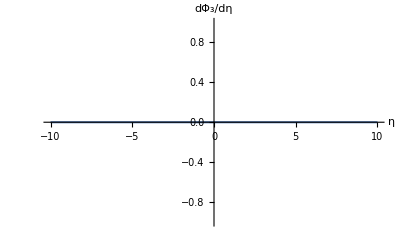

```mathematica
Clear[eq18pt115a]
eq18pt115a =
Plot[Evaluate[Simplify[Expand[D[eq18pt114[[1]][[2]],η]]]],{ η,-10,10},AxesLabel->{η ,Subscript[dΦ, 3]/dη}]
```

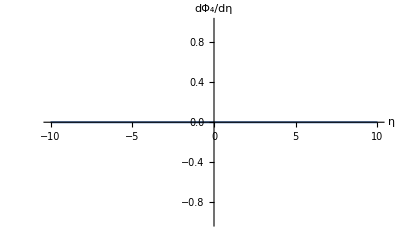

```mathematica
Clear[eq18pt115b]
eq18pt115b =
Plot[Evaluate[Simplify[Expand[D[eq18pt114[[2]][[2]],η]]]],{ η,-10,10},AxesLabel->{η ,Subscript[dΦ, 4]/dη}]
```

```mathematica
Clear[drdtReplace2]
drdtReplace2 =
( D[eq18pt19[[1]],t] /. Flatten[Solve[D[eq18pt19[[2]],t],Derivative[1,0][η][t,r]]][[1]] ) /. Equal-> Rule
```

R^(1,0)[t,r]→(√2 Sin[η[t,r]] (-ℰ[r])^(3/2))/((-1+Cos[η[t,r]]) ℰ[r])

```mathematica
Clear[rdRdtReplace]
rdRdtReplace = { 
(eq18pt19[[1]] /. Equal-> Rule ) , 
drdtReplace2 
}  ;
rdRdtReplace // TableForm
```

R[t,r]→-((1-Cos[η[t,r]]) M[r])/(2 ℰ[r])
R^(1,0)[t,r]→(√2 Sin[η[t,r]] (-ℰ[r])^(3/2))/((-1+Cos[η[t,r]]) ℰ[r])

```mathematica
Clear[eq18pt113b]
eq18pt113b = 
eq18pt113a[[1]] == ( eq18pt113a[[2]] /. rdRdtReplace  )
```

(R^(0,1)[t,r])/R[t,r]==M'[r]/M[r]-(2 √2 Sinh[η[t,r]] ℰ[r]^(3/2) tb'[r])/((1-Cosh[η[t,r]])^2 M[r])-ℰ'[r]/ℰ[r]+(Sinh[η[t,r]] (Sinh[η[t,r]]-η[t,r]) (-M'[r]/M[r]+(3 ℰ'[r])/(2 ℰ[r])))/(-1+Cosh[η[t,r]])^2

```mathematica
eq18pt113a /.
eq18pt113b
```

ReplaceAll::reps: {(R^(0,1)[t,r])/R[t,r]==M'[r]/M[r]-(2 √2 Sinh[η[t,r]] ℰ[r]^(3/2) tb'[r])/((1-Cosh[«1»])^2 M[r])-ℰ'[r]/ℰ[r]+(Sinh[η[t,r]] (Sinh[η[t,r]]-η[t,r]) (-M'[r]/M[«1»]+(3 ℰ'[r])/(2 ℰ[«1»])))/(-1+Cosh[η[«2»]])^2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(R^(0,1)[t,r])/R[t,r]==M'[r]/M[r]-(2 √2 Sinh[η[t,r]] ℰ[r]^(3/2) tb'[r])/((1-Cosh[η[t,r]])^2 M[r])-ℰ'[r]/ℰ[r]+(Sinh[η[t,r]] (Sinh[η[t,r]]-η[t,r]) (-M'[r]/M[r]+(3 ℰ'[r])/(2 ℰ[r])))/(-1+Cosh[η[t,r]])^2/.(R^(0,1)[t,r])/R[t,r]==M'[r]/M[r]-(2 √2 Sinh[η[t,r]] ℰ[r]^(3/2) tb'[r])/((1-Cosh[η[t,r]])^2 M[r])-ℰ'[r]/ℰ[r]+(Sinh[η[t,r]] (Sinh[η[t,r]]-η[t,r]) (-M'[r]/M[r]+(3 ℰ'[r])/(2 ℰ[r])))/(-1+Cosh[η[t,r]])^2

## Equations 18.169 - 18.188: Increasing and Decreasing Density Perturbations

```mathematica
D[(Flatten[Solve[eq18pt15, ϵ[t,r]]][[1]] /. Rule-> Equal  ),r] // pdConv
Flatten[Solve[eq18pt15, ϵ[t,r]]][[1]] /. Rule-> Equal  // pdConv

Clear[eq18pt169]
eq18pt169= 
DivideSides[ D[(Flatten[Solve[eq18pt15, ϵ[t,r]]][[1]] /. Rule-> Equal  ),r],Flatten[Solve[eq18pt15, ϵ[t,r]]][[1]] /. Rule-> Equal][[1]][[1]][[1]] // Expand  ;
eq18pt169 // pdConv
```

(∂ϵ(t,r))/(∂r)==-(c^4 (∂M(r))/(∂r) (∂^2 R(t,r))/(∂r^2))/(4 π G (R(t,r))^2 ((∂R(t,r))/(∂r))^2)+(c^4 (∂^2 M(r))/(∂r^2))/(4 π G (R(t,r))^2 (∂R(t,r))/(∂r))-(c^4 (∂M(r))/(∂r))/(2 π G (R(t,r))^3)

ϵ(t,r)==(c^4 (∂M(r))/(∂r))/(4 π G (R(t,r))^2 (∂R(t,r))/(∂r))

((∂ϵ(t,r))/(∂r))/(ϵ(t,r))==-((∂^2 R(t,r))/(∂r^2))/((∂R(t,r))/(∂r))-(2 (∂R(t,r))/(∂r))/(R(t,r))+((∂^2 M(r))/(∂r^2))/((∂M(r))/(∂r))

```mathematica
(* This is our derivation... *) 
tensorList18pt16d3[[4]]
TensorName[tensorList18pt16d3[[4]]]

Clear[eq18pt170]
eq18pt170 = 
TensorValues[tensorList18pt16d3[[4]]] ;
eq18pt170  // pdConv
```

R

RicciScalarThreeMetric

(4 (-((∂ℰ(r))/(∂r) R(t,r))/((∂R(t,r))/(∂r))-ℰ(r)))/(R(t,r))^2

```mathematica
(* This is typed in directly ... *) 

Clear[eq18pt170a]
eq18pt170a = 
((-4)*Inactivate[D[R[t,r]ℰ[r],r],D])/(R[t,r]^2 D[R[t,r],r])  ;
eq18pt170a  // pdConv
```

-(4 (∂(R(t,r) ℰ(r)))/(∂r))/((R(t,r))^2 (∂R(t,r))/(∂r))

```mathematica
(* The two forms are equivalent... *) 

eq18pt170 == Activate[eq18pt170a] // Expand // Simplify
```

True

```mathematica
(* This is our derivation... *) 

Clear[eq18pt171]
eq18pt171 = 
ΔK[t,r] == D[eq18pt170,r]/eq18pt170 // Expand // Simplify  // Expand  ;
eq18pt171  // pdConv
```

ΔK(t,r)==((∂^2 ℰ(r))/(∂r^2) R(t,r))/((∂ℰ(r))/(∂r) R(t,r)+ℰ(r) (∂R(t,r))/(∂r))-((∂ℰ(r))/(∂r) R(t,r) (∂^2 R(t,r))/(∂r^2))/((∂R(t,r))/(∂r) ((∂ℰ(r))/(∂r) R(t,r)+ℰ(r) (∂R(t,r))/(∂r)))-(2 ℰ(r) ((∂R(t,r))/(∂r))^2)/(R(t,r) ((∂ℰ(r))/(∂r) R(t,r)+ℰ(r) (∂R(t,r))/(∂r)))

```mathematica
(* This is just typed in directly... *) 

Clear[eq18pt171a]
eq18pt171a = 
ΔK[t,r] ==D[R[t,r]ℰ[r],{r,2}]/D[R[t,r]ℰ[r],r] - 2(D[R[t,r],r]/R[t,r]) - D[R[t,r],{r,2}]/D[R[t,r],r] ;
eq18pt171a // pdConv
```

ΔK(t,r)==((∂^2 ℰ(r))/(∂r^2) R(t,r)+ℰ(r) (∂^2 R(t,r))/(∂r^2)+2 (∂ℰ(r))/(∂r) (∂R(t,r))/(∂r))/((∂ℰ(r))/(∂r) R(t,r)+ℰ(r) (∂R(t,r))/(∂r))-((∂^2 R(t,r))/(∂r^2))/((∂R(t,r))/(∂r))-(2 (∂R(t,r))/(∂r))/(R(t,r))

```mathematica
(* We see that the two forms are equivalent... *) 

eq18pt171[[2]]  == eq18pt171a[[2]]  // Expand // Simplify
```

True

```mathematica
(* There's a second form given in equation 18.171 - to get that particular form look at: *) 

Numerator[Together[eq18pt171a[[2]] ]] // pdConv
Denominator[Together[eq18pt171a[[2]] ]]  // pdConv
```

(∂^2 ℰ(r))/(∂r^2) (R(t,r))^2 (∂R(t,r))/(∂r)-(∂ℰ(r))/(∂r) (R(t,r))^2 (∂^2 R(t,r))/(∂r^2)-2 ℰ(r) ((∂R(t,r))/(∂r))^3

R(t,r) (∂R(t,r))/(∂r) ((∂ℰ(r))/(∂r) R(t,r)+ℰ(r) (∂R(t,r))/(∂r))

```mathematica
(* There's a second form given in equation 18.171 - to get that particular form look at: *) 

Numerator[Together[eq18pt171a[[2]] ]]/ (R[t,r] Derivative[0,1][R][t,r]R[t,r]ℰ[r]) // Expand  // pdConv
Denominator[Together[eq18pt171a[[2]] ]] / (R[t,r] Derivative[0,1][R][t,r]R[t,r]ℰ[r]) // Expand  // pdConv
```

-((∂ℰ(r))/(∂r) (∂^2 R(t,r))/(∂r^2))/(ℰ(r) (∂R(t,r))/(∂r))-(2 ((∂R(t,r))/(∂r))^2)/(R(t,r))^2+((∂^2 ℰ(r))/(∂r^2))/(ℰ(r))

((∂R(t,r))/(∂r))/(R(t,r))+((∂ℰ(r))/(∂r))/(ℰ(r))

```mathematica
Clear[eq18pt171b]
eq18pt171b = 
ΔK[t,r] ==((Numerator[Together[eq18pt171a[[2]] ]]/ (R[t,r] Derivative[0,1][R][t,r]R[t,r]ℰ[r]) // Expand ) / (Denominator[Together[eq18pt171a[[2]] ]] / (R[t,r] Derivative[0,1][R][t,r]R[t,r]ℰ[r]) // Expand  ) );
eq18pt171b  // pdConv
```

ΔK(t,r)==(-((∂ℰ(r))/(∂r) (∂^2 R(t,r))/(∂r^2))/(ℰ(r) (∂R(t,r))/(∂r))-(2 ((∂R(t,r))/(∂r))^2)/(R(t,r))^2+((∂^2 ℰ(r))/(∂r^2))/(ℰ(r)))/(((∂R(t,r))/(∂r))/(R(t,r))+((∂ℰ(r))/(∂r))/(ℰ(r)))

```mathematica
Clear[eq18pt172]
eq18pt172 = { 
α[r] ==D[M[r],r]/M[r]-D[ℰ[r],r]/ℰ[r] , 
β[r] == (3/2)D[ℰ[r],r]/ℰ[r] - D[M[r],r]/M[r] , 
γ[r] ==  (2 ℰ[r])^(3/2)/M[r] - D[tb[r],r]
} ;
eq18pt172 // TableForm
```

α[r]==M'[r]/M[r]-ℰ'[r]/ℰ[r]
β[r]==-M'[r]/M[r]+(3 ℰ'[r])/(2 ℰ[r])
γ[r]==(2 √2 ℰ[r]^(3/2))/M[r]-tb'[r]

```mathematica
Clear[dRdr]
dRdr = 
D[eq18pt21[[1]][[1]],r] == (( D[eq18pt21[[1]][[2]],r] /. Flatten[Solve[D[eq18pt21[[2]],r],Derivative[0,1][η][t,r]]][[1]] ) // Expand // FullSimplify )  ;
dRdr  // pdConv
```

(∂R(t,r))/(∂r)==(-2 √2 (ℰ(r))^(5/2) sinh(η(t,r)) ((∂M(r))/(∂r) (t-tb(r))+M(r) (∂tb(r))/(∂r))+3 √2 M(r) (ℰ(r))^(3/2) (t-tb(r)) (∂ℰ(r))/(∂r) sinh(η(t,r))-4 (M(r))^2 (∂ℰ(r))/(∂r) sinh^4(1/2 η(t,r))+4 M(r) ℰ(r) (∂M(r))/(∂r) sinh^4(1/2 η(t,r)))/(2 M(r) (ℰ(r))^2 (cosh(η(t,r))-1))

```mathematica
Clear[d2Rdr2]
d2Rdr2 = 
 D[dRdr[[1]] ,r] == ( D[dRdt[[2]] ,r]/. Flatten[Solve[D[eq18pt21[[2]],r],Derivative[0,1][η][t,r]]][[1]] )  ;
d2Rdr2  // pdConv
```

(∂^2 R(t,r))/(∂r^2)==(√2 √(ℰ(r)) cosh(η(t,r)) (-2 √2 t (ℰ(r))^(3/2) (∂M(r))/(∂r)+3 √2 t M(r) √(ℰ(r)) (∂ℰ(r))/(∂r)-2 √2 M(r) (ℰ(r))^(3/2) (∂tb(r))/(∂r)+2 √2 tb(r) (ℰ(r))^(3/2) (∂M(r))/(∂r)-3 √2 M(r) tb(r) √(ℰ(r)) (∂ℰ(r))/(∂r)))/((M(r))^2 (cosh(η(t,r))-1)^2)-(√2 √(ℰ(r)) sinh^2(η(t,r)) (-2 √2 t (ℰ(r))^(3/2) (∂M(r))/(∂r)+3 √2 t M(r) √(ℰ(r)) (∂ℰ(r))/(∂r)-2 √2 M(r) (ℰ(r))^(3/2) (∂tb(r))/(∂r)+2 √2 tb(r) (ℰ(r))^(3/2) (∂M(r))/(∂r)-3 √2 M(r) tb(r) √(ℰ(r)) (∂ℰ(r))/(∂r)))/((M(r))^2 (cosh(η(t,r))-1)^3)+((∂ℰ(r))/(∂r) sinh(η(t,r)))/(√2 √(ℰ(r)) (cosh(η(t,r))-1))

```mathematica
Clear[eq18pt173]
eq18pt173=
ApplySides[FullSimplify,Assuming[Derivative[0,1][R][t,r]≠0 , DivideSides[d2Rdr2,dRdr]]]  ;
eq18pt173 // pdConv
```

((∂^2 R(t,r))/(∂r^2))/((∂R(t,r))/(∂r))==-((ℰ(r))^(3/2) sinh^2(1/2 η(t,r)) (√2 (M(r))^2 (∂ℰ(r))/(∂r) (sinh(2 η(t,r))-2 sinh(η(t,r)))+16 (ℰ(r))^(5/2) ((∂M(r))/(∂r) (t-tb(r))+M(r) (∂tb(r))/(∂r))+24 M(r) (ℰ(r))^(3/2) (tb(r)-t) (∂ℰ(r))/(∂r)))/(M(r) (cosh(η(t,r))-1)^2 (2 √2 (ℰ(r))^(5/2) sinh(η(t,r)) ((∂M(r))/(∂r) (t-tb(r))+M(r) (∂tb(r))/(∂r))+3 √2 M(r) (ℰ(r))^(3/2) (tb(r)-t) (∂ℰ(r))/(∂r) sinh(η(t,r))+4 (M(r))^2 (∂ℰ(r))/(∂r) sinh^4(1/2 η(t,r))-4 M(r) ℰ(r) (∂M(r))/(∂r) sinh^4(1/2 η(t,r))))

```mathematica
Clear[eq18pt174a]
eq18pt174a = 
ApplySides[FullSimplify,Assuming[R[t,r]≠0,DivideSides[dRdr  , eq18pt21[[1]] ] ]] ;
eq18pt174a   // pdConv
```

((∂R(t,r))/(∂r))/(R(t,r))==(-2 √2 (ℰ(r))^(5/2) sinh(η(t,r)) ((∂M(r))/(∂r) (t-tb(r))+M(r) (∂tb(r))/(∂r))+3 √2 M(r) (ℰ(r))^(3/2) (t-tb(r)) (∂ℰ(r))/(∂r) sinh(η(t,r))-4 (M(r))^2 (∂ℰ(r))/(∂r) sinh^4(1/2 η(t,r))+4 M(r) ℰ(r) (∂M(r))/(∂r) sinh^4(1/2 η(t,r)))/((M(r))^2 ℰ(r) (cosh(η(t,r))-1)^2)

```mathematica
Clear[caseOne]
caseOne = 
 tb'[r]-> 0
```

tb'[r]→0

```mathematica
Clear[caseTwo]
caseTwo = 
D[(2ℰ[r])^(3/2)/M[r],r] == 0

Flatten[Solve[caseTwo , ℰ'[r]]][[1]]
Flatten[Solve[caseTwo , M'[r]]][[1]]
```

-(2 √2 ℰ[r]^(3/2) M'[r])/M[r]^2+(3 √2 √ℰ[r] ℰ'[r])/M[r]==0

ℰ'[r]→(2 ℰ[r] M'[r])/(3 M[r])

M'[r]→(3 M[r] ℰ'[r])/(2 ℰ[r])

```mathematica
Limit[( eq18pt174a[[2]]/. caseOne )  ,η[t,r]-> 0]
Limit[( eq18pt174a[[2]]/.caseOne )  ,η[t,r]-> +∞]
```

Indeterminate

M'[r]/M[r]-ℰ'[r]/ℰ[r]

```mathematica
Clear[eq18pt176a]
eq18pt176a = 
Subscript[ψ, 3][η] ==  ((2 η + η Cosh[η] - 3 Sinh[η] )( Sinh[η]-η ))/(Cosh[η]-1)^3
```

ψ_3[η]==((2 η+η Cosh[η]-3 Sinh[η]) (-η+Sinh[η]))/(-1+Cosh[η])^3

```mathematica
Clear[eq18pt176]
eq18pt176 = { 
eq18pt176a  , 
Inactivate[Limit[eq18pt176a[[2]],η-> 0 ] ,Limit] ==Activate[ Inactivate[Limit[eq18pt176a[[2]],η-> 0 ] ,Limit] ] , 
Inactivate[Limit[eq18pt176a[[2]],η-> +∞ ] ,Limit] ==Activate[ Inactivate[Limit[eq18pt176a[[2]],η-> 0 ] ,Limit] ]
} ;
eq18pt176  // TableForm
```

ψ_3[η]==((2 η+η Cosh[η]-3 Sinh[η]) (-η+Sinh[η]))/(-1+Cosh[η])^3
((2 η+η Cosh[η]-3 Sinh[η]) (-η+Sinh[η]))/(-1+Cosh[η])^3η→0Inactive==0
((2 η+η Cosh[η]-3 Sinh[η]) (-η+Sinh[η]))/(-1+Cosh[η])^3η→∞Inactive==0

```mathematica
Clear[eq18pt187a]
eq18pt187a = 
Subscript[ψ, 1][η] == ((-2 η - η Cos[η] + 3 Sin[η] )(η - Sin[η] ))/(1-Cos[η])^3
```

ψ_1[η]==((η-Sin[η]) (-2 η-η Cos[η]+3 Sin[η]))/(1-Cos[η])^3

```mathematica
Inactivate[Limit[eq18pt187a[[2]],η-> 0 ] ,Limit]
```

((η-Sin[η]) (-2 η-η Cos[η]+3 Sin[η]))/(1-Cos[η])^3η→0Inactive

```mathematica
Clear[eq18pt187]
eq18pt187 =  { 
eq18pt187a , 
Inactivate[Limit[eq18pt187a[[2]],η-> 0 ] ,Limit] == Activate[Inactivate[Limit[eq18pt187a[[2]],η-> 0 ] ,Limit]] ,  
Inactivate[Limit[eq18pt187a[[2]],η-> 2π ],Limit] == Activate[Inactivate[Limit[eq18pt187a[[2]],η-> 2π ],Limit]]
} ;
eq18pt187  // TableForm
```

ψ_1[η]==((η-Sin[η]) (-2 η-η Cos[η]+3 Sin[η]))/(1-Cos[η])^3
((η-Sin[η]) (-2 η-η Cos[η]+3 Sin[η]))/(1-Cos[η])^3η→0Inactive==0
((η-Sin[η]) (-2 η-η Cos[η]+3 Sin[η]))/(1-Cos[η])^3η→2 πInactive==-∞

```mathematica
Clear[eq18pt188a]
eq18pt188a =
Subscript[ψ, 2][η] == (Cos[η]+2)/(1-Cos[η])^3
```

ψ_2[η]==(2+Cos[η])/(1-Cos[η])^3

```mathematica
Clear[eq18pt188]
eq18pt188= { 
eq18pt188a  , 
Inactivate[Limit[eq18pt188a[[2]],η-> 0],Limit] == Activate[Inactivate[Limit[eq18pt188a[[2]],η-> 0],Limit]] , 
Inactivate[Limit[eq18pt188a[[2]],η-> 2π],Limit] == Activate[Inactivate[Limit[eq18pt188a[[2]],η-> 0],Limit]]
} ;
eq18pt188 // TableForm
```

ψ_2[η]==(2+Cos[η])/(1-Cos[η])^3
(2+Cos[η])/(1-Cos[η])^3η→0Inactive==∞
(2+Cos[η])/(1-Cos[η])^3η→2 πInactive==∞

## Line Element and Metric 19.2: Plane Symmetric

```mathematica
Clear[eq19pt2]
eq19pt2 = 
α[t,r] dt^2+ 2 β[t,r] dt dr + γ[t,r] dr^2+ δ[t,r] (dx^2+ dy^2)
```

dt^2 α[t,r]+2 dr dt β[t,r]+dr^2 γ[t,r]+(dx^2+dy^2) δ[t,r]

```mathematica
Clear[metric19pt2]
metric19pt2 = 
lineToMetric[eq19pt2,{dt,dr,dx,dy}]  ;
metric19pt2 // MatrixForm
```

(α[t,r] | β[t,r] | 0 | 0
β[t,r] | γ[t,r] | 0 | 0
0 | 0 | δ[t,r] | 0
0 | 0 | 0 | δ[t,r])

## Line Element and Metric 19.3: Comoving Synchronous Coordinates

```mathematica
Clear[eq19pt3]
eq19pt3 =
Exp[𝒞[t,r]] dt^2 - Exp[A[t,r]] dr^2 - R[t,r]^2 ( dx^2+dy^2)
```

-dr^2 ⅇ^A[t,r]+dt^2 ⅇ^𝒞[t,r]-(dx^2+dy^2) R[t,r]^2

```mathematica
Clear[metric19pt3]
metric19pt3 = 
lineToMetric[eq19pt3,{dt,dr,dx,dy}]  ;
metric19pt3 // MatrixForm
```

(ⅇ^𝒞[t,r] | 0 | 0 | 0
0 | -ⅇ^A[t,r] | 0 | 0
0 | 0 | -R[t,r]^2 | 0
0 | 0 | 0 | -R[t,r]^2)

## Line Element and Metric 19.7: Hyperbolically Symmetric

```mathematica
Clear[eq19pt7]
eq19pt7 = 
α[t,r] dt^2+ 2 β[t,r] dt dr + γ[t,r] dr^2+ δ[t,r] (dθ^2+ Sin[θ]^2 dϕ^2)
```

dt^2 α[t,r]+2 dr dt β[t,r]+dr^2 γ[t,r]+(dθ^2+dϕ^2 Sin[θ]^2) δ[t,r]

```mathematica
Clear[metric19pt7]
metric19pt7 = 
lineToMetric[eq19pt7,{dt,dr,dθ,dϕ}] ;
metric19pt7  // MatrixForm
```

(α[t,r] | β[t,r] | 0 | 0
β[t,r] | γ[t,r] | 0 | 0
0 | 0 | δ[t,r] | 0
0 | 0 | 0 | Sin[θ]^2 δ[t,r])

## Line Element and Metric 19.8: Comoving Synchronous Coordinates Zero Rotation

```mathematica
Clear[eq19pt8]
eq19pt8 = 
Exp[𝒞[t,r]] dt^2 - Exp[A[t,r]] dr^2 - R[t,r]^2 ( dθ^2+ Sinh[θ]^2 dϕ^2)
```

-dr^2 ⅇ^A[t,r]+dt^2 ⅇ^𝒞[t,r]-R[t,r]^2 (dθ^2+dϕ^2 Sinh[θ]^2)

```mathematica
Clear[metric19pt8]
metric19pt8 = 
lineToMetric[eq19pt8 ,{dt,dr,dθ,dϕ}]  ;
metric19pt8 // MatrixForm
```

(ⅇ^𝒞[t,r] | 0 | 0 | 0
0 | -ⅇ^A[t,r] | 0 | 0
0 | 0 | -R[t,r]^2 | 0
0 | 0 | 0 | -R[t,r]^2 Sinh[θ]^2)

## Line Element and Metric 19.10: G3/S2 Symmetric

```mathematica
Clear[eq19pt10]
eq19pt10 = 
α[t,r] dt^2+ 2 β[t,r] dt dr + γ[t,r] dr^2+ δ[t,r] ( dθ^2+ (1/ϵ) Sin[√ϵ θ]^2 dϕ^2)
```

dt^2 α[t,r]+2 dr dt β[t,r]+dr^2 γ[t,r]+(dθ^2+(dϕ^2 Sin[√ϵ θ]^2)/ϵ) δ[t,r]

```mathematica
Clear[metric19pt10]
metric19pt10 = 
lineToMetric[eq19pt10,{dt,dr,dθ,dϕ}]  ;
metric19pt10 // MatrixForm
```

(α[t,r] | β[t,r] | 0 | 0
β[t,r] | γ[t,r] | 0 | 0
0 | 0 | δ[t,r] | 0
0 | 0 | 0 | (Sin[√ϵ θ]^2 δ[t,r])/ϵ)

## Calculation of Tensors Associated With Metric 19.10: G3/S2 Symmetric

```mathematica
(* $CacheTensorValues=True; *)
```

```mathematica
Clear[input19pt10] 
input19pt10[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList19pt10];
tensorList19pt10 = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList19pt10[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList19pt10[[2]]  = 
ChristoffelSymbol[ tensorList19pt10[[1]] , ActWith-> Simplify] ;
tensorList19pt10[[3]] = 
RiemannTensor[ tensorList19pt10[[1]] , ActWithNested-> Simplify ];
tensorList19pt10[[4]] = 
RicciTensor[ tensorList19pt10[[1]] , ActWith-> Simplify ] ;
tensorList19pt10[[5]] = 
RicciScalar[ tensorList19pt10[[1]] , ActWith-> Simplify ] ;
(* tensorList19pt10[[6]] = 
KretschmannScalar[ tensorList19pt10[[1]] , ActWith-> Simplify] ; *) 
tensorList19pt10[[7]] = 
EinsteinTensor[ tensorList19pt10[[1]] , ActWith-> Simplify] ;  
tensorList19pt10[[8]] = 
WeylTensor[ tensorList19pt10[[1]] , ActWith-> Simplify ] ;
(* tensorList19pt10[[9]] = 
CottonTensor[ tensorList19pt10[[1]] , ActWith-> Simplify ] ; *) 
];
```

```mathematica
(* Last timing took 22.68 for all tensors except Kretschmann and Cotton *) 
input19pt10[ "metric19pt10", metric19pt10, "G3S2","g^gs",{t,r,θ,ϕ}, "Greek"] // Timing
```

{8.9325,Null}

```mathematica
tensorList19pt10
```

{(g^gs)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,kretschmannscalarmetric19pt10,G_αβ^,C_αβγδ^,cottonmetric19pt10}

```mathematica
tensorList19pt10[[1]] 
TensorName[tensorList19pt10[[1]]] 
TensorValues[tensorList19pt10[[1]]] // MatrixForm // pdConv
```

(g^gs)_αβ^

G3S2

(α(t,r) | β(t,r) | 0 | 0
β(t,r) | γ(t,r) | 0 | 0
0 | 0 | δ(t,r) | 0
0 | 0 | 0 | (sin^2(θ √ϵ) δ(t,r))/ϵ)

```mathematica
tensorList19pt10[[2]] 
TensorName[tensorList19pt10[[2]]] 
TensorValues[tensorList19pt10[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolG3S2

(((β(t,r) ((∂α(t,r))/(∂r)-2 (∂β(t,r))/(∂t))+γ(t,r) (∂α(t,r))/(∂t))/(2 α(t,r) γ(t,r)-2 (β(t,r))^2)
(γ(t,r) (∂α(t,r))/(∂r)-β(t,r) (∂γ(t,r))/(∂t))/(2 α(t,r) γ(t,r)-2 (β(t,r))^2)
0
0) | ((γ(t,r) (∂α(t,r))/(∂r)-β(t,r) (∂γ(t,r))/(∂t))/(2 α(t,r) γ(t,r)-2 (β(t,r))^2)
(β(t,r) (∂γ(t,r))/(∂r)+γ(t,r) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r)))/(2 ((β(t,r))^2-α(t,r) γ(t,r)))
0
0) | (0
0
(β(t,r) (∂δ(t,r))/(∂r)-γ(t,r) (∂δ(t,r))/(∂t))/(2 α(t,r) γ(t,r)-2 (β(t,r))^2)
0) | (0
0
0
-(sin^2(θ √ϵ) (β(t,r) (∂δ(t,r))/(∂r)-γ(t,r) (∂δ(t,r))/(∂t)))/(2 ϵ ((β(t,r))^2-α(t,r) γ(t,r))))
((α(t,r) ((∂α(t,r))/(∂r)-2 (∂β(t,r))/(∂t))+β(t,r) (∂α(t,r))/(∂t))/(2 ((β(t,r))^2-α(t,r) γ(t,r)))
(β(t,r) (∂α(t,r))/(∂r)-α(t,r) (∂γ(t,r))/(∂t))/(2 (β(t,r))^2-2 α(t,r) γ(t,r))
0
0) | ((β(t,r) (∂α(t,r))/(∂r)-α(t,r) (∂γ(t,r))/(∂t))/(2 (β(t,r))^2-2 α(t,r) γ(t,r))
(α(t,r) (∂γ(t,r))/(∂r)+β(t,r) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r)))/(2 α(t,r) γ(t,r)-2 (β(t,r))^2)
0
0) | (0
0
(α(t,r) (∂δ(t,r))/(∂r)-β(t,r) (∂δ(t,r))/(∂t))/(2 (β(t,r))^2-2 α(t,r) γ(t,r))
0) | (0
0
0
(sin^2(θ √ϵ) (α(t,r) (∂δ(t,r))/(∂r)-β(t,r) (∂δ(t,r))/(∂t)))/(2 ϵ ((β(t,r))^2-α(t,r) γ(t,r))))
(0
0
((∂δ(t,r))/(∂t))/(2 δ(t,r))
0) | (0
0
((∂δ(t,r))/(∂r))/(2 δ(t,r))
0) | (((∂δ(t,r))/(∂t))/(2 δ(t,r))
((∂δ(t,r))/(∂r))/(2 δ(t,r))
0
0) | (0
0
0
-(sin(2 θ √ϵ))/(2 √ϵ))
(0
0
0
((∂δ(t,r))/(∂t))/(2 δ(t,r))) | (0
0
0
((∂δ(t,r))/(∂r))/(2 δ(t,r))) | (0
0
0
√ϵ cot(θ √ϵ)) | (((∂δ(t,r))/(∂t))/(2 δ(t,r))
((∂δ(t,r))/(∂r))/(2 δ(t,r))
√ϵ cot(θ √ϵ)
0))

```mathematica
tensorList19pt10[[3]] 
TensorName[tensorList19pt10[[3]]] 
TensorValues[tensorList19pt10[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorG3S2

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | (2 (β(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+γ(t,r) (-2 α(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)+β(t,r) (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+α(t,r) ((∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2))/(4 α(t,r) γ(t,r)-4 (β(t,r))^2) | 0 | 0
-(2 (β(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+γ(t,r) (-2 α(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)+β(t,r) (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+α(t,r) ((∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2))/(4 α(t,r) γ(t,r)-4 (β(t,r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | (α(t,r) (δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+(β(t,r))^2 (((∂δ(t,r))/(∂t))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂t^2))+β(t,r) δ(t,r) ((∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)-(∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)-2 (∂β(t,r))/(∂t)))-γ(t,r) δ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))/(4 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | 0
0 | 0 | (-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^2 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+β(t,r) δ(t,r) ((∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t))/(4 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | 0
-(α(t,r) (δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+(β(t,r))^2 (((∂δ(t,r))/(∂t))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂t^2))+β(t,r) δ(t,r) ((∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)-(∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)-2 (∂β(t,r))/(∂t)))-γ(t,r) δ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))/(4 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | -(-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^2 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+β(t,r) δ(t,r) ((∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t))/(4 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | (sin^2(θ √ϵ) (α(t,r) (δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+(β(t,r))^2 (((∂δ(t,r))/(∂t))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂t^2))+β(t,r) δ(t,r) ((∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)-(∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)-2 (∂β(t,r))/(∂t)))-γ(t,r) δ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t)))/(4 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r)))
0 | 0 | 0 | (sin^2(θ √ϵ) (-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^2 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+β(t,r) δ(t,r) ((∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t)))/(4 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r)))
0 | 0 | 0 | 0
-(sin^2(θ √ϵ) (α(t,r) (δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+(β(t,r))^2 (((∂δ(t,r))/(∂t))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂t^2))+β(t,r) δ(t,r) ((∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)-(∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)-2 (∂β(t,r))/(∂t)))-γ(t,r) δ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t)))/(4 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | -(sin^2(θ √ϵ) (-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^2 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+β(t,r) δ(t,r) ((∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t)))/(4 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | 0 | 0)
(0 | -(2 (β(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+γ(t,r) (-2 α(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)+β(t,r) (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+α(t,r) ((∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2))/(4 α(t,r) γ(t,r)-4 (β(t,r))^2) | 0 | 0
(2 (β(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+γ(t,r) (-2 α(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)+β(t,r) (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+α(t,r) ((∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2))/(4 α(t,r) γ(t,r)-4 (β(t,r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | (-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^2 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+β(t,r) δ(t,r) ((∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t))/(4 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | 0
0 | 0 | (-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂r^2))+γ(t,r) ((∂δ(t,r))/(∂r))^2)+(β(t,r))^2 (((∂δ(t,r))/(∂r))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂r^2))+β(t,r) δ(t,r) (2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)-(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) δ(t,r) (∂δ(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r)))/(4 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | 0
-(-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^2 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+β(t,r) δ(t,r) ((∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t))/(4 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | -(-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂r^2))+γ(t,r) ((∂δ(t,r))/(∂r))^2)+(β(t,r))^2 (((∂δ(t,r))/(∂r))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂r^2))+β(t,r) δ(t,r) (2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)-(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) δ(t,r) (∂δ(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r)))/(4 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | (sin^2(θ √ϵ) (-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^2 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+β(t,r) δ(t,r) ((∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t)))/(4 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r)))
0 | 0 | 0 | (sin^2(θ √ϵ) (-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂r^2))+γ(t,r) ((∂δ(t,r))/(∂r))^2)+(β(t,r))^2 (((∂δ(t,r))/(∂r))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂r^2))+β(t,r) δ(t,r) (2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)-(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) δ(t,r) (∂δ(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))))/(4 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r)))
0 | 0 | 0 | 0
-(sin^2(θ √ϵ) (-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^2 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+β(t,r) δ(t,r) ((∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t)))/(4 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | -(sin^2(θ √ϵ) (-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂r^2))+γ(t,r) ((∂δ(t,r))/(∂r))^2)+(β(t,r))^2 (((∂δ(t,r))/(∂r))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂r^2))+β(t,r) δ(t,r) (2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)-(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) δ(t,r) (∂δ(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))))/(4 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | 0 | 0)
(0 | 0 | -(α(t,r) (δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+(β(t,r))^2 (((∂δ(t,r))/(∂t))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂t^2))+β(t,r) δ(t,r) ((∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)-(∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)-2 (∂β(t,r))/(∂t)))-γ(t,r) δ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))/(4 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | 0
0 | 0 | -(-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^2 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+β(t,r) δ(t,r) ((∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t))/(4 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | 0
(α(t,r) (δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+(β(t,r))^2 (((∂δ(t,r))/(∂t))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂t^2))+β(t,r) δ(t,r) ((∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)-(∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)-2 (∂β(t,r))/(∂t)))-γ(t,r) δ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))/(4 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | (-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^2 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+β(t,r) δ(t,r) ((∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t))/(4 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | -(-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^2 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+β(t,r) δ(t,r) ((∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t))/(4 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | 0
0 | 0 | -(-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂r^2))+γ(t,r) ((∂δ(t,r))/(∂r))^2)+(β(t,r))^2 (((∂δ(t,r))/(∂r))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂r^2))+β(t,r) δ(t,r) (2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)-(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) δ(t,r) (∂δ(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r)))/(4 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | 0
(-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^2 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+β(t,r) δ(t,r) ((∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t))/(4 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | (-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂r^2))+γ(t,r) ((∂δ(t,r))/(∂r))^2)+(β(t,r))^2 (((∂δ(t,r))/(∂r))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂r^2))+β(t,r) δ(t,r) (2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)-(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) δ(t,r) (∂δ(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r)))/(4 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (sin^2(θ √ϵ) (α(t,r) (((∂δ(t,r))/(∂r))^2-4 ϵ γ(t,r) δ(t,r))+4 ϵ (β(t,r))^2 δ(t,r)-2 β(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)+γ(t,r) ((∂δ(t,r))/(∂t))^2))/(4 ϵ ((β(t,r))^2-α(t,r) γ(t,r)))
0 | 0 | -(sin^2(θ √ϵ) (α(t,r) (((∂δ(t,r))/(∂r))^2-4 ϵ γ(t,r) δ(t,r))+4 ϵ (β(t,r))^2 δ(t,r)-2 β(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)+γ(t,r) ((∂δ(t,r))/(∂t))^2))/(4 ϵ ((β(t,r))^2-α(t,r) γ(t,r))) | 0)
(0 | 0 | 0 | -(sin^2(θ √ϵ) (α(t,r) (δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+(β(t,r))^2 (((∂δ(t,r))/(∂t))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂t^2))+β(t,r) δ(t,r) ((∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)-(∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)-2 (∂β(t,r))/(∂t)))-γ(t,r) δ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t)))/(4 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r)))
0 | 0 | 0 | -(sin^2(θ √ϵ) (-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^2 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+β(t,r) δ(t,r) ((∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t)))/(4 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r)))
0 | 0 | 0 | 0
(sin^2(θ √ϵ) (α(t,r) (δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+(β(t,r))^2 (((∂δ(t,r))/(∂t))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂t^2))+β(t,r) δ(t,r) ((∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)-(∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)-2 (∂β(t,r))/(∂t)))-γ(t,r) δ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t)))/(4 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | (sin^2(θ √ϵ) (-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^2 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+β(t,r) δ(t,r) ((∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t)))/(4 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | 0 | 0) | (0 | 0 | 0 | -(sin^2(θ √ϵ) (-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^2 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+β(t,r) δ(t,r) ((∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t)))/(4 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r)))
0 | 0 | 0 | -(sin^2(θ √ϵ) (-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂r^2))+γ(t,r) ((∂δ(t,r))/(∂r))^2)+(β(t,r))^2 (((∂δ(t,r))/(∂r))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂r^2))+β(t,r) δ(t,r) (2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)-(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) δ(t,r) (∂δ(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))))/(4 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r)))
0 | 0 | 0 | 0
(sin^2(θ √ϵ) (-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^2 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+β(t,r) δ(t,r) ((∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t)))/(4 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | (sin^2(θ √ϵ) (-α(t,r) (δ(t,r) ((∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂r^2))+γ(t,r) ((∂δ(t,r))/(∂r))^2)+(β(t,r))^2 (((∂δ(t,r))/(∂r))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂r^2))+β(t,r) δ(t,r) (2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)-(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) δ(t,r) (∂δ(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))))/(4 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(sin^2(θ √ϵ) (α(t,r) (((∂δ(t,r))/(∂r))^2-4 ϵ γ(t,r) δ(t,r))+4 ϵ (β(t,r))^2 δ(t,r)-2 β(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)+γ(t,r) ((∂δ(t,r))/(∂t))^2))/(4 ϵ ((β(t,r))^2-α(t,r) γ(t,r)))
0 | 0 | (sin^2(θ √ϵ) (α(t,r) (((∂δ(t,r))/(∂r))^2-4 ϵ γ(t,r) δ(t,r))+4 ϵ (β(t,r))^2 δ(t,r)-2 β(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)+γ(t,r) ((∂δ(t,r))/(∂t))^2))/(4 ϵ ((β(t,r))^2-α(t,r) γ(t,r))) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList19pt10[[4]] 
TensorName[tensorList19pt10[[4]]] 
TensorValues[tensorList19pt10[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorG3S2

(((α(t,r))^2 ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)-2 γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r))+2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+α(t,r) (β(t,r) δ(t,r) (δ(t,r) (2 β(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂t)+4 (∂β(t,r))/(∂r) (∂β(t,r))/(∂t))+2 β(t,r) (∂δ(t,r))/(∂r) ((∂α(t,r))/(∂r)-2 (∂β(t,r))/(∂t)))+γ(t,r) (2 β(t,r) δ(t,r) (4 β(t,r) (∂^2 δ(t,r))/(∂t^2)-(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂t))+(δ(t,r))^2 ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-4 (β(t,r))^2 ((∂δ(t,r))/(∂t))^2)+2 (γ(t,r))^2 δ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+2 (β(t,r))^2 ((β(t,r))^2 (((∂δ(t,r))/(∂t))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂t^2))+β(t,r) δ(t,r) ((∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)-(∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)-2 (∂β(t,r))/(∂t)))-γ(t,r) δ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t)))/(4 (δ(t,r))^2 ((β(t,r))^2-α(t,r) γ(t,r))^2) | (2 (β(t,r))^3 δ(t,r) (δ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))+β(t,r) δ(t,r) (γ(t,r) (δ(t,r) (-2 α(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-2 α(t,r) ((∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t)))+α(t,r) δ(t,r) ((∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2))-(β(t,r))^2 (2 δ(t,r) (α(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t))+(δ(t,r))^2 ((∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))-(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+2 α(t,r) γ(t,r) (α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t))+2 (β(t,r))^4 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)))/(4 (δ(t,r))^2 ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0 | 0
(2 (β(t,r))^3 δ(t,r) (δ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))+β(t,r) δ(t,r) (γ(t,r) (δ(t,r) (-2 α(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-2 α(t,r) ((∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t)))+α(t,r) δ(t,r) ((∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2))-(β(t,r))^2 (2 δ(t,r) (α(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t))+(δ(t,r))^2 ((∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))-(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+2 α(t,r) γ(t,r) (α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t))+2 (β(t,r))^4 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-2 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)))/(4 (δ(t,r))^2 ((β(t,r))^2-α(t,r) γ(t,r))^2) | ((γ(t,r))^2 ((δ(t,r))^2 (-2 α(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-2 α(t,r) δ(t,r) (2 α(t,r) (∂^2 δ(t,r))/(∂r^2)+(∂δ(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r)))+2 (α(t,r))^2 ((∂δ(t,r))/(∂r))^2)+γ(t,r) (2 (β(t,r))^2 (δ(t,r) (δ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂δ(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r)))-2 α(t,r) (((∂δ(t,r))/(∂r))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂r^2)))-β(t,r) δ(t,r) (2 α(t,r) (2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)-(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+δ(t,r) ((∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))-(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))))+α(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+2 α(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r)))+2 (β(t,r))^2 ((β(t,r))^2 (((∂δ(t,r))/(∂r))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂r^2))-α(t,r) δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r)+β(t,r) δ(t,r) (2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)-(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))))/(4 (δ(t,r))^2 ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0 | 0
0 | 0 | (-β(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))-4 (β(t,r))^3 (∂^2 δ(t,r))/(∂t ∂r)+2 (β(t,r))^2 (α(t,r) ((∂^2 δ(t,r))/(∂r^2)-4 ϵ γ(t,r))+γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (∂^2 δ(t,r))/(∂r^2)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r)+4 ϵ (γ(t,r))^2)-α(t,r) γ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))+(γ(t,r))^2 (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t)+4 ϵ (β(t,r))^4)/(4 ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0
0 | 0 | 0 | (sin^2(θ √ϵ) (-β(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))-4 (β(t,r))^3 (∂^2 δ(t,r))/(∂t ∂r)+2 (β(t,r))^2 (α(t,r) ((∂^2 δ(t,r))/(∂r^2)-4 ϵ γ(t,r))+γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (∂^2 δ(t,r))/(∂r^2)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r)+4 ϵ (γ(t,r))^2)-α(t,r) γ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))+(γ(t,r))^2 (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t)+4 ϵ (β(t,r))^4))/(4 ϵ ((β(t,r))^2-α(t,r) γ(t,r))^2))

```mathematica
tensorList19pt10[[5]] 
TensorName[tensorList19pt10[[5]]] 
TensorValues[tensorList19pt10[[5]]] // MatrixForm // pdConv
```

R

RicciScalarG3S2

1/(2 (δ(t,r))^2 ((β(t,r))^2-α(t,r) γ(t,r))^2)((β(t,r))^2 (2 (δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))-α(t,r) (-4 δ(t,r) (∂^2 δ(t,r))/(∂r^2)+8 ϵ γ(t,r) δ(t,r)+((∂δ(t,r))/(∂r))^2)+4 δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)-2 γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))+(γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)-β(t,r) (2 δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 ((∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))-(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r)))+2 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+2 (β(t,r))^3 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+(α(t,r))^2 (γ(t,r) (((∂δ(t,r))/(∂r))^2-4 δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)+2 δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)+2 γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r))

```mathematica
(*
tensorList19pt10[[6]] 
TensorName[tensorList19pt10[[6]]] 
TensorValues[tensorList19pt10[[6]]] // MatrixForm // pdConv
*)
```

```mathematica
tensorList19pt10[[7]] 
TensorName[tensorList19pt10[[7]]] 
TensorValues[tensorList19pt10[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorG3S2

(((α(t,r))^2 (2 β(t,r) (δ(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^2 (-4 δ(t,r) (∂^2 δ(t,r))/(∂r^2)+8 ϵ γ(t,r) δ(t,r)+((∂δ(t,r))/(∂r))^2)+γ(t,r) (∂δ(t,r))/(∂t) (δ(t,r) (2 (∂γ(t,r))/(∂t)-4 (∂β(t,r))/(∂r))+γ(t,r) (∂δ(t,r))/(∂t)))-α(t,r) β(t,r) (2 (β(t,r))^2 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+β(t,r) (2 δ(t,r) (-2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)+2 (∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))+3 γ(t,r) ((∂δ(t,r))/(∂t))^2)-4 γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t)+4 ϵ (β(t,r))^3 δ(t,r))-((α(t,r))^3 (γ(t,r) (((∂δ(t,r))/(∂r))^2-4 δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)+2 δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r)))+2 (β(t,r))^2 ((β(t,r))^2 (((∂δ(t,r))/(∂t))^2-2 δ(t,r) (∂^2 δ(t,r))/(∂t^2))+β(t,r) δ(t,r) ((∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)-(∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)-2 (∂β(t,r))/(∂t)))-γ(t,r) δ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t)))/(4 (δ(t,r))^2 ((β(t,r))^2-α(t,r) γ(t,r))^2) | (2 α(t,r) γ(t,r) (α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t))+4 (β(t,r))^4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+(β(t,r))^3 (α(t,r) (-4 δ(t,r) (∂^2 δ(t,r))/(∂r^2)+8 ϵ γ(t,r) δ(t,r)+((∂δ(t,r))/(∂r))^2)-2 δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t))^2)-β(t,r) ((α(t,r))^2 (γ(t,r) (((∂δ(t,r))/(∂r))^2-4 δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)+2 δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+α(t,r) γ(t,r) (4 δ(t,r) (-γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂β(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t))^2)+2 (γ(t,r))^2 δ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+2 (β(t,r))^2 (γ(t,r) δ(t,r) ((∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂t))+α(t,r) (δ(t,r) (2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))-γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)))-4 ϵ (β(t,r))^5 δ(t,r))/(4 (δ(t,r))^2 ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0 | 0
(2 α(t,r) γ(t,r) (α(t,r) (δ(t,r) ((∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) δ(t,r) (∂α(t,r))/(∂r) (∂δ(t,r))/(∂t))+4 (β(t,r))^4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+(β(t,r))^3 (α(t,r) (-4 δ(t,r) (∂^2 δ(t,r))/(∂r^2)+8 ϵ γ(t,r) δ(t,r)+((∂δ(t,r))/(∂r))^2)-2 δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t))^2)-β(t,r) ((α(t,r))^2 (γ(t,r) (((∂δ(t,r))/(∂r))^2-4 δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)+2 δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+α(t,r) γ(t,r) (4 δ(t,r) (-γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂β(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t))^2)+2 (γ(t,r))^2 δ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+2 (β(t,r))^2 (γ(t,r) δ(t,r) ((∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂t))+α(t,r) (δ(t,r) (2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))-γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)))-4 ϵ (β(t,r))^5 δ(t,r))/(4 (δ(t,r))^2 ((β(t,r))^2-α(t,r) γ(t,r))^2) | (2 β(t,r) γ(t,r) (γ(t,r) (δ(t,r) (-4 α(t,r) (∂^2 δ(t,r))/(∂t ∂r)+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂t)+2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂t))+α(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+2 α(t,r) δ(t,r) (∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r))+2 (β(t,r))^3 (δ(t,r) (4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)-(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))-γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^2 (α(t,r) (γ(t,r) (4 δ(t,r) (∂^2 δ(t,r))/(∂r^2)-3 ((∂δ(t,r))/(∂r))^2)+8 ϵ (γ(t,r))^2 δ(t,r)-2 δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) (γ(t,r) ((∂δ(t,r))/(∂t))^2-2 δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+2 (∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))))+(β(t,r))^4 (-4 δ(t,r) (∂^2 δ(t,r))/(∂r^2)-4 ϵ γ(t,r) δ(t,r)+2 ((∂δ(t,r))/(∂r))^2)+(γ(t,r))^2 (α(t,r) (2 δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+(α(t,r))^2 (((∂δ(t,r))/(∂r))^2-4 ϵ γ(t,r) δ(t,r))-2 γ(t,r) δ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t)))/(4 (δ(t,r))^2 ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0 | 0
0 | 0 | (-(β(t,r))^2 (2 (δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+2 δ(t,r) (α(t,r) (∂^2 δ(t,r))/(∂r^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-α(t,r) ((∂δ(t,r))/(∂r))^2)+γ(t,r) (-(δ(t,r))^2 (-2 α(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)+δ(t,r) (α(t,r) (-4 β(t,r) (∂^2 δ(t,r))/(∂t ∂r)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))+2 (α(t,r))^2 (∂^2 δ(t,r))/(∂r^2)+β(t,r) (-2 β(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂t)+2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂t)))+2 α(t,r) β(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)+(α(t,r))^2 (-((∂δ(t,r))/(∂r))^2)+(β(t,r))^2 ((∂δ(t,r))/(∂t))^2)+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-2 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))-(γ(t,r))^2 (δ(t,r) ((∂α(t,r))/(∂t) (∂δ(t,r))/(∂t)-2 α(t,r) (∂^2 δ(t,r))/(∂t^2))+α(t,r) ((∂δ(t,r))/(∂t))^2)+β(t,r) δ(t,r) (α(t,r) (2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+δ(t,r) ((∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))-(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))))-α(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+α(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r)))/(4 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0
0 | 0 | 0 | (sin^2(θ √ϵ) (-(β(t,r))^2 (2 (δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+2 δ(t,r) (α(t,r) (∂^2 δ(t,r))/(∂r^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-α(t,r) ((∂δ(t,r))/(∂r))^2)+γ(t,r) (-(δ(t,r))^2 (-2 α(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)+δ(t,r) (α(t,r) (-4 β(t,r) (∂^2 δ(t,r))/(∂t ∂r)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))+2 (α(t,r))^2 (∂^2 δ(t,r))/(∂r^2)+β(t,r) (-2 β(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂t)+2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂t)))+2 α(t,r) β(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)+(α(t,r))^2 (-((∂δ(t,r))/(∂r))^2)+(β(t,r))^2 ((∂δ(t,r))/(∂t))^2)+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-2 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))-(γ(t,r))^2 (δ(t,r) ((∂α(t,r))/(∂t) (∂δ(t,r))/(∂t)-2 α(t,r) (∂^2 δ(t,r))/(∂t^2))+α(t,r) ((∂δ(t,r))/(∂t))^2)+β(t,r) δ(t,r) (α(t,r) (2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+δ(t,r) ((∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))-(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))))-α(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+α(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))))/(4 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2))

```mathematica
tensorList19pt10[[8]] 
TensorName[tensorList19pt10[[8]]] 
TensorValues[tensorList19pt10[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorG3S2

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | (2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)-α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (-δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 ((∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))-(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r)))-4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+4 (β(t,r))^3 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+(α(t,r))^2 (2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))-4 ϵ (γ(t,r))^2 δ(t,r)+δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t)-δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2))-4 ϵ (β(t,r))^4 δ(t,r))/(12 (δ(t,r))^2 ((β(t,r))^2-α(t,r) γ(t,r))) | 0 | 0
(-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r))/(12 (δ(t,r))^2 ((β(t,r))^2-α(t,r) γ(t,r))) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | -(α(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0
0 | 0 | -(β(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0
(α(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | (β(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | -(sin^2(θ √ϵ) α(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2)
0 | 0 | 0 | -(sin^2(θ √ϵ) β(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2)
0 | 0 | 0 | 0
(sin^2(θ √ϵ) α(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | (sin^2(θ √ϵ) β(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0 | 0)
(0 | (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r))/(12 (δ(t,r))^2 ((β(t,r))^2-α(t,r) γ(t,r))) | 0 | 0
(2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)-α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (-δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 ((∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))-(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r)))-4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+4 (β(t,r))^3 ((∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t)-δ(t,r) (∂^2 δ(t,r))/(∂t ∂r))+(α(t,r))^2 (2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))-4 ϵ (γ(t,r))^2 δ(t,r)+δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t)-δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2))-4 ϵ (β(t,r))^4 δ(t,r))/(12 (δ(t,r))^2 ((β(t,r))^2-α(t,r) γ(t,r))) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | -(β(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0
0 | 0 | -(γ(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0
(β(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | (γ(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | -(sin^2(θ √ϵ) β(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2)
0 | 0 | 0 | -(sin^2(θ √ϵ) γ(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2)
0 | 0 | 0 | 0
(sin^2(θ √ϵ) β(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | (sin^2(θ √ϵ) γ(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0 | 0)
(0 | 0 | (α(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0
0 | 0 | (β(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0
-(α(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | -(β(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | (β(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0
0 | 0 | (γ(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0
-(β(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | -(γ(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (sin^2(θ √ϵ) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(12 ϵ ((β(t,r))^2-α(t,r) γ(t,r))^2)
0 | 0 | -(sin^2(θ √ϵ) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(12 ϵ ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0)
(0 | 0 | 0 | (sin^2(θ √ϵ) α(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2)
0 | 0 | 0 | (sin^2(θ √ϵ) β(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2)
0 | 0 | 0 | 0
-(sin^2(θ √ϵ) α(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | -(sin^2(θ √ϵ) β(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0 | 0) | (0 | 0 | 0 | (sin^2(θ √ϵ) β(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2)
0 | 0 | 0 | (sin^2(θ √ϵ) γ(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2)
0 | 0 | 0 | 0
-(sin^2(θ √ϵ) β(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | -(sin^2(θ √ϵ) γ(t,r) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(24 ϵ δ(t,r) ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(sin^2(θ √ϵ) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(12 ϵ ((β(t,r))^2-α(t,r) γ(t,r))^2)
0 | 0 | (sin^2(θ √ϵ) (-2 (β(t,r))^2 (-(δ(t,r))^2 (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+α(t,r) (δ(t,r) (∂^2 δ(t,r))/(∂r^2)+4 ϵ γ(t,r) δ(t,r)-((∂δ(t,r))/(∂r))^2)+δ(t,r) (γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-γ(t,r) ((∂δ(t,r))/(∂t))^2)+α(t,r) ((δ(t,r))^2 (-2 γ(t,r) (-2 (∂^2 β(t,r))/(∂t ∂r)+(∂^2 α(t,r))/(∂r^2)+(∂^2 γ(t,r))/(∂t^2))+(∂α(t,r))/(∂r) (∂γ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂γ(t,r))/(∂r)+((∂γ(t,r))/(∂t))^2)+γ(t,r) δ(t,r) (2 γ(t,r) (∂^2 δ(t,r))/(∂t^2)+(∂α(t,r))/(∂r) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂t) (∂δ(t,r))/(∂r)-2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂t)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂t))-2 (γ(t,r))^2 ((∂δ(t,r))/(∂t))^2)+β(t,r) (δ(t,r) (α(t,r) (-4 γ(t,r) (∂^2 δ(t,r))/(∂t ∂r)+2 (∂β(t,r))/(∂r) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂t) (∂δ(t,r))/(∂r)+(∂γ(t,r))/(∂r) (∂δ(t,r))/(∂t))+γ(t,r) ((∂δ(t,r))/(∂t) ((∂α(t,r))/(∂r)+2 (∂β(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂δ(t,r))/(∂r)))+(δ(t,r))^2 (-(∂α(t,r))/(∂r) (2 (∂β(t,r))/(∂r)+(∂γ(t,r))/(∂t))+(∂α(t,r))/(∂t) (∂γ(t,r))/(∂r)+2 (∂β(t,r))/(∂t) (2 (∂β(t,r))/(∂r)-(∂γ(t,r))/(∂t)))+4 α(t,r) γ(t,r) (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(β(t,r))^3 (4 δ(t,r) (∂^2 δ(t,r))/(∂t ∂r)-4 (∂δ(t,r))/(∂r) (∂δ(t,r))/(∂t))+(α(t,r))^2 (-2 γ(t,r) (((∂δ(t,r))/(∂r))^2-δ(t,r) (∂^2 δ(t,r))/(∂r^2))+4 ϵ (γ(t,r))^2 δ(t,r)-δ(t,r) (∂γ(t,r))/(∂r) (∂δ(t,r))/(∂r))+γ(t,r) δ(t,r) (δ(t,r) ((∂α(t,r))/(∂t) ((∂γ(t,r))/(∂t)-2 (∂β(t,r))/(∂r))+((∂α(t,r))/(∂r))^2)-γ(t,r) (∂α(t,r))/(∂t) (∂δ(t,r))/(∂t))+4 ϵ (β(t,r))^4 δ(t,r)))/(12 ϵ ((β(t,r))^2-α(t,r) γ(t,r))^2) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
(*
tensorList19pt10[[9]] 
TensorName[tensorList19pt10[[9]]] 
TensorValues[tensorList19pt10[[9]]] // MatrixForm // pdConv
*)
```

## Line Element and Metric 19.11: Comoving Synchronous Coordinates

```mathematica
Clear[eq19pt11]
eq19pt11 = 
Exp[𝒞[t,r]] dt^2- Exp[A[t,r]] dr^2- R[t,r]^2( dθ^2+ f[θ] dϕ^2)
```

-dr^2 ⅇ^A[t,r]+dt^2 ⅇ^𝒞[t,r]-(dθ^2+dϕ^2 f[θ]) R[t,r]^2

```mathematica
Clear[metric19pt11]
metric19pt11 = 
lineToMetric[eq19pt11 ,{dt,dr,dθ,dϕ}] ;
metric19pt11  // MatrixForm
```

(ⅇ^𝒞[t,r] | 0 | 0 | 0
0 | -ⅇ^A[t,r] | 0 | 0
0 | 0 | -R[t,r]^2 | 0
0 | 0 | 0 | -f[θ] R[t,r]^2)

```mathematica
Clear[eq19pt12]
eq19pt12 = {
f[θ]  ==  Sin[θ]  , 
f[θ] == θ  , 
f[θ] == Sinh[θ]
} /. Equal-> Rule ;
eq19pt12  // TableForm
```

f[θ]→Sin[θ]
f[θ]→θ
f[θ]→Sinh[θ]

```mathematica
Clear[fSpherical]
fSpherical = { 
eq19pt12[[1]] , 
D[eq19pt12[[1]],θ] , 
D[eq19pt12[[1]],{θ,2}]
} ;
fSpherical // TableForm
```

f[θ]→Sin[θ]
f'[θ]→Cos[θ]
f''[θ]→-Sin[θ]

```mathematica
Clear[fPlane]
fPlane = { 
eq19pt12[[2]] , 
D[eq19pt12[[2]],θ] , 
D[eq19pt12[[2]],{θ,2}]
} ;
fPlane // TableForm
```

f[θ]→θ
f'[θ]→1
f''[θ]→0

```mathematica
Clear[fHyperbolic]
fHyperbolic = { 
eq19pt12[[3]] , 
D[eq19pt12[[3]],θ] , 
D[eq19pt12[[3]],{θ,2}]
} ;
fHyperbolic  // TableForm
```

f[θ]→Sinh[θ]
f'[θ]→Cosh[θ]
f''[θ]→Sinh[θ]

## Calculation of Tensors Associated With Metric 19.11: Comoving Synchronous Coordinates

```mathematica
(* $CacheTensorValues=True; *)
```

```mathematica
Clear[input19pt11] 
input19pt11[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList19pt11];
tensorList19pt11 = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList19pt11[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList19pt11[[2]]  = 
ChristoffelSymbol[ tensorList19pt11[[1]] , ActWith-> Simplify] ;
tensorList19pt11[[3]] = 
RiemannTensor[ tensorList19pt11[[1]] , ActWithNested-> Simplify ];
tensorList19pt11[[4]] = 
RicciTensor[ tensorList19pt11[[1]] , ActWith-> Simplify ] ;
tensorList19pt11[[5]] = 
RicciScalar[ tensorList19pt11[[1]] , ActWith-> Simplify ] ;
(* tensorList19pt11[[6]] = 
KretschmannScalar[ tensorList19pt11[[1]] , ActWith-> Simplify] ; *) 
tensorList19pt11[[7]] = 
EinsteinTensor[ tensorList19pt11[[1]] , ActWith-> Simplify] ;  
tensorList19pt11[[8]] = 
WeylTensor[ tensorList19pt11[[1]] , ActWith-> Simplify ] ;
(* tensorList19pt11[[9]] = 
CottonTensor[ tensorList19pt11[[1]] , ActWith-> Simplify ] ; *) 
];
```

```mathematica
(* Last timing took 22.68 for all tensors except Kretschmann and Cotton *) 
input19pt11[ "metric19pt11", metric19pt11, "ComovingSynchronous","g^cs",{t,r,θ,ϕ}, "Greek"] // Timing
```

{4.81909,Null}

```mathematica
tensorList19pt11
```

{(g^cs)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,kretschmannscalarmetric19pt11,G_αβ^,C_αβγδ^,cottonmetric19pt11}

```mathematica
tensorList19pt11[[1]] 
TensorName[tensorList19pt11[[1]]] 
TensorValues[tensorList19pt11[[1]]] // MatrixForm // pdConv
```

(g^cs)_αβ^

ComovingSynchronous

(ⅇ^(𝒞(t,r)) | 0 | 0 | 0
0 | -ⅇ^(A(t,r)) | 0 | 0
0 | 0 | -(R(t,r))^2 | 0
0 | 0 | 0 | -f(θ) (R(t,r))^2)

```mathematica
tensorList19pt11[[2]] 
TensorName[tensorList19pt11[[2]]] 
TensorValues[tensorList19pt11[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolComovingSynchronous

((1/2 (∂𝒞(t,r))/(∂t)
1/2 (∂𝒞(t,r))/(∂r)
0
0) | (1/2 (∂𝒞(t,r))/(∂r)
1/2 ⅇ^(A(t,r)-𝒞(t,r)) (∂A(t,r))/(∂t)
0
0) | (0
0
R(t,r) ⅇ^(-𝒞(t,r)) (∂R(t,r))/(∂t)
0) | (0
0
0
f(θ) R(t,r) ⅇ^(-𝒞(t,r)) (∂R(t,r))/(∂t))
(1/2 ⅇ^(𝒞(t,r)-A(t,r)) (∂𝒞(t,r))/(∂r)
1/2 (∂A(t,r))/(∂t)
0
0) | (1/2 (∂A(t,r))/(∂t)
1/2 (∂A(t,r))/(∂r)
0
0) | (0
0
-ⅇ^(-A(t,r)) R(t,r) (∂R(t,r))/(∂r)
0) | (0
0
0
f(θ) (-ⅇ^(-A(t,r))) R(t,r) (∂R(t,r))/(∂r))
(0
0
((∂R(t,r))/(∂t))/(R(t,r))
0) | (0
0
((∂R(t,r))/(∂r))/(R(t,r))
0) | (((∂R(t,r))/(∂t))/(R(t,r))
((∂R(t,r))/(∂r))/(R(t,r))
0
0) | (0
0
0
-1/2 (∂f(θ))/(∂θ))
(0
0
0
((∂R(t,r))/(∂t))/(R(t,r))) | (0
0
0
((∂R(t,r))/(∂r))/(R(t,r))) | (0
0
0
((∂f(θ))/(∂θ))/(2 f(θ))) | (((∂R(t,r))/(∂t))/(R(t,r))
((∂R(t,r))/(∂r))/(R(t,r))
((∂f(θ))/(∂θ))/(2 f(θ))
0))

```mathematica
tensorList19pt11[[3]] 
TensorName[tensorList19pt11[[3]]] 
TensorValues[tensorList19pt11[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorComovingSynchronous

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 1/4 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2) | 0 | 0
1/4 (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 1/2 R(t,r) (-ⅇ^(𝒞(t,r)-A(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+2 (∂^2 R(t,r))/(∂t^2)-(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)) | 0
0 | 0 | -1/2 R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 0
-1/2 R(t,r) (-ⅇ^(𝒞(t,r)-A(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+2 (∂^2 R(t,r))/(∂t^2)-(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)) | 1/2 R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | -1/2 f(θ) ⅇ^(-A(t,r)) R(t,r) (ⅇ^(A(t,r)) ((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-2 (∂^2 R(t,r))/(∂t^2))+ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))
0 | 0 | 0 | -1/2 f(θ) R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))
0 | 0 | 0 | 0
1/2 f(θ) ⅇ^(-A(t,r)) R(t,r) (ⅇ^(A(t,r)) ((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-2 (∂^2 R(t,r))/(∂t^2))+ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)) | 1/2 f(θ) R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 0 | 0)
(0 | 1/4 (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2) | 0 | 0
1/4 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | -1/2 R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 0
0 | 0 | 1/2 R(t,r) (-ⅇ^(A(t,r)-𝒞(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+2 (∂^2 R(t,r))/(∂r^2)) | 0
1/2 R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | -1/2 R(t,r) (-ⅇ^(A(t,r)-𝒞(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+2 (∂^2 R(t,r))/(∂r^2)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | -1/2 f(θ) R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))
0 | 0 | 0 | -1/2 f(θ) R(t,r) ⅇ^(-𝒞(t,r)) (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2))
0 | 0 | 0 | 0
1/2 f(θ) R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 1/2 f(θ) R(t,r) ⅇ^(-𝒞(t,r)) (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)) | 0 | 0)
(0 | 0 | -1/2 R(t,r) (-ⅇ^(𝒞(t,r)-A(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+2 (∂^2 R(t,r))/(∂t^2)-(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)) | 0
0 | 0 | 1/2 R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 0
1/2 R(t,r) (-ⅇ^(𝒞(t,r)-A(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+2 (∂^2 R(t,r))/(∂t^2)-(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)) | -1/2 R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 1/2 R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 0
0 | 0 | -1/2 R(t,r) (-ⅇ^(A(t,r)-𝒞(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+2 (∂^2 R(t,r))/(∂r^2)) | 0
-1/2 R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 1/2 R(t,r) (-ⅇ^(A(t,r)-𝒞(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-(∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+2 (∂^2 R(t,r))/(∂r^2)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1/4 (R(t,r))^2 (f(θ) (4 ⅇ^(-A(t,r)) ((∂R(t,r))/(∂r))^2-4 ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2)+2 (∂^2 f(θ))/(∂θ^2)-((∂f(θ))/(∂θ))^2/(f(θ)))
0 | 0 | -1/4 (R(t,r))^2 (f(θ) (4 ⅇ^(-A(t,r)) ((∂R(t,r))/(∂r))^2-4 ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2)+2 (∂^2 f(θ))/(∂θ^2)-((∂f(θ))/(∂θ))^2/(f(θ))) | 0)
(0 | 0 | 0 | 1/2 f(θ) ⅇ^(-A(t,r)) R(t,r) (ⅇ^(A(t,r)) ((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-2 (∂^2 R(t,r))/(∂t^2))+ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))
0 | 0 | 0 | 1/2 f(θ) R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))
0 | 0 | 0 | 0
-1/2 f(θ) ⅇ^(-A(t,r)) R(t,r) (ⅇ^(A(t,r)) ((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-2 (∂^2 R(t,r))/(∂t^2))+ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)) | -1/2 f(θ) R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | 0 | 0) | (0 | 0 | 0 | 1/2 f(θ) R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))
0 | 0 | 0 | 1/2 f(θ) R(t,r) ⅇ^(-𝒞(t,r)) (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2))
0 | 0 | 0 | 0
-1/2 f(θ) R(t,r) (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r)) | -1/2 f(θ) R(t,r) ⅇ^(-𝒞(t,r)) (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -1/4 (R(t,r))^2 (f(θ) (4 ⅇ^(-A(t,r)) ((∂R(t,r))/(∂r))^2-4 ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2)+2 (∂^2 f(θ))/(∂θ^2)-((∂f(θ))/(∂θ))^2/(f(θ)))
0 | 0 | 1/4 (R(t,r))^2 (f(θ) (4 ⅇ^(-A(t,r)) ((∂R(t,r))/(∂r))^2-4 ⅇ^(-𝒞(t,r)) ((∂R(t,r))/(∂t))^2)+2 (∂^2 f(θ))/(∂θ^2)-((∂f(θ))/(∂θ))^2/(f(θ))) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList19pt11[[4]] 
TensorName[tensorList19pt11[[4]]] 
TensorValues[tensorList19pt11[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorComovingSynchronous

((ⅇ^(-A(t,r)) (R(t,r) (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-2 (∂^2 R(t,r))/(∂t^2))+4 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)))/(4 R(t,r)) | (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))/(R(t,r)) | 0 | 0
(-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))/(R(t,r)) | (ⅇ^(-𝒞(t,r)) (-R(t,r) (-ⅇ^(A(t,r)) (2 (∂^2 A(t,r))/(∂t^2)-(∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+((∂A(t,r))/(∂t))^2)+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (R(t,r) (∂𝒞(t,r))/(∂r)+4 (∂R(t,r))/(∂r))+4 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-8 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)))/(4 R(t,r)) | 0 | 0
0 | 0 | 1/4 (ⅇ^(-A(t,r)-𝒞(t,r)) (2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)-(2 (∂^2 f(θ))/(∂θ^2))/(f(θ))+((∂f(θ))/(∂θ))^2/(f(θ))^2) | 0
0 | 0 | 0 | 1/4 (2 f(θ) ⅇ^(-A(t,r)-𝒞(t,r)) (R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+2 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)-2 (∂^2 f(θ))/(∂θ^2)+((∂f(θ))/(∂θ))^2/(f(θ))))

```mathematica
tensorList19pt11[[5]] 
TensorName[tensorList19pt11[[5]]] 
TensorValues[tensorList19pt11[[5]]] // MatrixForm // pdConv
```

R

RicciScalarComovingSynchronous

1/(2 (f(θ))^2 (R(t,r))^2)ⅇ^(-A(t,r)-𝒞(t,r)) (f(θ) (2 (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r)+𝒞(t,r))-f(θ) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+4 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2))-((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)+𝒞(t,r)))

```mathematica
(*
tensorList19pt11[[6]] 
TensorName[tensorList19pt11[[6]]] 
TensorValues[tensorList19pt11[[6]]] // MatrixForm // pdConv
*)
```

```mathematica
tensorList19pt11[[7]] 
TensorName[tensorList19pt11[[7]]] 
TensorValues[tensorList19pt11[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorComovingSynchronous

((ⅇ^(-A(t,r)) (4 (f(θ))^2 (R(t,r) (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2))+ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)-2 f(θ) (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r)+𝒞(t,r))+((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)+𝒞(t,r))))/(4 (f(θ))^2 (R(t,r))^2) | (-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))/(R(t,r)) | 0 | 0
(-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))/(R(t,r)) | (ⅇ^(-𝒞(t,r)) (2 f(θ) (2 f(θ) (-ⅇ^(A(t,r)) (2 R(t,r) (∂^2 R(t,r))/(∂t^2)-R(t,r) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+((∂R(t,r))/(∂t))^2)+ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2+R(t,r) ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+(∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r)+𝒞(t,r)))-((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)+𝒞(t,r))))/(4 (f(θ))^2 (R(t,r))^2) | 0 | 0
0 | 0 | 1/4 R(t,r) ⅇ^(-A(t,r)-𝒞(t,r)) (-4 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)-2 ⅇ^(A(t,r)) R(t,r) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) R(t,r) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (R(t,r) (∂𝒞(t,r))/(∂r)+2 (∂R(t,r))/(∂r))-ⅇ^(A(t,r)) R(t,r) ((∂A(t,r))/(∂t))^2-2 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)+4 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)+2 R(t,r) ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+2 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+R(t,r) ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2) | 0
0 | 0 | 0 | 1/4 f(θ) R(t,r) ⅇ^(-A(t,r)-𝒞(t,r)) (-4 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)-2 ⅇ^(A(t,r)) R(t,r) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) R(t,r) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (R(t,r) (∂𝒞(t,r))/(∂r)+2 (∂R(t,r))/(∂r))-ⅇ^(A(t,r)) R(t,r) ((∂A(t,r))/(∂t))^2-2 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)+4 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)+2 R(t,r) ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+2 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+R(t,r) ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2))

```mathematica
tensorList19pt11[[8]] 
TensorName[tensorList19pt11[[8]]] 
TensorValues[tensorList19pt11[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorComovingSynchronous

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | (f(θ) (f(θ) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)-2 (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r)+𝒞(t,r)))+((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)+𝒞(t,r)))/(12 (f(θ))^2 (R(t,r))^2) | 0 | 0
(f(θ) (2 (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r)+𝒞(t,r))-f(θ) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2))-((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)+𝒞(t,r)))/(12 (f(θ))^2 (R(t,r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | (ⅇ^(-A(t,r)) (f(θ) (2 (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r)+𝒞(t,r))-f(θ) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2))-((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)+𝒞(t,r))))/(24 (f(θ))^2) | 0
0 | 0 | 0 | 0
(ⅇ^(-A(t,r)) (f(θ) (f(θ) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)-2 (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r)+𝒞(t,r)))+((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)+𝒞(t,r))))/(24 (f(θ))^2) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 1/24 (-f(θ) ⅇ^(-A(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)+2 (∂^2 f(θ))/(∂θ^2) ⅇ^(𝒞(t,r))-(((∂f(θ))/(∂θ))^2 ⅇ^(𝒞(t,r)))/(f(θ)))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1/24 (f(θ) ⅇ^(-A(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)-2 (∂^2 f(θ))/(∂θ^2) ⅇ^(𝒞(t,r))+(((∂f(θ))/(∂θ))^2 ⅇ^(𝒞(t,r)))/(f(θ))) | 0 | 0 | 0)
(0 | (f(θ) (2 (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r)+𝒞(t,r))-f(θ) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2))-((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)+𝒞(t,r)))/(12 (f(θ))^2 (R(t,r))^2) | 0 | 0
(f(θ) (f(θ) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)-2 (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r)+𝒞(t,r)))+((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)+𝒞(t,r)))/(12 (f(θ))^2 (R(t,r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (ⅇ^(-𝒞(t,r)) (f(θ) (f(θ) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)-2 (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r)+𝒞(t,r)))+((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)+𝒞(t,r))))/(24 (f(θ))^2) | 0
0 | (ⅇ^(-𝒞(t,r)) (f(θ) (2 (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r)+𝒞(t,r))-f(θ) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2))-((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)+𝒞(t,r))))/(24 (f(θ))^2) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 1/24 (f(θ) ⅇ^(-𝒞(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)-2 (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r))+(((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)))/(f(θ)))
0 | 0 | 0 | 0
0 | 1/24 (f(θ) ⅇ^(-𝒞(t,r)) ((R(t,r))^2 (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))-4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2+4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)+2 (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r))-(((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)))/(f(θ))) | 0 | 0)
(0 | 0 | (ⅇ^(-A(t,r)) (f(θ) (f(θ) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)-2 (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r)+𝒞(t,r)))+((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)+𝒞(t,r))))/(24 (f(θ))^2) | 0
0 | 0 | 0 | 0
(ⅇ^(-A(t,r)) (f(θ) (2 (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r)+𝒞(t,r))-f(θ) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2))-((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)+𝒞(t,r))))/(24 (f(θ))^2) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (ⅇ^(-𝒞(t,r)) (f(θ) (2 (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r)+𝒞(t,r))-f(θ) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2))-((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)+𝒞(t,r))))/(24 (f(θ))^2) | 0
0 | (ⅇ^(-𝒞(t,r)) (f(θ) (f(θ) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)-2 (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r)+𝒞(t,r)))+((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)+𝒞(t,r))))/(24 (f(θ))^2) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1/12 (R(t,r))^2 (f(θ) ⅇ^(-A(t,r)-𝒞(t,r)) ((R(t,r))^2 (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))-4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2+4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)+2 (∂^2 f(θ))/(∂θ^2)-((∂f(θ))/(∂θ))^2/(f(θ)))
0 | 0 | 1/12 (R(t,r))^2 (f(θ) ⅇ^(-A(t,r)-𝒞(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)-2 (∂^2 f(θ))/(∂θ^2)+((∂f(θ))/(∂θ))^2/(f(θ))) | 0)
(0 | 0 | 0 | 1/24 (f(θ) ⅇ^(-A(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)-2 (∂^2 f(θ))/(∂θ^2) ⅇ^(𝒞(t,r))+(((∂f(θ))/(∂θ))^2 ⅇ^(𝒞(t,r)))/(f(θ)))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1/24 (-f(θ) ⅇ^(-A(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)+2 (∂^2 f(θ))/(∂θ^2) ⅇ^(𝒞(t,r))-(((∂f(θ))/(∂θ))^2 ⅇ^(𝒞(t,r)))/(f(θ))) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 1/24 (f(θ) ⅇ^(-𝒞(t,r)) ((R(t,r))^2 (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))-4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2+4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)+2 (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r))-(((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)))/(f(θ)))
0 | 0 | 0 | 0
0 | 1/24 (f(θ) ⅇ^(-𝒞(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)-2 (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r))+(((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)))/(f(θ))) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1/12 (R(t,r))^2 (f(θ) ⅇ^(-A(t,r)-𝒞(t,r)) ((R(t,r))^2 (2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)-ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)-2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)-2 (∂^2 f(θ))/(∂θ^2)+((∂f(θ))/(∂θ))^2/(f(θ)))
0 | 0 | 1/12 (R(t,r))^2 (f(θ) ⅇ^(-A(t,r)-𝒞(t,r)) ((R(t,r))^2 (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))-4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2+4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)+2 (∂^2 f(θ))/(∂θ^2)-((∂f(θ))/(∂θ))^2/(f(θ))) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
(*
tensorList19pt11[[9]] 
TensorName[tensorList19pt11[[9]]] 
TensorValues[tensorList19pt11[[9]]] // MatrixForm // pdConv
*)
```

## Derivation of Vacuum Field Equations For Metric 19.11: G3/S2 Symmetric (Be careful... there’s ϵ and ε [esc]ce[esc] Figure out how related to f[θ] )

```mathematica
Clear[nonzeroRicci19pt11 ] 
nonzeroRicci19pt11  = 
DeleteDuplicates[Cases[ Flatten[Table[If[ i<= j , TensorValues[tensorList19pt11 [[4]]][[i,j]],Nothing] ,{i,1,4},{j,1,4}]] , Except[0]]] ;
nonzeroRicci19pt11  // TableForm // pdConv
```

(ⅇ^(-A(t,r)) (R(t,r) (-2 ⅇ^(A(t,r)) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-ⅇ^(A(t,r)) ((∂A(t,r))/(∂t))^2+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-2 (∂^2 R(t,r))/(∂t^2))+4 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)))/(4 R(t,r))
(-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))/(R(t,r))
(ⅇ^(-𝒞(t,r)) (-R(t,r) (-ⅇ^(A(t,r)) (2 (∂^2 A(t,r))/(∂t^2)-(∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+((∂A(t,r))/(∂t))^2)+2 ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (R(t,r) (∂𝒞(t,r))/(∂r)+4 (∂R(t,r))/(∂r))+4 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-8 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)))/(4 R(t,r))
1/4 (ⅇ^(-A(t,r)-𝒞(t,r)) (2 R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+4 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-4 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)-(2 (∂^2 f(θ))/(∂θ^2))/(f(θ))+((∂f(θ))/(∂θ))^2/(f(θ))^2)
1/4 (2 f(θ) ⅇ^(-A(t,r)-𝒞(t,r)) (R(t,r) (2 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)+ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)-ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)-ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+2 ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-2 ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)-2 (∂^2 f(θ))/(∂θ^2)+((∂f(θ))/(∂θ))^2/(f(θ)))

```mathematica
Clear[nonzeroEinstein19pt11 ] 
nonzeroEinstein19pt11  = 
DeleteDuplicates[Cases[ Flatten[Table[If[ i<= j , TensorValues[tensorList19pt11 [[7]]][[i,j]],Nothing] ,{i,1,4},{j,1,4}]] , Except[0]]] ;
nonzeroEinstein19pt11  // TableForm // pdConv
```

(ⅇ^(-A(t,r)) (4 (f(θ))^2 (R(t,r) (ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-2 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2))+ⅇ^(A(t,r)) ((∂R(t,r))/(∂t))^2-ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2)-2 f(θ) (∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r)+𝒞(t,r))+((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)+𝒞(t,r))))/(4 (f(θ))^2 (R(t,r))^2)
(-2 (∂^2 R(t,r))/(∂t ∂r)+(∂A(t,r))/(∂t) (∂R(t,r))/(∂r)+(∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))/(R(t,r))
(ⅇ^(-𝒞(t,r)) (2 f(θ) (2 f(θ) (-ⅇ^(A(t,r)) (2 R(t,r) (∂^2 R(t,r))/(∂t^2)-R(t,r) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+((∂R(t,r))/(∂t))^2)+ⅇ^(𝒞(t,r)) ((∂R(t,r))/(∂r))^2+R(t,r) ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+(∂^2 f(θ))/(∂θ^2) ⅇ^(A(t,r)+𝒞(t,r)))-((∂f(θ))/(∂θ))^2 ⅇ^(A(t,r)+𝒞(t,r))))/(4 (f(θ))^2 (R(t,r))^2)
1/4 R(t,r) ⅇ^(-A(t,r)-𝒞(t,r)) (-4 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)-2 ⅇ^(A(t,r)) R(t,r) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) R(t,r) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (R(t,r) (∂𝒞(t,r))/(∂r)+2 (∂R(t,r))/(∂r))-ⅇ^(A(t,r)) R(t,r) ((∂A(t,r))/(∂t))^2-2 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)+4 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)+2 R(t,r) ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+2 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+R(t,r) ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)
1/4 f(θ) R(t,r) ⅇ^(-A(t,r)-𝒞(t,r)) (-4 ⅇ^(A(t,r)) (∂^2 R(t,r))/(∂t^2)-2 ⅇ^(A(t,r)) R(t,r) (∂^2 A(t,r))/(∂t^2)+ⅇ^(A(t,r)) R(t,r) (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)+2 ⅇ^(A(t,r)) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-ⅇ^(𝒞(t,r)) (∂A(t,r))/(∂r) (R(t,r) (∂𝒞(t,r))/(∂r)+2 (∂R(t,r))/(∂r))-ⅇ^(A(t,r)) R(t,r) ((∂A(t,r))/(∂t))^2-2 ⅇ^(A(t,r)) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)+4 ⅇ^(𝒞(t,r)) (∂^2 R(t,r))/(∂r^2)+2 R(t,r) ⅇ^(𝒞(t,r)) (∂^2 𝒞(t,r))/(∂r^2)+2 ⅇ^(𝒞(t,r)) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r)+R(t,r) ⅇ^(𝒞(t,r)) ((∂𝒞(t,r))/(∂r))^2)

```mathematica
Clear[eq19pt26]
eq19pt26 = 
Collect[ Expand[tensorList19pt11[[7]][-t,-t] ] ,{ Exp[𝒞[t,r]-A[t,r]],Exp[𝒞[t,r]]}]  ;
eq19pt26 // pdConv
```

ⅇ^(𝒞(t,r)-A(t,r)) (((∂A(t,r))/(∂r) (∂R(t,r))/(∂r))/(R(t,r))-(2 (∂^2 R(t,r))/(∂r^2))/(R(t,r))-((∂R(t,r))/(∂r))^2/(R(t,r))^2)+((∂A(t,r))/(∂t) (∂R(t,r))/(∂t))/(R(t,r))+ⅇ^(𝒞(t,r)) (((∂f(θ))/(∂θ))^2/(4 (f(θ))^2 (R(t,r))^2)-((∂^2 f(θ))/(∂θ^2))/(2 f(θ) (R(t,r))^2))+((∂R(t,r))/(∂t))^2/(R(t,r))^2

```mathematica
(* I have no idea where they're getting the ε - it doesn't seem to appear in text *) 
eq19pt26[[1]] == (ε Exp[𝒞[t,r]])/R[t,r]^2
```

ⅇ^𝒞[t,r] (f'[θ]^2/(4 f[θ]^2 R[t,r]^2)-f''[θ]/(2 f[θ] R[t,r]^2))==(ⅇ^𝒞[t,r] ε)/R[t,r]^2

```mathematica
(* I have no idea where they're getting the ε - it doesn't seem to appear in text *) 
Clear[fToepsilon]
fToepsilon = 
Flatten[Solve[eq19pt26[[1]] == (ε Exp[𝒞[t,r]])/R[t,r]^2, ε]][[1]] // Expand
```

ε→f'[θ]^2/(4 f[θ]^2)-f''[θ]/(2 f[θ])

```mathematica
(* I have no idea where they're getting the ε - it doesn't seem to appear in text *) 
fToepsilon  /. fHyperbolic // Expand // Simplify 
fToepsilon /. fSpherical// Expand // Simplify 
fToepsilon /. fPlane
```

ε→1/4 (-2+Coth[θ]^2)

ε→1/4 (2+Cot[θ]^2)

ε→1/(4 θ^2)

```mathematica
Clear[eq19pt27]
eq19pt27 = 
tensorList19pt11[[7]][-t,-r] // Expand   ;
eq19pt27 // pdConv
```

-(2 (∂^2 R(t,r))/(∂t ∂r))/(R(t,r))+((∂A(t,r))/(∂t) (∂R(t,r))/(∂r))/(R(t,r))+((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂r))/(R(t,r))

```mathematica
Clear[eq19pt28]
eq19pt28 = 
Collect[ Expand[tensorList19pt11[[7]][-r,-r]],{Exp[A[t,r]-𝒞[t,r]],Exp[A[t,r]]}]   ;
eq19pt28// pdConv
```

ⅇ^(A(t,r)) (((∂^2 f(θ))/(∂θ^2))/(2 f(θ) (R(t,r))^2)-((∂f(θ))/(∂θ))^2/(4 (f(θ))^2 (R(t,r))^2))+ⅇ^(A(t,r)-𝒞(t,r)) (-(2 (∂^2 R(t,r))/(∂t^2))/(R(t,r))+((∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t))/(R(t,r))-((∂R(t,r))/(∂t))^2/(R(t,r))^2)+((∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))/(R(t,r))+((∂R(t,r))/(∂r))^2/(R(t,r))^2

```mathematica
(* I have no idea where they're getting the ε - it doesn't seem to appear in text *) 
eq19pt28[[1]]   == (-ε Exp[A[t,r]])/R[t,r]^2
```

ⅇ^A[t,r] (-f'[θ]^2/(4 f[θ]^2 R[t,r]^2)+f''[θ]/(2 f[θ] R[t,r]^2))==-(ⅇ^A[t,r] ε)/R[t,r]^2

```mathematica
(* I have no idea where they're getting the ε - it doesn't seem to appear in text *) 
Flatten[Solve[ eq19pt28[[1]]   == (-ε Exp[A[t,r]])/R[t,r]^2 , ε]][[1]]// Expand 
fToepsilon
```

ε→f'[θ]^2/(4 f[θ]^2)-f''[θ]/(2 f[θ])

ε→f'[θ]^2/(4 f[θ]^2)-f''[θ]/(2 f[θ])

```mathematica
Clear[eq19pt29]
eq19pt29 = 
Collect[ Expand[tensorList19pt11[[7]][-θ,-θ] ] , { Exp[𝒞[t,r]] ,Exp[A[t,r]]}]  ;
eq19pt29 // pdConv
```

ⅇ^(-A(t,r)) (-1/4 (R(t,r))^2 (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-1/2 R(t,r) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+1/2 (R(t,r))^2 (∂^2 𝒞(t,r))/(∂r^2)+R(t,r) (∂^2 R(t,r))/(∂r^2)+1/4 (R(t,r))^2 ((∂𝒞(t,r))/(∂r))^2+1/2 R(t,r) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+ⅇ^(-𝒞(t,r)) (-1/2 (R(t,r))^2 (∂^2 A(t,r))/(∂t^2)+1/4 (R(t,r))^2 (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-1/4 (R(t,r))^2 ((∂A(t,r))/(∂t))^2-1/2 R(t,r) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-R(t,r) (∂^2 R(t,r))/(∂t^2)+1/2 R(t,r) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t))

```mathematica
Collect[ Expand[tensorList19pt11[[7]][-ϕ,-ϕ] ] , { Exp[𝒞[t,r]] ,Exp[A[t,r]]}]  // pdConv
```

ⅇ^(-A(t,r)) (-1/4 f(θ) (R(t,r))^2 (∂A(t,r))/(∂r) (∂𝒞(t,r))/(∂r)-1/2 f(θ) R(t,r) (∂A(t,r))/(∂r) (∂R(t,r))/(∂r)+1/2 f(θ) (R(t,r))^2 (∂^2 𝒞(t,r))/(∂r^2)+f(θ) R(t,r) (∂^2 R(t,r))/(∂r^2)+1/4 f(θ) (R(t,r))^2 ((∂𝒞(t,r))/(∂r))^2+1/2 f(θ) R(t,r) (∂R(t,r))/(∂r) (∂𝒞(t,r))/(∂r))+ⅇ^(-𝒞(t,r)) (-1/2 f(θ) (R(t,r))^2 (∂^2 A(t,r))/(∂t^2)+1/4 f(θ) (R(t,r))^2 (∂A(t,r))/(∂t) (∂𝒞(t,r))/(∂t)-1/4 f(θ) (R(t,r))^2 ((∂A(t,r))/(∂t))^2-1/2 f(θ) R(t,r) (∂A(t,r))/(∂t) (∂R(t,r))/(∂t)-f(θ) R(t,r) (∂^2 R(t,r))/(∂t^2)+1/2 f(θ) R(t,r) (∂R(t,r))/(∂t) (∂𝒞(t,r))/(∂t))

## Line Element and Metric 19.13: G3/S2 Symmetric Dust With R_r ≠ 0

```mathematica
Clear[eq19pt13]
eq19pt13 = 
dt^2-D[R[t,r],r]^2/(ϵ + 2 ℰ[r]) dr^2 - R[t,r]^2 ( dθ^2+ f[θ]^2 dϕ^2) ;
eq19pt13  // pdConv
```

-(R(t,r))^2 (dθ^2+dϕ^2 (f(θ))^2)-(dr^2 ((∂R(t,r))/(∂r))^2)/(2 ℰ(r)+ϵ)+dt^2

```mathematica
Clear[metric19pt13]
metric19pt13 = 
lineToMetric[eq19pt13 ,{dt,dr,dθ,dϕ}]  ;
metric19pt13 // MatrixForm // pdConv
```

(1 | 0 | 0 | 0
0 | -((∂R(t,r))/(∂r))^2/(2 ℰ(r)+ϵ) | 0 | 0
0 | 0 | -(R(t,r))^2 | 0
0 | 0 | 0 | -(f(θ))^2 (R(t,r))^2)

## Calculation of Tensors Associated With Metric 19.13: G3/S2 Symmetric Dust With R_r ≠ 0

```mathematica
(* $CacheTensorValues=True; *)
```

```mathematica
Clear[input19pt13] 
input19pt13[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList19pt13];
tensorList19pt13 = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList19pt13[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList19pt13[[2]]  = 
ChristoffelSymbol[ tensorList19pt13[[1]] , ActWith-> Simplify] ;
tensorList19pt13[[3]] = 
RiemannTensor[ tensorList19pt13[[1]] , ActWithNested-> Simplify ];
tensorList19pt13[[4]] = 
RicciTensor[ tensorList19pt13[[1]] , ActWith-> Simplify ] ;
tensorList19pt13[[5]] = 
RicciScalar[ tensorList19pt13[[1]] , ActWith-> Simplify ] ;
(* tensorList19pt13[[6]] = 
KretschmannScalar[ tensorList19pt13[[1]] , ActWith-> Simplify] ; *) 
tensorList19pt13[[7]] = 
EinsteinTensor[ tensorList19pt13[[1]] , ActWith-> Simplify] ;  
tensorList19pt13[[8]] = 
WeylTensor[ tensorList19pt13[[1]] , ActWith-> Simplify ] ;
(* tensorList19pt13[[9]] = 
CottonTensor[ tensorList19pt13[[1]] , ActWith-> Simplify ] ; *) 
];
```

```mathematica
(* Last timing took 22.68 for all tensors except Kretschmann and Cotton *) 
input19pt13[ "metric19pt13", metric19pt13, "G3S2Dust","g^g3s2",{t,r,θ,ϕ}, "Greek"] // Timing
```

{1.55075,Null}

```mathematica
tensorList19pt13
```

{(g^g3s2)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,kretschmannscalarmetric19pt13,G_αβ^,C_αβγδ^,cottonmetric19pt13}

```mathematica
tensorList19pt13[[1]] 
TensorName[tensorList19pt13[[1]]] 
TensorValues[tensorList19pt13[[1]]] // MatrixForm // pdConv
```

(g^g3s2)_αβ^

G3S2Dust

(1 | 0 | 0 | 0
0 | -((∂R(t,r))/(∂r))^2/(2 ℰ(r)+ϵ) | 0 | 0
0 | 0 | -(R(t,r))^2 | 0
0 | 0 | 0 | -(f(θ))^2 (R(t,r))^2)

```mathematica
tensorList19pt13[[2]] 
TensorName[tensorList19pt13[[2]]] 
TensorValues[tensorList19pt13[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolG3S2Dust

((0
0
0
0) | (0
((∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t ∂r))/(2 ℰ(r)+ϵ)
0
0) | (0
0
R(t,r) (∂R(t,r))/(∂t)
0) | (0
0
0
(f(θ))^2 R(t,r) (∂R(t,r))/(∂t))
(0
((∂^2 R(t,r))/(∂t ∂r))/((∂R(t,r))/(∂r))
0
0) | (((∂^2 R(t,r))/(∂t ∂r))/((∂R(t,r))/(∂r))
((∂^2 R(t,r))/(∂r^2))/((∂R(t,r))/(∂r))-((∂ℰ(r))/(∂r))/(2 ℰ(r)+ϵ)
0
0) | (0
0
-((2 ℰ(r)+ϵ) R(t,r))/((∂R(t,r))/(∂r))
0) | (0
0
0
-((f(θ))^2 (2 ℰ(r)+ϵ) R(t,r))/((∂R(t,r))/(∂r)))
(0
0
((∂R(t,r))/(∂t))/(R(t,r))
0) | (0
0
((∂R(t,r))/(∂r))/(R(t,r))
0) | (((∂R(t,r))/(∂t))/(R(t,r))
((∂R(t,r))/(∂r))/(R(t,r))
0
0) | (0
0
0
f(θ) (-(∂f(θ))/(∂θ)))
(0
0
0
((∂R(t,r))/(∂t))/(R(t,r))) | (0
0
0
((∂R(t,r))/(∂r))/(R(t,r))) | (0
0
0
((∂f(θ))/(∂θ))/(f(θ))) | (((∂R(t,r))/(∂t))/(R(t,r))
((∂R(t,r))/(∂r))/(R(t,r))
((∂f(θ))/(∂θ))/(f(θ))
0))

```mathematica
tensorList19pt13[[3]] 
TensorName[tensorList19pt13[[3]]] 
TensorValues[tensorList19pt13[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorG3S2Dust

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | ((∂R(t,r))/(∂r) (∂^3 R(t,r))/(∂t^2 ∂r))/(2 ℰ(r)+ϵ) | 0 | 0
-((∂R(t,r))/(∂r) (∂^3 R(t,r))/(∂t^2 ∂r))/(2 ℰ(r)+ϵ) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | R(t,r) (∂^2 R(t,r))/(∂t^2) | 0
0 | 0 | 0 | 0
R(t,r) (-(∂^2 R(t,r))/(∂t^2)) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | (f(θ))^2 R(t,r) (∂^2 R(t,r))/(∂t^2)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(f(θ))^2 R(t,r) (-(∂^2 R(t,r))/(∂t^2)) | 0 | 0 | 0)
(0 | -((∂R(t,r))/(∂r) (∂^3 R(t,r))/(∂t^2 ∂r))/(2 ℰ(r)+ϵ) | 0 | 0
((∂R(t,r))/(∂r) (∂^3 R(t,r))/(∂t^2 ∂r))/(2 ℰ(r)+ϵ) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (R(t,r) (∂R(t,r))/(∂r) ((∂ℰ(r))/(∂r)-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)))/(2 ℰ(r)+ϵ) | 0
0 | -(R(t,r) (∂R(t,r))/(∂r) ((∂ℰ(r))/(∂r)-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)))/(2 ℰ(r)+ϵ) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | ((f(θ))^2 R(t,r) (∂R(t,r))/(∂r) ((∂ℰ(r))/(∂r)-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)))/(2 ℰ(r)+ϵ)
0 | 0 | 0 | 0
0 | -((f(θ))^2 R(t,r) (∂R(t,r))/(∂r) ((∂ℰ(r))/(∂r)-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)))/(2 ℰ(r)+ϵ) | 0 | 0)
(0 | 0 | R(t,r) (-(∂^2 R(t,r))/(∂t^2)) | 0
0 | 0 | 0 | 0
R(t,r) (∂^2 R(t,r))/(∂t^2) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | -(R(t,r) (∂R(t,r))/(∂r) ((∂ℰ(r))/(∂r)-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)))/(2 ℰ(r)+ϵ) | 0
0 | (R(t,r) (∂R(t,r))/(∂r) ((∂ℰ(r))/(∂r)-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)))/(2 ℰ(r)+ϵ) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | f(θ) (R(t,r))^2 (f(θ) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ)+(∂^2 f(θ))/(∂θ^2))
0 | 0 | -f(θ) (R(t,r))^2 (f(θ) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ)+(∂^2 f(θ))/(∂θ^2)) | 0)
(0 | 0 | 0 | (f(θ))^2 R(t,r) (-(∂^2 R(t,r))/(∂t^2))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(f(θ))^2 R(t,r) (∂^2 R(t,r))/(∂t^2) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -((f(θ))^2 R(t,r) (∂R(t,r))/(∂r) ((∂ℰ(r))/(∂r)-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)))/(2 ℰ(r)+ϵ)
0 | 0 | 0 | 0
0 | ((f(θ))^2 R(t,r) (∂R(t,r))/(∂r) ((∂ℰ(r))/(∂r)-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)))/(2 ℰ(r)+ϵ) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -f(θ) (R(t,r))^2 (f(θ) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ)+(∂^2 f(θ))/(∂θ^2))
0 | 0 | f(θ) (R(t,r))^2 (f(θ) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ)+(∂^2 f(θ))/(∂θ^2)) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList19pt13[[4]] 
TensorName[tensorList19pt13[[4]]] 
TensorValues[tensorList19pt13[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorG3S2Dust

(-((∂^3 R(t,r))/(∂t^2 ∂r))/((∂R(t,r))/(∂r))-(2 (∂^2 R(t,r))/(∂t^2))/(R(t,r)) | 0 | 0 | 0
0 | ((∂R(t,r))/(∂r) (R(t,r) (∂^3 R(t,r))/(∂t^2 ∂r)+2 (∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-2 (∂ℰ(r))/(∂r)))/((2 ℰ(r)+ϵ) R(t,r)) | 0 | 0
0 | 0 | (R(t,r) (∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r))/((∂R(t,r))/(∂r))+R(t,r) (∂^2 R(t,r))/(∂t^2)-((∂ℰ(r))/(∂r) R(t,r))/((∂R(t,r))/(∂r))+((∂R(t,r))/(∂t))^2-((∂^2 f(θ))/(∂θ^2))/(f(θ))-2 ℰ(r)-ϵ | 0
0 | 0 | 0 | f(θ) ((f(θ) R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r)))/((∂R(t,r))/(∂r))+f(θ) (((∂R(t,r))/(∂t))^2-2 ℰ(r)-ϵ)-(∂^2 f(θ))/(∂θ^2)))

```mathematica
tensorList19pt13[[5]] 
TensorName[tensorList19pt13[[5]]] 
TensorValues[tensorList19pt13[[5]]] // MatrixForm // pdConv
```

R

RicciScalarG3S2Dust

(2 (-(2 R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r)))/((∂R(t,r))/(∂r))-((R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r))/((∂R(t,r))/(∂r))-((∂R(t,r))/(∂t))^2+((∂^2 f(θ))/(∂θ^2))/(f(θ))+2 ℰ(r)+ϵ))/(R(t,r))^2

```mathematica
(*
tensorList19pt13[[6]] 
TensorName[tensorList19pt13[[6]]] 
TensorValues[tensorList19pt13[[6]]] // MatrixForm // pdConv
*)
```

```mathematica
tensorList19pt13[[7]] 
TensorName[tensorList19pt13[[7]]] 
TensorValues[tensorList19pt13[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorG3S2Dust

(-((2 R(t,r) ((∂ℰ(r))/(∂r)-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)))/((∂R(t,r))/(∂r))-((∂R(t,r))/(∂t))^2+((∂^2 f(θ))/(∂θ^2))/(f(θ))+2 ℰ(r)+ϵ)/(R(t,r))^2 | 0 | 0 | 0
0 | (((∂R(t,r))/(∂r))^2 (f(θ) (-2 R(t,r) (∂^2 R(t,r))/(∂t^2)-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ)+(∂^2 f(θ))/(∂θ^2)))/(f(θ) (2 ℰ(r)+ϵ) (R(t,r))^2) | 0 | 0
0 | 0 | -(R(t,r) (R(t,r) (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r)))/((∂R(t,r))/(∂r)) | 0
0 | 0 | 0 | -((f(θ))^2 R(t,r) (R(t,r) (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r)))/((∂R(t,r))/(∂r)))

```mathematica
tensorList19pt13[[8]] 
TensorName[tensorList19pt13[[8]]] 
TensorValues[tensorList19pt13[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorG3S2Dust

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | -((∂R(t,r))/(∂r) (f(θ) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ))+(∂^2 f(θ))/(∂θ^2) (∂R(t,r))/(∂r)))/(3 f(θ) (2 ℰ(r)+ϵ) (R(t,r))^2) | 0 | 0
((∂R(t,r))/(∂r) (f(θ) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ))+(∂^2 f(θ))/(∂θ^2) (∂R(t,r))/(∂r)))/(3 f(θ) (2 ℰ(r)+ϵ) (R(t,r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 1/6 ((R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r)))/((∂R(t,r))/(∂r))-((R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r))/((∂R(t,r))/(∂r))-((∂R(t,r))/(∂t))^2+((∂^2 f(θ))/(∂θ^2))/(f(θ))+2 ℰ(r)+ϵ) | 0
0 | 0 | 0 | 0
1/6 ((R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r)))/((∂R(t,r))/(∂r))+((R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r))/((∂R(t,r))/(∂r))+((∂R(t,r))/(∂t))^2-((∂^2 f(θ))/(∂θ^2))/(f(θ))-2 ℰ(r)-ϵ) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 1/6 f(θ) ((f(θ) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ)))/((∂R(t,r))/(∂r))+(∂^2 f(θ))/(∂θ^2))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1/6 f(θ) ((f(θ) (R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r)-ϵ)))/((∂R(t,r))/(∂r))-(∂^2 f(θ))/(∂θ^2)) | 0 | 0 | 0)
(0 | ((∂R(t,r))/(∂r) (f(θ) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ))+(∂^2 f(θ))/(∂θ^2) (∂R(t,r))/(∂r)))/(3 f(θ) (2 ℰ(r)+ϵ) (R(t,r))^2) | 0 | 0
-((∂R(t,r))/(∂r) (f(θ) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ))+(∂^2 f(θ))/(∂θ^2) (∂R(t,r))/(∂r)))/(3 f(θ) (2 ℰ(r)+ϵ) (R(t,r))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | -((∂R(t,r))/(∂r) (f(θ) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ))+(∂^2 f(θ))/(∂θ^2) (∂R(t,r))/(∂r)))/(6 f(θ) (2 ℰ(r)+ϵ)) | 0
0 | ((∂R(t,r))/(∂r) (f(θ) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ))+(∂^2 f(θ))/(∂θ^2) (∂R(t,r))/(∂r)))/(6 f(θ) (2 ℰ(r)+ϵ)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -(f(θ) (∂R(t,r))/(∂r) (f(θ) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ))+(∂^2 f(θ))/(∂θ^2) (∂R(t,r))/(∂r)))/(6 (2 ℰ(r)+ϵ))
0 | 0 | 0 | 0
0 | (f(θ) (∂R(t,r))/(∂r) (f(θ) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ))+(∂^2 f(θ))/(∂θ^2) (∂R(t,r))/(∂r)))/(6 (2 ℰ(r)+ϵ)) | 0 | 0)
(0 | 0 | 1/6 ((R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r)))/((∂R(t,r))/(∂r))+((R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r))/((∂R(t,r))/(∂r))+((∂R(t,r))/(∂t))^2-((∂^2 f(θ))/(∂θ^2))/(f(θ))-2 ℰ(r)-ϵ) | 0
0 | 0 | 0 | 0
1/6 ((R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r)))/((∂R(t,r))/(∂r))-((R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r))/((∂R(t,r))/(∂r))-((∂R(t,r))/(∂t))^2+((∂^2 f(θ))/(∂θ^2))/(f(θ))+2 ℰ(r)+ϵ) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | ((∂R(t,r))/(∂r) (f(θ) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ))+(∂^2 f(θ))/(∂θ^2) (∂R(t,r))/(∂r)))/(6 f(θ) (2 ℰ(r)+ϵ)) | 0
0 | -((∂R(t,r))/(∂r) (f(θ) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ))+(∂^2 f(θ))/(∂θ^2) (∂R(t,r))/(∂r)))/(6 f(θ) (2 ℰ(r)+ϵ)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (f(θ) (R(t,r))^2 (f(θ) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ))+(∂^2 f(θ))/(∂θ^2) (∂R(t,r))/(∂r)))/(3 (∂R(t,r))/(∂r))
0 | 0 | (f(θ) (R(t,r))^2 (f(θ) (R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r)-ϵ))-(∂^2 f(θ))/(∂θ^2) (∂R(t,r))/(∂r)))/(3 (∂R(t,r))/(∂r)) | 0)
(0 | 0 | 0 | 1/6 f(θ) ((f(θ) (R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r)-ϵ)))/((∂R(t,r))/(∂r))-(∂^2 f(θ))/(∂θ^2))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1/6 f(θ) ((f(θ) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ)))/((∂R(t,r))/(∂r))+(∂^2 f(θ))/(∂θ^2)) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (f(θ) (∂R(t,r))/(∂r) (f(θ) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ))+(∂^2 f(θ))/(∂θ^2) (∂R(t,r))/(∂r)))/(6 (2 ℰ(r)+ϵ))
0 | 0 | 0 | 0
0 | -(f(θ) (∂R(t,r))/(∂r) (f(θ) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ))+(∂^2 f(θ))/(∂θ^2) (∂R(t,r))/(∂r)))/(6 (2 ℰ(r)+ϵ)) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (f(θ) (R(t,r))^2 (f(θ) (R(t,r) (-(∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)-(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)+(∂ℰ(r))/(∂r))+(R(t,r))^2 (∂^3 R(t,r))/(∂t^2 ∂r)+(∂R(t,r))/(∂r) (((∂R(t,r))/(∂t))^2-2 ℰ(r)-ϵ))-(∂^2 f(θ))/(∂θ^2) (∂R(t,r))/(∂r)))/(3 (∂R(t,r))/(∂r))
0 | 0 | (f(θ) (R(t,r))^2 (f(θ) (R(t,r) ((∂R(t,r))/(∂t) (∂^2 R(t,r))/(∂t ∂r)+(∂R(t,r))/(∂r) (∂^2 R(t,r))/(∂t^2)-(∂ℰ(r))/(∂r))+(R(t,r))^2 (-(∂^3 R(t,r))/(∂t^2 ∂r))+(∂R(t,r))/(∂r) (-((∂R(t,r))/(∂t))^2+2 ℰ(r)+ϵ))+(∂^2 f(θ))/(∂θ^2) (∂R(t,r))/(∂r)))/(3 (∂R(t,r))/(∂r)) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
(*
tensorList19pt13[[9]] 
TensorName[tensorList19pt13[[9]]] 
TensorValues[tensorList19pt13[[9]]] // MatrixForm // pdConv
*)
```

## Line Element and Metric 19.102: Szekeres-Szafron (Note order of differentials... (dt,dz,dx,dy) but argument of α and beta is (t,x,y,z )

```mathematica
Clear[eq19pt102]
eq19pt102 = 
dt^2- Exp[2 α] dz^2- Exp[2 β] ( dx^2+ dy^2)
```

dt^2-dz^2 ⅇ^(2 α)-(dx^2+dy^2) ⅇ^(2 β)

```mathematica
lineToMetric[eq19pt102,{dt,dz,dx,dy}] // MatrixForm
```

(1 | 0 | 0 | 0
0 | -ⅇ^(2 α) | 0 | 0
0 | 0 | -ⅇ^(2 β) | 0
0 | 0 | 0 | -ⅇ^(2 β))

```mathematica
Clear[eq19pt102a]
eq19pt102a = {
α-> α[t,x,y,z],
β-> β[t,x,y,z]
} ;
eq19pt102a // TableForm
```

α→α[t,x,y,z]
β→β[t,x,y,z]

```mathematica
Clear[metric19pt102]
metric19pt102 = 
lineToMetric[eq19pt102,{dt,dz,dx,dy}]  /. eq19pt102a  ;
metric19pt102 // MatrixForm
```

(1 | 0 | 0 | 0
0 | -ⅇ^(2 α[t,x,y,z]) | 0 | 0
0 | 0 | -ⅇ^(2 β[t,x,y,z]) | 0
0 | 0 | 0 | -ⅇ^(2 β[t,x,y,z]))

## Calculation of Tensors Associated With Metric 19.102: Szekeres-Szafron

```mathematica
(* $CacheTensorValues=True; *)
```

```mathematica
Clear[input19pt102] 
input19pt102[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList19pt102];
tensorList19pt102 = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList19pt102[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList19pt102[[2]]  = 
ChristoffelSymbol[ tensorList19pt102[[1]] , ActWith-> Simplify] ;
tensorList19pt102[[3]] = 
RiemannTensor[ tensorList19pt102[[1]] , ActWithNested-> Simplify ];
tensorList19pt102[[4]] = 
RicciTensor[ tensorList19pt102[[1]] , ActWith-> Simplify ] ;
tensorList19pt102[[5]] = 
RicciScalar[ tensorList19pt102[[1]] , ActWith-> Simplify ] ;
(* tensorList19pt102[[6]] = 
KretschmannScalar[ tensorList19pt102[[1]] , ActWith-> Simplify] ; *) 
tensorList19pt102[[7]] = 
EinsteinTensor[ tensorList19pt102[[1]] , ActWith-> Simplify] ;  
tensorList19pt102[[8]] = 
WeylTensor[ tensorList19pt102[[1]] , ActWith-> Simplify ] ;
(* tensorList19pt102[[9]] = 
CottonTensor[ tensorList19pt102[[1]] , ActWith-> Simplify ] ; *) 
];
```

```mathematica
(* Last timing took 2.98 for all tensors except Kretschmann and Cotton *) 
input19pt102[ "metric19pt102", metric19pt102, "SzekeresSzafron","g^sz",{t,z,x,y}, "Greek"] // Timing
```

{4.07348,Null}

```mathematica
tensorList19pt102
```

{(g^sz)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,kretschmannscalarmetric19pt102,G_αβ^,C_αβγδ^,cottonmetric19pt102}

```mathematica
tensorList19pt102[[1]] 
TensorName[tensorList19pt102[[1]]] 
TensorValues[tensorList19pt102[[1]]] // MatrixForm // pdConv
```

(g^sz)_αβ^

SzekeresSzafron

(1 | 0 | 0 | 0
0 | -ⅇ^(2 α(t,x,y,z)) | 0 | 0
0 | 0 | -ⅇ^(2 β(t,x,y,z)) | 0
0 | 0 | 0 | -ⅇ^(2 β(t,x,y,z)))

```mathematica
tensorList19pt102[[2]] 
TensorName[tensorList19pt102[[2]]] 
TensorValues[tensorList19pt102[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolSzekeresSzafron

((0
0
0
0) | (0
ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂t)
0
0) | (0
0
ⅇ^(2 β(t,x,y,z)) (∂β(t,x,y,z))/(∂t)
0) | (0
0
0
ⅇ^(2 β(t,x,y,z)) (∂β(t,x,y,z))/(∂t))
(0
(∂α(t,x,y,z))/(∂t)
0
0) | ((∂α(t,x,y,z))/(∂t)
(∂α(t,x,y,z))/(∂z)
(∂α(t,x,y,z))/(∂x)
(∂α(t,x,y,z))/(∂y)) | (0
(∂α(t,x,y,z))/(∂x)
-ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂β(t,x,y,z))/(∂z)
0) | (0
(∂α(t,x,y,z))/(∂y)
0
-ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂β(t,x,y,z))/(∂z))
(0
0
(∂β(t,x,y,z))/(∂t)
0) | (0
-ⅇ^(2 α(t,x,y,z)-2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂x)
(∂β(t,x,y,z))/(∂z)
0) | ((∂β(t,x,y,z))/(∂t)
(∂β(t,x,y,z))/(∂z)
(∂β(t,x,y,z))/(∂x)
(∂β(t,x,y,z))/(∂y)) | (0
0
(∂β(t,x,y,z))/(∂y)
-(∂β(t,x,y,z))/(∂x))
(0
0
0
(∂β(t,x,y,z))/(∂t)) | (0
-ⅇ^(2 α(t,x,y,z)-2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂y)
0
(∂β(t,x,y,z))/(∂z)) | (0
0
-(∂β(t,x,y,z))/(∂y)
(∂β(t,x,y,z))/(∂x)) | ((∂β(t,x,y,z))/(∂t)
(∂β(t,x,y,z))/(∂z)
(∂β(t,x,y,z))/(∂x)
(∂β(t,x,y,z))/(∂y)))

```mathematica
tensorList19pt102[[3]] 
TensorName[tensorList19pt102[[3]]] 
TensorValues[tensorList19pt102[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorSzekeresSzafron

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t^2)+((∂α(t,x,y,z))/(∂t))^2) | 0 | 0
-ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t^2)+((∂α(t,x,y,z))/(∂t))^2) | 0 | -ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | -ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t)))
0 | ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | 0
0 | ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | 0) | (0 | 0 | ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t^2)+((∂β(t,x,y,z))/(∂t))^2) | 0
0 | 0 | ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))) | 0
-ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t^2)+((∂β(t,x,y,z))/(∂t))^2) | -ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))) | 0 | -ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t ∂y)
0 | 0 | ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t ∂y) | 0) | (0 | 0 | 0 | ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t^2)+((∂β(t,x,y,z))/(∂t))^2)
0 | 0 | 0 | ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t)))
0 | 0 | 0 | ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t ∂x)
-ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t^2)+((∂β(t,x,y,z))/(∂t))^2) | -ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))) | -ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t ∂x) | 0)
(0 | -ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t^2)+((∂α(t,x,y,z))/(∂t))^2) | 0 | 0
ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t^2)+((∂α(t,x,y,z))/(∂t))^2) | 0 | ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t)))
0 | -ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | 0
0 | -ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | -ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))) | 0
ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | ⅇ^(2 α(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂x^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-ⅇ^(2 (α(t,x,y,z)+β(t,x,y,z))) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)+ⅇ^(2 α(t,x,y,z)) ((∂α(t,x,y,z))/(∂x))^2+ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2 | ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y))
-ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))) | -ⅇ^(2 α(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂x^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)+ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+ⅇ^(2 (α(t,x,y,z)+β(t,x,y,z))) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)-ⅇ^(2 α(t,x,y,z)) ((∂α(t,x,y,z))/(∂x))^2-ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2 | 0 | ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z))
0 | -ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)) | -ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z)) | 0) | (0 | -ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t)))
ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)) | ⅇ^(2 α(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂y^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-ⅇ^(2 (α(t,x,y,z)+β(t,x,y,z))) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)+ⅇ^(2 α(t,x,y,z)) ((∂α(t,x,y,z))/(∂y))^2+ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2
0 | -ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)) | 0 | ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x ∂z)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z))
-ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))) | -ⅇ^(2 α(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂y^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)+ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)+ⅇ^(2 (α(t,x,y,z)+β(t,x,y,z))) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)-ⅇ^(2 α(t,x,y,z)) ((∂α(t,x,y,z))/(∂y))^2-ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2 | -ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x ∂z)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)) | 0)
(0 | 0 | -ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t^2)+((∂β(t,x,y,z))/(∂t))^2) | 0
0 | 0 | -ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))) | 0
ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t^2)+((∂β(t,x,y,z))/(∂t))^2) | ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))) | 0 | ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t ∂y)
0 | 0 | -ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t ∂y) | 0) | (0 | ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | -ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))) | 0
-ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | -ⅇ^(2 α(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂x^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)+ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+ⅇ^(2 (α(t,x,y,z)+β(t,x,y,z))) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)-ⅇ^(2 α(t,x,y,z)) ((∂α(t,x,y,z))/(∂x))^2-ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2 | -ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y))
ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))) | ⅇ^(2 α(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂x^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-ⅇ^(2 (α(t,x,y,z)+β(t,x,y,z))) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)+ⅇ^(2 α(t,x,y,z)) ((∂α(t,x,y,z))/(∂x))^2+ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2 | 0 | -ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z))
0 | ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)) | ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z)) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | -ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t ∂y) | ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t ∂x)
0 | 0 | ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z)) | ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x ∂z)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z))
ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t ∂y) | -ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z)) | 0 | ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂y^2)+ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2-ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂t))^2)
-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t ∂x) | -ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x ∂z)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)) | -ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂y^2)+ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2-ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂t))^2) | 0)
(0 | 0 | 0 | -ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t^2)+((∂β(t,x,y,z))/(∂t))^2)
0 | 0 | 0 | -ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t)))
0 | 0 | 0 | -ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t ∂x)
ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t^2)+((∂β(t,x,y,z))/(∂t))^2) | ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))) | ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t ∂x) | 0) | (0 | ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | -ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t)))
-ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | -ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)) | -ⅇ^(2 α(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂y^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)+ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)+ⅇ^(2 (α(t,x,y,z)+β(t,x,y,z))) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)-ⅇ^(2 α(t,x,y,z)) ((∂α(t,x,y,z))/(∂y))^2-ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2
0 | ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)) | 0 | -ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x ∂z)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z))
ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))) | ⅇ^(2 α(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂y^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-ⅇ^(2 (α(t,x,y,z)+β(t,x,y,z))) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)+ⅇ^(2 α(t,x,y,z)) ((∂α(t,x,y,z))/(∂y))^2+ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2 | ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x ∂z)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)) | 0) | (0 | 0 | ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t ∂y) | -ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t ∂x)
0 | 0 | -ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z)) | -ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x ∂z)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z))
-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t ∂y) | ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z)) | 0 | -ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂y^2)+ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2-ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂t))^2)
ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t ∂x) | ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x ∂z)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)) | ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂y^2)+ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2-ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂t))^2) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList19pt102[[4]] 
TensorName[tensorList19pt102[[4]]] 
TensorValues[tensorList19pt102[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorSzekeresSzafron

(-(∂^2 α(t,x,y,z))/(∂t^2)-2 (∂^2 β(t,x,y,z))/(∂t^2)-((∂α(t,x,y,z))/(∂t))^2-2 ((∂β(t,x,y,z))/(∂t))^2 | 2 (∂β(t,x,y,z))/(∂z) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))-2 (∂^2 β(t,x,y,z))/(∂t ∂z) | -(∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t)) | -(∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))
2 (∂β(t,x,y,z))/(∂z) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))-2 (∂^2 β(t,x,y,z))/(∂t ∂z) | ⅇ^(2 α(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-ⅇ^(2 α(t,x,y,z)-2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂x^2)-ⅇ^(2 α(t,x,y,z)-2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂y^2)-2 (∂^2 β(t,x,y,z))/(∂z^2)+2 ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-ⅇ^(2 α(t,x,y,z)-2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂x))^2-ⅇ^(2 α(t,x,y,z)-2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y))^2+2 (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)+ⅇ^(2 α(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-2 ((∂β(t,x,y,z))/(∂z))^2 | (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂x ∂z) | (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z)
-(∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t)) | (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂x ∂z) | ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)-(∂^2 α(t,x,y,z))/(∂x^2)-(∂^2 β(t,x,y,z))/(∂x^2)-(∂^2 β(t,x,y,z))/(∂y^2)-ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-2 ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)+ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)-((∂α(t,x,y,z))/(∂x))^2+2 ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂t))^2 | -(∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂x)-(∂α(t,x,y,z))/(∂x))+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)
-(∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t)) | (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z) | -(∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂x)-(∂α(t,x,y,z))/(∂x))+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y) | ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)-(∂^2 β(t,x,y,z))/(∂x^2)-(∂^2 α(t,x,y,z))/(∂y^2)-(∂^2 β(t,x,y,z))/(∂y^2)-ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)+(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-2 ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)-((∂α(t,x,y,z))/(∂y))^2+2 ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂t))^2)

```mathematica
tensorList19pt102[[5]] 
TensorName[tensorList19pt102[[5]]] 
TensorValues[tensorList19pt102[[5]]] // MatrixForm // pdConv
```

R

RicciScalarSzekeresSzafron

2 (-(∂^2 α(t,x,y,z))/(∂t^2)-2 (∂^2 β(t,x,y,z))/(∂t^2)+ⅇ^(-2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂x^2)+ⅇ^(-2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂x^2)+ⅇ^(-2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂y^2)+ⅇ^(-2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂y^2)+2 ⅇ^(-2 α(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-2 (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+ⅇ^(-2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂x))^2+ⅇ^(-2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y))^2+3 ⅇ^(-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2-2 ⅇ^(-2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)-((∂α(t,x,y,z))/(∂t))^2-3 ((∂β(t,x,y,z))/(∂t))^2)

```mathematica
(*
tensorList19pt102[[6]] 
TensorName[tensorList19pt102[[6]]] 
TensorValues[tensorList19pt102[[6]]] // MatrixForm // pdConv
*)
```

```mathematica
tensorList19pt102[[7]] 
TensorName[tensorList19pt102[[7]]] 
TensorValues[tensorList19pt102[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorSzekeresSzafron

(-ⅇ^(-2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂x^2)-ⅇ^(-2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂x^2)-ⅇ^(-2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂y^2)-ⅇ^(-2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂y^2)-2 ⅇ^(-2 α(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(-2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂x))^2-ⅇ^(-2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y))^2-3 ⅇ^(-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2+2 (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+2 ⅇ^(-2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)+((∂β(t,x,y,z))/(∂t))^2 | 2 (∂β(t,x,y,z))/(∂z) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))-2 (∂^2 β(t,x,y,z))/(∂t ∂z) | -(∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t)) | -(∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))
2 (∂β(t,x,y,z))/(∂z) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))-2 (∂^2 β(t,x,y,z))/(∂t ∂z) | ⅇ^(2 α(t,x,y,z)-2 β(t,x,y,z)) (-ⅇ^(2 β(t,x,y,z)) (2 (∂^2 β(t,x,y,z))/(∂t^2)+3 ((∂β(t,x,y,z))/(∂t))^2)+(∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂y^2))+((∂β(t,x,y,z))/(∂z))^2 | (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂x ∂z) | (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z)
-(∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t)) | (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂x ∂z) | -ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)+(∂^2 α(t,x,y,z))/(∂y^2)+ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)+((∂α(t,x,y,z))/(∂y))^2-ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂t))^2 | -(∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂x)-(∂α(t,x,y,z))/(∂x))+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)
-(∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t)) | (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z) | -(∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂x)-(∂α(t,x,y,z))/(∂x))+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y) | -ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)+(∂^2 α(t,x,y,z))/(∂x^2)+ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)+((∂α(t,x,y,z))/(∂x))^2-ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂t))^2)

```mathematica
tensorList19pt102[[8]] 
TensorName[tensorList19pt102[[8]]] 
TensorValues[tensorList19pt102[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorSzekeresSzafron

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 1/6 (ⅇ^(2 α(t,x,y,z)-2 β(t,x,y,z)) (2 ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-2 ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)+(∂^2 α(t,x,y,z))/(∂x^2)-2 (∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 α(t,x,y,z))/(∂y^2)-2 (∂^2 β(t,x,y,z))/(∂y^2)+2 ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-2 ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+((∂α(t,x,y,z))/(∂x))^2+((∂α(t,x,y,z))/(∂y))^2)+2 (∂^2 β(t,x,y,z))/(∂z^2)-2 (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)) | 1/2 ((∂^2 β(t,x,y,z))/(∂x ∂z)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)) | 1/2 ((∂^2 β(t,x,y,z))/(∂y ∂z)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z))
1/6 (-ⅇ^(2 α(t,x,y,z)-2 β(t,x,y,z)) (2 ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-2 ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)+(∂^2 α(t,x,y,z))/(∂x^2)-2 (∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 α(t,x,y,z))/(∂y^2)-2 (∂^2 β(t,x,y,z))/(∂y^2)+2 ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-2 ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+((∂α(t,x,y,z))/(∂x))^2+((∂α(t,x,y,z))/(∂y))^2)-2 (∂^2 β(t,x,y,z))/(∂z^2)+2 (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)) | 0 | -1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | -1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t)))
1/2 ((∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂x ∂z)) | 1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | 0
1/2 ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z)) | 1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | 0) | (0 | 1/2 ((∂^2 β(t,x,y,z))/(∂x ∂z)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)) | 1/6 ⅇ^(-2 α(t,x,y,z)) (ⅇ^(2 α(t,x,y,z)) (-ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)+(∂^2 α(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂x^2)-2 (∂^2 α(t,x,y,z))/(∂y^2)+(∂^2 β(t,x,y,z))/(∂y^2)-ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-3 (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+3 (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)+((∂α(t,x,y,z))/(∂x))^2-2 ((∂α(t,x,y,z))/(∂y))^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)) | 1/2 ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y))
1/2 ((∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂x ∂z)) | 0 | 0 | 0
1/6 ⅇ^(-2 α(t,x,y,z)) (ⅇ^(2 α(t,x,y,z)) (ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)-(∂^2 α(t,x,y,z))/(∂x^2)-(∂^2 β(t,x,y,z))/(∂x^2)+2 (∂^2 α(t,x,y,z))/(∂y^2)-(∂^2 β(t,x,y,z))/(∂y^2)+ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+3 (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-3 (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-((∂α(t,x,y,z))/(∂x))^2+2 ((∂α(t,x,y,z))/(∂y))^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)) | 0 | 0 | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t)))
1/2 (-(∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂x)-(∂α(t,x,y,z))/(∂x))+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)) | 0 | -1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0) | (0 | 1/2 ((∂^2 β(t,x,y,z))/(∂y ∂z)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)) | 1/2 ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)) | 1/6 ⅇ^(-2 α(t,x,y,z)) (ⅇ^(2 α(t,x,y,z)) (-ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)-2 (∂^2 α(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 α(t,x,y,z))/(∂y^2)+(∂^2 β(t,x,y,z))/(∂y^2)-ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+3 (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-3 (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-2 ((∂α(t,x,y,z))/(∂x))^2+((∂α(t,x,y,z))/(∂y))^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z))
1/2 ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z)) | 0 | 0 | 0
1/2 (-(∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂x)-(∂α(t,x,y,z))/(∂x))+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)) | 0 | 0 | -1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t)))
1/6 ⅇ^(-2 α(t,x,y,z)) (-ⅇ^(2 α(t,x,y,z)) (-ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)-2 (∂^2 α(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 α(t,x,y,z))/(∂y^2)+(∂^2 β(t,x,y,z))/(∂y^2)-ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+3 (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-3 (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-2 ((∂α(t,x,y,z))/(∂x))^2+((∂α(t,x,y,z))/(∂y))^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)) | 0 | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0)
(0 | 1/6 (-ⅇ^(2 α(t,x,y,z)-2 β(t,x,y,z)) (2 ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-2 ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)+(∂^2 α(t,x,y,z))/(∂x^2)-2 (∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 α(t,x,y,z))/(∂y^2)-2 (∂^2 β(t,x,y,z))/(∂y^2)+2 ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-2 ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+((∂α(t,x,y,z))/(∂x))^2+((∂α(t,x,y,z))/(∂y))^2)-2 (∂^2 β(t,x,y,z))/(∂z^2)+2 (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)) | 1/2 ((∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂x ∂z)) | 1/2 ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z))
1/6 (ⅇ^(2 α(t,x,y,z)-2 β(t,x,y,z)) (2 ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-2 ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)+(∂^2 α(t,x,y,z))/(∂x^2)-2 (∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 α(t,x,y,z))/(∂y^2)-2 (∂^2 β(t,x,y,z))/(∂y^2)+2 ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-2 ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+((∂α(t,x,y,z))/(∂x))^2+((∂α(t,x,y,z))/(∂y))^2)+2 (∂^2 β(t,x,y,z))/(∂z^2)-2 (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)) | 0 | 1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t)))
1/2 ((∂^2 β(t,x,y,z))/(∂x ∂z)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)) | -1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | 0
1/2 ((∂^2 β(t,x,y,z))/(∂y ∂z)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)) | -1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | -1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | 0
1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | 1/6 (-ⅇ^(2 α(t,x,y,z)) (-ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)-2 (∂^2 α(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 α(t,x,y,z))/(∂y^2)+(∂^2 β(t,x,y,z))/(∂y^2)-ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+3 (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-3 (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-2 ((∂α(t,x,y,z))/(∂x))^2+((∂α(t,x,y,z))/(∂y))^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)) | 1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y))
0 | 1/6 (ⅇ^(2 α(t,x,y,z)) (-ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)-2 (∂^2 α(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 α(t,x,y,z))/(∂y^2)+(∂^2 β(t,x,y,z))/(∂y^2)-ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+3 (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-3 (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-2 ((∂α(t,x,y,z))/(∂x))^2+((∂α(t,x,y,z))/(∂y))^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)) | 0 | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z))
0 | -1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)) | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂y ∂z)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)) | 0) | (0 | -1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | 0
1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | 1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)) | 1/6 (ⅇ^(2 α(t,x,y,z)) (ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)-(∂^2 α(t,x,y,z))/(∂x^2)-(∂^2 β(t,x,y,z))/(∂x^2)+2 (∂^2 α(t,x,y,z))/(∂y^2)-(∂^2 β(t,x,y,z))/(∂y^2)+ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+3 (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-3 (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-((∂α(t,x,y,z))/(∂x))^2+2 ((∂α(t,x,y,z))/(∂y))^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z))
0 | -1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)) | 0 | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x ∂z)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z))
0 | 1/6 (ⅇ^(2 α(t,x,y,z)) (-ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)+(∂^2 α(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂x^2)-2 (∂^2 α(t,x,y,z))/(∂y^2)+(∂^2 β(t,x,y,z))/(∂y^2)-ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-3 (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+3 (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)+((∂α(t,x,y,z))/(∂x))^2-2 ((∂α(t,x,y,z))/(∂y))^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)) | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂x ∂z)) | 0)
(0 | 1/2 ((∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂x ∂z)) | 1/6 ⅇ^(-2 α(t,x,y,z)) (ⅇ^(2 α(t,x,y,z)) (ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)-(∂^2 α(t,x,y,z))/(∂x^2)-(∂^2 β(t,x,y,z))/(∂x^2)+2 (∂^2 α(t,x,y,z))/(∂y^2)-(∂^2 β(t,x,y,z))/(∂y^2)+ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+3 (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-3 (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-((∂α(t,x,y,z))/(∂x))^2+2 ((∂α(t,x,y,z))/(∂y))^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)) | 1/2 (-(∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂x)-(∂α(t,x,y,z))/(∂x))+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y))
1/2 ((∂^2 β(t,x,y,z))/(∂x ∂z)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)) | 0 | 0 | 0
1/6 ⅇ^(-2 α(t,x,y,z)) (ⅇ^(2 α(t,x,y,z)) (-ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)+(∂^2 α(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂x^2)-2 (∂^2 α(t,x,y,z))/(∂y^2)+(∂^2 β(t,x,y,z))/(∂y^2)-ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-3 (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+3 (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)+((∂α(t,x,y,z))/(∂x))^2-2 ((∂α(t,x,y,z))/(∂y))^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)) | 0 | 0 | -1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t)))
1/2 ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)) | 0 | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0) | (0 | 1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | 0
-1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | 1/6 (ⅇ^(2 α(t,x,y,z)) (-ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)-2 (∂^2 α(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 α(t,x,y,z))/(∂y^2)+(∂^2 β(t,x,y,z))/(∂y^2)-ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+3 (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-3 (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-2 ((∂α(t,x,y,z))/(∂x))^2+((∂α(t,x,y,z))/(∂y))^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)) | -1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y))
0 | 1/6 (-ⅇ^(2 α(t,x,y,z)) (-ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)-2 (∂^2 α(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 α(t,x,y,z))/(∂y^2)+(∂^2 β(t,x,y,z))/(∂y^2)-ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+3 (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-3 (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-2 ((∂α(t,x,y,z))/(∂x))^2+((∂α(t,x,y,z))/(∂y))^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)) | 0 | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂y ∂z)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z))
0 | 1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)) | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z)) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | -1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t)))
0 | 0 | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z)) | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x ∂z)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z))
-1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂y ∂z)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)) | 0 | 1/6 ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (-ⅇ^(2 α(t,x,y,z)) (2 ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-2 ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)+(∂^2 α(t,x,y,z))/(∂x^2)-2 (∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 α(t,x,y,z))/(∂y^2)-2 (∂^2 β(t,x,y,z))/(∂y^2)+2 ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-2 ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+((∂α(t,x,y,z))/(∂x))^2+((∂α(t,x,y,z))/(∂y))^2)-2 ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)+2 ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z))
1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂x ∂z)) | 1/6 ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (ⅇ^(2 α(t,x,y,z)) (2 ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-2 ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)+(∂^2 α(t,x,y,z))/(∂x^2)-2 (∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 α(t,x,y,z))/(∂y^2)-2 (∂^2 β(t,x,y,z))/(∂y^2)+2 ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-2 ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+((∂α(t,x,y,z))/(∂x))^2+((∂α(t,x,y,z))/(∂y))^2)+2 ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-2 ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)) | 0)
(0 | 1/2 ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z)) | 1/2 (-(∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂x)-(∂α(t,x,y,z))/(∂x))+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)) | 1/6 ⅇ^(-2 α(t,x,y,z)) (-ⅇ^(2 α(t,x,y,z)) (-ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)-2 (∂^2 α(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 α(t,x,y,z))/(∂y^2)+(∂^2 β(t,x,y,z))/(∂y^2)-ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+3 (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-3 (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-2 ((∂α(t,x,y,z))/(∂x))^2+((∂α(t,x,y,z))/(∂y))^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z))
1/2 ((∂^2 β(t,x,y,z))/(∂y ∂z)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)) | 0 | 0 | 0
1/2 ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)) | 0 | 0 | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t)))
1/6 ⅇ^(-2 α(t,x,y,z)) (ⅇ^(2 α(t,x,y,z)) (-ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)-2 (∂^2 α(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 α(t,x,y,z))/(∂y^2)+(∂^2 β(t,x,y,z))/(∂y^2)-ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+3 (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-3 (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-2 ((∂α(t,x,y,z))/(∂x))^2+((∂α(t,x,y,z))/(∂y))^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)) | 0 | -1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0) | (0 | 1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | 0
-1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 0 | -1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)) | 1/6 (ⅇ^(2 α(t,x,y,z)) (-ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)+(∂^2 α(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂x^2)-2 (∂^2 α(t,x,y,z))/(∂y^2)+(∂^2 β(t,x,y,z))/(∂y^2)-ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-3 (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+3 (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)+((∂α(t,x,y,z))/(∂x))^2-2 ((∂α(t,x,y,z))/(∂y))^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z))
0 | 1/2 ⅇ^(2 α(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂x)-(∂β(t,x,y,z))/(∂x))-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)) | 0 | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂x ∂z))
0 | 1/6 (ⅇ^(2 α(t,x,y,z)) (ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)-(∂^2 α(t,x,y,z))/(∂x^2)-(∂^2 β(t,x,y,z))/(∂x^2)+2 (∂^2 α(t,x,y,z))/(∂y^2)-(∂^2 β(t,x,y,z))/(∂y^2)+ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+3 (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-3 (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-((∂α(t,x,y,z))/(∂x))^2+2 ((∂α(t,x,y,z))/(∂y))^2)+ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)) | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x ∂z)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)) | 0) | (0 | 0 | -1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t)))
0 | 0 | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂y ∂z)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)) | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂x ∂z))
1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z)) | 0 | 1/6 ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (ⅇ^(2 α(t,x,y,z)) (2 ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-2 ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)+(∂^2 α(t,x,y,z))/(∂x^2)-2 (∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 α(t,x,y,z))/(∂y^2)-2 (∂^2 β(t,x,y,z))/(∂y^2)+2 ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-2 ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+((∂α(t,x,y,z))/(∂x))^2+((∂α(t,x,y,z))/(∂y))^2)+2 ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-2 ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z))
-1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))) | 1/2 ⅇ^(2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x ∂z)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)) | 1/6 ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (-ⅇ^(2 α(t,x,y,z)) (2 ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-2 ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)+(∂^2 α(t,x,y,z))/(∂x^2)-2 (∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 α(t,x,y,z))/(∂y^2)-2 (∂^2 β(t,x,y,z))/(∂y^2)+2 ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-2 ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+((∂α(t,x,y,z))/(∂x))^2+((∂α(t,x,y,z))/(∂y))^2)-2 ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)+2 ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
(*
tensorList19pt102[[9]] 
TensorName[tensorList19pt102[[9]]] 
TensorValues[tensorList19pt102[[9]]] // MatrixForm // pdConv
*)
```

## Derivation of Vacuum Field Equations For Metric 19.102: Szekeres-Szafron (Not Done Yet - Both Indices Down)

```mathematica
Clear[nonzeroRicci19pt102 ] 
nonzeroRicci19pt102  = 
DeleteDuplicates[Cases[ Flatten[Table[If[ i<= j , TensorValues[tensorList19pt102 [[4]]][[i,j]],Nothing] ,{i,1,4},{j,1,4}]] , Except[0]]] ;
nonzeroRicci19pt102  // TableForm // pdConv
```

-(∂^2 α(t,x,y,z))/(∂t^2)-2 (∂^2 β(t,x,y,z))/(∂t^2)-((∂α(t,x,y,z))/(∂t))^2-2 ((∂β(t,x,y,z))/(∂t))^2
2 (∂β(t,x,y,z))/(∂z) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))-2 (∂^2 β(t,x,y,z))/(∂t ∂z)
-(∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))
-(∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))
ⅇ^(2 α(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-ⅇ^(2 α(t,x,y,z)-2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂x^2)-ⅇ^(2 α(t,x,y,z)-2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂y^2)-2 (∂^2 β(t,x,y,z))/(∂z^2)+2 ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-ⅇ^(2 α(t,x,y,z)-2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂x))^2-ⅇ^(2 α(t,x,y,z)-2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y))^2+2 (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)+ⅇ^(2 α(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-2 ((∂β(t,x,y,z))/(∂z))^2
(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂x ∂z)
(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z)
ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)-(∂^2 α(t,x,y,z))/(∂x^2)-(∂^2 β(t,x,y,z))/(∂x^2)-(∂^2 β(t,x,y,z))/(∂y^2)-ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-2 ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)+ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)-((∂α(t,x,y,z))/(∂x))^2+2 ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂t))^2
-(∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂x)-(∂α(t,x,y,z))/(∂x))+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)
ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)-(∂^2 β(t,x,y,z))/(∂x^2)-(∂^2 α(t,x,y,z))/(∂y^2)-(∂^2 β(t,x,y,z))/(∂y^2)-ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)+(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-2 ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2+ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)-((∂α(t,x,y,z))/(∂y))^2+2 ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂t))^2

```mathematica
Clear[nonzeroEinstein19pt102 ] 
nonzeroEinstein19pt102  = 
DeleteDuplicates[Cases[ Flatten[Table[If[ i<= j , TensorValues[tensorList19pt102 [[7]]][[i,j]],Nothing] ,{i,1,4},{j,1,4}]] , Except[0]]] ;
nonzeroEinstein19pt102  // TableForm // pdConv
```

-ⅇ^(-2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂x^2)-ⅇ^(-2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂x^2)-ⅇ^(-2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂y^2)-ⅇ^(-2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂y^2)-2 ⅇ^(-2 α(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(-2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂x))^2-ⅇ^(-2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y))^2-3 ⅇ^(-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2+2 (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+2 ⅇ^(-2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)+((∂β(t,x,y,z))/(∂t))^2
2 (∂β(t,x,y,z))/(∂z) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))-2 (∂^2 β(t,x,y,z))/(∂t ∂z)
-(∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))
-(∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))
ⅇ^(2 α(t,x,y,z)-2 β(t,x,y,z)) (-ⅇ^(2 β(t,x,y,z)) (2 (∂^2 β(t,x,y,z))/(∂t^2)+3 ((∂β(t,x,y,z))/(∂t))^2)+(∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂y^2))+((∂β(t,x,y,z))/(∂z))^2
(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂x ∂z)
(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z)
-ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)+(∂^2 α(t,x,y,z))/(∂y^2)+ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)+((∂α(t,x,y,z))/(∂y))^2-ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂t))^2
-(∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂x)-(∂α(t,x,y,z))/(∂x))+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)
-ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)+(∂^2 α(t,x,y,z))/(∂x^2)+ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)+((∂α(t,x,y,z))/(∂x))^2-ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂t))^2

## Construction of Four Velocity u , Stress Energy Tensor 𝒯 of Perfect Fluid and its Covariant Divergence For Metric 19.102: Szekeres Szafron (Not Done - Figure Out Functional Dependence of Density) (Also Expansion, Shear, and Twist)

```mathematica
tensorList19pt102[[1]]
TensorName[tensorList19pt102[[1]]]
```

(g^sz)_αβ^

SzekeresSzafron

```mathematica
Clear[u]
u = ToTensor["u", tensorList19pt102[[1]], { 1,0,0,0} ]
```

u_^α

```mathematica
u[μ]u[-μ]
MergeTensors[u[μ]u[-μ]]
TensorValues[MergeTensors[u[μ]u[-μ]]]
```

u_μ^ u_^μ

(u·u)

1

```mathematica
CovariantD[u[μ],-μ]
MergeTensors[CovariantD[u[μ],-μ]]
TensorValues[MergeTensors[CovariantD[u[μ],-μ]]] // pdConv
```

u_^α Γ_αμ^μ+(∂u)_μ^μ

((u·Γ)+(∂u))

(∂α(t,x,y,z))/(∂t)+2 (∂β(t,x,y,z))/(∂t)

```mathematica
(* See text:  Pressure only depends on time... how about density? *) 

(ρ[t,x,y,z]+p[t])u[-α]u[-β]
(ρ[t,x,y,z]+p[t])MergeTensors[u[-α]u[-β]]

Clear[perfectFluidFirstTerm]
perfectFluidFirstTerm = 
(ρ[t,x,y,z]+p[t])TensorValues[MergeTensors[u[-α]u[-β]]] ;
perfectFluidFirstTerm // MatrixForm
```

u_α^ u_β^ (p[t]+ρ[t,x,y,z])

(u·u)_αβ^ (p[t]+ρ[t,x,y,z])

(p[t]+ρ[t,x,y,z] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
tensorList19pt102[[1]]
TensorName[tensorList19pt102[[1]]]

Clear[perfectFluidSecondTerm]
perfectFluidSecondTerm = 
p[t]*TensorValues[tensorList19pt102[[1]]] ;
perfectFluidSecondTerm // MatrixForm // pdConv
```

(g^sz)_αβ^

SzekeresSzafron

(p(t) | 0 | 0 | 0
0 | p(t) (-ⅇ^(2 α(t,x,y,z))) | 0 | 0
0 | 0 | p(t) (-ⅇ^(2 β(t,x,y,z))) | 0
0 | 0 | 0 | p(t) (-ⅇ^(2 β(t,x,y,z))))

```mathematica
Clear[perfectFluid]
perfectFluid = 
κ*( perfectFluidFirstTerm -perfectFluidSecondTerm  ) // Expand ;
perfectFluid // MatrixForm // pdConv
```

(κ ρ(t,x,y,z) | 0 | 0 | 0
0 | κ p(t) ⅇ^(2 α(t,x,y,z)) | 0 | 0
0 | 0 | κ p(t) ⅇ^(2 β(t,x,y,z)) | 0
0 | 0 | 0 | κ p(t) ⅇ^(2 β(t,x,y,z)))

```mathematica
Clear[𝒯]
𝒯 = ToTensor["𝒯",tensorList19pt102[[1]], perfectFluid , {-α,-β} ]
```

𝒯_αβ^

```mathematica
(*  Just a check.... *) 
𝒯[-α,-β]
TensorValues[𝒯[-α,-β]] // MatrixForm // pdConv
```

𝒯_αβ^

(κ ρ(t,x,y,z) | 0 | 0 | 0
0 | κ p(t) ⅇ^(2 α(t,x,y,z)) | 0 | 0
0 | 0 | κ p(t) ⅇ^(2 β(t,x,y,z)) | 0
0 | 0 | 0 | κ p(t) ⅇ^(2 β(t,x,y,z)))

```mathematica
Clear[bianchiIdentity]
bianchiIdentity = 
TensorValues[MergeTensors[CovariantD[𝒯[α,β],-α]]]  // Expand // Simplify ;
bianchiIdentity // MatrixForm // pdConv
```

(κ (p(t) ((∂α(t,x,y,z))/(∂t)+2 (∂β(t,x,y,z))/(∂t))+ρ(t,x,y,z) ((∂α(t,x,y,z))/(∂t)+2 (∂β(t,x,y,z))/(∂t))+(∂ρ(t,x,y,z))/(∂t))
0
0
0)

```mathematica
(* Expansion, Shear, Twist - Page 222 equation 15.4 Newtonian *) 
(* Expansion, Shear, Twist - Page 227 equation 15.29 Relativistic  *) 

CovariantD[u[α],-α]
MergeTensors[CovariantD[u[α],-α]]

Clear[expansionSzekeresSzafron]
expansionSzekeresSzafron =
TensorValues[MergeTensors[CovariantD[u[α],-α]]]  ;
expansionSzekeresSzafron // pdConv
```

u_^β Γ_βα^α+(∂u)_α^α

((u·Γ)+(∂u))

(∂α(t,x,y,z))/(∂t)+2 (∂β(t,x,y,z))/(∂t)

```mathematica
(* Shear first term *) 

Clear[shearFirstTerm]
shearFirstTerm =
(1/2)*(TensorValues[MergeTensors[CovariantD[u[-α],-β]]]+TensorValues[MergeTensors[CovariantD[u[-β],-α]]] )  ;
shearFirstTerm // MatrixForm // pdConv
```

(0 | 0 | 0 | 0
0 | -ⅇ^(2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂t) | 0 | 0
0 | 0 | -ⅇ^(2 β(t,x,y,z)) (∂β(t,x,y,z))/(∂t) | 0
0 | 0 | 0 | -ⅇ^(2 β(t,x,y,z)) (∂β(t,x,y,z))/(∂t))

```mathematica
(* Acceleration is zero *) 

CovariantD[u[-α],-β]u[β]
MergeTensors[CovariantD[u[-α],-β]u[β]]
TensorValues[MergeTensors[CovariantD[u[-α],-β]u[β]]]
```

u_^β (-u_γ^ Γ_αβ^γ+(∂u)_βα^)

(((-1)·((u·u)·Γ))+(u·(∂u)))_α^

{0,0,0,0}

```mathematica
expansionSzekeresSzafron  // pdConv
```

(∂α(t,x,y,z))/(∂t)+2 (∂β(t,x,y,z))/(∂t)

```mathematica
Table[KroneckerDelta[μ,ν],{μ,4},{ν,4}]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
Clear[shearSecondTerm]
shearSecondTerm = 
(-1/3) Table[KroneckerDelta[μ,ν],{μ,4},{ν,4}]*expansionSzekeresSzafron  ;
shearSecondTerm // MatrixForm
```

(1/3 (-α^(1,0,0,0)[t,x,y,z]-2 β^(1,0,0,0)[t,x,y,z]) | 0 | 0 | 0
0 | 1/3 (-α^(1,0,0,0)[t,x,y,z]-2 β^(1,0,0,0)[t,x,y,z]) | 0 | 0
0 | 0 | 1/3 (-α^(1,0,0,0)[t,x,y,z]-2 β^(1,0,0,0)[t,x,y,z]) | 0
0 | 0 | 0 | 1/3 (-α^(1,0,0,0)[t,x,y,z]-2 β^(1,0,0,0)[t,x,y,z]))

```mathematica
Clear[shearSzekeresSzafron]
shearSzekeresSzafron =
(shearFirstTerm  + shearSecondTerm )// Expand // Simplify  ;
shearSzekeresSzafron // MatrixForm // pdConv
```

(1/3 (-(∂α(t,x,y,z))/(∂t)-2 (∂β(t,x,y,z))/(∂t)) | 0 | 0 | 0
0 | 1/3 (-((3 ⅇ^(2 α(t,x,y,z))+1) (∂α(t,x,y,z))/(∂t))-2 (∂β(t,x,y,z))/(∂t)) | 0 | 0
0 | 0 | 1/3 (-(∂α(t,x,y,z))/(∂t)-(3 ⅇ^(2 β(t,x,y,z))+2) (∂β(t,x,y,z))/(∂t)) | 0
0 | 0 | 0 | 1/3 (-(∂α(t,x,y,z))/(∂t)-(3 ⅇ^(2 β(t,x,y,z))+2) (∂β(t,x,y,z))/(∂t)))

## Field Equations For Szekeres Szafron With Perfect Fluid (Not Done - Figure Out Functional Dependence of Density)

```mathematica
tensorList19pt102[[7]][-μ,-ν]
Λ*tensorList19pt102[[1]][-μ,-ν]
𝒯[-μ,-ν]
```

G_μν^

Λ (g^sz)_μν^

𝒯_μν^

```mathematica
Clear[efeSzekeresSzafronPerfectFluid]
efeSzekeresSzafronPerfectFluid = 
DeleteDuplicates[Thread[Flatten[TensorValues[tensorList19pt102[[7]][-μ,-ν]]] == Flatten[(TensorValues[𝒯[-μ,-ν]]-Λ*TensorValues[tensorList19pt102[[1]][-μ,-ν]])]]] ;
efeSzekeresSzafronPerfectFluid  // TableForm // pdConv
```

-ⅇ^(-2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂x^2)-ⅇ^(-2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂x^2)-ⅇ^(-2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂y^2)-ⅇ^(-2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂y^2)-2 ⅇ^(-2 α(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(-2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂x))^2-ⅇ^(-2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y))^2-3 ⅇ^(-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2+2 (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+2 ⅇ^(-2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)+((∂β(t,x,y,z))/(∂t))^2==κ ρ(t,x,y,z)-Λ
2 (∂β(t,x,y,z))/(∂z) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))-2 (∂^2 β(t,x,y,z))/(∂t ∂z)==0
-(∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))==0
-(∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))==0
ⅇ^(2 α(t,x,y,z)-2 β(t,x,y,z)) (-ⅇ^(2 β(t,x,y,z)) (2 (∂^2 β(t,x,y,z))/(∂t^2)+3 ((∂β(t,x,y,z))/(∂t))^2)+(∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂y^2))+((∂β(t,x,y,z))/(∂z))^2==κ p(t) ⅇ^(2 α(t,x,y,z))+Λ ⅇ^(2 α(t,x,y,z))
(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂x ∂z)==0
(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z)==0
-ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)+(∂^2 α(t,x,y,z))/(∂y^2)+ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)+((∂α(t,x,y,z))/(∂y))^2-ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂t))^2==κ p(t) ⅇ^(2 β(t,x,y,z))+Λ ⅇ^(2 β(t,x,y,z))
-(∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂x)-(∂α(t,x,y,z))/(∂x))+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)==0
-ⅇ^(2 β(t,x,y,z)) (∂^2 α(t,x,y,z))/(∂t^2)-ⅇ^(2 β(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t^2)+(∂^2 α(t,x,y,z))/(∂x^2)+ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂z^2)-ⅇ^(2 β(t,x,y,z)) ((∂α(t,x,y,z))/(∂t))^2-ⅇ^(2 β(t,x,y,z)) (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)-ⅇ^(2 β(t,x,y,z)-2 α(t,x,y,z)) (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)+((∂α(t,x,y,z))/(∂x))^2-ⅇ^(2 β(t,x,y,z)) ((∂β(t,x,y,z))/(∂t))^2==κ p(t) ⅇ^(2 β(t,x,y,z))+Λ ⅇ^(2 β(t,x,y,z))

```mathematica
Clear[efeSzekeresSzafronPerfectFluidNonZero]
efeSzekeresSzafronPerfectFluidNonZero  = { 
Collect[ efeSzekeresSzafronPerfectFluid[[1]] ,{Exp[-2 α[t,x,y,z]],Exp[-2 β[t,x,y,z]]}]  , 
Collect[ Expand[Assuming[Exp[2 α[t,x,y,z]] != 0 , DivideSides[ efeSzekeresSzafronPerfectFluid[[5]] ,Exp[2 α[t,x,y,z]]]]] ,Exp[-2 β[t,x,y,z]]] , 
Collect[ Expand[Assuming[ Exp[2 β[t,x,y,z]] != 0 , DivideSides[efeSzekeresSzafronPerfectFluid[[8]],Exp[2 β[t,x,y,z]]]] ],{Exp[-2 α[t,x,y,z]],Exp[-2 β[t,x,y,z]]}] , 
Collect[ Expand[Assuming[Exp[2 β[t,x,y,z]] != 0,DivideSides[ efeSzekeresSzafronPerfectFluid[[10]] ,Exp[2 β[t,x,y,z]]]]],{Exp[-2 α[t,x,y,z]],Exp[-2 β[t,x,y,z]]}]
} ;
efeSzekeresSzafronPerfectFluidNonZero   // TableForm // pdConv
```

ⅇ^(-2 β(t,x,y,z)) (-(∂^2 α(t,x,y,z))/(∂x^2)-(∂^2 β(t,x,y,z))/(∂x^2)-(∂^2 α(t,x,y,z))/(∂y^2)-(∂^2 β(t,x,y,z))/(∂y^2)-((∂α(t,x,y,z))/(∂x))^2-((∂α(t,x,y,z))/(∂y))^2)+ⅇ^(-2 α(t,x,y,z)) (-2 (∂^2 β(t,x,y,z))/(∂z^2)+2 (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)-3 ((∂β(t,x,y,z))/(∂z))^2)+2 (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+((∂β(t,x,y,z))/(∂t))^2==κ ρ(t,x,y,z)-Λ
-2 (∂^2 β(t,x,y,z))/(∂t^2)+ⅇ^(-2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂y^2))+ⅇ^(-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2-3 ((∂β(t,x,y,z))/(∂t))^2==Λ+κ p(t)
-(∂^2 α(t,x,y,z))/(∂t^2)-(∂^2 β(t,x,y,z))/(∂t^2)+ⅇ^(-2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂y^2)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+((∂α(t,x,y,z))/(∂y))^2)+ⅇ^(-2 α(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂z^2)-(∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)+((∂β(t,x,y,z))/(∂z))^2)-(∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-((∂α(t,x,y,z))/(∂t))^2-((∂β(t,x,y,z))/(∂t))^2==Λ+κ p(t)
-(∂^2 α(t,x,y,z))/(∂t^2)-(∂^2 β(t,x,y,z))/(∂t^2)+ⅇ^(-2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂x^2)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)+((∂α(t,x,y,z))/(∂x))^2)+ⅇ^(-2 α(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂z^2)-(∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)+((∂β(t,x,y,z))/(∂z))^2)-(∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-((∂α(t,x,y,z))/(∂t))^2-((∂β(t,x,y,z))/(∂t))^2==Λ+κ p(t)

```mathematica
(* This is needed for equation 19.119 *)

Clear[eq19pt107a]
eq19pt107a = 
efeSzekeresSzafronPerfectFluidNonZero[[2]] /. Λ-> 0  ;
eq19pt107a// pdConv
```

-2 (∂^2 β(t,x,y,z))/(∂t^2)+ⅇ^(-2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂y^2))+ⅇ^(-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2-3 ((∂β(t,x,y,z))/(∂t))^2==κ p(t)

```mathematica
(* These are needed for equation 19.135 *)

Clear[eq19pt103a]
eq19pt103a = 
efeSzekeresSzafronPerfectFluidNonZero[[1]] /. Λ-> 0   ;
eq19pt103a // pdConv

Clear[eq19pt110a]
eq19pt110a = 
efeSzekeresSzafronPerfectFluidNonZero[[3]] /. Λ-> 0   ;
eq19pt110a// pdConv
```

ⅇ^(-2 β(t,x,y,z)) (-(∂^2 α(t,x,y,z))/(∂x^2)-(∂^2 β(t,x,y,z))/(∂x^2)-(∂^2 α(t,x,y,z))/(∂y^2)-(∂^2 β(t,x,y,z))/(∂y^2)-((∂α(t,x,y,z))/(∂x))^2-((∂α(t,x,y,z))/(∂y))^2)+ⅇ^(-2 α(t,x,y,z)) (-2 (∂^2 β(t,x,y,z))/(∂z^2)+2 (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)-3 ((∂β(t,x,y,z))/(∂z))^2)+2 (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+((∂β(t,x,y,z))/(∂t))^2==κ ρ(t,x,y,z)

-(∂^2 α(t,x,y,z))/(∂t^2)-(∂^2 β(t,x,y,z))/(∂t^2)+ⅇ^(-2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂y^2)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+((∂α(t,x,y,z))/(∂y))^2)+ⅇ^(-2 α(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂z^2)-(∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)+((∂β(t,x,y,z))/(∂z))^2)-(∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-((∂α(t,x,y,z))/(∂t))^2-((∂β(t,x,y,z))/(∂t))^2==κ p(t)

## Tetrad Components of Einstein Tensor For Metric 19.102: Szekeres-Szafron Equations 19.102 -19.114

```mathematica
Sqrt[tensorList19pt102[[1]][-t,-t]]
PowerExpand[Sqrt[(-1)*tensorList19pt102[[1]][-z,-z]]]
PowerExpand[Sqrt[(-1)*tensorList19pt102[[1]][-x,-x]]]
PowerExpand[Sqrt[(-1)*tensorList19pt102[[1]][-y,-y]]]
```

1

ⅇ^α[t,x,y,z]

ⅇ^β[t,x,y,z]

ⅇ^β[t,x,y,z]

```mathematica
Clear[ℯ0]
ℯ0 = 
{Sqrt[tensorList19pt102[[1]][-t,-t]],0,0,0}
```

{1,0,0,0}

```mathematica
Clear[ℯ1]
ℯ1 = 
{0,PowerExpand[Sqrt[(-1)*tensorList19pt102[[1]][-z,-z]]],0,0}
```

{0,ⅇ^α[t,x,y,z],0,0}

```mathematica
Clear[ℯ2]
ℯ2 = 
{0,0,PowerExpand[Sqrt[(-1)*tensorList19pt102[[1]][-x,-x]]],0}
```

{0,0,ⅇ^β[t,x,y,z],0}

```mathematica
Clear[ℯ3]
ℯ3 = 
{0,0,0,PowerExpand[Sqrt[(-1)*tensorList19pt102[[1]][-y,-y]]]}
```

{0,0,0,ⅇ^β[t,x,y,z]}

```mathematica
Clear[e0,e1,e2,e3]
e0 =ToTensor[{"NewTensor" , "e0" } ,tensorList19pt102[[1]] , ℯ0 , {-α} ] 
e1 =ToTensor[{"NewTensor" , "e1" } ,tensorList19pt102[[1]] , ℯ1 , {-α} ] 
e2= ToTensor[{"NewTensor" , "e2" } , tensorList19pt102[[1]], ℯ2 , {-α}] 
e3= ToTensor[{"NewTensor" , "e3" } ,tensorList19pt102[[1]], ℯ3 , {-α} ]
```

e0_α^

e1_α^

e2_α^

e3_α^

```mathematica
Clear[ℯ]
ℯ = 
{e0,e1,e2,e3}
```

{e0_α^,e1_α^,e2_α^,e3_α^}

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList19pt102[[7]][-α,-β]ℯ[[1]][α]ℯ[[1]][β]
MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[1]][α]ℯ[[1]][β]]

Clear[eq19pt103]
eq19pt103 = 
Collect[TensorValues[MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[1]][α]ℯ[[1]][β]]],{ ⅇ^(-2 α[t,x,y,z]),ⅇ^(-2 β[t,x,y,z])}] ;
eq19pt103 // pdConv
```

e0_^α e0_^β G_αβ^

((e0·e0)·G)

ⅇ^(-2 β(t,x,y,z)) (-(∂^2 α(t,x,y,z))/(∂x^2)-(∂^2 β(t,x,y,z))/(∂x^2)-(∂^2 α(t,x,y,z))/(∂y^2)-(∂^2 β(t,x,y,z))/(∂y^2)-((∂α(t,x,y,z))/(∂x))^2-((∂α(t,x,y,z))/(∂y))^2)+ⅇ^(-2 α(t,x,y,z)) (-2 (∂^2 β(t,x,y,z))/(∂z^2)+2 (∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)-3 ((∂β(t,x,y,z))/(∂z))^2)+2 (∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)+((∂β(t,x,y,z))/(∂t))^2

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList19pt102[[7]][-α,-β]ℯ[[1]][α]ℯ[[2]][β]
MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[1]][α]ℯ[[2]][β]]

Clear[eq19pt104]
eq19pt104 = 
Collect[TensorValues[MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[1]][α]ℯ[[2]][β]]],{ ⅇ^(-2 α[t,x,y,z]),ⅇ^(-2 β[t,x,y,z])}] ;
eq19pt104 // pdConv
```

e0_^α e1_^β G_αβ^

((e0·e1)·G)

-ⅇ^(-α(t,x,y,z)) (2 (∂β(t,x,y,z))/(∂z) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))-2 (∂^2 β(t,x,y,z))/(∂t ∂z))

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList19pt102[[7]][-α,-β]ℯ[[1]][α]ℯ[[3]][β]
MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[1]][α]ℯ[[3]][β]]

Clear[eq19pt105]
eq19pt105 = 
Collect[TensorValues[MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[1]][α]ℯ[[3]][β]]],{ ⅇ^(-2 α[t,x,y,z]),ⅇ^(-2 β[t,x,y,z])}] ;
eq19pt105 // pdConv
```

e0_^α e2_^β G_αβ^

((e0·e2)·G)

-ⅇ^(-β(t,x,y,z)) (-(∂^2 α(t,x,y,z))/(∂t ∂x)-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t)))

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList19pt102[[7]][-α,-β]ℯ[[1]][α]ℯ[[4]][β]
MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[1]][α]ℯ[[4]][β]]

Clear[eq19pt106]
eq19pt106 = 
Collect[TensorValues[MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[1]][α]ℯ[[4]][β]]],{ ⅇ^(-2 α[t,x,y,z]),ⅇ^(-2 β[t,x,y,z])}] ;
eq19pt106 // pdConv
```

e0_^α e3_^β G_αβ^

((e0·e3)·G)

-ⅇ^(-β(t,x,y,z)) (-(∂^2 α(t,x,y,z))/(∂t ∂y)-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t)))

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList19pt102[[7]][-α,-β]ℯ[[2]][α]ℯ[[2]][β]
MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[2]][α]ℯ[[2]][β]]

Clear[eq19pt107]
eq19pt107 = 
Collect[TensorValues[MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[2]][α]ℯ[[2]][β]]],{ ⅇ^(-2 α[t,x,y,z]),ⅇ^(-2 β[t,x,y,z])}] ;
eq19pt107 // pdConv
```

e1_^α e1_^β G_αβ^

((e1·e1)·G)

-2 (∂^2 β(t,x,y,z))/(∂t^2)+ⅇ^(-2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂y^2))+ⅇ^(-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2-3 ((∂β(t,x,y,z))/(∂t))^2

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList19pt102[[7]][-α,-β]ℯ[[2]][α]ℯ[[3]][β]
MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[2]][α]ℯ[[3]][β]]

Clear[eq19pt108]
eq19pt108 = 
Collect[TensorValues[MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[2]][α]ℯ[[3]][β]]],{ ⅇ^(-2 α[t,x,y,z]),ⅇ^(-2 β[t,x,y,z])}] ;
eq19pt108 // pdConv
```

e1_^α e2_^β G_αβ^

((e1·e2)·G)

ⅇ^(-α(t,x,y,z)-β(t,x,y,z)) ((∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂x ∂z))

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList19pt102[[7]][-α,-β]ℯ[[2]][α]ℯ[[4]][β]
MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[2]][α]ℯ[[4]][β]]

Clear[eq19pt109]
eq19pt109 = 
Collect[TensorValues[MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[2]][α]ℯ[[4]][β]]],{ ⅇ^(-2 α[t,x,y,z]),ⅇ^(-2 β[t,x,y,z])}] ;
eq19pt109 // pdConv
```

e1_^α e3_^β G_αβ^

((e1·e3)·G)

ⅇ^(-α(t,x,y,z)-β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z))

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList19pt102[[7]][-α,-β]ℯ[[3]][α]ℯ[[3]][β]
MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[3]][α]ℯ[[3]][β]]

Clear[eq19pt110]
eq19pt110 = 
Collect[TensorValues[MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[3]][α]ℯ[[3]][β]]],{ ⅇ^(-2 α[t,x,y,z]),ⅇ^(-2 β[t,x,y,z])}] ;
eq19pt110 // pdConv
```

e2_^α e2_^β G_αβ^

((e2·e2)·G)

-(∂^2 α(t,x,y,z))/(∂t^2)-(∂^2 β(t,x,y,z))/(∂t^2)+ⅇ^(-2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂y^2)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+((∂α(t,x,y,z))/(∂y))^2)+ⅇ^(-2 α(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂z^2)-(∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)+((∂β(t,x,y,z))/(∂z))^2)-(∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-((∂α(t,x,y,z))/(∂t))^2-((∂β(t,x,y,z))/(∂t))^2

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList19pt102[[7]][-α,-β]ℯ[[3]][α]ℯ[[4]][β]
MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[3]][α]ℯ[[4]][β]]

Clear[eq19pt111]
eq19pt111 = 
Collect[TensorValues[MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[3]][α]ℯ[[4]][β]]],{ ⅇ^(-2 α[t,x,y,z]),ⅇ^(-2 β[t,x,y,z])}] ;
eq19pt111 // pdConv
```

e2_^α e3_^β G_αβ^

((e2·e3)·G)

ⅇ^(-2 β(t,x,y,z)) (-(∂^2 α(t,x,y,z))/(∂x ∂y)+(∂α(t,x,y,z))/(∂y) ((∂β(t,x,y,z))/(∂x)-(∂α(t,x,y,z))/(∂x))+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y))

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList19pt102[[7]][-α,-β]ℯ[[4]][α]ℯ[[4]][β]
MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[4]][α]ℯ[[4]][β]]

Clear[eq19pt112]
eq19pt112 = 
Collect[TensorValues[MergeTensors[tensorList19pt102[[7]][-α,-β]ℯ[[4]][α]ℯ[[4]][β]]],{ ⅇ^(-2 α[t,x,y,z]),ⅇ^(-2 β[t,x,y,z])}] ;
eq19pt112 // pdConv
```

e3_^α e3_^β G_αβ^

((e3·e3)·G)

-(∂^2 α(t,x,y,z))/(∂t^2)-(∂^2 β(t,x,y,z))/(∂t^2)+ⅇ^(-2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂x^2)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)+((∂α(t,x,y,z))/(∂x))^2)+ⅇ^(-2 α(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂z^2)-(∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)+((∂β(t,x,y,z))/(∂z))^2)-(∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-((∂α(t,x,y,z))/(∂t))^2-((∂β(t,x,y,z))/(∂t))^2

```mathematica
(* Subscript[G, 01] *) 
eq19pt104 // pdConv

(* Subscript[G, 12] *) 
eq19pt108 //  pdConv

(* Subscript[G, 13] *) 
eq19pt109 //  pdConv
```

-ⅇ^(-α(t,x,y,z)) (2 (∂β(t,x,y,z))/(∂z) ((∂α(t,x,y,z))/(∂t)-(∂β(t,x,y,z))/(∂t))-2 (∂^2 β(t,x,y,z))/(∂t ∂z))

ⅇ^(-α(t,x,y,z)-β(t,x,y,z)) ((∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂x ∂z))

ⅇ^(-α(t,x,y,z)-β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z))

```mathematica
(* Subscript[G, 01] *) 

Simplify[Expand[eq19pt104 ]]  // pdConv
Simplify[Expand[eq19pt104 ]][[3]] // pdConv

Simplify[Expand[D[Exp[β[t,x,y,z]-α[t,x,y,z]] D[β[t,x,y,z],z],t] ]] // pdConv
Simplify[Expand[D[Exp[β[t,x,y,z]-α[t,x,y,z]] D[β[t,x,y,z],z],t] ]][[2]] // pdConv

Simplify[Expand[eq19pt104 ]][[3]] == Simplify[Expand[D[Exp[β[t,x,y,z]-α[t,x,y,z]] D[β[t,x,y,z],z],t] ]][[2]] // Expand // Simplify
```

2 ⅇ^(-α(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t)))

(∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))

ⅇ^(β(t,x,y,z)-α(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t)))

(∂^2 β(t,x,y,z))/(∂t ∂z)+(∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))

True

```mathematica
(* Subscript[G, 12] *) 

eq19pt108 //  pdConv
eq19pt108[[2]] // pdConv

Simplify[D[Exp[-α[t,x,y,z]]D[β[t,x,y,z],z],x]] // pdConv
Simplify[D[Exp[-α[t,x,y,z]]D[β[t,x,y,z],z],x]][[2]] // pdConv

eq19pt108[[2]]  == (-1)* Simplify[D[Exp[-α[t,x,y,z]]D[β[t,x,y,z],z],x]][[2]] // Expand // Simplify
```

ⅇ^(-α(t,x,y,z)-β(t,x,y,z)) ((∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂x ∂z))

(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂x ∂z)

ⅇ^(-α(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x ∂z)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z))

(∂^2 β(t,x,y,z))/(∂x ∂z)-(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)

True

```mathematica
(* Subscript[G, 13] *) 

eq19pt109  // pdConv
eq19pt109[[2]]  // pdConv

Simplify[D[Exp[-α[t,x,y,z]]D[β[t,x,y,z],z],y]] // pdConv
Simplify[D[Exp[-α[t,x,y,z]]D[β[t,x,y,z],z],y]][[2]] // pdConv

eq19pt109[[2]]  == (-1)*Simplify[D[Exp[-α[t,x,y,z]]D[β[t,x,y,z],z],y]][[2]] // Expand // Simplify
```

ⅇ^(-α(t,x,y,z)-β(t,x,y,z)) ((∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z))

(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)-(∂^2 β(t,x,y,z))/(∂y ∂z)

ⅇ^(-α(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂y ∂z)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z))

(∂^2 β(t,x,y,z))/(∂y ∂z)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)

True

```mathematica
Clear[eq19pt113]
eq19pt113 = Thread[
{ 
Inactivate[D[Exp[β[t,x,y,z]-α[t,x,y,z]]D[β[t,x,y,z],z],t] ,D] , 
Inactivate[D[Exp[-α[t,x,y,z]]D[β[t,x,y,z],z],x],D] , 
Inactivate[D[Exp[-α[t,x,y,z]]D[β[t,x,y,z],z],y]]
} =={0,0,0}
];
eq19pt113  // TableForm
```

Inactive(ⅇ^(-α[t,x,y,z]+β[t,x,y,z]) Inactiveβ[t,x,y,z]z)t==0
Inactive(ⅇ^(-α[t,x,y,z]) Inactiveβ[t,x,y,z]z)x==0
Inactive(Exp[(-1)×α[t,x,y,z]]×Inactiveβ[t,x,y,z]z)y==0

```mathematica
Clear[eq19pt114,u]
eq19pt114 = 
Inactivate[D[β[t,x,y,z],z],D] == u[t,z] Exp[α[t,x,y,z]]
```

Inactiveβ[t,x,y,z]z==ⅇ^α[t,x,y,z] u[t,z]

## Equations 19.115 - 19.121 (Missing a few)

```mathematica
Clear[eq19pt115]
eq19pt115 = 
 β[t,x,y,z] == Log[Φ[t]] + ν[x,y]
```

β[t,x,y,z]==Log[Φ[t]]+ν[x,y]

```mathematica
Clear[eq19pt118]
eq19pt118 = 
Exp[α[t,x,y,z]] == Φ[t]σ[z,x,y] +λ[t,z]
```

ⅇ^α[t,x,y,z]==λ[t,z]+σ[z,x,y] Φ[t]

```mathematica
Clear[eq19pt119Derivatives]
eq19pt119Derivatives = { 
eq19pt115 ,
Flatten[Solve[eq19pt118 ,α[t,x,y,z]]][[1]] /. C[1]-> 0   /. Rule-> Equal , 
D[eq19pt115,z] , 
D[eq19pt115,t] , 
D[eq19pt115,{t,2}] , 
D[eq19pt115,{y,2}] , 
D[eq19pt115,{x,2}]
} /. Equal-> Rule  ;
eq19pt119Derivatives // TableForm // pdConv
```

β(t,x,y,z)→ν(x,y)+log(Φ(t))
α(t,x,y,z)→log(Φ(t) σ(z,x,y)+λ(t,z))
(∂β(t,x,y,z))/(∂z)→0
(∂β(t,x,y,z))/(∂t)→((∂Φ(t))/(∂t))/(Φ(t))
(∂^2 β(t,x,y,z))/(∂t^2)→((∂^2 Φ(t))/(∂t^2))/(Φ(t))-((∂Φ(t))/(∂t))^2/(Φ(t))^2
(∂^2 β(t,x,y,z))/(∂y^2)→(∂^2 ν(x,y))/(∂y^2)
(∂^2 β(t,x,y,z))/(∂x^2)→(∂^2 ν(x,y))/(∂x^2)

```mathematica
Clear[eq19pt119a]
eq19pt119a = 
eq19pt107a /. eq19pt119Derivatives   // PowerExpand // FullSimplify   ;
eq19pt119a   // pdConv
```

(ⅇ^(-2 ν(x,y)) ((∂^2 ν(x,y))/(∂x^2)+(∂^2 ν(x,y))/(∂y^2))-2 Φ(t) (∂^2 Φ(t))/(∂t^2)-((∂Φ(t))/(∂t))^2)/(Φ(t))^2==κ p(t)

```mathematica
Clear[eq19pt119b]
eq19pt119b = 
Assuming[ Φ[t]^2 != 0 , MultiplySides[eq19pt119a  ,Φ[t]^2 ]] ;
eq19pt119b // pdConv
```

ⅇ^(-2 ν(x,y)) ((∂^2 ν(x,y))/(∂x^2)+(∂^2 ν(x,y))/(∂y^2))-2 Φ(t) (∂^2 Φ(t))/(∂t^2)-((∂Φ(t))/(∂t))^2==κ p(t) (Φ(t))^2

```mathematica
Clear[eq19pt119]
eq19pt119 = 
eq19pt119b[[1]][[3]] == (-1)*eq19pt119b[[1]][[1;;2]]+eq19pt119b[[2]]  == k  ;
eq19pt119  // pdConv
```

ⅇ^(-2 ν(x,y)) ((∂^2 ν(x,y))/(∂x^2)+(∂^2 ν(x,y))/(∂y^2))==κ p(t) (Φ(t))^2+2 Φ(t) (∂^2 Φ(t))/(∂t^2)+((∂Φ(t))/(∂t))^2==k

```mathematica
eq19pt119[[1]][[2]] // pdConv
```

(∂^2 ν(x,y))/(∂x^2)+(∂^2 ν(x,y))/(∂y^2)

```mathematica
Clear[eq19pt120]
eq19pt120 = { 
 ξ[x,y] == x + ⅈ y , 
ξbar[x,y] == x - ⅈ y 
}  /. Equal-> Rule ;
eq19pt120  // TableForm
```

ξ[x,y]→x+ⅈ y
ξbar[x,y]→x-ⅈ y

```mathematica
Clear[xixiBarDerivatives]
xixiBarDerivatives ={
D[eq19pt120  ,x] , 
D[eq19pt120  ,y] , 
D[eq19pt120  ,{x,2}] , 
D[eq19pt120  ,{y,2}] , 
D[D[eq19pt120  ,x],y]
}  // Flatten ;
xixiBarDerivatives  // TableForm // pdConv
```

(∂ξ(x,y))/(∂x)→1
(∂ξbar(x,y))/(∂x)→1
(∂ξ(x,y))/(∂y)→ⅈ
(∂ξbar(x,y))/(∂y)→-ⅈ
(∂^2 ξ(x,y))/(∂x^2)→0
(∂^2 ξbar(x,y))/(∂x^2)→0
(∂^2 ξ(x,y))/(∂y^2)→0
(∂^2 ξbar(x,y))/(∂y^2)→0
(∂^2 ξ(x,y))/(∂x ∂y)→0
(∂^2 ξbar(x,y))/(∂x ∂y)→0

```mathematica
Clear[laplacian2Dxixibar]
laplacian2Dxixibar = 
D[ν[ξ[x,y],ξbar[x,y]],{x,2}]+D[ν[ξ[x,y],ξbar[x,y]],{y,2}]  ;
laplacian2Dxixibar // pdConv
```

(∂ξbar(x,y))/(∂x) ((∂ξ(x,y))/(∂x) (∂^2 ν(ξ(x,y),ξbar(x,y)))/(∂ξ(x,y) ∂ξbar(x,y))+(∂ξbar(x,y))/(∂x) (∂^2 ν(ξ(x,y),ξbar(x,y)))/(∂(ξbar(x,y))^2))+(∂ξbar(x,y))/(∂y) ((∂ξ(x,y))/(∂y) (∂^2 ν(ξ(x,y),ξbar(x,y)))/(∂ξ(x,y) ∂ξbar(x,y))+(∂ξbar(x,y))/(∂y) (∂^2 ν(ξ(x,y),ξbar(x,y)))/(∂(ξbar(x,y))^2))+(∂ξ(x,y))/(∂x) ((∂ξbar(x,y))/(∂x) (∂^2 ν(ξ(x,y),ξbar(x,y)))/(∂ξ(x,y) ∂ξbar(x,y))+(∂ξ(x,y))/(∂x) (∂^2 ν(ξ(x,y),ξbar(x,y)))/(∂(ξ(x,y))^2))+(∂ξ(x,y))/(∂y) ((∂ξbar(x,y))/(∂y) (∂^2 ν(ξ(x,y),ξbar(x,y)))/(∂ξ(x,y) ∂ξbar(x,y))+(∂ξ(x,y))/(∂y) (∂^2 ν(ξ(x,y),ξbar(x,y)))/(∂(ξ(x,y))^2))+(∂^2 ξ(x,y))/(∂x^2) (∂ν(ξ(x,y),ξbar(x,y)))/(∂ξ(x,y))+(∂^2 ξbar(x,y))/(∂x^2) (∂ν(ξ(x,y),ξbar(x,y)))/(∂ξbar(x,y))+(∂^2 ξ(x,y))/(∂y^2) (∂ν(ξ(x,y),ξbar(x,y)))/(∂ξ(x,y))+(∂^2 ξbar(x,y))/(∂y^2) (∂ν(ξ(x,y),ξbar(x,y)))/(∂ξbar(x,y))

```mathematica
Expand[( laplacian2Dxixibar /. xixiBarDerivatives   )] // pdConv
```

4 (∂^2 ν(ξ(x,y),ξbar(x,y)))/(∂ξ(x,y) ∂ξbar(x,y))

```mathematica
Clear[laplacianReplace]
laplacianReplace = 
eq19pt119[[1]][[2]]  -> Expand[( laplacian2Dxixibar /. xixiBarDerivatives   )]  ;
laplacianReplace  // pdConv
```

(∂^2 ν(x,y))/(∂x^2)+(∂^2 ν(x,y))/(∂y^2)→4 (∂^2 ν(ξ(x,y),ξbar(x,y)))/(∂ξ(x,y) ∂ξbar(x,y))

```mathematica
eq19pt119[[1]] // pdConv
eq19pt119[[1]] /. laplacianReplace // pdConv

Clear[eq19pt121]
eq19pt121 = 
MultiplySides[(eq19pt119[[1]] /. laplacianReplace ) ==- k ,(-1)] ;
eq19pt121  // pdConv
```

ⅇ^(-2 ν(x,y)) ((∂^2 ν(x,y))/(∂x^2)+(∂^2 ν(x,y))/(∂y^2))

4 ⅇ^(-2 ν(x,y)) (∂^2 ν(ξ(x,y),ξbar(x,y)))/(∂ξ(x,y) ∂ξbar(x,y))

-4 ⅇ^(-2 ν(x,y)) (∂^2 ν(ξ(x,y),ξbar(x,y)))/(∂ξ(x,y) ∂ξbar(x,y))==k

## Line Element and Metric 19.129

```mathematica
Clear[eq19pt129]
eq19pt129 = 
(dx^2+dy^2)/((1+1/4 k (x^2+y^2))^2)
```

(dx^2+dy^2)/((1+1/4 k (x^2+y^2))^2)

## Equations 19.132 - 19.138: Attempt to Derive 19.135 and 19.136.... Convert all alpha derivatives to beta derivatives or vice versa using 19.113 ?? Need λ derivatives - Redo this.... Currently a mess...

```mathematica
(* Missing interemediate equals... *) 

(* We leave the z dependence in for now - replace this into the field equations which do have Subscript[β, z] derivatives then set those derivatives equal to zero *) 

Clear[eq19pt132]
eq19pt132 = {
Exp[β[t,x,y,z]] == Φ[t] Exp[ν[x,y]] , 
Exp[β[t,x,y,z]] ==Φ[t]/(1+(k/4(x^2+y^2)))
} ;
eq19pt132[[1]]
eq19pt132[[2]]

Clear[nuReplaceXY]
nuReplaceXY =
Flatten[Solve[ { eq19pt132[[1]][[2]] == eq19pt132[[2]][[2]] } , ν[x,y]]][[1]] /. C[1]-> 0
```

ⅇ^β[t,x,y,z]==ⅇ^ν[x,y] Φ[t]

ⅇ^β[t,x,y,z]==Φ[t]/(1+1/4 k (x^2+y^2))

ν[x,y]→Log[4/(4+k x^2+k y^2)]

```mathematica
Clear[eq19pt134]
eq19pt134 = 
σ[z,x,y] == Exp[ν[x,y]]( 1/2 U[z] (x^2+y^2)+V1[z] x + V2[z] y + 2 W[z]) ;
eq19pt134  /. Equal-> Rule 

( ( eq19pt134  /. nuReplaceXY ) /. Equal-> Rule  )
```

σ[z,x,y]→ⅇ^ν[x,y] (1/2 (x^2+y^2) U[z]+x V1[z]+y V2[z]+2 W[z])

σ[z,x,y]→(4 (1/2 (x^2+y^2) U[z]+x V1[z]+y V2[z]+2 W[z]))/(4+k x^2+k y^2)

```mathematica
Clear[dbetadzZero19pt110]
dbetadzZero19pt110 = 
eq19pt110a  /. Derivative[0,0,0,1][β][t,x,y,z]-> 0 /. Derivative[0,0,0,2][β][t,x,y,z]-> 0   ;
dbetadzZero19pt110// pdConv
```

-(∂^2 α(t,x,y,z))/(∂t^2)-(∂^2 β(t,x,y,z))/(∂t^2)+ⅇ^(-2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂y^2)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+((∂α(t,x,y,z))/(∂y))^2)-(∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-((∂α(t,x,y,z))/(∂t))^2-((∂β(t,x,y,z))/(∂t))^2==κ p(t)

```mathematica
(* "Substituting the following into 19.110a " *) 

(eq19pt134  /. Equal-> Rule )
( ( eq19pt134  /. nuReplaceXY ) /. Equal-> Rule  ) 
eq19pt118
eq19pt132 // TableForm
eq19pt113 // TableForm // pdConv
Activate[eq19pt113] // TableForm // pdConv
eq19pt110a // pdConv
dbetadzZero19pt110 // pdConv
```

σ[z,x,y]→ⅇ^ν[x,y] (1/2 (x^2+y^2) U[z]+x V1[z]+y V2[z]+2 W[z])

σ[z,x,y]→(4 (1/2 (x^2+y^2) U[z]+x V1[z]+y V2[z]+2 W[z]))/(4+k x^2+k y^2)

ⅇ^α[t,x,y,z]==λ[t,z]+σ[z,x,y] Φ[t]

ⅇ^β[t,x,y,z]==ⅇ^ν[x,y] Φ[t]
ⅇ^β[t,x,y,z]==Φ[t]/(1+1/4 k (x^2+y^2))

(∂(ⅇ^(β(t,x,y,z)-α(t,x,y,z)) (∂β(t,x,y,z))/(∂z)))/(∂t)==0
(∂(ⅇ^(-α(t,x,y,z)) (∂β(t,x,y,z))/(∂z)))/(∂x)==0
(∂(exp((-1)×α[t,x,y,z])×(∂β[t,x,y,z])/(∂z)))/(∂y)==0

ⅇ^(β(t,x,y,z)-α(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t ∂z)+ⅇ^(β(t,x,y,z)-α(t,x,y,z)) (∂β(t,x,y,z))/(∂z) ((∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t))==0
ⅇ^(-α(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂x ∂z)-ⅇ^(-α(t,x,y,z)) (∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂z)==0
ⅇ^(-α(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂y ∂z)-ⅇ^(-α(t,x,y,z)) (∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂z)==0

-(∂^2 α(t,x,y,z))/(∂t^2)-(∂^2 β(t,x,y,z))/(∂t^2)+ⅇ^(-2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂y^2)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+((∂α(t,x,y,z))/(∂y))^2)+ⅇ^(-2 α(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂z^2)-(∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)+((∂β(t,x,y,z))/(∂z))^2)-(∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-((∂α(t,x,y,z))/(∂t))^2-((∂β(t,x,y,z))/(∂t))^2==κ p(t)

-(∂^2 α(t,x,y,z))/(∂t^2)-(∂^2 β(t,x,y,z))/(∂t^2)+ⅇ^(-2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂y^2)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+((∂α(t,x,y,z))/(∂y))^2)-(∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-((∂α(t,x,y,z))/(∂t))^2-((∂β(t,x,y,z))/(∂t))^2==κ p(t)

```mathematica
Clear[nuReplace]
nuReplace =
Flatten[Solve[eq19pt132,ν[x,y]]][[1]] /. C[1]-> 0  // PowerExpand
```

ν[x,y]→-Log[Φ[t]]+β[t,x,y,z]

```mathematica
Clear[nuReplaceWithSigma]
nuReplaceWithSigma =
Flatten[Solve[eq19pt134 ,ν[x,y]]][[1]] /. C[1]-> 0
```

ν[x,y]→Log[(2 σ[z,x,y])/(x^2 U[z]+y^2 U[z]+2 x V1[z]+2 y V2[z]+4 W[z])]

```mathematica
Clear[sigmaReplace]
sigmaReplace = 
(eq19pt134  /. Equal-> Rule ) /. nuReplace
```

σ[z,x,y]→(ⅇ^β[t,x,y,z] (1/2 (x^2+y^2) U[z]+x V1[z]+y V2[z]+2 W[z]))/Φ[t]

```mathematica
Clear[betaReplace]
betaReplace = 
Flatten[Solve[eq19pt132 ,β[t,x,y,z]]][[1]] /. C[1]->0 // PowerExpand
```

β[t,x,y,z]→Log[Φ[t]]+ν[x,y]

```mathematica
eq19pt110a // pdConv
```

-(∂^2 α(t,x,y,z))/(∂t^2)-(∂^2 β(t,x,y,z))/(∂t^2)+ⅇ^(-2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂y^2)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+((∂α(t,x,y,z))/(∂y))^2)+ⅇ^(-2 α(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂z^2)-(∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)+((∂β(t,x,y,z))/(∂z))^2)-(∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-((∂α(t,x,y,z))/(∂t))^2-((∂β(t,x,y,z))/(∂t))^2==κ p(t)

```mathematica
(* This turns alpha expressions into beta expressions *) 

Clear[alphaReplace]
alphaReplace = 
Flatten[Solve[eq19pt118,α[t,x,y,z]]][[1]]  /. C[1]-> 0  /. sigmaReplace
```

α[t,x,y,z]→Log[ⅇ^β[t,x,y,z] (1/2 (x^2+y^2) U[z]+x V1[z]+y V2[z]+2 W[z])+λ[t,z]]

```mathematica
eq19pt110a // pdConv
```

-(∂^2 α(t,x,y,z))/(∂t^2)-(∂^2 β(t,x,y,z))/(∂t^2)+ⅇ^(-2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂y^2)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+((∂α(t,x,y,z))/(∂y))^2)+ⅇ^(-2 α(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂z^2)-(∂α(t,x,y,z))/(∂z) (∂β(t,x,y,z))/(∂z)+((∂β(t,x,y,z))/(∂z))^2)-(∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-((∂α(t,x,y,z))/(∂t))^2-((∂β(t,x,y,z))/(∂t))^2==κ p(t)

```mathematica
Activate[eq19pt113][[1]] /.  Derivative[0,0,0,1][β][t,x,y,z]-> 0  // pdConv
```

ⅇ^(β(t,x,y,z)-α(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂t ∂z)==0

```mathematica
Activate[eq19pt113][[2]] /.  Derivative[0,0,0,1][β][t,x,y,z]-> 0  // pdConv
```

ⅇ^(-α(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂x ∂z)==0

```mathematica
Activate[eq19pt113][[3]] /.  Derivative[0,0,0,1][β][t,x,y,z]-> 0  // pdConv
```

ⅇ^(-α(t,x,y,z)) (∂^2 β(t,x,y,z))/(∂y ∂z)==0

```mathematica
Clear[alphaDerivatives19pt113]
alphaDerivatives19pt113 = { 
Flatten[Solve[Activate[eq19pt113][[1]] ,Derivative[1,0,0,0][α][t,x,y,z]]][[1]] , 
Flatten[Solve[Activate[eq19pt113][[2]] ,Derivative[0,1,0,0][α][t,x,y,z]]][[1]] , 
Flatten[Solve[Activate[eq19pt113][[3]] ,Derivative[0,0,1,0][α][t,x,y,z]]][[1]]
}  // Expand ;
alphaDerivatives19pt113 // TableForm // pdConv
```

(∂α(t,x,y,z))/(∂t)→((∂^2 β(t,x,y,z))/(∂t ∂z))/((∂β(t,x,y,z))/(∂z))+(∂β(t,x,y,z))/(∂t)
(∂α(t,x,y,z))/(∂x)→((∂^2 β(t,x,y,z))/(∂x ∂z))/((∂β(t,x,y,z))/(∂z))
(∂α(t,x,y,z))/(∂y)→((∂^2 β(t,x,y,z))/(∂y ∂z))/((∂β(t,x,y,z))/(∂z))

```mathematica
Clear[alphaToBetaDerivatives]
alphaToBetaDerivatives = { 
alphaDerivatives19pt113  , 
D[alphaDerivatives19pt113[[1]] ,t]  , 
D[alphaDerivatives19pt113[[3]] ,y] 
} // Flatten ;
alphaToBetaDerivatives // TableForm // pdConv
```

(∂α(t,x,y,z))/(∂t)→((∂^2 β(t,x,y,z))/(∂t ∂z))/((∂β(t,x,y,z))/(∂z))+(∂β(t,x,y,z))/(∂t)
(∂α(t,x,y,z))/(∂x)→((∂^2 β(t,x,y,z))/(∂x ∂z))/((∂β(t,x,y,z))/(∂z))
(∂α(t,x,y,z))/(∂y)→((∂^2 β(t,x,y,z))/(∂y ∂z))/((∂β(t,x,y,z))/(∂z))
(∂^2 α(t,x,y,z))/(∂t^2)→((∂^3 β(t,x,y,z))/(∂t^2 ∂z))/((∂β(t,x,y,z))/(∂z))-(((∂^2 β(t,x,y,z))/(∂t ∂z))^2)/((∂β(t,x,y,z))/(∂z))^2+(∂^2 β(t,x,y,z))/(∂t^2)
(∂^2 α(t,x,y,z))/(∂y^2)→((∂^3 β(t,x,y,z))/(∂y^2 ∂z))/((∂β(t,x,y,z))/(∂z))-(((∂^2 β(t,x,y,z))/(∂y ∂z))^2)/((∂β(t,x,y,z))/(∂z))^2

```mathematica
eq19pt110a /. Derivative[0,0,0,1][β][t,x,y,z]-> 0  /. Derivative[0,0,0,2][β][t,x,y,z]-> 0  // pdConv
```

-(∂^2 α(t,x,y,z))/(∂t^2)-(∂^2 β(t,x,y,z))/(∂t^2)+ⅇ^(-2 β(t,x,y,z)) ((∂^2 α(t,x,y,z))/(∂y^2)-(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂y)+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂x)+((∂α(t,x,y,z))/(∂y))^2)-(∂α(t,x,y,z))/(∂t) (∂β(t,x,y,z))/(∂t)-((∂α(t,x,y,z))/(∂t))^2-((∂β(t,x,y,z))/(∂t))^2==κ p(t)

## Line Element and Metric 19.139 and Transformation to 17.1 FRLW

```mathematica
Clear[eq19pt139,k]
eq19pt139 = 
dt^2 - Φ[t]^2/(( 1 + (1/4)k (x^2+ y^2) )^2)( x^2 dz^2+ dx^2+ dy^2)
```

dt^2-((dx^2+dy^2+dz^2 x^2) Φ[t]^2)/((1+1/4 k (x^2+y^2))^2)

```mathematica
Clear[metric19pt139]
metric19pt139 = 
lineToMetric[ eq19pt139 , {dt,dz,dx,dy}]  ;
metric19pt139// MatrixForm
```

(1 | 0 | 0 | 0
0 | -(x^2 Φ[t]^2)/((1+1/4 k (x^2+y^2))^2) | 0 | 0
0 | 0 | -Φ[t]^2/((1+1/4 k (x^2+y^2))^2) | 0
0 | 0 | 0 | -Φ[t]^2/((1+1/4 k (x^2+y^2))^2))

```mathematica
Clear[eq19pt140]
eq19pt140  =  { 
Φ[t] == R[t] , 
x == r Sin[θ] , 
y == r Cos[θ] , 
z == ϕ 
} /. Equal-> Rule  ;
eq19pt140  // TableForm
```

Φ[t]→R[t]
x→r Sin[θ]
y→r Cos[θ]
z→ϕ

```mathematica
Dt[eq19pt140[[2;;4]]] /. dtReplace // TableForm
```

dx→dθ r Cos[θ]+dr Sin[θ]
dy→dr Cos[θ]-dθ r Sin[θ]
dz→dϕ

```mathematica
Clear[k]
eq19pt139
eq19pt139 /.eq19pt140    /. ( Dt[eq19pt140[[2;;4]]] /. dtReplace  )
```

dt^2-((dx^2+dy^2+dz^2 x^2) Φ[t]^2)/((1+1/4 k (x^2+y^2))^2)

dt^2-(R[t]^2 (dϕ^2 r^2 Sin[θ]^2+(dθ r Cos[θ]+dr Sin[θ])^2+(dr Cos[θ]-dθ r Sin[θ])^2))/((1+1/4 k (r^2 Cos[θ]^2+r^2 Sin[θ]^2))^2)

```mathematica
Clear[metric19pt139Transformed]
metric19pt139Transformed = 
 lineToMetric[ (eq19pt139 /.eq19pt140    /. ( Dt[eq19pt140[[2;;4]]] /. dtReplace  ) ), {dt,dr,dθ,dϕ}] // Expand // Simplify  ;
metric19pt139Transformed// MatrixForm
```

(1 | 0 | 0 | 0
0 | -(16 R[t]^2)/((4+k r^2)^2) | 0 | 0
0 | 0 | -(16 r^2 R[t]^2)/((4+k r^2)^2) | 0
0 | 0 | 0 | -(16 r^2 R[t]^2 Sin[θ]^2)/((4+k r^2)^2))

```mathematica
metric17pt1  // MatrixForm
```

(1 | 0 | 0 | 0
0 | -R[t]^2/((1+(k r^2)/4)^2) | 0 | 0
0 | 0 | -(r^2 R[t]^2)/((1+(k r^2)/4)^2) | 0
0 | 0 | 0 | -(r^2 R[t]^2 Sin[θ]^2)/((1+(k r^2)/4)^2))

```mathematica
(* The two are equivalent... *) 
Thread[Flatten[metric19pt139Transformed] == Flatten[metric17pt1 ] ] // Expand // Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

## Equations 19.141 - 19.147 (Finally Correct)

```mathematica
Clear[eq19pt141]
eq19pt141 = 
Exp[ α[t,x,y,z]] ==D[ β[t,x,y,z],z]/u[t,z] ;
eq19pt141  // pdConv
```

ⅇ^(α(t,x,y,z))==((∂β(t,x,y,z))/(∂z))/(u(t,z))

```mathematica
Clear[eq19pt142]
eq19pt142 =  { 
Exp[ β[t,x,y,z]] == Φ[t,z] Exp[ν[z,x,y]] ,
  u[t,z]  == 1/Φ[t,z]  , 
  Φ[t,z] ==  u[t,z] 
} ;
eq19pt142[[1]]  
eq19pt142[[2]]  /. Equal-> Rule 
eq19pt142[[3]]  /. Equal-> Rule
```

ⅇ^β[t,x,y,z]==ⅇ^ν[z,x,y] Φ[t,z]

u[t,z]→1/Φ[t,z]

Φ[t,z]→u[t,z]

```mathematica
Clear[eq19pt143]
eq19pt143 = 
Exp[α[t,x,y,z]] == h[z] Φ[t,z] D[β[t,x,y,z],z] ;
eq19pt143
```

ⅇ^α[t,x,y,z]==h[z] Φ[t,z] β^(0,0,0,1)[t,x,y,z]

```mathematica
(* redundant... in line below... *) 

Clear[alphaReplace]
alphaReplace =
Flatten[Solve[ eq19pt143 ,α[t,x,y,z]]][[1]] /. C[1]-> 0 // PowerExpand  ;
alphaReplace // pdConv
```

α(t,x,y,z)→log((∂β(t,x,y,z))/(∂z))+log(Φ(t,z))+log(h(z))

```mathematica
Clear[eq19pt144Derivatives]
eq19pt144Derivatives = { 
Flatten[Solve[eq19pt142[[1]], β[t,x,y,z]]][[1]] /. C[1]->0  // PowerExpand  , 
D[(Flatten[Solve[eq19pt142[[1]], β[t,x,y,z]]][[1]] /. C[1]->0  // PowerExpand ),t] , 
D[(Flatten[Solve[eq19pt142[[1]], β[t,x,y,z]]][[1]] /. C[1]->0  // PowerExpand ),z] , 
D[(Flatten[Solve[eq19pt142[[1]], β[t,x,y,z]]][[1]] /. C[1]->0  // PowerExpand ),{t,2}] , 
D[(Flatten[Solve[eq19pt142[[1]], β[t,x,y,z]]][[1]] /. C[1]->0  // PowerExpand ),{x,2}] , 
D[(Flatten[Solve[eq19pt142[[1]], β[t,x,y,z]]][[1]] /. C[1]->0  // PowerExpand ),{y,2}]
} ;
eq19pt144Derivatives  // TableForm // pdConv
```

β(t,x,y,z)→log(Φ(t,z))+ν(z,x,y)
(∂β(t,x,y,z))/(∂t)→((∂Φ(t,z))/(∂t))/(Φ(t,z))
(∂β(t,x,y,z))/(∂z)→((∂Φ(t,z))/(∂z))/(Φ(t,z))+(∂ν(z,x,y))/(∂z)
(∂^2 β(t,x,y,z))/(∂t^2)→((∂^2 Φ(t,z))/(∂t^2))/(Φ(t,z))-((∂Φ(t,z))/(∂t))^2/(Φ(t,z))^2
(∂^2 β(t,x,y,z))/(∂x^2)→(∂^2 ν(z,x,y))/(∂x^2)
(∂^2 β(t,x,y,z))/(∂y^2)→(∂^2 ν(z,x,y))/(∂y^2)

```mathematica
eq19pt107a // pdConv
eq19pt107a /. alphaReplace// Expand  // FullSimplify // pdConv

Clear[eq19pt144a]
eq19pt144a =
( eq19pt107a /. alphaReplace /. eq19pt144Derivatives   // Expand  // FullSimplify ) // Expand ;
eq19pt144a // pdConv
```

-2 (∂^2 β(t,x,y,z))/(∂t^2)+ⅇ^(-2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂y^2))+ⅇ^(-2 α(t,x,y,z)) ((∂β(t,x,y,z))/(∂z))^2-3 ((∂β(t,x,y,z))/(∂t))^2==κ p(t)

1/((h(z))^2 (Φ(t,z))^2)+ⅇ^(-2 β(t,x,y,z)) ((∂^2 β(t,x,y,z))/(∂x^2)+(∂^2 β(t,x,y,z))/(∂y^2))==2 (∂^2 β(t,x,y,z))/(∂t^2)+3 ((∂β(t,x,y,z))/(∂t))^2+κ p(t)

1/((h(z))^2 (Φ(t,z))^2)-(2 (∂^2 Φ(t,z))/(∂t^2))/(Φ(t,z))+(ⅇ^(-2 ν(z,x,y)) (∂^2 ν(z,x,y))/(∂x^2))/(Φ(t,z))^2+(ⅇ^(-2 ν(z,x,y)) (∂^2 ν(z,x,y))/(∂y^2))/(Φ(t,z))^2-((∂Φ(t,z))/(∂t))^2/(Φ(t,z))^2==κ p(t)

```mathematica
Clear[eq19pt144b]
eq19pt144b =
Collect[ Expand[Assuming[Φ[t,z]^2!= 0 , MultiplySides[eq19pt144a ,Φ[t,z]^2]]] , Exp[-2 ν[z,x,y]]] ;
eq19pt144b  // pdConv
```

-2 Φ(t,z) (∂^2 Φ(t,z))/(∂t^2)-((∂Φ(t,z))/(∂t))^2+ⅇ^(-2 ν(z,x,y)) ((∂^2 ν(z,x,y))/(∂x^2)+(∂^2 ν(z,x,y))/(∂y^2))+1/(h(z))^2==κ p(t) (Φ(t,z))^2

```mathematica
Clear[eq19pt144]
eq19pt144 = {
eq19pt144b[[1]][[4]]+eq19pt144b[[1]][[1]] == (-1)*eq19pt144b[[1]][[2;;3]]+eq19pt144b[[2]]  ,
eq19pt144b[[1]][[4]]+eq19pt144b[[1]][[1]]  == -k[z]
} ;
eq19pt144  // TableForm // pdConv
```

ⅇ^(-2 ν(z,x,y)) ((∂^2 ν(z,x,y))/(∂x^2)+(∂^2 ν(z,x,y))/(∂y^2))+1/(h(z))^2==κ p(t) (Φ(t,z))^2+2 Φ(t,z) (∂^2 Φ(t,z))/(∂t^2)+((∂Φ(t,z))/(∂t))^2
ⅇ^(-2 ν(z,x,y)) ((∂^2 ν(z,x,y))/(∂x^2)+(∂^2 ν(z,x,y))/(∂y^2))+1/(h(z))^2==-k(z)

```mathematica
Clear[eq19pt145]
eq19pt145 = 
Exp[-ν[z,x,y]] == A[z] (x^2+y^2)+2 B1[z] x + 2 B2[z] y + 𝒞[z]
```

ⅇ^(-ν[z,x,y])==(x^2+y^2) A[z]+2 x B1[z]+2 y B2[z]+𝒞[z]

```mathematica
Clear[nuReplace]
nuReplace = 
Flatten[Solve[eq19pt145 ,ν[z,x,y]]][[1]] /. C[1]->0
```

ν[z,x,y]→Log[1/(x^2 A[z]+y^2 A[z]+2 x B1[z]+2 y B2[z]+𝒞[z])]

```mathematica
Clear[nuDerivatives]
nuDerivatives = { 
nuReplace  , 
D[nuReplace,{x,2}] // Expand // Simplify  , 
D[nuReplace,{y,2}]// Expand // Simplify 
} ;
nuDerivatives // TableForm // pdConv
```

ν(z,x,y)→log(1/(x^2 A(z)+y^2 A(z)+2 x B1(z)+2 y B2(z)+𝒞(z)))
(∂^2 ν(z,x,y))/(∂x^2)→(A(z) (4 x B1(z)-2 (2 y B2(z)+𝒞(z)))+2 (A(z))^2 (x^2-y^2)+4 (B1(z))^2)/((A(z) (x^2+y^2)+2 x B1(z)+2 y B2(z)+𝒞(z))^2)
(∂^2 ν(z,x,y))/(∂y^2)→(-2 A(z) (2 x B1(z)-2 y B2(z)+𝒞(z))-2 (A(z))^2 (x^2-y^2)+4 (B2(z))^2)/((A(z) (x^2+y^2)+2 x B1(z)+2 y B2(z)+𝒞(z))^2)

```mathematica
Clear[eq19pt146]
eq19pt146 = 
(Expand[Assuming[Φ[t,z]^2!= 0 , DivideSides[eq19pt144[[2;;3]],Φ[t,z]^2]]][[1]]-Expand[Assuming[Φ[t,z]^2!= 0 , DivideSides[eq19pt144[[2;;3]],Φ[t,z]^2]]][[2]] ) == 0  ;
eq19pt146 // pdConv
```

(k(z))/(Φ(t,z))^2+(2 (∂^2 Φ(t,z))/(∂t^2))/(Φ(t,z))+((∂Φ(t,z))/(∂t))^2/(Φ(t,z))^2+κ p(t)==0

```mathematica
Clear[eq19pt147]
eq19pt147 =
Expand[DivideSides[( eq19pt144[[2]] /. nuDerivatives  // Expand // FullSimplify ) ,4]]
```

B1[z]^2+B2[z]^2+1/(4 h[z]^2)+k[z]/4==A[z] 𝒞[z]

## Line Element and Metric 19.150

```mathematica
(*  See Structures in the Universe by Exact Methods page 42 Equation 2.144 *) 
(* z -> r *) 

Clear[eq19pt150]
eq19pt150 = {
dt^2- Exp[2 α] dz^2- Exp[2 β] ( dx^2+ dy^2) , 
Exp[β[t,z,x,y]] == Φ[t,z]  Exp[ν[z,x,y]]   , 
Exp[α[t,z,x,y]]  ==  h[z]  Φ[t,z]D[ β[t,z,x,y],z] , 
Exp[-ν[z,x,y]] == A[z] (x^2+ y^2) + 2 B1[z] x + 2 B2[z] y + 𝒞[z] 
} ;
eq19pt150 // TableForm
```

dt^2-dz^2 ⅇ^(2 α)-(dx^2+dy^2) ⅇ^(2 β)
ⅇ^β[t,z,x,y]==ⅇ^ν[z,x,y] Φ[t,z]
ⅇ^α[t,z,x,y]==h[z] Φ[t,z] β^(0,1,0,0)[t,z,x,y]
ⅇ^(-ν[z,x,y])==(x^2+y^2) A[z]+2 x B1[z]+2 y B2[z]+𝒞[z]

## (Check this... is the k a function of anything or stricly just a constant?) (BE CAREFUL!!! THERE’S [esc]ce[esc] ε in the metric and [esc]epsilon[esc] ϵ in the mass formula) Line Element and Metric 19.152 Szekeres Szafron Stereographic Representation See Structures in the Universe by Exact Methods page 44 Equation 2.150

```mathematica
(*  See Structures in the Universe by Exact Methods page 44 Equation 2.150 *) 
(* ℰ is a function of p,q, and z (or r) we suppress the p,q dependece *) 
(* Put in ν functional dependece *) 
(* Also - has the transformation from r to z been done in ℰ ?  *) 


Clear[eq19pt152]
eq19pt152 = {
ℰ[z] ==S[z]/2((x-P[z])^2/S[z]^2+(y-Q[z])^2/S[z]^2+ϵ[z]) , 
Exp[-ν] == S[r]/2((x-P[r])^2/S[r]^2+(y-Q[r])^2/S[r]^2+ϵ[r])^2 ,
dt^2 - (D[Φ[t,z],z] -  Φ[t,z] D[ℰ[z],z]/ℰ[z])^2/(ε-k[z])dz^2 - (Φ[t,z]/ℰ[z])^2( dx^2+ dy^2) 
} ;
eq19pt152 // TableForm
```

ℰ[z]==1/2 S[z] ((x-P[z])^2/S[z]^2+(y-Q[z])^2/S[z]^2+ϵ[z])
ⅇ^-ν==1/2 S[r] ((x-P[r])^2/S[r]^2+(y-Q[r])^2/S[r]^2+ϵ[r])^2
dt^2-((dx^2+dy^2) Φ[t,z]^2)/ℰ[z]^2-(dz^2 (-(Φ[t,z] ℰ'[z])/ℰ[z]+Φ^(0,1)[t,z])^2)/(ε-k[z])

```mathematica
(* NOTICE ORDER OF DIFFERENTIALS!!! (dt,dz,dx,dy) *) 

Clear[metric19pt152,k]
metric19pt152 = 
lineToMetric[eq19pt152[[3]] ,{dt,dz,dx,dy}] /. k[z]-> k ;
metric19pt152 // MatrixForm
```

(1 | 0 | 0 | 0
0 | -((-(Φ[t,z] ℰ'[z])/ℰ[z]+Φ^(0,1)[t,z])^2)/(-k+ε) | 0 | 0
0 | 0 | -Φ[t,z]^2/ℰ[z]^2 | 0
0 | 0 | 0 | -Φ[t,z]^2/ℰ[z]^2)

## Calculation of Tensors Associated With Metric 19.152: Szekeres Szafron Stereographic Representation

```mathematica
Clear[input19pt152] 
input19pt152[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList19pt152];
tensorList19pt152 = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList19pt152[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList19pt152[[2]]  = 
ChristoffelSymbol[ tensorList19pt152[[1]] , ActWith-> Simplify] ;
tensorList19pt152[[3]] = 
RiemannTensor[ tensorList19pt152[[1]] , ActWithNested-> Simplify ];
tensorList19pt152[[4]] = 
RicciTensor[ tensorList19pt152[[1]] , ActWith-> Simplify ] ;
tensorList19pt152[[5]] = 
RicciScalar[ tensorList19pt152[[1]] , ActWith-> Simplify ] ;
tensorList19pt152[[6]] = 
KretschmannScalar[ tensorList19pt152[[1]] , ActWith-> Simplify] ;
tensorList19pt152[[7]] = 
EinsteinTensor[ tensorList19pt152[[1]] , ActWith-> Simplify] ; 
tensorList19pt152[[8]] = 
WeylTensor[ tensorList19pt152[[1]] , ActWith-> Simplify ] ;
 tensorList19pt152[[9]] = 
CottonTensor[ tensorList19pt152[[1]] , ActWith-> Simplify ] ;
];
```

```mathematica
(* Last timing took 9.37 for all tensors *)
input19pt152[ "metric19pt152", metric19pt152, "SzekeresSzafronParameterized","g^ssp",{t,z,x,y}, "Greek"] // Timing
```

{8.44808,Null}

```mathematica
tensorList19pt152[[1]]
TensorName[tensorList19pt152[[1]]]
TensorValues[tensorList19pt152[[1]]] // MatrixForm // pdConv
```

(g^ssp)_αβ^

SzekeresSzafronParameterized

(1 | 0 | 0 | 0
0 | -((∂Φ(t,z))/(∂z)-((∂ℰ(z))/(∂z) Φ(t,z))/(ℰ(z)))^2/(ε-k) | 0 | 0
0 | 0 | -(Φ(t,z))^2/(ℰ(z))^2 | 0
0 | 0 | 0 | -(Φ(t,z))^2/(ℰ(z))^2)

```mathematica
tensorList19pt152[[2]]
TensorName[tensorList19pt152[[2]]]
TensorValues[tensorList19pt152[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolSzekeresSzafronParameterized

((0
0
0
0) | (0
(((∂Φ(t,z))/(∂z)-((∂ℰ(z))/(∂z) Φ(t,z))/(ℰ(z))) ((∂^2 Φ(t,z))/(∂t ∂z)-((∂ℰ(z))/(∂z) (∂Φ(t,z))/(∂t))/(ℰ(z))))/(ε-k)
0
0) | (0
0
(Φ(t,z) (∂Φ(t,z))/(∂t))/(ℰ(z))^2
0) | (0
0
0
(Φ(t,z) (∂Φ(t,z))/(∂t))/(ℰ(z))^2)
(0
((∂ℰ(z))/(∂z) (∂Φ(t,z))/(∂t)-ℰ(z) (∂^2 Φ(t,z))/(∂t ∂z))/((∂ℰ(z))/(∂z) Φ(t,z)-ℰ(z) (∂Φ(t,z))/(∂z))
0
0) | (((∂ℰ(z))/(∂z) (∂Φ(t,z))/(∂t)-ℰ(z) (∂^2 Φ(t,z))/(∂t ∂z))/((∂ℰ(z))/(∂z) Φ(t,z)-ℰ(z) (∂Φ(t,z))/(∂z))
(ℰ(z) (ℰ(z) (∂^2 Φ(t,z))/(∂z^2)-(∂ℰ(z))/(∂z) (∂Φ(t,z))/(∂z))+(((∂ℰ(z))/(∂z))^2-ℰ(z) (∂^2 ℰ(z))/(∂z^2)) Φ(t,z))/(ℰ(z) (ℰ(z) (∂Φ(t,z))/(∂z)-(∂ℰ(z))/(∂z) Φ(t,z)))
0
0) | (0
0
((k-ε) Φ(t,z))/(ℰ(z) (ℰ(z) (∂Φ(t,z))/(∂z)-(∂ℰ(z))/(∂z) Φ(t,z)))
0) | (0
0
0
((k-ε) Φ(t,z))/(ℰ(z) (ℰ(z) (∂Φ(t,z))/(∂z)-(∂ℰ(z))/(∂z) Φ(t,z))))
(0
0
((∂Φ(t,z))/(∂t))/(Φ(t,z))
0) | (0
0
((∂Φ(t,z))/(∂z))/(Φ(t,z))-((∂ℰ(z))/(∂z))/(ℰ(z))
0) | (((∂Φ(t,z))/(∂t))/(Φ(t,z))
((∂Φ(t,z))/(∂z))/(Φ(t,z))-((∂ℰ(z))/(∂z))/(ℰ(z))
0
0) | (0
0
0
0)
(0
0
0
((∂Φ(t,z))/(∂t))/(Φ(t,z))) | (0
0
0
((∂Φ(t,z))/(∂z))/(Φ(t,z))-((∂ℰ(z))/(∂z))/(ℰ(z))) | (0
0
0
0) | (((∂Φ(t,z))/(∂t))/(Φ(t,z))
((∂Φ(t,z))/(∂z))/(Φ(t,z))-((∂ℰ(z))/(∂z))/(ℰ(z))
0
0))

```mathematica
tensorList19pt152[[3]]
TensorName[tensorList19pt152[[3]]]
TensorValues[tensorList19pt152[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorSzekeresSzafronParameterized

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | -((ℰ(z) (∂Φ(t,z))/(∂z)-(∂ℰ(z))/(∂z) Φ(t,z)) (ℰ(z) (∂^3 Φ(t,z))/(∂t^2 ∂z)-(∂ℰ(z))/(∂z) (∂^2 Φ(t,z))/(∂t^2)))/((k-ε) (ℰ(z))^2) | 0 | 0
((ℰ(z) (∂Φ(t,z))/(∂z)-(∂ℰ(z))/(∂z) Φ(t,z)) (ℰ(z) (∂^3 Φ(t,z))/(∂t^2 ∂z)-(∂ℰ(z))/(∂z) (∂^2 Φ(t,z))/(∂t^2)))/((k-ε) (ℰ(z))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | (Φ(t,z) (∂^2 Φ(t,z))/(∂t^2))/(ℰ(z))^2 | 0
0 | 0 | 0 | 0
-(Φ(t,z) (∂^2 Φ(t,z))/(∂t^2))/(ℰ(z))^2 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | (Φ(t,z) (∂^2 Φ(t,z))/(∂t^2))/(ℰ(z))^2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(Φ(t,z) (∂^2 Φ(t,z))/(∂t^2))/(ℰ(z))^2 | 0 | 0 | 0)
(0 | ((ℰ(z) (∂Φ(t,z))/(∂z)-(∂ℰ(z))/(∂z) Φ(t,z)) (ℰ(z) (∂^3 Φ(t,z))/(∂t^2 ∂z)-(∂ℰ(z))/(∂z) (∂^2 Φ(t,z))/(∂t^2)))/((k-ε) (ℰ(z))^2) | 0 | 0
-((ℰ(z) (∂Φ(t,z))/(∂z)-(∂ℰ(z))/(∂z) Φ(t,z)) (ℰ(z) (∂^3 Φ(t,z))/(∂t^2 ∂z)-(∂ℰ(z))/(∂z) (∂^2 Φ(t,z))/(∂t^2)))/((k-ε) (ℰ(z))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (Φ(t,z) ((∂ℰ(z))/(∂z) Φ(t,z)-ℰ(z) (∂Φ(t,z))/(∂z)) ((∂ℰ(z))/(∂z) (((∂Φ(t,z))/(∂t))^2-ε+k)-ℰ(z) (∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)))/((k-ε) (ℰ(z))^4) | 0
0 | -(Φ(t,z) ((∂ℰ(z))/(∂z) Φ(t,z)-ℰ(z) (∂Φ(t,z))/(∂z)) ((∂ℰ(z))/(∂z) (((∂Φ(t,z))/(∂t))^2-ε+k)-ℰ(z) (∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)))/((k-ε) (ℰ(z))^4) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (Φ(t,z) ((∂ℰ(z))/(∂z) Φ(t,z)-ℰ(z) (∂Φ(t,z))/(∂z)) ((∂ℰ(z))/(∂z) (((∂Φ(t,z))/(∂t))^2-ε+k)-ℰ(z) (∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)))/((k-ε) (ℰ(z))^4)
0 | 0 | 0 | 0
0 | -(Φ(t,z) ((∂ℰ(z))/(∂z) Φ(t,z)-ℰ(z) (∂Φ(t,z))/(∂z)) ((∂ℰ(z))/(∂z) (((∂Φ(t,z))/(∂t))^2-ε+k)-ℰ(z) (∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)))/((k-ε) (ℰ(z))^4) | 0 | 0)
(0 | 0 | -(Φ(t,z) (∂^2 Φ(t,z))/(∂t^2))/(ℰ(z))^2 | 0
0 | 0 | 0 | 0
(Φ(t,z) (∂^2 Φ(t,z))/(∂t^2))/(ℰ(z))^2 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | -(Φ(t,z) ((∂ℰ(z))/(∂z) Φ(t,z)-ℰ(z) (∂Φ(t,z))/(∂z)) ((∂ℰ(z))/(∂z) (((∂Φ(t,z))/(∂t))^2-ε+k)-ℰ(z) (∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)))/((k-ε) (ℰ(z))^4) | 0
0 | (Φ(t,z) ((∂ℰ(z))/(∂z) Φ(t,z)-ℰ(z) (∂Φ(t,z))/(∂z)) ((∂ℰ(z))/(∂z) (((∂Φ(t,z))/(∂t))^2-ε+k)-ℰ(z) (∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)))/((k-ε) (ℰ(z))^4) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -((Φ(t,z))^2 (((∂Φ(t,z))/(∂t))^2-ε+k))/(ℰ(z))^4
0 | 0 | ((Φ(t,z))^2 (((∂Φ(t,z))/(∂t))^2-ε+k))/(ℰ(z))^4 | 0)
(0 | 0 | 0 | -(Φ(t,z) (∂^2 Φ(t,z))/(∂t^2))/(ℰ(z))^2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(Φ(t,z) (∂^2 Φ(t,z))/(∂t^2))/(ℰ(z))^2 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -(Φ(t,z) ((∂ℰ(z))/(∂z) Φ(t,z)-ℰ(z) (∂Φ(t,z))/(∂z)) ((∂ℰ(z))/(∂z) (((∂Φ(t,z))/(∂t))^2-ε+k)-ℰ(z) (∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)))/((k-ε) (ℰ(z))^4)
0 | 0 | 0 | 0
0 | (Φ(t,z) ((∂ℰ(z))/(∂z) Φ(t,z)-ℰ(z) (∂Φ(t,z))/(∂z)) ((∂ℰ(z))/(∂z) (((∂Φ(t,z))/(∂t))^2-ε+k)-ℰ(z) (∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)))/((k-ε) (ℰ(z))^4) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | ((Φ(t,z))^2 (((∂Φ(t,z))/(∂t))^2-ε+k))/(ℰ(z))^4
0 | 0 | -((Φ(t,z))^2 (((∂Φ(t,z))/(∂t))^2-ε+k))/(ℰ(z))^4 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList19pt152[[4]]
TensorName[tensorList19pt152[[4]]]
TensorValues[tensorList19pt152[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorSzekeresSzafronParameterized

((Φ(t,z) (ℰ(z) (∂^3 Φ(t,z))/(∂t^2 ∂z)-3 (∂ℰ(z))/(∂z) (∂^2 Φ(t,z))/(∂t^2))+2 ℰ(z) (∂Φ(t,z))/(∂z) (∂^2 Φ(t,z))/(∂t^2))/(Φ(t,z) ((∂ℰ(z))/(∂z) Φ(t,z)-ℰ(z) (∂Φ(t,z))/(∂z))) | 0 | 0 | 0
0 | ((ℰ(z) (∂Φ(t,z))/(∂z)-(∂ℰ(z))/(∂z) Φ(t,z)) ((∂ℰ(z))/(∂z) (Φ(t,z) (∂^2 Φ(t,z))/(∂t^2)+2 ((∂Φ(t,z))/(∂t))^2-2 ε+2 k)-ℰ(z) (Φ(t,z) (∂^3 Φ(t,z))/(∂t^2 ∂z)+2 (∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z))))/((k-ε) (ℰ(z))^2 Φ(t,z)) | 0 | 0
0 | 0 | (Φ(t,z) (ℰ(z) ((∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)+(∂Φ(t,z))/(∂z) (∂^2 Φ(t,z))/(∂t^2))-2 (∂ℰ(z))/(∂z) (((∂Φ(t,z))/(∂t))^2-ε+k))+ℰ(z) (∂Φ(t,z))/(∂z) (((∂Φ(t,z))/(∂t))^2-ε+k)-(∂ℰ(z))/(∂z) (Φ(t,z))^2 (∂^2 Φ(t,z))/(∂t^2))/((ℰ(z))^2 (ℰ(z) (∂Φ(t,z))/(∂z)-(∂ℰ(z))/(∂z) Φ(t,z))) | 0
0 | 0 | 0 | (Φ(t,z) (ℰ(z) ((∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)+(∂Φ(t,z))/(∂z) (∂^2 Φ(t,z))/(∂t^2))-2 (∂ℰ(z))/(∂z) (((∂Φ(t,z))/(∂t))^2-ε+k))+ℰ(z) (∂Φ(t,z))/(∂z) (((∂Φ(t,z))/(∂t))^2-ε+k)-(∂ℰ(z))/(∂z) (Φ(t,z))^2 (∂^2 Φ(t,z))/(∂t^2))/((ℰ(z))^2 (ℰ(z) (∂Φ(t,z))/(∂z)-(∂ℰ(z))/(∂z) Φ(t,z))))

```mathematica
tensorList19pt152[[5]]
TensorName[tensorList19pt152[[5]]]
TensorValues[tensorList19pt152[[5]]] // MatrixForm // pdConv
```

R

RicciScalarSzekeresSzafronParameterized

(2 (Φ(t,z) (2 ℰ(z) ((∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)+(∂Φ(t,z))/(∂z) (∂^2 Φ(t,z))/(∂t^2))-3 (∂ℰ(z))/(∂z) (((∂Φ(t,z))/(∂t))^2-ε+k))+(Φ(t,z))^2 (ℰ(z) (∂^3 Φ(t,z))/(∂t^2 ∂z)-3 (∂ℰ(z))/(∂z) (∂^2 Φ(t,z))/(∂t^2))+ℰ(z) (∂Φ(t,z))/(∂z) (((∂Φ(t,z))/(∂t))^2-ε+k)))/((Φ(t,z))^2 ((∂ℰ(z))/(∂z) Φ(t,z)-ℰ(z) (∂Φ(t,z))/(∂z)))

```mathematica
tensorList19pt152[[6]]
TensorName[tensorList19pt152[[6]]]
TensorValues[tensorList19pt152[[6]]] // MatrixForm // pdConv
```

K

KretschmannScalarSzekeresSzafronParameterized

1/((Φ(t,z))^4 ((∂ℰ(z))/(∂z) Φ(t,z)-ℰ(z) (∂Φ(t,z))/(∂z))^2)4 ((Φ(t,z))^2 (-4 ℰ(z) (∂ℰ(z))/(∂z) (∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z) (((∂Φ(t,z))/(∂t))^2-ε+k)+2 (ℰ(z))^2 (((∂Φ(t,z))/(∂t))^2 ((∂^2 Φ(t,z))/(∂t ∂z))^2+((∂Φ(t,z))/(∂z))^2 ((∂^2 Φ(t,z))/(∂t^2))^2)+3 ((∂ℰ(z))/(∂z))^2 (((∂Φ(t,z))/(∂t))^2-ε+k)^2)+(Φ(t,z))^4 ((ℰ(z))^2 ((∂^3 Φ(t,z))/(∂t^2 ∂z))^2-2 ℰ(z) (∂ℰ(z))/(∂z) (∂^2 Φ(t,z))/(∂t^2) (∂^3 Φ(t,z))/(∂t^2 ∂z)+3 ((∂ℰ(z))/(∂z))^2 ((∂^2 Φ(t,z))/(∂t^2))^2)-2 ℰ(z) (∂ℰ(z))/(∂z) Φ(t,z) (∂Φ(t,z))/(∂z) (((∂Φ(t,z))/(∂t))^2-ε+k)^2+(ℰ(z))^2 ((∂Φ(t,z))/(∂z))^2 (((∂Φ(t,z))/(∂t))^2-ε+k)^2-4 ℰ(z) (∂ℰ(z))/(∂z) (Φ(t,z))^3 (∂Φ(t,z))/(∂z) ((∂^2 Φ(t,z))/(∂t^2))^2)

```mathematica
tensorList19pt152[[7]]
TensorName[tensorList19pt152[[7]]]
TensorValues[tensorList19pt152[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorSzekeresSzafronParameterized

((Φ(t,z) (3 (∂ℰ(z))/(∂z) (((∂Φ(t,z))/(∂t))^2-ε+k)-2 ℰ(z) (∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z))-ℰ(z) (∂Φ(t,z))/(∂z) (((∂Φ(t,z))/(∂t))^2-ε+k))/((Φ(t,z))^2 ((∂ℰ(z))/(∂z) Φ(t,z)-ℰ(z) (∂Φ(t,z))/(∂z))) | 0 | 0 | 0
0 | (((∂ℰ(z))/(∂z) Φ(t,z)-ℰ(z) (∂Φ(t,z))/(∂z))^2 (2 Φ(t,z) (∂^2 Φ(t,z))/(∂t^2)+((∂Φ(t,z))/(∂t))^2-ε+k))/((k-ε) (ℰ(z))^2 (Φ(t,z))^2) | 0 | 0
0 | 0 | (Φ(t,z) ((∂ℰ(z))/(∂z) (2 Φ(t,z) (∂^2 Φ(t,z))/(∂t^2)+((∂Φ(t,z))/(∂t))^2-ε+k)-ℰ(z) (Φ(t,z) (∂^3 Φ(t,z))/(∂t^2 ∂z)+(∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)+(∂Φ(t,z))/(∂z) (∂^2 Φ(t,z))/(∂t^2))))/((ℰ(z))^2 (ℰ(z) (∂Φ(t,z))/(∂z)-(∂ℰ(z))/(∂z) Φ(t,z))) | 0
0 | 0 | 0 | (Φ(t,z) ((∂ℰ(z))/(∂z) (2 Φ(t,z) (∂^2 Φ(t,z))/(∂t^2)+((∂Φ(t,z))/(∂t))^2-ε+k)-ℰ(z) (Φ(t,z) (∂^3 Φ(t,z))/(∂t^2 ∂z)+(∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)+(∂Φ(t,z))/(∂z) (∂^2 Φ(t,z))/(∂t^2))))/((ℰ(z))^2 (ℰ(z) (∂Φ(t,z))/(∂z)-(∂ℰ(z))/(∂z) Φ(t,z))))

```mathematica
tensorList19pt152[[8]]
TensorName[tensorList19pt152[[8]]]
TensorValues[tensorList19pt152[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorSzekeresSzafronParameterized

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | (((∂ℰ(z))/(∂z) Φ(t,z)-ℰ(z) (∂Φ(t,z))/(∂z)) (Φ(t,z) (Φ(t,z) (∂^3 Φ(t,z))/(∂t^2 ∂z)-(∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z))+(∂Φ(t,z))/(∂z) (-Φ(t,z) (∂^2 Φ(t,z))/(∂t^2)+((∂Φ(t,z))/(∂t))^2-ε+k)))/(3 (k-ε) ℰ(z) (Φ(t,z))^2) | 0 | 0
((ℰ(z) (∂Φ(t,z))/(∂z)-(∂ℰ(z))/(∂z) Φ(t,z)) (Φ(t,z) (Φ(t,z) (∂^3 Φ(t,z))/(∂t^2 ∂z)-(∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z))+(∂Φ(t,z))/(∂z) (-Φ(t,z) (∂^2 Φ(t,z))/(∂t^2)+((∂Φ(t,z))/(∂t))^2-ε+k)))/(3 (k-ε) ℰ(z) (Φ(t,z))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | (Φ(t,z) ((∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)-Φ(t,z) (∂^3 Φ(t,z))/(∂t^2 ∂z))+(∂Φ(t,z))/(∂z) (Φ(t,z) (∂^2 Φ(t,z))/(∂t^2)-((∂Φ(t,z))/(∂t))^2+ε-k))/(6 ℰ(z) (ℰ(z) (∂Φ(t,z))/(∂z)-(∂ℰ(z))/(∂z) Φ(t,z))) | 0
0 | 0 | 0 | 0
(Φ(t,z) (Φ(t,z) (∂^3 Φ(t,z))/(∂t^2 ∂z)-(∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z))+(∂Φ(t,z))/(∂z) (-Φ(t,z) (∂^2 Φ(t,z))/(∂t^2)+((∂Φ(t,z))/(∂t))^2-ε+k))/(6 ℰ(z) (ℰ(z) (∂Φ(t,z))/(∂z)-(∂ℰ(z))/(∂z) Φ(t,z))) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | (Φ(t,z) ((∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)-Φ(t,z) (∂^3 Φ(t,z))/(∂t^2 ∂z))+(∂Φ(t,z))/(∂z) (Φ(t,z) (∂^2 Φ(t,z))/(∂t^2)-((∂Φ(t,z))/(∂t))^2+ε-k))/(6 ℰ(z) (ℰ(z) (∂Φ(t,z))/(∂z)-(∂ℰ(z))/(∂z) Φ(t,z)))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(Φ(t,z) (Φ(t,z) (∂^3 Φ(t,z))/(∂t^2 ∂z)-(∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z))+(∂Φ(t,z))/(∂z) (-Φ(t,z) (∂^2 Φ(t,z))/(∂t^2)+((∂Φ(t,z))/(∂t))^2-ε+k))/(6 ℰ(z) (ℰ(z) (∂Φ(t,z))/(∂z)-(∂ℰ(z))/(∂z) Φ(t,z))) | 0 | 0 | 0)
(0 | ((ℰ(z) (∂Φ(t,z))/(∂z)-(∂ℰ(z))/(∂z) Φ(t,z)) (Φ(t,z) (Φ(t,z) (∂^3 Φ(t,z))/(∂t^2 ∂z)-(∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z))+(∂Φ(t,z))/(∂z) (-Φ(t,z) (∂^2 Φ(t,z))/(∂t^2)+((∂Φ(t,z))/(∂t))^2-ε+k)))/(3 (k-ε) ℰ(z) (Φ(t,z))^2) | 0 | 0
(((∂ℰ(z))/(∂z) Φ(t,z)-ℰ(z) (∂Φ(t,z))/(∂z)) (Φ(t,z) (Φ(t,z) (∂^3 Φ(t,z))/(∂t^2 ∂z)-(∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z))+(∂Φ(t,z))/(∂z) (-Φ(t,z) (∂^2 Φ(t,z))/(∂t^2)+((∂Φ(t,z))/(∂t))^2-ε+k)))/(3 (k-ε) ℰ(z) (Φ(t,z))^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (((∂ℰ(z))/(∂z) Φ(t,z)-ℰ(z) (∂Φ(t,z))/(∂z)) (Φ(t,z) (Φ(t,z) (∂^3 Φ(t,z))/(∂t^2 ∂z)-(∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z))+(∂Φ(t,z))/(∂z) (-Φ(t,z) (∂^2 Φ(t,z))/(∂t^2)+((∂Φ(t,z))/(∂t))^2-ε+k)))/(6 (k-ε) (ℰ(z))^3) | 0
0 | ((ℰ(z) (∂Φ(t,z))/(∂z)-(∂ℰ(z))/(∂z) Φ(t,z)) (Φ(t,z) (Φ(t,z) (∂^3 Φ(t,z))/(∂t^2 ∂z)-(∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z))+(∂Φ(t,z))/(∂z) (-Φ(t,z) (∂^2 Φ(t,z))/(∂t^2)+((∂Φ(t,z))/(∂t))^2-ε+k)))/(6 (k-ε) (ℰ(z))^3) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (((∂ℰ(z))/(∂z) Φ(t,z)-ℰ(z) (∂Φ(t,z))/(∂z)) (Φ(t,z) (Φ(t,z) (∂^3 Φ(t,z))/(∂t^2 ∂z)-(∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z))+(∂Φ(t,z))/(∂z) (-Φ(t,z) (∂^2 Φ(t,z))/(∂t^2)+((∂Φ(t,z))/(∂t))^2-ε+k)))/(6 (k-ε) (ℰ(z))^3)
0 | 0 | 0 | 0
0 | ((ℰ(z) (∂Φ(t,z))/(∂z)-(∂ℰ(z))/(∂z) Φ(t,z)) (Φ(t,z) (Φ(t,z) (∂^3 Φ(t,z))/(∂t^2 ∂z)-(∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z))+(∂Φ(t,z))/(∂z) (-Φ(t,z) (∂^2 Φ(t,z))/(∂t^2)+((∂Φ(t,z))/(∂t))^2-ε+k)))/(6 (k-ε) (ℰ(z))^3) | 0 | 0)
(0 | 0 | (Φ(t,z) (Φ(t,z) (∂^3 Φ(t,z))/(∂t^2 ∂z)-(∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z))+(∂Φ(t,z))/(∂z) (-Φ(t,z) (∂^2 Φ(t,z))/(∂t^2)+((∂Φ(t,z))/(∂t))^2-ε+k))/(6 ℰ(z) (ℰ(z) (∂Φ(t,z))/(∂z)-(∂ℰ(z))/(∂z) Φ(t,z))) | 0
0 | 0 | 0 | 0
(Φ(t,z) ((∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)-Φ(t,z) (∂^3 Φ(t,z))/(∂t^2 ∂z))+(∂Φ(t,z))/(∂z) (Φ(t,z) (∂^2 Φ(t,z))/(∂t^2)-((∂Φ(t,z))/(∂t))^2+ε-k))/(6 ℰ(z) (ℰ(z) (∂Φ(t,z))/(∂z)-(∂ℰ(z))/(∂z) Φ(t,z))) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | ((ℰ(z) (∂Φ(t,z))/(∂z)-(∂ℰ(z))/(∂z) Φ(t,z)) (Φ(t,z) (Φ(t,z) (∂^3 Φ(t,z))/(∂t^2 ∂z)-(∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z))+(∂Φ(t,z))/(∂z) (-Φ(t,z) (∂^2 Φ(t,z))/(∂t^2)+((∂Φ(t,z))/(∂t))^2-ε+k)))/(6 (k-ε) (ℰ(z))^3) | 0
0 | (((∂ℰ(z))/(∂z) Φ(t,z)-ℰ(z) (∂Φ(t,z))/(∂z)) (Φ(t,z) (Φ(t,z) (∂^3 Φ(t,z))/(∂t^2 ∂z)-(∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z))+(∂Φ(t,z))/(∂z) (-Φ(t,z) (∂^2 Φ(t,z))/(∂t^2)+((∂Φ(t,z))/(∂t))^2-ε+k)))/(6 (k-ε) (ℰ(z))^3) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | ((Φ(t,z))^2 (Φ(t,z) ((∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)-Φ(t,z) (∂^3 Φ(t,z))/(∂t^2 ∂z))+(∂Φ(t,z))/(∂z) (Φ(t,z) (∂^2 Φ(t,z))/(∂t^2)-((∂Φ(t,z))/(∂t))^2+ε-k)))/(3 (ℰ(z))^3 (ℰ(z) (∂Φ(t,z))/(∂z)-(∂ℰ(z))/(∂z) Φ(t,z)))
0 | 0 | ((Φ(t,z))^2 (Φ(t,z) (Φ(t,z) (∂^3 Φ(t,z))/(∂t^2 ∂z)-(∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z))+(∂Φ(t,z))/(∂z) (-Φ(t,z) (∂^2 Φ(t,z))/(∂t^2)+((∂Φ(t,z))/(∂t))^2-ε+k)))/(3 (ℰ(z))^3 (ℰ(z) (∂Φ(t,z))/(∂z)-(∂ℰ(z))/(∂z) Φ(t,z))) | 0)
(0 | 0 | 0 | (Φ(t,z) (Φ(t,z) (∂^3 Φ(t,z))/(∂t^2 ∂z)-(∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z))+(∂Φ(t,z))/(∂z) (-Φ(t,z) (∂^2 Φ(t,z))/(∂t^2)+((∂Φ(t,z))/(∂t))^2-ε+k))/(6 ℰ(z) (ℰ(z) (∂Φ(t,z))/(∂z)-(∂ℰ(z))/(∂z) Φ(t,z)))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(Φ(t,z) ((∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)-Φ(t,z) (∂^3 Φ(t,z))/(∂t^2 ∂z))+(∂Φ(t,z))/(∂z) (Φ(t,z) (∂^2 Φ(t,z))/(∂t^2)-((∂Φ(t,z))/(∂t))^2+ε-k))/(6 ℰ(z) (ℰ(z) (∂Φ(t,z))/(∂z)-(∂ℰ(z))/(∂z) Φ(t,z))) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | ((ℰ(z) (∂Φ(t,z))/(∂z)-(∂ℰ(z))/(∂z) Φ(t,z)) (Φ(t,z) (Φ(t,z) (∂^3 Φ(t,z))/(∂t^2 ∂z)-(∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z))+(∂Φ(t,z))/(∂z) (-Φ(t,z) (∂^2 Φ(t,z))/(∂t^2)+((∂Φ(t,z))/(∂t))^2-ε+k)))/(6 (k-ε) (ℰ(z))^3)
0 | 0 | 0 | 0
0 | (((∂ℰ(z))/(∂z) Φ(t,z)-ℰ(z) (∂Φ(t,z))/(∂z)) (Φ(t,z) (Φ(t,z) (∂^3 Φ(t,z))/(∂t^2 ∂z)-(∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z))+(∂Φ(t,z))/(∂z) (-Φ(t,z) (∂^2 Φ(t,z))/(∂t^2)+((∂Φ(t,z))/(∂t))^2-ε+k)))/(6 (k-ε) (ℰ(z))^3) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | ((Φ(t,z))^2 (Φ(t,z) (Φ(t,z) (∂^3 Φ(t,z))/(∂t^2 ∂z)-(∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z))+(∂Φ(t,z))/(∂z) (-Φ(t,z) (∂^2 Φ(t,z))/(∂t^2)+((∂Φ(t,z))/(∂t))^2-ε+k)))/(3 (ℰ(z))^3 (ℰ(z) (∂Φ(t,z))/(∂z)-(∂ℰ(z))/(∂z) Φ(t,z)))
0 | 0 | ((Φ(t,z))^2 (Φ(t,z) ((∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)-Φ(t,z) (∂^3 Φ(t,z))/(∂t^2 ∂z))+(∂Φ(t,z))/(∂z) (Φ(t,z) (∂^2 Φ(t,z))/(∂t^2)-((∂Φ(t,z))/(∂t))^2+ε-k)))/(3 (ℰ(z))^3 (ℰ(z) (∂Φ(t,z))/(∂z)-(∂ℰ(z))/(∂z) Φ(t,z))) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList19pt152[[9]]
TensorName[tensorList19pt152[[9]]]
TensorValues[tensorList19pt152[[9]]] // MatrixForm // pdConv
```

C_αβγ^

CottonTensorSzekeresSzafronParameterized

((0
-(2 ((Φ(t,z))^2 (ℰ(z) (∂ℰ(z))/(∂z) (2 (∂Φ(t,z))/(∂z) ((∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)+2 (∂Φ(t,z))/(∂z) (∂^2 Φ(t,z))/(∂t^2))-(∂^2 Φ(t,z))/(∂z^2) (((∂Φ(t,z))/(∂t))^2-ε+k))+ℰ(z) (ℰ(z) ((∂Φ(t,z))/(∂z) (2 (∂Φ(t,z))/(∂z) (∂^3 Φ(t,z))/(∂t^2 ∂z)-(∂Φ(t,z))/(∂t) (∂^3 Φ(t,z))/(∂t ∂z^2)-((∂^2 Φ(t,z))/(∂t ∂z))^2)+(∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂z^2) (∂^2 Φ(t,z))/(∂t ∂z))+(∂^2 ℰ(z))/(∂z^2) (∂Φ(t,z))/(∂z) (((∂Φ(t,z))/(∂t))^2-ε+k))+2 ((∂ℰ(z))/(∂z))^2 (∂Φ(t,z))/(∂z) (((∂Φ(t,z))/(∂t))^2-ε+k))+(Φ(t,z))^4 (-ℰ(z) (∂ℰ(z))/(∂z) (∂^4 Φ(t,z))/(∂t^2 ∂z^2)+ℰ(z) (∂^2 ℰ(z))/(∂z^2) (∂^3 Φ(t,z))/(∂t^2 ∂z)+2 ((∂ℰ(z))/(∂z))^2 (∂^3 Φ(t,z))/(∂t^2 ∂z))+(Φ(t,z))^3 (ℰ(z) (∂ℰ(z))/(∂z) (-4 (∂Φ(t,z))/(∂z) (∂^3 Φ(t,z))/(∂t^2 ∂z)+(∂Φ(t,z))/(∂t) (∂^3 Φ(t,z))/(∂t ∂z^2)+((∂^2 Φ(t,z))/(∂t ∂z))^2+(∂^2 Φ(t,z))/(∂t^2) (∂^2 Φ(t,z))/(∂z^2))+ℰ(z) (ℰ(z) ((∂Φ(t,z))/(∂z) (∂^4 Φ(t,z))/(∂t^2 ∂z^2)-(∂^2 Φ(t,z))/(∂z^2) (∂^3 Φ(t,z))/(∂t^2 ∂z))-(∂^2 ℰ(z))/(∂z^2) ((∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)+(∂Φ(t,z))/(∂z) (∂^2 Φ(t,z))/(∂t^2)))-2 ((∂ℰ(z))/(∂z))^2 ((∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)+(∂Φ(t,z))/(∂z) (∂^2 Φ(t,z))/(∂t^2)))-ℰ(z) Φ(t,z) ((∂Φ(t,z))/(∂z))^2 (3 (∂ℰ(z))/(∂z) (((∂Φ(t,z))/(∂t))^2-ε+k)+2 ℰ(z) (∂Φ(t,z))/(∂z) (∂^2 Φ(t,z))/(∂t^2))+(ℰ(z))^2 ((∂Φ(t,z))/(∂z))^3 (((∂Φ(t,z))/(∂t))^2-ε+k)))/(3 (Φ(t,z))^3 ((∂ℰ(z))/(∂z) Φ(t,z)-ℰ(z) (∂Φ(t,z))/(∂z))^2)
0
0) | ((2 ((Φ(t,z))^2 (ℰ(z) (∂ℰ(z))/(∂z) (2 (∂Φ(t,z))/(∂z) ((∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)+2 (∂Φ(t,z))/(∂z) (∂^2 Φ(t,z))/(∂t^2))-(∂^2 Φ(t,z))/(∂z^2) (((∂Φ(t,z))/(∂t))^2-ε+k))+ℰ(z) (ℰ(z) ((∂Φ(t,z))/(∂z) (2 (∂Φ(t,z))/(∂z) (∂^3 Φ(t,z))/(∂t^2 ∂z)-(∂Φ(t,z))/(∂t) (∂^3 Φ(t,z))/(∂t ∂z^2)-((∂^2 Φ(t,z))/(∂t ∂z))^2)+(∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂z^2) (∂^2 Φ(t,z))/(∂t ∂z))+(∂^2 ℰ(z))/(∂z^2) (∂Φ(t,z))/(∂z) (((∂Φ(t,z))/(∂t))^2-ε+k))+2 ((∂ℰ(z))/(∂z))^2 (∂Φ(t,z))/(∂z) (((∂Φ(t,z))/(∂t))^2-ε+k))+(Φ(t,z))^4 (-ℰ(z) (∂ℰ(z))/(∂z) (∂^4 Φ(t,z))/(∂t^2 ∂z^2)+ℰ(z) (∂^2 ℰ(z))/(∂z^2) (∂^3 Φ(t,z))/(∂t^2 ∂z)+2 ((∂ℰ(z))/(∂z))^2 (∂^3 Φ(t,z))/(∂t^2 ∂z))+(Φ(t,z))^3 (ℰ(z) (∂ℰ(z))/(∂z) (-4 (∂Φ(t,z))/(∂z) (∂^3 Φ(t,z))/(∂t^2 ∂z)+(∂Φ(t,z))/(∂t) (∂^3 Φ(t,z))/(∂t ∂z^2)+((∂^2 Φ(t,z))/(∂t ∂z))^2+(∂^2 Φ(t,z))/(∂t^2) (∂^2 Φ(t,z))/(∂z^2))+ℰ(z) (ℰ(z) ((∂Φ(t,z))/(∂z) (∂^4 Φ(t,z))/(∂t^2 ∂z^2)-(∂^2 Φ(t,z))/(∂z^2) (∂^3 Φ(t,z))/(∂t^2 ∂z))-(∂^2 ℰ(z))/(∂z^2) ((∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)+(∂Φ(t,z))/(∂z) (∂^2 Φ(t,z))/(∂t^2)))-2 ((∂ℰ(z))/(∂z))^2 ((∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)+(∂Φ(t,z))/(∂z) (∂^2 Φ(t,z))/(∂t^2)))-ℰ(z) Φ(t,z) ((∂Φ(t,z))/(∂z))^2 (3 (∂ℰ(z))/(∂z) (((∂Φ(t,z))/(∂t))^2-ε+k)+2 ℰ(z) (∂Φ(t,z))/(∂z) (∂^2 Φ(t,z))/(∂t^2))+(ℰ(z))^2 ((∂Φ(t,z))/(∂z))^3 (((∂Φ(t,z))/(∂t))^2-ε+k)))/(3 (Φ(t,z))^3 ((∂ℰ(z))/(∂z) Φ(t,z)-ℰ(z) (∂Φ(t,z))/(∂z))^2)
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
(2 ℰ(z) ((Φ(t,z))^2 (∂^2 Φ(t,z))/(∂t ∂z) ((∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)-Φ(t,z) (∂^3 Φ(t,z))/(∂t^2 ∂z))+Φ(t,z) (∂Φ(t,z))/(∂z) (2 Φ(t,z) (∂Φ(t,z))/(∂t) (∂^3 Φ(t,z))/(∂t^2 ∂z)+Φ(t,z) (Φ(t,z) (∂^4 Φ(t,z))/(∂t^3 ∂z)-(∂^2 Φ(t,z))/(∂t^2) (∂^2 Φ(t,z))/(∂t ∂z))-2 ((∂Φ(t,z))/(∂t))^2 (∂^2 Φ(t,z))/(∂t ∂z))+((∂Φ(t,z))/(∂z))^2 ((k-ε) (∂Φ(t,z))/(∂t)-(Φ(t,z))^2 (∂^3 Φ(t,z))/(∂t^3)+((∂Φ(t,z))/(∂t))^3))-2 (∂ℰ(z))/(∂z) (Φ(t,z))^2 ((∂^2 Φ(t,z))/(∂t ∂z) (-2 Φ(t,z) (∂^2 Φ(t,z))/(∂t^2)-ε+k)+Φ(t,z) (Φ(t,z) (∂^4 Φ(t,z))/(∂t^3 ∂z)+(∂Φ(t,z))/(∂t) (∂^3 Φ(t,z))/(∂t^2 ∂z))+(∂Φ(t,z))/(∂z) ((∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t^2)-Φ(t,z) (∂^3 Φ(t,z))/(∂t^3))))/(3 (k-ε) ℰ(z) (Φ(t,z))^3)
0
0) | ((2 (∂ℰ(z))/(∂z) (Φ(t,z))^2 ((∂^2 Φ(t,z))/(∂t ∂z) (-2 Φ(t,z) (∂^2 Φ(t,z))/(∂t^2)-ε+k)+Φ(t,z) (Φ(t,z) (∂^4 Φ(t,z))/(∂t^3 ∂z)+(∂Φ(t,z))/(∂t) (∂^3 Φ(t,z))/(∂t^2 ∂z))+(∂Φ(t,z))/(∂z) ((∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t^2)-Φ(t,z) (∂^3 Φ(t,z))/(∂t^3)))-2 ℰ(z) ((Φ(t,z))^2 (∂^2 Φ(t,z))/(∂t ∂z) ((∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)-Φ(t,z) (∂^3 Φ(t,z))/(∂t^2 ∂z))+Φ(t,z) (∂Φ(t,z))/(∂z) (2 Φ(t,z) (∂Φ(t,z))/(∂t) (∂^3 Φ(t,z))/(∂t^2 ∂z)+Φ(t,z) (Φ(t,z) (∂^4 Φ(t,z))/(∂t^3 ∂z)-(∂^2 Φ(t,z))/(∂t^2) (∂^2 Φ(t,z))/(∂t ∂z))-2 ((∂Φ(t,z))/(∂t))^2 (∂^2 Φ(t,z))/(∂t ∂z))+((∂Φ(t,z))/(∂z))^2 ((k-ε) (∂Φ(t,z))/(∂t)-(Φ(t,z))^2 (∂^3 Φ(t,z))/(∂t^3)+((∂Φ(t,z))/(∂t))^3)))/(3 (k-ε) ℰ(z) (Φ(t,z))^3)
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
(ℰ(z) ((Φ(t,z))^2 (∂^2 Φ(t,z))/(∂t ∂z) ((∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)-Φ(t,z) (∂^3 Φ(t,z))/(∂t^2 ∂z))+Φ(t,z) (∂Φ(t,z))/(∂z) (2 Φ(t,z) (∂Φ(t,z))/(∂t) (∂^3 Φ(t,z))/(∂t^2 ∂z)+Φ(t,z) (Φ(t,z) (∂^4 Φ(t,z))/(∂t^3 ∂z)-(∂^2 Φ(t,z))/(∂t^2) (∂^2 Φ(t,z))/(∂t ∂z))-2 ((∂Φ(t,z))/(∂t))^2 (∂^2 Φ(t,z))/(∂t ∂z))+((∂Φ(t,z))/(∂z))^2 ((k-ε) (∂Φ(t,z))/(∂t)-(Φ(t,z))^2 (∂^3 Φ(t,z))/(∂t^3)+((∂Φ(t,z))/(∂t))^3))-(∂ℰ(z))/(∂z) (Φ(t,z))^2 ((∂^2 Φ(t,z))/(∂t ∂z) (-2 Φ(t,z) (∂^2 Φ(t,z))/(∂t^2)-ε+k)+Φ(t,z) (Φ(t,z) (∂^4 Φ(t,z))/(∂t^3 ∂z)+(∂Φ(t,z))/(∂t) (∂^3 Φ(t,z))/(∂t^2 ∂z))+(∂Φ(t,z))/(∂z) ((∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t^2)-Φ(t,z) (∂^3 Φ(t,z))/(∂t^3))))/(3 ℰ(z) Φ(t,z) ((∂ℰ(z))/(∂z) Φ(t,z)-ℰ(z) (∂Φ(t,z))/(∂z))^2)
0) | (0
0
((Φ(t,z))^2 (ℰ(z) (∂ℰ(z))/(∂z) (2 (∂Φ(t,z))/(∂z) ((∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)+2 (∂Φ(t,z))/(∂z) (∂^2 Φ(t,z))/(∂t^2))-(∂^2 Φ(t,z))/(∂z^2) (((∂Φ(t,z))/(∂t))^2-ε+k))+ℰ(z) (ℰ(z) ((∂Φ(t,z))/(∂z) (2 (∂Φ(t,z))/(∂z) (∂^3 Φ(t,z))/(∂t^2 ∂z)-(∂Φ(t,z))/(∂t) (∂^3 Φ(t,z))/(∂t ∂z^2)-((∂^2 Φ(t,z))/(∂t ∂z))^2)+(∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂z^2) (∂^2 Φ(t,z))/(∂t ∂z))+(∂^2 ℰ(z))/(∂z^2) (∂Φ(t,z))/(∂z) (((∂Φ(t,z))/(∂t))^2-ε+k))+2 ((∂ℰ(z))/(∂z))^2 (∂Φ(t,z))/(∂z) (((∂Φ(t,z))/(∂t))^2-ε+k))+(Φ(t,z))^4 (-ℰ(z) (∂ℰ(z))/(∂z) (∂^4 Φ(t,z))/(∂t^2 ∂z^2)+ℰ(z) (∂^2 ℰ(z))/(∂z^2) (∂^3 Φ(t,z))/(∂t^2 ∂z)+2 ((∂ℰ(z))/(∂z))^2 (∂^3 Φ(t,z))/(∂t^2 ∂z))+(Φ(t,z))^3 (ℰ(z) (∂ℰ(z))/(∂z) (-4 (∂Φ(t,z))/(∂z) (∂^3 Φ(t,z))/(∂t^2 ∂z)+(∂Φ(t,z))/(∂t) (∂^3 Φ(t,z))/(∂t ∂z^2)+((∂^2 Φ(t,z))/(∂t ∂z))^2+(∂^2 Φ(t,z))/(∂t^2) (∂^2 Φ(t,z))/(∂z^2))+ℰ(z) (ℰ(z) ((∂Φ(t,z))/(∂z) (∂^4 Φ(t,z))/(∂t^2 ∂z^2)-(∂^2 Φ(t,z))/(∂z^2) (∂^3 Φ(t,z))/(∂t^2 ∂z))-(∂^2 ℰ(z))/(∂z^2) ((∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)+(∂Φ(t,z))/(∂z) (∂^2 Φ(t,z))/(∂t^2)))-2 ((∂ℰ(z))/(∂z))^2 ((∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)+(∂Φ(t,z))/(∂z) (∂^2 Φ(t,z))/(∂t^2)))-ℰ(z) Φ(t,z) ((∂Φ(t,z))/(∂z))^2 (3 (∂ℰ(z))/(∂z) (((∂Φ(t,z))/(∂t))^2-ε+k)+2 ℰ(z) (∂Φ(t,z))/(∂z) (∂^2 Φ(t,z))/(∂t^2))+(ℰ(z))^2 ((∂Φ(t,z))/(∂z))^3 (((∂Φ(t,z))/(∂t))^2-ε+k))/(3 (ℰ(z))^2 Φ(t,z) ((∂ℰ(z))/(∂z) Φ(t,z)-ℰ(z) (∂Φ(t,z))/(∂z))^2)
0) | (((∂ℰ(z))/(∂z) (Φ(t,z))^2 ((∂^2 Φ(t,z))/(∂t ∂z) (-2 Φ(t,z) (∂^2 Φ(t,z))/(∂t^2)-ε+k)+Φ(t,z) (Φ(t,z) (∂^4 Φ(t,z))/(∂t^3 ∂z)+(∂Φ(t,z))/(∂t) (∂^3 Φ(t,z))/(∂t^2 ∂z))+(∂Φ(t,z))/(∂z) ((∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t^2)-Φ(t,z) (∂^3 Φ(t,z))/(∂t^3)))+ℰ(z) ((Φ(t,z))^2 (∂^2 Φ(t,z))/(∂t ∂z) (Φ(t,z) (∂^3 Φ(t,z))/(∂t^2 ∂z)-(∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z))+Φ(t,z) (∂Φ(t,z))/(∂z) (-2 Φ(t,z) (∂Φ(t,z))/(∂t) (∂^3 Φ(t,z))/(∂t^2 ∂z)+Φ(t,z) ((∂^2 Φ(t,z))/(∂t^2) (∂^2 Φ(t,z))/(∂t ∂z)-Φ(t,z) (∂^4 Φ(t,z))/(∂t^3 ∂z))+2 ((∂Φ(t,z))/(∂t))^2 (∂^2 Φ(t,z))/(∂t ∂z))+((∂Φ(t,z))/(∂z))^2 ((ε-k) (∂Φ(t,z))/(∂t)+(Φ(t,z))^2 (∂^3 Φ(t,z))/(∂t^3)-((∂Φ(t,z))/(∂t))^3)))/(3 ℰ(z) Φ(t,z) ((∂ℰ(z))/(∂z) Φ(t,z)-ℰ(z) (∂Φ(t,z))/(∂z))^2)
(-(Φ(t,z))^2 (ℰ(z) (∂ℰ(z))/(∂z) (2 (∂Φ(t,z))/(∂z) ((∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)+2 (∂Φ(t,z))/(∂z) (∂^2 Φ(t,z))/(∂t^2))-(∂^2 Φ(t,z))/(∂z^2) (((∂Φ(t,z))/(∂t))^2-ε+k))+ℰ(z) (ℰ(z) ((∂Φ(t,z))/(∂z) (2 (∂Φ(t,z))/(∂z) (∂^3 Φ(t,z))/(∂t^2 ∂z)-(∂Φ(t,z))/(∂t) (∂^3 Φ(t,z))/(∂t ∂z^2)-((∂^2 Φ(t,z))/(∂t ∂z))^2)+(∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂z^2) (∂^2 Φ(t,z))/(∂t ∂z))+(∂^2 ℰ(z))/(∂z^2) (∂Φ(t,z))/(∂z) (((∂Φ(t,z))/(∂t))^2-ε+k))+2 ((∂ℰ(z))/(∂z))^2 (∂Φ(t,z))/(∂z) (((∂Φ(t,z))/(∂t))^2-ε+k))+(Φ(t,z))^4 (ℰ(z) (∂ℰ(z))/(∂z) (∂^4 Φ(t,z))/(∂t^2 ∂z^2)-ℰ(z) (∂^2 ℰ(z))/(∂z^2) (∂^3 Φ(t,z))/(∂t^2 ∂z)-2 ((∂ℰ(z))/(∂z))^2 (∂^3 Φ(t,z))/(∂t^2 ∂z))+(Φ(t,z))^3 (-ℰ(z) (∂ℰ(z))/(∂z) (-4 (∂Φ(t,z))/(∂z) (∂^3 Φ(t,z))/(∂t^2 ∂z)+(∂Φ(t,z))/(∂t) (∂^3 Φ(t,z))/(∂t ∂z^2)+((∂^2 Φ(t,z))/(∂t ∂z))^2+(∂^2 Φ(t,z))/(∂t^2) (∂^2 Φ(t,z))/(∂z^2))+ℰ(z) ((∂^2 ℰ(z))/(∂z^2) ((∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)+(∂Φ(t,z))/(∂z) (∂^2 Φ(t,z))/(∂t^2))+ℰ(z) ((∂^2 Φ(t,z))/(∂z^2) (∂^3 Φ(t,z))/(∂t^2 ∂z)-(∂Φ(t,z))/(∂z) (∂^4 Φ(t,z))/(∂t^2 ∂z^2)))+2 ((∂ℰ(z))/(∂z))^2 ((∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)+(∂Φ(t,z))/(∂z) (∂^2 Φ(t,z))/(∂t^2)))+ℰ(z) Φ(t,z) ((∂Φ(t,z))/(∂z))^2 (3 (∂ℰ(z))/(∂z) (((∂Φ(t,z))/(∂t))^2-ε+k)+2 ℰ(z) (∂Φ(t,z))/(∂z) (∂^2 Φ(t,z))/(∂t^2))-(ℰ(z))^2 ((∂Φ(t,z))/(∂z))^3 (((∂Φ(t,z))/(∂t))^2-ε+k))/(3 (ℰ(z))^2 Φ(t,z) ((∂ℰ(z))/(∂z) Φ(t,z)-ℰ(z) (∂Φ(t,z))/(∂z))^2)
0
0) | (0
0
0
0)
(0
0
0
(ℰ(z) ((Φ(t,z))^2 (∂^2 Φ(t,z))/(∂t ∂z) ((∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)-Φ(t,z) (∂^3 Φ(t,z))/(∂t^2 ∂z))+Φ(t,z) (∂Φ(t,z))/(∂z) (2 Φ(t,z) (∂Φ(t,z))/(∂t) (∂^3 Φ(t,z))/(∂t^2 ∂z)+Φ(t,z) (Φ(t,z) (∂^4 Φ(t,z))/(∂t^3 ∂z)-(∂^2 Φ(t,z))/(∂t^2) (∂^2 Φ(t,z))/(∂t ∂z))-2 ((∂Φ(t,z))/(∂t))^2 (∂^2 Φ(t,z))/(∂t ∂z))+((∂Φ(t,z))/(∂z))^2 ((k-ε) (∂Φ(t,z))/(∂t)-(Φ(t,z))^2 (∂^3 Φ(t,z))/(∂t^3)+((∂Φ(t,z))/(∂t))^3))-(∂ℰ(z))/(∂z) (Φ(t,z))^2 ((∂^2 Φ(t,z))/(∂t ∂z) (-2 Φ(t,z) (∂^2 Φ(t,z))/(∂t^2)-ε+k)+Φ(t,z) (Φ(t,z) (∂^4 Φ(t,z))/(∂t^3 ∂z)+(∂Φ(t,z))/(∂t) (∂^3 Φ(t,z))/(∂t^2 ∂z))+(∂Φ(t,z))/(∂z) ((∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t^2)-Φ(t,z) (∂^3 Φ(t,z))/(∂t^3))))/(3 ℰ(z) Φ(t,z) ((∂ℰ(z))/(∂z) Φ(t,z)-ℰ(z) (∂Φ(t,z))/(∂z))^2)) | (0
0
0
((Φ(t,z))^2 (ℰ(z) (∂ℰ(z))/(∂z) (2 (∂Φ(t,z))/(∂z) ((∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)+2 (∂Φ(t,z))/(∂z) (∂^2 Φ(t,z))/(∂t^2))-(∂^2 Φ(t,z))/(∂z^2) (((∂Φ(t,z))/(∂t))^2-ε+k))+ℰ(z) (ℰ(z) ((∂Φ(t,z))/(∂z) (2 (∂Φ(t,z))/(∂z) (∂^3 Φ(t,z))/(∂t^2 ∂z)-(∂Φ(t,z))/(∂t) (∂^3 Φ(t,z))/(∂t ∂z^2)-((∂^2 Φ(t,z))/(∂t ∂z))^2)+(∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂z^2) (∂^2 Φ(t,z))/(∂t ∂z))+(∂^2 ℰ(z))/(∂z^2) (∂Φ(t,z))/(∂z) (((∂Φ(t,z))/(∂t))^2-ε+k))+2 ((∂ℰ(z))/(∂z))^2 (∂Φ(t,z))/(∂z) (((∂Φ(t,z))/(∂t))^2-ε+k))+(Φ(t,z))^4 (-ℰ(z) (∂ℰ(z))/(∂z) (∂^4 Φ(t,z))/(∂t^2 ∂z^2)+ℰ(z) (∂^2 ℰ(z))/(∂z^2) (∂^3 Φ(t,z))/(∂t^2 ∂z)+2 ((∂ℰ(z))/(∂z))^2 (∂^3 Φ(t,z))/(∂t^2 ∂z))+(Φ(t,z))^3 (ℰ(z) (∂ℰ(z))/(∂z) (-4 (∂Φ(t,z))/(∂z) (∂^3 Φ(t,z))/(∂t^2 ∂z)+(∂Φ(t,z))/(∂t) (∂^3 Φ(t,z))/(∂t ∂z^2)+((∂^2 Φ(t,z))/(∂t ∂z))^2+(∂^2 Φ(t,z))/(∂t^2) (∂^2 Φ(t,z))/(∂z^2))+ℰ(z) (ℰ(z) ((∂Φ(t,z))/(∂z) (∂^4 Φ(t,z))/(∂t^2 ∂z^2)-(∂^2 Φ(t,z))/(∂z^2) (∂^3 Φ(t,z))/(∂t^2 ∂z))-(∂^2 ℰ(z))/(∂z^2) ((∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)+(∂Φ(t,z))/(∂z) (∂^2 Φ(t,z))/(∂t^2)))-2 ((∂ℰ(z))/(∂z))^2 ((∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)+(∂Φ(t,z))/(∂z) (∂^2 Φ(t,z))/(∂t^2)))-ℰ(z) Φ(t,z) ((∂Φ(t,z))/(∂z))^2 (3 (∂ℰ(z))/(∂z) (((∂Φ(t,z))/(∂t))^2-ε+k)+2 ℰ(z) (∂Φ(t,z))/(∂z) (∂^2 Φ(t,z))/(∂t^2))+(ℰ(z))^2 ((∂Φ(t,z))/(∂z))^3 (((∂Φ(t,z))/(∂t))^2-ε+k))/(3 (ℰ(z))^2 Φ(t,z) ((∂ℰ(z))/(∂z) Φ(t,z)-ℰ(z) (∂Φ(t,z))/(∂z))^2)) | (0
0
0
0) | (((∂ℰ(z))/(∂z) (Φ(t,z))^2 ((∂^2 Φ(t,z))/(∂t ∂z) (-2 Φ(t,z) (∂^2 Φ(t,z))/(∂t^2)-ε+k)+Φ(t,z) (Φ(t,z) (∂^4 Φ(t,z))/(∂t^3 ∂z)+(∂Φ(t,z))/(∂t) (∂^3 Φ(t,z))/(∂t^2 ∂z))+(∂Φ(t,z))/(∂z) ((∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t^2)-Φ(t,z) (∂^3 Φ(t,z))/(∂t^3)))+ℰ(z) ((Φ(t,z))^2 (∂^2 Φ(t,z))/(∂t ∂z) (Φ(t,z) (∂^3 Φ(t,z))/(∂t^2 ∂z)-(∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z))+Φ(t,z) (∂Φ(t,z))/(∂z) (-2 Φ(t,z) (∂Φ(t,z))/(∂t) (∂^3 Φ(t,z))/(∂t^2 ∂z)+Φ(t,z) ((∂^2 Φ(t,z))/(∂t^2) (∂^2 Φ(t,z))/(∂t ∂z)-Φ(t,z) (∂^4 Φ(t,z))/(∂t^3 ∂z))+2 ((∂Φ(t,z))/(∂t))^2 (∂^2 Φ(t,z))/(∂t ∂z))+((∂Φ(t,z))/(∂z))^2 ((ε-k) (∂Φ(t,z))/(∂t)+(Φ(t,z))^2 (∂^3 Φ(t,z))/(∂t^3)-((∂Φ(t,z))/(∂t))^3)))/(3 ℰ(z) Φ(t,z) ((∂ℰ(z))/(∂z) Φ(t,z)-ℰ(z) (∂Φ(t,z))/(∂z))^2)
(-(Φ(t,z))^2 (ℰ(z) (∂ℰ(z))/(∂z) (2 (∂Φ(t,z))/(∂z) ((∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)+2 (∂Φ(t,z))/(∂z) (∂^2 Φ(t,z))/(∂t^2))-(∂^2 Φ(t,z))/(∂z^2) (((∂Φ(t,z))/(∂t))^2-ε+k))+ℰ(z) (ℰ(z) ((∂Φ(t,z))/(∂z) (2 (∂Φ(t,z))/(∂z) (∂^3 Φ(t,z))/(∂t^2 ∂z)-(∂Φ(t,z))/(∂t) (∂^3 Φ(t,z))/(∂t ∂z^2)-((∂^2 Φ(t,z))/(∂t ∂z))^2)+(∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂z^2) (∂^2 Φ(t,z))/(∂t ∂z))+(∂^2 ℰ(z))/(∂z^2) (∂Φ(t,z))/(∂z) (((∂Φ(t,z))/(∂t))^2-ε+k))+2 ((∂ℰ(z))/(∂z))^2 (∂Φ(t,z))/(∂z) (((∂Φ(t,z))/(∂t))^2-ε+k))+(Φ(t,z))^4 (ℰ(z) (∂ℰ(z))/(∂z) (∂^4 Φ(t,z))/(∂t^2 ∂z^2)-ℰ(z) (∂^2 ℰ(z))/(∂z^2) (∂^3 Φ(t,z))/(∂t^2 ∂z)-2 ((∂ℰ(z))/(∂z))^2 (∂^3 Φ(t,z))/(∂t^2 ∂z))+(Φ(t,z))^3 (-ℰ(z) (∂ℰ(z))/(∂z) (-4 (∂Φ(t,z))/(∂z) (∂^3 Φ(t,z))/(∂t^2 ∂z)+(∂Φ(t,z))/(∂t) (∂^3 Φ(t,z))/(∂t ∂z^2)+((∂^2 Φ(t,z))/(∂t ∂z))^2+(∂^2 Φ(t,z))/(∂t^2) (∂^2 Φ(t,z))/(∂z^2))+ℰ(z) ((∂^2 ℰ(z))/(∂z^2) ((∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)+(∂Φ(t,z))/(∂z) (∂^2 Φ(t,z))/(∂t^2))+ℰ(z) ((∂^2 Φ(t,z))/(∂z^2) (∂^3 Φ(t,z))/(∂t^2 ∂z)-(∂Φ(t,z))/(∂z) (∂^4 Φ(t,z))/(∂t^2 ∂z^2)))+2 ((∂ℰ(z))/(∂z))^2 ((∂Φ(t,z))/(∂t) (∂^2 Φ(t,z))/(∂t ∂z)+(∂Φ(t,z))/(∂z) (∂^2 Φ(t,z))/(∂t^2)))+ℰ(z) Φ(t,z) ((∂Φ(t,z))/(∂z))^2 (3 (∂ℰ(z))/(∂z) (((∂Φ(t,z))/(∂t))^2-ε+k)+2 ℰ(z) (∂Φ(t,z))/(∂z) (∂^2 Φ(t,z))/(∂t^2))-(ℰ(z))^2 ((∂Φ(t,z))/(∂z))^3 (((∂Φ(t,z))/(∂t))^2-ε+k))/(3 (ℰ(z))^2 Φ(t,z) ((∂ℰ(z))/(∂z) Φ(t,z)-ℰ(z) (∂Φ(t,z))/(∂z))^2)
0
0))

## Construction of Four Velocity u , Stress Energy Tensor 𝒯 of Perfect Fluid and its Covariant Divergence For Metric 19.152: Szekeres Szafron Stereographic Representation (Not Done - Figure Out Functional Dependence of Density) (Also Expansion, Shear, and Twist - Not Correct - Fix This)

```mathematica
tensorList19pt152[[1]]
TensorName[tensorList19pt152[[1]]]
```

(g^ssp)_αβ^

SzekeresSzafronParameterized

```mathematica
Clear[u]
u = ToTensor["u", tensorList19pt152[[1]], { 1,0,0,0} ]
```

u_^α

```mathematica
u[μ]u[-μ]
MergeTensors[u[μ]u[-μ]]
TensorValues[MergeTensors[u[μ]u[-μ]]]
```

u_μ^ u_^μ

(u·u)

1

```mathematica
(* See text:  Pressure only depends on time... how about density? *) 

(ρ[t,z,x,y]+p[t])u[-α]u[-β]
(ρ[t,z,x,y]+p[t])MergeTensors[u[-α]u[-β]]

Clear[perfectFluidFirstTerm]
perfectFluidFirstTerm = 
(ρ[t,z,x,y]+p[t])TensorValues[MergeTensors[u[-α]u[-β]]] ;
perfectFluidFirstTerm // MatrixForm
```

u_α^ u_β^ (p[t]+ρ[t,z,x,y])

(u·u)_αβ^ (p[t]+ρ[t,z,x,y])

(p[t]+ρ[t,z,x,y] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
tensorList19pt152[[1]]
TensorName[tensorList19pt152[[1]]]

Clear[perfectFluidSecondTerm]
perfectFluidSecondTerm = 
p[t]*TensorValues[tensorList19pt152[[1]]] ;
perfectFluidSecondTerm // MatrixForm // pdConv
```

(g^ssp)_αβ^

SzekeresSzafronParameterized

(p(t) | 0 | 0 | 0
0 | -(p(t) ((∂Φ(t,z))/(∂z)-((∂ℰ(z))/(∂z) Φ(t,z))/(ℰ(z)))^2)/(ε-k) | 0 | 0
0 | 0 | -(p(t) (Φ(t,z))^2)/(ℰ(z))^2 | 0
0 | 0 | 0 | -(p(t) (Φ(t,z))^2)/(ℰ(z))^2)

```mathematica
Clear[perfectFluid]
perfectFluid = 
κ*( perfectFluidFirstTerm -perfectFluidSecondTerm  ) // Expand ;
perfectFluid // MatrixForm // pdConv
```

(κ ρ(t,z,x,y) | 0 | 0 | 0
0 | (κ p(t) ((∂Φ(t,z))/(∂z))^2)/(ε-k)-(2 κ p(t) (∂ℰ(z))/(∂z) Φ(t,z) (∂Φ(t,z))/(∂z))/((ε-k) ℰ(z))+(κ p(t) ((∂ℰ(z))/(∂z))^2 (Φ(t,z))^2)/((ε-k) (ℰ(z))^2) | 0 | 0
0 | 0 | (κ p(t) (Φ(t,z))^2)/(ℰ(z))^2 | 0
0 | 0 | 0 | (κ p(t) (Φ(t,z))^2)/(ℰ(z))^2)

```mathematica
Clear[𝒯]
𝒯 = ToTensor["𝒯",tensorList19pt152[[1]], perfectFluid , {-α,-β} ]
```

𝒯_αβ^

```mathematica
(*  Just a check.... *) 
𝒯[-α,-β]
TensorValues[𝒯[-α,-β]] // MatrixForm // pdConv
```

𝒯_αβ^

(κ ρ(t,z,x,y) | 0 | 0 | 0
0 | (κ p(t) ((∂Φ(t,z))/(∂z))^2)/(ε-k)-(2 κ p(t) (∂ℰ(z))/(∂z) Φ(t,z) (∂Φ(t,z))/(∂z))/((ε-k) ℰ(z))+(κ p(t) ((∂ℰ(z))/(∂z))^2 (Φ(t,z))^2)/((ε-k) (ℰ(z))^2) | 0 | 0
0 | 0 | (κ p(t) (Φ(t,z))^2)/(ℰ(z))^2 | 0
0 | 0 | 0 | (κ p(t) (Φ(t,z))^2)/(ℰ(z))^2)

```mathematica
Clear[bianchiIdentity]
bianchiIdentity = 
TensorValues[MergeTensors[CovariantD[𝒯[α,β],-α]]]  // Expand // Simplify ;
bianchiIdentity // MatrixForm // pdConv
```

((κ (p(t) (Φ(t,z) (3 (∂ℰ(z))/(∂z) (∂Φ(t,z))/(∂t)-ℰ(z) (∂^2 Φ(t,z))/(∂t ∂z))-2 ℰ(z) (∂Φ(t,z))/(∂t) (∂Φ(t,z))/(∂z))+ρ(t,z,x,y) (Φ(t,z) (3 (∂ℰ(z))/(∂z) (∂Φ(t,z))/(∂t)-ℰ(z) (∂^2 Φ(t,z))/(∂t ∂z))-2 ℰ(z) (∂Φ(t,z))/(∂t) (∂Φ(t,z))/(∂z))+Φ(t,z) ((∂ℰ(z))/(∂z) Φ(t,z)-ℰ(z) (∂Φ(t,z))/(∂z)) (∂ρ(t,z,x,y))/(∂t)))/(Φ(t,z) ((∂ℰ(z))/(∂z) Φ(t,z)-ℰ(z) (∂Φ(t,z))/(∂z)))
0
0
0)

```mathematica
(* Expansion, Shear, Twist - Page 222 equation 15.4 Newtonian *) 
(* Expansion, Shear, Twist - Page 227 equation 15.29 Relativistic  *) 

CovariantD[u[α],-α]
MergeTensors[CovariantD[u[α],-α]]

Clear[expansionSzekeresSzafron19pt152]
expansionSzekeresSzafron19pt152 =
TensorValues[MergeTensors[CovariantD[u[α],-α]]]  ;
expansionSzekeresSzafron19pt152 // pdConv
```

u_^β Γ_βα^α+(∂u)_α^α

((u·Γ)+(∂u))

(2 (∂Φ(t,z))/(∂t))/(Φ(t,z))-((k-ε) (ℰ(z))^2 ((∂Φ(t,z))/(∂z)-((∂ℰ(z))/(∂z) Φ(t,z))/(ℰ(z))) ((∂^2 Φ(t,z))/(∂t ∂z)-((∂ℰ(z))/(∂z) (∂Φ(t,z))/(∂t))/(ℰ(z))))/((ε-k) ((∂ℰ(z))/(∂z) Φ(t,z)-ℰ(z) (∂Φ(t,z))/(∂z))^2)

```mathematica
(* Shear first term *) 

Clear[shearFirstTerm]
shearFirstTerm =
(1/2)*(TensorValues[MergeTensors[CovariantD[u[-α],-β]]]+TensorValues[MergeTensors[CovariantD[u[-β],-α]]] )  ;
shearFirstTerm // MatrixForm // pdConv
```

(0 | 0 | 0 | 0
0 | -(((∂Φ(t,z))/(∂z)-((∂ℰ(z))/(∂z) Φ(t,z))/(ℰ(z))) ((∂^2 Φ(t,z))/(∂t ∂z)-((∂ℰ(z))/(∂z) (∂Φ(t,z))/(∂t))/(ℰ(z))))/(ε-k) | 0 | 0
0 | 0 | -(Φ(t,z) (∂Φ(t,z))/(∂t))/(ℰ(z))^2 | 0
0 | 0 | 0 | -(Φ(t,z) (∂Φ(t,z))/(∂t))/(ℰ(z))^2)

```mathematica
(* Acceleration is zero *) 

CovariantD[u[-α],-β]u[β]
MergeTensors[CovariantD[u[-α],-β]u[β]]
TensorValues[MergeTensors[CovariantD[u[-α],-β]u[β]]]
```

u_^β (-u_γ^ Γ_αβ^γ+(∂u)_βα^)

(((-1)·((u·u)·Γ))+(u·(∂u)))_α^

{0,0,0,0}

```mathematica
Table[KroneckerDelta[μ,ν],{μ,4},{ν,4}]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
Clear[shearSecondTerm]
shearSecondTerm = 
(-1/3) Table[KroneckerDelta[μ,ν],{μ,4},{ν,4}]*expansionSzekeresSzafron19pt152  ;
shearSecondTerm // MatrixForm
```

(1/3 (-(2 Φ^(1,0)[t,z])/Φ[t,z]+((k-ε) ℰ[z]^2 (-(Φ[t,z] ℰ'[z])/ℰ[z]+Φ^(0,1)[t,z]) (-(ℰ'[z] Φ^(1,0)[t,z])/ℰ[z]+Φ^(1,1)[t,z]))/((-k+ε) (Φ[t,z] ℰ'[z]-ℰ[z] Φ^(0,1)[t,z])^2)) | 0 | 0 | 0
0 | 1/3 (-(2 Φ^(1,0)[t,z])/Φ[t,z]+((k-ε) ℰ[z]^2 (-(Φ[t,z] ℰ'[z])/ℰ[z]+Φ^(0,1)[t,z]) (-(ℰ'[z] Φ^(1,0)[t,z])/ℰ[z]+Φ^(1,1)[t,z]))/((-k+ε) (Φ[t,z] ℰ'[z]-ℰ[z] Φ^(0,1)[t,z])^2)) | 0 | 0
0 | 0 | 1/3 (-(2 Φ^(1,0)[t,z])/Φ[t,z]+((k-ε) ℰ[z]^2 (-(Φ[t,z] ℰ'[z])/ℰ[z]+Φ^(0,1)[t,z]) (-(ℰ'[z] Φ^(1,0)[t,z])/ℰ[z]+Φ^(1,1)[t,z]))/((-k+ε) (Φ[t,z] ℰ'[z]-ℰ[z] Φ^(0,1)[t,z])^2)) | 0
0 | 0 | 0 | 1/3 (-(2 Φ^(1,0)[t,z])/Φ[t,z]+((k-ε) ℰ[z]^2 (-(Φ[t,z] ℰ'[z])/ℰ[z]+Φ^(0,1)[t,z]) (-(ℰ'[z] Φ^(1,0)[t,z])/ℰ[z]+Φ^(1,1)[t,z]))/((-k+ε) (Φ[t,z] ℰ'[z]-ℰ[z] Φ^(0,1)[t,z])^2)))

```mathematica
Clear[shearSzekeresSzafron]
shearSzekeresSzafron =
(shearFirstTerm  + shearSecondTerm )// Expand // Simplify  ;
shearSzekeresSzafron // MatrixForm // pdConv
```

((Φ(t,z) (ℰ(z) (∂^2 Φ(t,z))/(∂t ∂z)-3 (∂ℰ(z))/(∂z) (∂Φ(t,z))/(∂t))+2 ℰ(z) (∂Φ(t,z))/(∂t) (∂Φ(t,z))/(∂z))/(3 Φ(t,z) ((∂ℰ(z))/(∂z) Φ(t,z)-ℰ(z) (∂Φ(t,z))/(∂z))) | 0 | 0 | 0
0 | ((ℰ(z))^3 ((ε-k) Φ(t,z) (∂^2 Φ(t,z))/(∂t ∂z)+3 Φ(t,z) ((∂Φ(t,z))/(∂z))^2 (∂^2 Φ(t,z))/(∂t ∂z)+2 (ε-k) (∂Φ(t,z))/(∂t) (∂Φ(t,z))/(∂z))-3 (ℰ(z))^2 (∂ℰ(z))/(∂z) Φ(t,z) (2 Φ(t,z) (∂Φ(t,z))/(∂z) (∂^2 Φ(t,z))/(∂t ∂z)+(∂Φ(t,z))/(∂t) (((∂Φ(t,z))/(∂z))^2+ε-k))+3 ℰ(z) ((∂ℰ(z))/(∂z))^2 (Φ(t,z))^2 (Φ(t,z) (∂^2 Φ(t,z))/(∂t ∂z)+2 (∂Φ(t,z))/(∂t) (∂Φ(t,z))/(∂z))-3 ((∂ℰ(z))/(∂z))^3 (Φ(t,z))^3 (∂Φ(t,z))/(∂t))/(3 (k-ε) (ℰ(z))^2 Φ(t,z) (ℰ(z) (∂Φ(t,z))/(∂z)-(∂ℰ(z))/(∂z) Φ(t,z))) | 0 | 0
0 | 0 | (-((ℰ(z))^3 (Φ(t,z) (∂^2 Φ(t,z))/(∂t ∂z)+2 (∂Φ(t,z))/(∂t) (∂Φ(t,z))/(∂z)))+3 (ℰ(z))^2 (∂ℰ(z))/(∂z) Φ(t,z) (∂Φ(t,z))/(∂t)-3 ℰ(z) (Φ(t,z))^2 (∂Φ(t,z))/(∂t) (∂Φ(t,z))/(∂z)+3 (∂ℰ(z))/(∂z) (Φ(t,z))^3 (∂Φ(t,z))/(∂t))/(3 (ℰ(z))^2 Φ(t,z) (ℰ(z) (∂Φ(t,z))/(∂z)-(∂ℰ(z))/(∂z) Φ(t,z))) | 0
0 | 0 | 0 | (-((ℰ(z))^3 (Φ(t,z) (∂^2 Φ(t,z))/(∂t ∂z)+2 (∂Φ(t,z))/(∂t) (∂Φ(t,z))/(∂z)))+3 (ℰ(z))^2 (∂ℰ(z))/(∂z) Φ(t,z) (∂Φ(t,z))/(∂t)-3 ℰ(z) (Φ(t,z))^2 (∂Φ(t,z))/(∂t) (∂Φ(t,z))/(∂z)+3 (∂ℰ(z))/(∂z) (Φ(t,z))^3 (∂Φ(t,z))/(∂t))/(3 (ℰ(z))^2 Φ(t,z) (ℰ(z) (∂Φ(t,z))/(∂z)-(∂ℰ(z))/(∂z) Φ(t,z))))

## Stereographic Projection and Interpretation of Szekers Szafron Coordinates: Metric 19.152 Equations 19.151 - 19.154

```mathematica
Clear[eq19pt151]
eq19pt151 = { 
Thread[{x,y}==(2/(√-k)) Coth[θ/2] { Cos[ϕ],Sin[ϕ] }] , 
Thread[{x,y}==(2/(√k)) Cot[θ/2] { Cos[ϕ],Sin[ϕ] }]
} ;
eq19pt151 // TableForm
```

x==(2 Cos[ϕ] Coth[θ/2])/(√-k) | y==(2 Coth[θ/2] Sin[ϕ])/(√-k)
x==(2 Cos[ϕ] Cot[θ/2])/(√k) | y==(2 Cot[θ/2] Sin[ϕ])/(√k)

```mathematica
(* How to deal with k negative? *) 

Clear[stereographicKnegative]
stereographicKnegative = 
Flatten[Solve[eq19pt151[[1]],{x,y}]]  ;
stereographicKnegative // TableForm
```

x→(2 Cos[ϕ] Coth[θ/2])/(√-k)
y→(2 Coth[θ/2] Sin[ϕ])/(√-k)

```mathematica
Clear[dxdyStereographicKnegative ]
dxdyStereographicKnegative = 
Dt[stereographicKnegative ] /. dtReplace /. Dt[k]-> 0  ;
dxdyStereographicKnegative // TableForm
```

dx→-(dθ Cos[ϕ] Csch[θ/2]^2)/(√-k)-(2 dϕ Coth[θ/2] Sin[ϕ])/(√-k)
dy→(2 dϕ Cos[ϕ] Coth[θ/2])/(√-k)-(dθ Csch[θ/2]^2 Sin[ϕ])/(√-k)

```mathematica
(* Reduce this a bit further... *) 

eq19pt129  /. stereographicKnegative  /. dxdyStereographicKnegative  // Expand // FullSimplify
```

(-2 dθ^2+dϕ^2-dϕ^2 Cosh[2 θ])/(2 k)

```mathematica
Clear[kNegative2SphereMetric]
kNegative2SphereMetric = 
lineToMetric[ (eq19pt129  /. stereographicKnegative  /. dxdyStereographicKnegative   ),{dθ,dϕ}] // Expand // FullSimplify ;
kNegative2SphereMetric // MatrixForm
```

(-1/k | 0
0 | -Sinh[θ]^2/k)

```mathematica
metricToLine[kNegative2SphereMetric ,{dθ,dϕ}]
```

-dθ^2/k-(dϕ^2 Sinh[θ]^2)/k

```mathematica
Clear[stereographicKpositive]
stereographicKpositive = 
Flatten[Solve[eq19pt151[[2]],{x,y}]]  ;
stereographicKpositive // TableForm
```

x→(2 Cos[ϕ] Cot[θ/2])/(√k)
y→(2 Cot[θ/2] Sin[ϕ])/(√k)

```mathematica
Clear[dxdyStereographicKpositive]
dxdyStereographicKpositive = 
Dt[stereographicKpositive ] /. dtReplace /. Dt[k]-> 0  ;
dxdyStereographicKpositive // TableForm
```

dx→-(dθ Cos[ϕ] Csc[θ/2]^2)/(√k)-(2 dϕ Cot[θ/2] Sin[ϕ])/(√k)
dy→(2 dϕ Cos[ϕ] Cot[θ/2])/(√k)-(dθ Csc[θ/2]^2 Sin[ϕ])/(√k)

```mathematica
Clear[kPositive2SphereMetric]
kPositive2SphereMetric = 
lineToMetric[ ( eq19pt129  /. stereographicKpositive /. dxdyStereographicKpositive  ) , {dθ,dϕ}] // Expand // FullSimplify ;
kPositive2SphereMetric // MatrixForm
```

(1/k | 0
0 | Sin[θ]^2/k)

```mathematica
metricToLine[kPositive2SphereMetric ,{dθ,dϕ}]
```

dθ^2/k+(dϕ^2 Sin[θ]^2)/k

```mathematica
Clear[eq19pt153]
eq19pt153 = { 
Thread[( ( {x-P[z] , y-Q[z]} ) / S[z] ) == Cot[θ/2] { Cos[ϕ],Sin[ϕ] } ] , 
Thread[( ( {x-P[z] , y-Q[z]} ) / S[z] ) == (2/θ) { Cos[ϕ],Sin[ϕ] } ] ,  
Thread[( ( {x-P[z] , y-Q[z]} ) / S[z] ) == Coth[θ/2] { Cos[ϕ],Sin[ϕ] } ]
} ;
eq19pt153  //  TableForm
```

(x-P[z])/S[z]==Cos[ϕ] Cot[θ/2] | (y-Q[z])/S[z]==Cot[θ/2] Sin[ϕ]
(x-P[z])/S[z]==(2 Cos[ϕ])/θ | (y-Q[z])/S[z]==(2 Sin[ϕ])/θ
(x-P[z])/S[z]==Cos[ϕ] Coth[θ/2] | (y-Q[z])/S[z]==Coth[θ/2] Sin[ϕ]

```mathematica
(* ϵ = +1 *) 

Clear[xySpherical]
xySpherical = 
Flatten[Solve[eq19pt153[[1]],{x,y}]] ;
xySpherical // TableForm
```

x→P[z]+Cos[ϕ] Cot[θ/2] S[z]
y→Q[z]+Cot[θ/2] S[z] Sin[ϕ]

```mathematica
(* ϵ = +1 *) 

Clear[dxdySpherical]
dxdySpherical = 
Dt[xySpherical ] /. dtReplace /. dz-> 0  ;
dxdySpherical // TableForm
```

dx→-1/2 dθ Cos[ϕ] Csc[θ/2]^2 S[z]-dϕ Cot[θ/2] S[z] Sin[ϕ]
dy→dϕ Cos[ϕ] Cot[θ/2] S[z]-1/2 dθ Csc[θ/2]^2 S[z] Sin[ϕ]

```mathematica
(* This gives equation 19.183 *) 

eq19pt152[[1]] /. ϵ[z]-> 1 
eq19pt152[[1]]/. ϵ[z]-> 1  /. xySpherical
eq19pt152[[1]][[2]]/. ϵ[z]-> 1  /. xySpherical // Expand // FullSimplify
```

ℰ[z]==1/2 (1+(x-P[z])^2/S[z]^2+(y-Q[z])^2/S[z]^2) S[z]

ℰ[z]==1/2 S[z] (1+Cos[ϕ]^2 Cot[θ/2]^2+Cot[θ/2]^2 Sin[ϕ]^2)

S[z]/(1-Cos[θ])

```mathematica
(* ϵ = 0 *) 

Clear[xyPlanar]
xyPlanar = 
Flatten[Solve[eq19pt153[[2]],{x,y}]] ;
xyPlanar // TableForm
```

x→(θ P[z]+2 Cos[ϕ] S[z])/θ
y→(θ Q[z]+2 S[z] Sin[ϕ])/θ

```mathematica
(* ϵ = 0 *) 

Clear[dxdyPlanar]
dxdyPlanar = 
Dt[xyPlanar ] /. dtReplace /. dz-> 0 ;
dxdyPlanar  // TableForm
```

dx→-(dθ (θ P[z]+2 Cos[ϕ] S[z]))/θ^2+(dθ P[z]-2 dϕ S[z] Sin[ϕ])/θ
dy→(dθ Q[z]+2 dϕ Cos[ϕ] S[z])/θ-(dθ (θ Q[z]+2 S[z] Sin[ϕ]))/θ^2

```mathematica
eq19pt152[[1]] /. ϵ[z]-> 0 
eq19pt152[[1]] /. ϵ[z]-> 0  /. xyPlanar
eq19pt152[[1]] /. ϵ[z]-> 0  /. xyPlanar// Expand // FullSimplify
```

ℰ[z]==1/2 ((x-P[z])^2/S[z]^2+(y-Q[z])^2/S[z]^2) S[z]

ℰ[z]==1/2 S[z] ((-P[z]+(θ P[z]+2 Cos[ϕ] S[z])/θ)^2/S[z]^2+(-Q[z]+(θ Q[z]+2 S[z] Sin[ϕ])/θ)^2/S[z]^2)

ℰ[z]==(2 S[z])/θ^2

```mathematica
(* ϵ = -1 *) 

Clear[xyPseudoSpherical]
xyPseudoSpherical = 
Flatten[Solve[eq19pt153[[3]],{x,y}]] ;
xyPseudoSpherical // TableForm
```

x→P[z]+Cos[ϕ] Coth[θ/2] S[z]
y→Q[z]+Coth[θ/2] S[z] Sin[ϕ]

```mathematica
(* ϵ = -1 *) 

Clear[dxdyPseudoSpherical]
dxdyPseudoSpherical = 
Dt[xyPseudoSpherical ] /. dtReplace /. dz-> 0  ;
dxdyPseudoSpherical // TableForm
```

dx→-1/2 dθ Cos[ϕ] Csch[θ/2]^2 S[z]-dϕ Coth[θ/2] S[z] Sin[ϕ]
dy→dϕ Cos[ϕ] Coth[θ/2] S[z]-1/2 dθ Csch[θ/2]^2 S[z] Sin[ϕ]

```mathematica
eq19pt152[[1]] /. ϵ[z]-> -1
eq19pt152[[1]] /. ϵ[z]-> -1 /. xyPseudoSpherical
eq19pt152[[1]][[2]] /. ϵ[z]-> -1 /. xyPseudoSpherical // Expand // FullSimplify
```

ℰ[z]==1/2 (-1+(x-P[z])^2/S[z]^2+(y-Q[z])^2/S[z]^2) S[z]

ℰ[z]==1/2 S[z] (-1+Cos[ϕ]^2 Coth[θ/2]^2+Coth[θ/2]^2 Sin[ϕ]^2)

S[z]/(-1+Cosh[θ])

```mathematica
Clear[cartesianTransformation]
cartesianTransformation = { 
X == θ Cos[ϕ] , 
Y == θ Sin[ϕ]
} ;
cartesianTransformation  // TableForm
```

X==θ Cos[ϕ]
Y==θ Sin[ϕ]

```mathematica
Clear[thetaPhiCartesian]
thetaPhiCartesian = 
Solve[cartesianTransformation,{θ,ϕ}][[2]] /. C[1]-> 0   ;
thetaPhiCartesian // TableForm
```

θ→X^2/(√(X^2+Y^2))+Y^2/(√(X^2+Y^2))
ϕ→ArcTan[X/(√(X^2+Y^2)),Y/(√(X^2+Y^2))]

```mathematica
Clear[xyToXY]
xyToXY = 
( ( xyPlanar /. thetaPhiCartesian   // Expand // FullSimplify  ) /. Rule-> Equal  ) ;
xyToXY // TableForm
```

x==P[z]+(2 X S[z])/(X^2+Y^2)
y==Q[z]+(2 Y S[z])/(X^2+Y^2)

```mathematica
(* For whatever reason that's as far as the denominator is going to simplify... *) 

Clear[eq19pt154]
eq19pt154 = 
FullSimplify[Expand[Flatten[Solve[xyToXY,{X,Y}]] ]] /. Rule-> Equal
```

{X==(2 (x-P[z]) S[z])/(x^2+y^2-2 x P[z]+P[z]^2-2 y Q[z]+Q[z]^2),Y==(2 (y-Q[z]) S[z])/(x^2+y^2-2 x P[z]+P[z]^2-2 y Q[z]+Q[z]^2)}

```mathematica
(* For whatever reason that's as far as the denominator is going to simplify... *) 

FullSimplify[Denominator[eq19pt154a[[1]][[2]]]] 
Expand[(x-P[z])^2+(y-Q[z])^2 ]
```

Part::partd: Part specification eq19pt154a⟦1⟧ is longer than depth of object.

1

x^2+y^2-2 x P[z]+P[z]^2-2 y Q[z]+Q[z]^2

## Significance of ℰ: Equations 19.183 - 193

```mathematica
Clear[eq19pt183]
eq19pt183 = 
eq19pt152[[1]][[1]] == ( eq19pt152[[1]][[2]]/. ϵ[z]-> 1  /. xySpherical // Expand // FullSimplify )
```

ℰ[z]==S[z]/(1-Cos[θ])

```mathematica
(eq19pt152[[1]][[2]]/. ϵ[z]-> 1 )
D[(eq19pt152[[1]][[2]]/. ϵ[z]-> 1 ),z]

Clear[eq19pt184]
eq19pt184= 
D[eq19pt152[[1]][[1]],z] == ( D[(eq19pt152[[1]][[2]]/. ϵ[z]-> 1 ),z] /.  xySpherical // Expand // FullSimplify )
```

1/2 (1+(x-P[z])^2/S[z]^2+(y-Q[z])^2/S[z]^2) S[z]

1/2 (1+(x-P[z])^2/S[z]^2+(y-Q[z])^2/S[z]^2) S'[z]+1/2 S[z] (-(2 (x-P[z]) P'[z])/S[z]^2-(2 (y-Q[z]) Q'[z])/S[z]^2-(2 (x-P[z])^2 S'[z])/S[z]^3-(2 (y-Q[z])^2 S'[z])/S[z]^3)

ℰ'[z]==(Cos[ϕ] Sin[θ] P'[z]+Sin[θ] Sin[ϕ] Q'[z]+Cos[θ] S'[z])/(-1+Cos[θ])

```mathematica
Clear[eq19pt185]
eq19pt185= 
D[eq19pt152[[1]][[1]],{z,2}] ==  ( ( D[(eq19pt152[[1]][[2]]/. ϵ[z]-> 1 ),{z,2}] /.  xySpherical // Expand //Simplify ) // Expand )
```

ℰ''[z]==P'[z]^2/S[z]+Q'[z]^2/S[z]+(2 Cos[ϕ] Cot[θ/2] P'[z] S'[z])/S[z]+(2 Cot[θ/2] Sin[ϕ] Q'[z] S'[z])/S[z]+(Csc[θ/2]^2 S'[z]^2)/(2 S[z])+(Cos[θ] Csc[θ/2]^2 S'[z]^2)/(2 S[z])-1/2 Cos[ϕ] Csc[θ/2]^2 Sin[θ] P''[z]-1/2 Csc[θ/2]^2 Sin[θ] Sin[ϕ] Q''[z]-1/2 Cos[θ] Csc[θ/2]^2 S''[z]

```mathematica
Clear[eq19pt186]
eq19pt186= 
Numerator[eq19pt184[[2]]]
```

Cos[ϕ] Sin[θ] P'[z]+Sin[θ] Sin[ϕ] Q'[z]+Cos[θ] S'[z]

```mathematica
Clear[eq19pt188a]
eq19pt188a= 
Assuming[ℰ[z] != 0 , DivideSides[eq19pt184,eq19pt183] ]
```

ℰ'[z]/ℰ[z]==((1-Cos[θ]) (Cos[ϕ] Sin[θ] P'[z]+Sin[θ] Sin[ϕ] Q'[z]+Cos[θ] S'[z]))/((-1+Cos[θ]) S[z])

```mathematica
Clear[eq19pt188]
eq19pt188= 
ApplySides[Simplify ,eq19pt188a]
```

ℰ'[z]/ℰ[z]==-(Cos[ϕ] Sin[θ] P'[z]+Sin[θ] Sin[ϕ] Q'[z]+Cos[θ] S'[z])/S[z]

```mathematica
Clear[eq19pt190a]
eq19pt190a = 
Collect[D[eq19pt188[[2]],ϕ],Sin[θ]]
```

-(Sin[θ] (-Sin[ϕ] P'[z]+Cos[ϕ] Q'[z]))/S[z]

```mathematica
Clear[eq19pt190b]
eq19pt190b = 
Flatten[Solve[Numerator[eq19pt190a][[3]] == 0 ,ϕ]][[2]] /. Rule-> Equal /. C[1]-> 0
```

ϕ==ArcTan[P'[z]/(√(P'[z]^2+Q'[z]^2)),Q'[z]/(√(P'[z]^2+Q'[z]^2))]

```mathematica
Clear[eq19pt190c]
eq19pt190c = 
ApplySides[Tan,eq19pt190b]
```

Tan[ϕ]==Q'[z]/P'[z]

```mathematica
Clear[eq19pt190d]
eq19pt190d = 
ApplySides[Cos,eq19pt190b] // Expand // FullSimplify
```

Cos[ϕ]==P'[z]/(√(P'[z]^2+Q'[z]^2))

```mathematica
Clear[eq19pt190]
eq19pt190 = {
eq19pt190c , 
eq19pt190d 
} ;
eq19pt190 // TableForm
```

Tan[ϕ]==Q'[z]/P'[z]
Cos[ϕ]==P'[z]/(√(P'[z]^2+Q'[z]^2))

```mathematica
D[eq19pt188[[2]],θ]
```

-(Cos[θ] Cos[ϕ] P'[z]+Cos[θ] Sin[ϕ] Q'[z]-Sin[θ] S'[z])/S[z]

```mathematica
Clear[eq19pt191a]
eq19pt191a = 
( Flatten[Solve[D[eq19pt188[[2]],θ]==0 ,θ]][[2]] /. C[1]-> 0  // Expand // FullSimplify ) /. Rule-> Equal
```

θ==ArcTan[S'[z]/(√((Cos[ϕ] P'[z]+Sin[ϕ] Q'[z])^2+S'[z]^2)),(Cos[ϕ] P'[z]+Sin[ϕ] Q'[z])/(√((Cos[ϕ] P'[z]+Sin[ϕ] Q'[z])^2+S'[z]^2))]

```mathematica
Clear[eq19pt191b]
eq19pt191b = 
ApplySides[Tan,eq19pt191a]
```

Tan[θ]==(Cos[ϕ] P'[z]+Sin[ϕ] Q'[z])/S'[z]

```mathematica
Clear[eq19pt191c]
eq19pt191c= 
eq19pt191b  /. ( eq19pt190b /. Equal-> Rule  )  // Expand // FullSimplify
```

Tan[θ]==(√(P'[z]^2+Q'[z]^2))/S'[z]

```mathematica
(* Put in a plus or minus *) 

Clear[eq19pt192]
eq19pt192= 
ApplySides[FullSimplify,ApplySides[Cos,eq19pt191a]]
```

Cos[θ]==S'[z]/(√((Cos[ϕ] P'[z]+Sin[ϕ] Q'[z])^2+S'[z]^2))

```mathematica
( eq19pt191a /. Equal-> Rule  ) 
(eq19pt190b /.  Equal-> Rule  ) 
eq19pt188[[2]]

Clear[eq19pt193]
eq19pt193 = 
eq19pt188[[2]] /. ( eq19pt191a /. Equal-> Rule  )  /. (eq19pt190b /.  Equal-> Rule  )  // Expand // FullSimplify
```

θ→ArcTan[S'[z]/(√((Cos[ϕ] P'[z]+Sin[ϕ] Q'[z])^2+S'[z]^2)),(Cos[ϕ] P'[z]+Sin[ϕ] Q'[z])/(√((Cos[ϕ] P'[z]+Sin[ϕ] Q'[z])^2+S'[z]^2))]

ϕ→ArcTan[P'[z]/(√(P'[z]^2+Q'[z]^2)),Q'[z]/(√(P'[z]^2+Q'[z]^2))]

-(Cos[ϕ] Sin[θ] P'[z]+Sin[θ] Sin[ϕ] Q'[z]+Cos[θ] S'[z])/S[z]

-(√(P'[z]^2+Q'[z]^2+S'[z]^2))/S[z]

```mathematica
Clear[eq19pt193a]
eq19pt193a = 
Thread[{Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]}  == ( {Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]} //. ( eq19pt191a /. Equal-> Rule  )  //. (eq19pt190b /.  Equal-> Rule  )  // Expand // FullSimplify ) ]
```

{Cos[ϕ] Sin[θ]==P'[z]/(√(P'[z]^2+Q'[z]^2+S'[z]^2)),Sin[θ] Sin[ϕ]==Q'[z]/(√(P'[z]^2+Q'[z]^2+S'[z]^2)),Cos[θ]==S'[z]/(√(P'[z]^2+Q'[z]^2+S'[z]^2))}

## Line Element and Metric 19.272: Goode Wainwright Representation of Szekeres Solution (Not Finished)

```mathematica
Clear[eq19pt272]
eq19pt272 = 
dt^2- S^2( Exp[2ν](dx^2+dy^2) + H^2 W^2 dz^2)
```

dt^2-S^2 ((dx^2+dy^2) ⅇ^(2 ν)+dz^2 H^2 W^2)

## Line Element and Metric 19.312: Toroidal Senin

```mathematica
Clear[eq19pt310]
eq19pt310 = { 
x == (a Cos[ψ] + b) Cos[ϕ] , 
y == (a Cos[ψ] + b) Sin[ϕ] , 
z == a Sin[ψ] Sin[ζ] , 
u == a Sin[ψ] Cos[ζ]  
} ;
eq19pt310  /. Equal-> Rule  // TableForm
```

x→Cos[ϕ] (b+a Cos[ψ])
y→(b+a Cos[ψ]) Sin[ϕ]
z→a Sin[ζ] Sin[ψ]
u_^α→a Cos[ζ] Sin[ψ]

```mathematica
Dt[eq19pt310/. Equal-> Rule  ]  /. dtReplace // TableForm
```

dx→-dϕ (b+a Cos[ψ]) Sin[ϕ]-a dψ Cos[ϕ] Sin[ψ]
dy→dϕ Cos[ϕ] (b+a Cos[ψ])-a dψ Sin[ϕ] Sin[ψ]
dz→a dψ Cos[ψ] Sin[ζ]+a dζ Cos[ζ] Sin[ψ]
du→a dψ Cos[ζ] Cos[ψ]-a dζ Sin[ζ] Sin[ψ]

```mathematica
Clear[euclideanSpace]
euclideanSpace = 
dx^2+dy^2+dz^2+du^2
```

du^2+dx^2+dy^2+dz^2

```mathematica
euclideanSpace  /. (Dt[eq19pt310/. Equal-> Rule  ]  /. dtReplace )
```

(a dψ Cos[ψ] Sin[ζ]+a dζ Cos[ζ] Sin[ψ])^2+(-dϕ (b+a Cos[ψ]) Sin[ϕ]-a dψ Cos[ϕ] Sin[ψ])^2+(a dψ Cos[ζ] Cos[ψ]-a dζ Sin[ζ] Sin[ψ])^2+(dϕ Cos[ϕ] (b+a Cos[ψ])-a dψ Sin[ϕ] Sin[ψ])^2

```mathematica
Clear[metric19pt311]
metric19pt311 = 
lineToMetric[( euclideanSpace  /. (Dt[eq19pt310/. Equal-> Rule  ]  /. dtReplace ) ),{dψ,dϕ,dζ}] // Expand // FullSimplify  ;
metric19pt311 // MatrixForm
```

(a^2 | 0 | 0
0 | (b+a Cos[ψ])^2 | 0
0 | 0 | a^2 Sin[ψ]^2)

```mathematica
Clear[eq19pt311]
eq19pt311 = 
metricToLine[metric19pt311 ,{dψ,dϕ,dζ}]
```

a^2 dψ^2+dϕ^2 (b+a Cos[ψ])^2+a^2 dζ^2 Sin[ψ]^2

```mathematica
Clear[eq19pt312]
eq19pt312 = 
a[t]^2( dt^2- dψ^2- Sin[ψ]^2 dξ^2- ( Cos[ψ] + b[t]/a[t])^2 dϕ^2)
```

a[t]^2 (dt^2-dψ^2-dϕ^2 (b[t]/a[t]+Cos[ψ])^2-dξ^2 Sin[ψ]^2)

```mathematica
Clear[metric19pt312]
metric19pt312 = 
lineToMetric[eq19pt312,{dt,dψ,dξ,dϕ}] // Expand // Simplify  ;
metric19pt312  // MatrixForm
```

(a[t]^2 | 0 | 0 | 0
0 | -a[t]^2 | 0 | 0
0 | 0 | -a[t]^2 Sin[ψ]^2 | 0
0 | 0 | 0 | -(b[t]+a[t] Cos[ψ])^2)

```mathematica
Clear[eq19pt312a]
eq19pt312a = 
 S == a[t] Cos[ψ]+b[t]
```

S==b[t]+a[t] Cos[ψ]

```mathematica
Clear[sReplace]
sReplace = 
Flatten[Solve[eq19pt312a,b[t]]][[1]]
```

b[t]→S-a[t] Cos[ψ]

## Calculation of Tensors Associated With Metric 19.312: Toroidal Senin

```mathematica
(* $CacheTensorValues=True; *)
```

```mathematica
Clear[input19pt312] 
input19pt312[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList19pt312];
tensorList19pt312 = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList19pt312[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList19pt312[[2]]  = 
ChristoffelSymbol[ tensorList19pt312[[1]] , ActWith-> Simplify] ;
tensorList19pt312[[3]] = 
RiemannTensor[ tensorList19pt312[[1]] , ActWithNested-> Simplify ];
tensorList19pt312[[4]] = 
RicciTensor[ tensorList19pt312[[1]] , ActWith-> Simplify ] ;
tensorList19pt312[[5]] = 
RicciScalar[ tensorList19pt312[[1]] , ActWith-> Simplify ] ;
(* tensorList19pt312[[6]] = 
KretschmannScalar[ tensorList19pt312[[1]] , ActWith-> Simplify] ; *) 
tensorList19pt312[[7]] = 
EinsteinTensor[ tensorList19pt312[[1]] , ActWith-> Simplify] ;  
tensorList19pt312[[8]] = 
WeylTensor[ tensorList19pt312[[1]] , ActWith-> Simplify ] ;
(* tensorList19pt312[[9]] = 
CottonTensor[ tensorList19pt312[[1]] , ActWith-> Simplify ] ; *) 
];
```

```mathematica
(* Last timing took 22.68 for all tensors except Kretschmann and Cotton *) 
input19pt312[ "metric19pt312", metric19pt312, "ToroidalSenin","g^senin",{t,ψ,ξ,ϕ}, "Greek"] // Timing
```

{1.90281,Null}

```mathematica
tensorList19pt312
```

{(g^senin)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,kretschmannscalarmetric19pt312,G_αβ^,C_αβγδ^,cottonmetric19pt312}

```mathematica
tensorList19pt312[[1]] 
TensorName[tensorList19pt312[[1]]] 
TensorValues[tensorList19pt312[[1]]] // MatrixForm // pdConv
```

(g^senin)_αβ^

ToroidalSenin

((a(t))^2 | 0 | 0 | 0
0 | -(a(t))^2 | 0 | 0
0 | 0 | -(a(t))^2 sin^2(ψ) | 0
0 | 0 | 0 | -(a(t) cos(ψ)+b(t))^2)

```mathematica
tensorList19pt312[[2]] 
TensorName[tensorList19pt312[[2]]] 
TensorValues[tensorList19pt312[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolToroidalSenin

((((∂a(t))/(∂t))/(a(t))
0
0
0) | (0
((∂a(t))/(∂t))/(a(t))
0
0) | (0
0
(sin^2(ψ) (∂a(t))/(∂t))/(a(t))
0) | (0
0
0
((a(t) cos(ψ)+b(t)) (cos(ψ) (∂a(t))/(∂t)+(∂b(t))/(∂t)))/(a(t))^2)
(0
((∂a(t))/(∂t))/(a(t))
0
0) | (((∂a(t))/(∂t))/(a(t))
0
0
0) | (0
0
sin(ψ) (-cos(ψ))
0) | (0
0
0
(sin(ψ) (a(t) cos(ψ)+b(t)))/(a(t)))
(0
0
((∂a(t))/(∂t))/(a(t))
0) | (0
0
cot(ψ)
0) | (((∂a(t))/(∂t))/(a(t))
cot(ψ)
0
0) | (0
0
0
0)
(0
0
0
(cos(ψ) (∂a(t))/(∂t)+(∂b(t))/(∂t))/(a(t) cos(ψ)+b(t))) | (0
0
0
-(a(t) sin(ψ))/(a(t) cos(ψ)+b(t))) | (0
0
0
0) | ((cos(ψ) (∂a(t))/(∂t)+(∂b(t))/(∂t))/(a(t) cos(ψ)+b(t))
-(a(t) sin(ψ))/(a(t) cos(ψ)+b(t))
0
0))

```mathematica
tensorList19pt312[[3]] 
TensorName[tensorList19pt312[[3]]] 
TensorValues[tensorList19pt312[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorToroidalSenin

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | a(t) (∂^2 a(t))/(∂t^2)-((∂a(t))/(∂t))^2 | 0 | 0
((∂a(t))/(∂t))^2-a(t) (∂^2 a(t))/(∂t^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | sin^2(ψ) (a(t) (∂^2 a(t))/(∂t^2)-((∂a(t))/(∂t))^2) | 0
0 | 0 | 0 | 0
-(sin^2(ψ) (a(t) (∂^2 a(t))/(∂t^2)-((∂a(t))/(∂t))^2)) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | ((a(t) cos(ψ)+b(t)) (a(t) (cos(ψ) (∂^2 a(t))/(∂t^2)+(∂^2 b(t))/(∂t^2))-(∂a(t))/(∂t) (∂b(t))/(∂t)-cos(ψ) ((∂a(t))/(∂t))^2))/(a(t))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-((a(t) cos(ψ)+b(t)) (a(t) (cos(ψ) (∂^2 a(t))/(∂t^2)+(∂^2 b(t))/(∂t^2))-(∂a(t))/(∂t) (∂b(t))/(∂t)-cos(ψ) ((∂a(t))/(∂t))^2))/(a(t)) | 0 | 0 | 0)
(0 | ((∂a(t))/(∂t))^2-a(t) (∂^2 a(t))/(∂t^2) | 0 | 0
a(t) (∂^2 a(t))/(∂t^2)-((∂a(t))/(∂t))^2 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | -(sin^2(ψ) ((a(t))^2+((∂a(t))/(∂t))^2)) | 0
0 | sin^2(ψ) ((a(t))^2+((∂a(t))/(∂t))^2) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -((a(t) cos(ψ)+b(t)) ((∂a(t))/(∂t) (cos(ψ) (∂a(t))/(∂t)+(∂b(t))/(∂t))+(a(t))^2 cos(ψ)))/(a(t))
0 | 0 | 0 | 0
0 | ((a(t) cos(ψ)+b(t)) ((∂a(t))/(∂t) (cos(ψ) (∂a(t))/(∂t)+(∂b(t))/(∂t))+(a(t))^2 cos(ψ)))/(a(t)) | 0 | 0)
(0 | 0 | -(sin^2(ψ) (a(t) (∂^2 a(t))/(∂t^2)-((∂a(t))/(∂t))^2)) | 0
0 | 0 | 0 | 0
sin^2(ψ) (a(t) (∂^2 a(t))/(∂t^2)-((∂a(t))/(∂t))^2) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | sin^2(ψ) ((a(t))^2+((∂a(t))/(∂t))^2) | 0
0 | -(sin^2(ψ) ((a(t))^2+((∂a(t))/(∂t))^2)) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(sin^2(ψ) (a(t) cos(ψ)+b(t)) ((∂a(t))/(∂t) (cos(ψ) (∂a(t))/(∂t)+(∂b(t))/(∂t))+(a(t))^2 cos(ψ)))/(a(t))
0 | 0 | (sin^2(ψ) (a(t) cos(ψ)+b(t)) ((∂a(t))/(∂t) (cos(ψ) (∂a(t))/(∂t)+(∂b(t))/(∂t))+(a(t))^2 cos(ψ)))/(a(t)) | 0)
(0 | 0 | 0 | -((a(t) cos(ψ)+b(t)) (a(t) (cos(ψ) (∂^2 a(t))/(∂t^2)+(∂^2 b(t))/(∂t^2))-(∂a(t))/(∂t) (∂b(t))/(∂t)-cos(ψ) ((∂a(t))/(∂t))^2))/(a(t))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
((a(t) cos(ψ)+b(t)) (a(t) (cos(ψ) (∂^2 a(t))/(∂t^2)+(∂^2 b(t))/(∂t^2))-(∂a(t))/(∂t) (∂b(t))/(∂t)-cos(ψ) ((∂a(t))/(∂t))^2))/(a(t)) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | ((a(t) cos(ψ)+b(t)) ((∂a(t))/(∂t) (cos(ψ) (∂a(t))/(∂t)+(∂b(t))/(∂t))+(a(t))^2 cos(ψ)))/(a(t))
0 | 0 | 0 | 0
0 | -((a(t) cos(ψ)+b(t)) ((∂a(t))/(∂t) (cos(ψ) (∂a(t))/(∂t)+(∂b(t))/(∂t))+(a(t))^2 cos(ψ)))/(a(t)) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (sin^2(ψ) (a(t) cos(ψ)+b(t)) ((∂a(t))/(∂t) (cos(ψ) (∂a(t))/(∂t)+(∂b(t))/(∂t))+(a(t))^2 cos(ψ)))/(a(t))
0 | 0 | -(sin^2(ψ) (a(t) cos(ψ)+b(t)) ((∂a(t))/(∂t) (cos(ψ) (∂a(t))/(∂t)+(∂b(t))/(∂t))+(a(t))^2 cos(ψ)))/(a(t)) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList19pt312[[4]] 
TensorName[tensorList19pt312[[4]]] 
TensorValues[tensorList19pt312[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorToroidalSenin

((a(t) (-a(t) (3 cos(ψ) (∂^2 a(t))/(∂t^2)+(∂^2 b(t))/(∂t^2))+(∂a(t))/(∂t) (∂b(t))/(∂t)+3 cos(ψ) ((∂a(t))/(∂t))^2)+2 b(t) (((∂a(t))/(∂t))^2-a(t) (∂^2 a(t))/(∂t^2)))/((a(t))^2 (a(t) cos(ψ)+b(t))) | 0 | 0 | 0
0 | (a(t) (cos(ψ) (∂^2 a(t))/(∂t^2)+b(t))+b(t) (∂^2 a(t))/(∂t^2)+(∂a(t))/(∂t) (∂b(t))/(∂t)+2 (a(t))^2 cos(ψ)+cos(ψ) ((∂a(t))/(∂t))^2)/(a(t) (a(t) cos(ψ)+b(t))) | 0 | 0
0 | 0 | (sin^2(ψ) (a(t) (cos(ψ) (∂^2 a(t))/(∂t^2)+b(t))+b(t) (∂^2 a(t))/(∂t^2)+(∂a(t))/(∂t) (∂b(t))/(∂t)+2 (a(t))^2 cos(ψ)+cos(ψ) ((∂a(t))/(∂t))^2))/(a(t) (a(t) cos(ψ)+b(t))) | 0
0 | 0 | 0 | ((a(t) cos(ψ)+b(t)) (a(t) (cos(ψ) (∂^2 a(t))/(∂t^2)+(∂^2 b(t))/(∂t^2))+(∂a(t))/(∂t) (cos(ψ) (∂a(t))/(∂t)+(∂b(t))/(∂t))+2 (a(t))^2 cos(ψ)))/(a(t))^3)

```mathematica
tensorList19pt312[[5]] 
TensorName[tensorList19pt312[[5]]] 
TensorValues[tensorList19pt312[[5]]] // MatrixForm // pdConv
```

R

RicciScalarToroidalSenin

-(2 ((a(t))^2 (3 cos(ψ) (∂^2 a(t))/(∂t^2)+(∂^2 b(t))/(∂t^2)+b(t))+a(t) (2 b(t) (∂^2 a(t))/(∂t^2)+(∂a(t))/(∂t) (∂b(t))/(∂t))-b(t) ((∂a(t))/(∂t))^2+3 (a(t))^3 cos(ψ)))/((a(t))^4 (a(t) cos(ψ)+b(t)))

```mathematica
(*
tensorList19pt312[[6]] 
TensorName[tensorList19pt312[[6]]] 
TensorValues[tensorList19pt312[[6]]] // MatrixForm // pdConv
*)
```

```mathematica
tensorList19pt312[[7]] 
TensorName[tensorList19pt312[[7]]] 
TensorValues[tensorList19pt312[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorToroidalSenin

((a(t) (∂a(t))/(∂t) (3 cos(ψ) (∂a(t))/(∂t)+2 (∂b(t))/(∂t))+(a(t))^2 b(t)+b(t) ((∂a(t))/(∂t))^2+3 (a(t))^3 cos(ψ))/((a(t))^2 (a(t) cos(ψ)+b(t))) | 0 | 0 | 0
0 | (-(a(t))^2 (2 cos(ψ) (∂^2 a(t))/(∂t^2)+(∂^2 b(t))/(∂t^2))+a(t) (cos(ψ) ((∂a(t))/(∂t))^2-b(t) (∂^2 a(t))/(∂t^2))+b(t) ((∂a(t))/(∂t))^2+(a(t))^3 (-cos(ψ)))/((a(t))^2 (a(t) cos(ψ)+b(t))) | 0 | 0
0 | 0 | -(sin^2(ψ) ((a(t))^2 (2 cos(ψ) (∂^2 a(t))/(∂t^2)+(∂^2 b(t))/(∂t^2))+a(t) (b(t) (∂^2 a(t))/(∂t^2)-cos(ψ) ((∂a(t))/(∂t))^2)-b(t) ((∂a(t))/(∂t))^2+(a(t))^3 cos(ψ)))/((a(t))^2 (a(t) cos(ψ)+b(t))) | 0
0 | 0 | 0 | -((2 a(t) (∂^2 a(t))/(∂t^2)+(a(t))^2-((∂a(t))/(∂t))^2) (a(t) cos(ψ)+b(t))^2)/(a(t))^4)

```mathematica
tensorList19pt312[[8]] 
TensorName[tensorList19pt312[[8]]] 
TensorValues[tensorList19pt312[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorToroidalSenin

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | (-((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t)))+a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))-2 b(t) ((∂a(t))/(∂t))^2)/(6 (a(t) cos(ψ)+b(t))) | 0 | 0
((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2)/(6 (a(t) cos(ψ)+b(t))) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | -(sin^2(ψ) ((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2))/(6 (a(t) cos(ψ)+b(t))) | 0
0 | 0 | 0 | 0
(sin^2(ψ) ((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2))/(6 (a(t) cos(ψ)+b(t))) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | (((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2) (a(t) cos(ψ)+b(t)))/(3 (a(t))^2)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2) (a(t) cos(ψ)+b(t)))/(3 (a(t))^2) | 0 | 0 | 0)
(0 | ((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2)/(6 (a(t) cos(ψ)+b(t))) | 0 | 0
(-((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t)))+a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))-2 b(t) ((∂a(t))/(∂t))^2)/(6 (a(t) cos(ψ)+b(t))) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | -(sin^2(ψ) ((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2))/(3 (a(t) cos(ψ)+b(t))) | 0
0 | (sin^2(ψ) ((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2))/(3 (a(t) cos(ψ)+b(t))) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2) (a(t) cos(ψ)+b(t)))/(6 (a(t))^2)
0 | 0 | 0 | 0
0 | -(((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2) (a(t) cos(ψ)+b(t)))/(6 (a(t))^2) | 0 | 0)
(0 | 0 | (sin^2(ψ) ((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2))/(6 (a(t) cos(ψ)+b(t))) | 0
0 | 0 | 0 | 0
-(sin^2(ψ) ((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2))/(6 (a(t) cos(ψ)+b(t))) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (sin^2(ψ) ((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2))/(3 (a(t) cos(ψ)+b(t))) | 0
0 | -(sin^2(ψ) ((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2))/(3 (a(t) cos(ψ)+b(t))) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (sin^2(ψ) ((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2) (a(t) cos(ψ)+b(t)))/(6 (a(t))^2)
0 | 0 | -(sin^2(ψ) ((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2) (a(t) cos(ψ)+b(t)))/(6 (a(t))^2) | 0)
(0 | 0 | 0 | -(((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2) (a(t) cos(ψ)+b(t)))/(3 (a(t))^2)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2) (a(t) cos(ψ)+b(t)))/(3 (a(t))^2) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -(((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2) (a(t) cos(ψ)+b(t)))/(6 (a(t))^2)
0 | 0 | 0 | 0
0 | (((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2) (a(t) cos(ψ)+b(t)))/(6 (a(t))^2) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(sin^2(ψ) ((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2) (a(t) cos(ψ)+b(t)))/(6 (a(t))^2)
0 | 0 | (sin^2(ψ) ((a(t))^2 ((∂^2 b(t))/(∂t^2)+b(t))-a(t) (b(t) (∂^2 a(t))/(∂t^2)+2 (∂a(t))/(∂t) (∂b(t))/(∂t))+2 b(t) ((∂a(t))/(∂t))^2) (a(t) cos(ψ)+b(t)))/(6 (a(t))^2) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
(*
tensorList19pt312[[9]] 
TensorName[tensorList19pt312[[9]]] 
TensorValues[tensorList19pt312[[9]]] // MatrixForm // pdConv
*)
```

## Tetrad Components of Einstein Tensor For Metric 19.312: Toroidal Senin

```mathematica
PowerExpand[Sqrt[tensorList19pt312[[1]][-t,-t]]]
PowerExpand[Sqrt[(-1)*tensorList19pt312[[1]][-ψ,-ψ]]]
PowerExpand[Sqrt[(-1)*tensorList19pt312[[1]][-ξ,-ξ]]]
PowerExpand[Sqrt[(-1)*tensorList19pt312[[1]][-ϕ,-ϕ]]]
```

a[t]

a[t]

a[t] Sin[ψ]

b[t]+a[t] Cos[ψ]

```mathematica
Clear[ℯ0]
ℯ0 = 
{PowerExpand[Sqrt[tensorList19pt312[[1]][-t,-t]]],0,0,0}
```

{a[t],0,0,0}

```mathematica
Clear[ℯ1]
ℯ1 = 
{0,PowerExpand[Sqrt[(-1)*tensorList19pt312[[1]][-ψ,-ψ]]],0,0}
```

{0,a[t],0,0}

```mathematica
Clear[ℯ2]
ℯ2 = 
{0,0,PowerExpand[Sqrt[(-1)*tensorList19pt312[[1]][-ξ,-ξ]]],0}
```

{0,0,a[t] Sin[ψ],0}

```mathematica
Clear[ℯ3]
ℯ3 = 
{0,0,0,PowerExpand[Sqrt[(-1)*tensorList19pt312[[1]][-ϕ,-ϕ]]]}
```

{0,0,0,b[t]+a[t] Cos[ψ]}

```mathematica
Clear[e0,e1,e2,e3]
e0 =ToTensor[{"NewTensor" , "e0" } ,tensorList19pt312[[1]] , ℯ0 , {-α} ] 
e1 =ToTensor[{"NewTensor" , "e1" } ,tensorList19pt312[[1]] , ℯ1 , {-α} ] 
e2= ToTensor[{"NewTensor" , "e2" } , tensorList19pt312[[1]], ℯ2 , {-α}] 
e3= ToTensor[{"NewTensor" , "e3" } ,tensorList19pt312[[1]], ℯ3 , {-α} ]
```

e0_α^

e1_α^

e2_α^

e3_α^

```mathematica
Clear[ℯ]
ℯ = 
{e0,e1,e2,e3}
```

{e0_α^,e1_α^,e2_α^,e3_α^}

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList19pt312[[7]][-α,-β]ℯ[[1]][α]ℯ[[1]][β]
MergeTensors[tensorList19pt312[[7]][-α,-β]ℯ[[1]][α]ℯ[[1]][β]]

Clear[eq19pt313a]
eq19pt313a = 
TensorValues[MergeTensors[tensorList19pt312[[7]][-α,-β]ℯ[[1]][α]ℯ[[1]][β]]] ;
eq19pt313a // pdConv
```

e0_^α e0_^β G_αβ^

((e0·e0)·G)

(a(t) (∂a(t))/(∂t) (3 cos(ψ) (∂a(t))/(∂t)+2 (∂b(t))/(∂t))+(a(t))^2 b(t)+b(t) ((∂a(t))/(∂t))^2+3 (a(t))^3 cos(ψ))/((a(t))^4 (a(t) cos(ψ)+b(t)))

```mathematica
eq19pt313a  /. sReplace // Expand
```

1/a[t]^2+(2 Cos[ψ])/(S a[t])+a'[t]^2/a[t]^4+(2 Cos[ψ] a'[t]^2)/(S a[t]^3)+(2 a'[t] b'[t])/(S a[t]^3)

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList19pt312[[7]][-α,-β]ℯ[[2]][α]ℯ[[2]][β]
MergeTensors[tensorList19pt312[[7]][-α,-β]ℯ[[2]][α]ℯ[[2]][β]]

Clear[eq19pt313b]
eq19pt313b = 
TensorValues[MergeTensors[tensorList19pt312[[7]][-α,-β]ℯ[[2]][α]ℯ[[2]][β]]] ;
eq19pt313b // pdConv
```

e1_^α e1_^β G_αβ^

((e1·e1)·G)

(-(a(t))^2 (2 cos(ψ) (∂^2 a(t))/(∂t^2)+(∂^2 b(t))/(∂t^2))+a(t) (cos(ψ) ((∂a(t))/(∂t))^2-b(t) (∂^2 a(t))/(∂t^2))+b(t) ((∂a(t))/(∂t))^2+(a(t))^3 (-cos(ψ)))/((a(t))^4 (a(t) cos(ψ)+b(t)))

```mathematica
eq19pt313b  /. sReplace // Expand
```

-Cos[ψ]/(S a[t])+a'[t]^2/a[t]^4-a''[t]/a[t]^3-(Cos[ψ] a''[t])/(S a[t]^2)-b''[t]/(S a[t]^2)

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList19pt312[[7]][-α,-β]ℯ[[3]][α]ℯ[[3]][β]
MergeTensors[tensorList19pt312[[7]][-α,-β]ℯ[[3]][α]ℯ[[3]][β]]

Clear[eq19pt313c]
eq19pt313c = 
TensorValues[MergeTensors[tensorList19pt312[[7]][-α,-β]ℯ[[3]][α]ℯ[[3]][β]]] ;
eq19pt313c // pdConv
```

e2_^α e2_^β G_αβ^

((e2·e2)·G)

-((a(t))^2 (2 cos(ψ) (∂^2 a(t))/(∂t^2)+(∂^2 b(t))/(∂t^2))+a(t) (b(t) (∂^2 a(t))/(∂t^2)-cos(ψ) ((∂a(t))/(∂t))^2)-b(t) ((∂a(t))/(∂t))^2+(a(t))^3 cos(ψ))/((a(t))^4 (a(t) cos(ψ)+b(t)))

```mathematica
eq19pt313c  /. sReplace // Expand
```

-Cos[ψ]/(S a[t])+a'[t]^2/a[t]^4-a''[t]/a[t]^3-(Cos[ψ] a''[t])/(S a[t]^2)-b''[t]/(S a[t]^2)

```mathematica
(* Subscript[G, 11] == Subscript[G, 22] *) 
(eq19pt313b  /. sReplace // Expand ) == (eq19pt313c  /. sReplace // Expand )
```

True

```mathematica
(* Remember:  Tensor indicies run 0-3 and list indices run 1-4 thus offset by one *) 
tensorList19pt312[[7]][-α,-β]ℯ[[4]][α]ℯ[[4]][β]
MergeTensors[tensorList19pt312[[7]][-α,-β]ℯ[[4]][α]ℯ[[4]][β]]

Clear[eq19pt313d]
eq19pt313d = 
TensorValues[MergeTensors[tensorList19pt312[[7]][-α,-β]ℯ[[4]][α]ℯ[[4]][β]]] ;
eq19pt313d // Expand  // pdConv
```

e3_^α e3_^β G_αβ^

((e3·e3)·G)

-(2 (∂^2 a(t))/(∂t^2))/(a(t))^3-1/(a(t))^2+((∂a(t))/(∂t))^2/(a(t))^4

```mathematica
Clear[eq19pt313]
eq19pt313 = { 
eq19pt313a  /. sReplace // Expand  , 
eq19pt313b  /. sReplace // Expand  , 
eq19pt313c  /. sReplace // Expand  , 
eq19pt313d // Expand 
} ;
eq19pt313 // TableForm // pdConv
```

(2 (∂a(t))/(∂t) (∂b(t))/(∂t))/(S (a(t))^3)+(2 cos(ψ))/(S a(t))+(2 cos(ψ) ((∂a(t))/(∂t))^2)/(S (a(t))^3)+1/(a(t))^2+((∂a(t))/(∂t))^2/(a(t))^4
-((∂^2 b(t))/(∂t^2))/(S (a(t))^2)-(cos(ψ) (∂^2 a(t))/(∂t^2))/(S (a(t))^2)-(cos(ψ))/(S a(t))-((∂^2 a(t))/(∂t^2))/(a(t))^3+((∂a(t))/(∂t))^2/(a(t))^4
-((∂^2 b(t))/(∂t^2))/(S (a(t))^2)-(cos(ψ) (∂^2 a(t))/(∂t^2))/(S (a(t))^2)-(cos(ψ))/(S a(t))-((∂^2 a(t))/(∂t^2))/(a(t))^3+((∂a(t))/(∂t))^2/(a(t))^4
-(2 (∂^2 a(t))/(∂t^2))/(a(t))^3-1/(a(t))^2+((∂a(t))/(∂t))^2/(a(t))^4

```mathematica
eq19pt312a /. Equal-> Rule 

Clear[eq19pt314a]
eq19pt314a = 
( Flatten[Solve[eq19pt313[[3]]==eq19pt313[[4]], a''[t]]][[1]] /. (eq19pt312a /. Equal-> Rule ) // Expand  ) /. Rule-> Equal
```

S→b[t]+a[t] Cos[ψ]

a''[t]==-a[t]+(a[t] b''[t])/b[t]

```mathematica
Clear[eq19pt314]
eq19pt314= 
Expand[Assuming[ a[t]!= 0 , DivideSides[eq19pt314a,a[t]]]]
```

a''[t]/a[t]==-1+b''[t]/b[t]

```mathematica
Clear[eq19pt315a]
eq19pt315a = 
Flatten[DSolve[a''[t]== -a[t] , a[t],t]][[1]]  /. C[1]-> 0  /. C[2]-> a0 /. Rule-> Equal
```

a[t]==a0 Sin[t]

```mathematica
Clear[eq19pt315b]
eq19pt315b =
Flatten[DSolve[Simplify[eq19pt314 /. ( a''[t]== -a[t] /. Equal-> Rule ) ],b[t],t]][[1]]  /. Rule-> Equal
```

b[t]==C[1]+t C[2]

## Transformation From Metric 19.311 to Metric 19.318 (Close but off by 2 in last term)

```mathematica
(* This is not listed in the book... the three metric is equation 19.311 and it appears the transformation is done on this metric due to the presence of dζ in both 19.311 and 19.318.  Metric 19.312 has a dξ not dζ *) 
Clear[eq19pt311a] 
eq19pt311a = 
a^2 dt^2- eq19pt311
```

a^2 dt^2-a^2 dψ^2-dϕ^2 (b+a Cos[ψ])^2-a^2 dζ^2 Sin[ψ]^2

```mathematica
Clear[eq19pt317]
eq19pt317 = {
t == ArcCos[ (a0- T)/a0] , 
ψ == 2 ArcTan[r/2]
} /. Equal-> Rule  ;
eq19pt317  // TableForm
```

t→ArcCos[(a0-T)/a0]
ψ→2 ArcTan[r/2]

```mathematica
Dt[eq19pt317 ] /. dtReplace // TableForm
```

dt→dT/(a0 √(1-(a0-T)^2/a0^2))
dψ→dr/(1+r^2/4)

```mathematica
eq19pt311a /.eq19pt317  /. (Dt[eq19pt317 ] /. dtReplace  )
```

-(a^2 dr^2)/((1+r^2/4)^2)+(a^2 dT^2)/(a0^2 (1-(a0-T)^2/a0^2))-dϕ^2 (b+a Cos[2 ArcTan[r/2]])^2-a^2 dζ^2 Sin[2 ArcTan[r/2]]^2

```mathematica
Clear[eq19pt318a]
eq19pt318a =
lineToMetric[ ( eq19pt311a /.eq19pt317  /. (Dt[eq19pt317 ] /. dtReplace  ) ),{dT,dr,dζ,dϕ}] // Expand // TrigExpand // Simplify    ;
eq19pt318a // MatrixForm
```

(a^2/(2 a0 T-T^2) | 0 | 0 | 0
0 | -(16 a^2)/((4+r^2)^2) | 0 | 0
0 | 0 | -(16 a^2 r^2)/((4+r^2)^2) | 0
0 | 0 | 0 | -((a (-4+r^2)-b (4+r^2))^2)/((4+r^2)^2))

```mathematica
(* For now we leave out the T dependence of a and b *) 
Clear[eq19pt319]
eq19pt319 = { 
a^2== a0^2- (a0-T)^2  , 
b == C1 ArcCos[((a0-T)/a0)] + C2 
}  ;
eq19pt319 // TableForm
```

a^2==a0^2-(a0-T)^2
b==C2+C1 ArcCos[(a0-T)/a0]

```mathematica
(* does reduce to dT^2  *) 
eq19pt318a[[1,1]] -> ( eq19pt318a[[1,1]] /. Flatten[Solve[Expand[eq19pt319[[1]]],a0]][[1]] )
```

a^2/(2 a0 T-T^2)→1

```mathematica
(* book has a b/2 term and we only have a b... can't find mistake... *) 
eq19pt318a[[4,4]]
```

-((a (-4+r^2)-b (4+r^2))^2)/((4+r^2)^2)

```mathematica
Clear[eq19pt318b]
eq19pt318b =
eq19pt318a /. (eq19pt318a[[1,1]] -> ( eq19pt318a[[1,1]] /. Flatten[Solve[Expand[eq19pt319[[1]]],a0]][[1]] )  ) ;
eq19pt318b  // MatrixForm
```

(1 | 0 | 0 | 0
0 | -(16 a^2)/((4+r^2)^2) | 0 | 0
0 | 0 | -(16 a^2 r^2)/((4+r^2)^2) | 0
0 | 0 | 0 | -((a (-4+r^2)-b (4+r^2))^2)/((4+r^2)^2))

```mathematica
(* our derivation is off in the last term - has just b and not b/2 *) 
Clear[eq19pt318c]
eq19pt318c =
metricToLine[eq19pt318b  ,{dT,dr,dζ,dϕ} ]
```

dT^2-(16 a^2 dr^2)/((4+r^2)^2)-(16 a^2 dζ^2 r^2)/((4+r^2)^2)-(dϕ^2 (a (-4+r^2)-b (4+r^2))^2)/((4+r^2)^2)

## Equations 19.321 - 19.323: Section 19.10 Discarded Case

```mathematica
Clear[eq19pt321]
eq19pt321 = 
Flatten[Solve[eq19pt105 ==0,Derivative[1,1,0,0][α][t,x,y,z]]][[1]] /. Rule-> Equal  ;
eq19pt321  // pdConv
```

(∂^2 α(t,x,y,z))/(∂t ∂x)==-(∂^2 β(t,x,y,z))/(∂t ∂x)+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t) (∂α(t,x,y,z))/(∂x)

```mathematica
Clear[eq19pt322]
eq19pt322 = 
Flatten[Solve[eq19pt106 ==0,Derivative[1,0,1,0][α][t,x,y,z]]][[1]] /. Rule-> Equal  ;
eq19pt322  // pdConv
```

(∂^2 α(t,x,y,z))/(∂t ∂y)==-(∂^2 β(t,x,y,z))/(∂t ∂y)+(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂t)-(∂α(t,x,y,z))/(∂t) (∂α(t,x,y,z))/(∂y)

```mathematica
Clear[eq19pt323]
eq19pt323 = 
Flatten[Solve[eq19pt111 ==0,Derivative[0,1,1,0][α][t,x,y,z]]][[1]] /. Rule-> Equal  ;
eq19pt323  // pdConv
```

(∂^2 α(t,x,y,z))/(∂x ∂y)==(∂α(t,x,y,z))/(∂y) (∂β(t,x,y,z))/(∂x)+(∂α(t,x,y,z))/(∂x) (∂β(t,x,y,z))/(∂y)-(∂α(t,x,y,z))/(∂x) (∂α(t,x,y,z))/(∂y)

```mathematica
Clear[eq19pt225]
eq19pt225 = { 
Subscript[ψ, 4][η] == (Sinh[η] (  Sinh[η]-η))/(Cosh[η]-1)^2  , 
Subscript[ψ, 5][η] == Sinh[η]/(1-Cosh[η])^2
} ;
eq19pt225 // TableForm
```

ψ_4[η]==(Sinh[η] (-η+Sinh[η]))/(-1+Cosh[η])^2
ψ_5[η]==Sinh[η]/(1-Cosh[η])^2

```mathematica
Clear[eq19pt230]
eq19pt230 = { 
Subscript[Φ, 1][η[t,r]] == (Sin[η[t,r]] ( η[t,r] - Sin[η[t,r]]))/(1-Cos[η[t,r]])^2 , 
Subscript[Φ, 2][η[t,r]] == Sin[η[t,r]]/(1-Cos[η[t,r]])^2
} ;
eq19pt230  // TableForm
```

Φ_1[η[t,r]]==(Sin[η[t,r]] (-Sin[η[t,r]]+η[t,r]))/(1-Cos[η[t,r]])^2
Φ_2[η[t,r]]==Sin[η[t,r]]/(1-Cos[η[t,r]])^2

```mathematica
Clear[eq19pt258]
eq19pt258 = {
x==  Cot[θ/2]Cos[ϕ],
y==Cot[θ/2] Sin[ϕ]
} ;
eq19pt258  // TableForm
```

x==Cos[ϕ] Cot[θ/2]
y==Cot[θ/2] Sin[ϕ]

```mathematica
Clear[eq19pt259]
eq19pt259 =
eq19pt150[[4]][[1]]  == ( eq19pt150[[4]][[2]] /. (eq19pt258  /. Equal-> Rule )// Expand // FullSimplify // Expand  )
```

ⅇ^(-ν[z,x,y])==2 B1[z] Cos[ϕ] Cot[θ/2]+A[z] Cot[θ/2]^2+2 B2[z] Cot[θ/2] Sin[ϕ]+𝒞[z]

## Line Element and Metric 20.46: Kerr’s Original Form

```mathematica
Clear[eq20pt46]
eq20pt46 = 
dt^2-dx^2-dy^2-dz^2- ((2M r^3)/(r^4+ a^2 z^2))( dt + z/r dz + (r/(r^2+a^2))(x dx + y dy) +(a/(r^2+a^2)) (x dx - y dy))^2  ;
eq20pt46  // pdConv
```

-(2 M r^3 ((a (dx x-dy y))/(a^2+r^2)+(r (dx x+dy y))/(a^2+r^2)+dt+(dz z)/r)^2)/(a^2 z^2+r^4)+dt^2-dx^2-dy^2-dz^2

```mathematica
Clear[metric20pt46]
metric20pt46 = 
lineToMetric[eq20pt46,{dt,dx,dy,dz}] // Expand // FullSimplify  ;
metric20pt46 // MatrixForm
```

(1-(2 M r^3)/(r^4+a^2 z^2) | -(2 M r^3 (a+r) x)/((a^2+r^2) (r^4+a^2 z^2)) | (2 M (a-r) r^3 y)/((a^2+r^2) (r^4+a^2 z^2)) | -(2 M r^2 z)/(r^4+a^2 z^2)
-(2 M r^3 (a+r) x)/((a^2+r^2) (r^4+a^2 z^2)) | -1-(2 M r^3 (a+r)^2 x^2)/((a^2+r^2)^2 (r^4+a^2 z^2)) | (2 M (a-r) r^3 (a+r) x y)/((a^2+r^2)^2 (r^4+a^2 z^2)) | -(2 M r^2 (a+r) x z)/((a^2+r^2) (r^4+a^2 z^2))
(2 M (a-r) r^3 y)/((a^2+r^2) (r^4+a^2 z^2)) | (2 M (a-r) r^3 (a+r) x y)/((a^2+r^2)^2 (r^4+a^2 z^2)) | -1-(2 M (a-r)^2 r^3 y^2)/((a^2+r^2)^2 (r^4+a^2 z^2)) | (2 M (a-r) r^2 y z)/((a^2+r^2) (r^4+a^2 z^2))
-(2 M r^2 z)/(r^4+a^2 z^2) | -(2 M r^2 (a+r) x z)/((a^2+r^2) (r^4+a^2 z^2)) | (2 M (a-r) r^2 y z)/((a^2+r^2) (r^4+a^2 z^2)) | -1-(2 M r z^2)/(r^4+a^2 z^2))

```mathematica
(* Different than gkerr below *) 

Clear[gKerr ]
gKerr = 
ToMetric["gKerr", {t,x,y,z} , metric20pt46,  "Greek"]
```

gKerr_αβ^

```mathematica
(* Fix this *) 

Clear[eq20pt47]
eq20pt47= 
gKerr[-t,-t]
```

1-(2 M r^3)/(r^4+a^2 z^2)

```mathematica
Clear[eq20pt48]
eq20pt48= {
gKerr[-t,-x] , 
gKerr[-t,-y] , 
gKerr[-t,-z]
} ;
eq20pt48 // TableForm
```

-(2 M r^3 (a+r) x)/((a^2+r^2) (r^4+a^2 z^2))
(2 M (a-r) r^3 y)/((a^2+r^2) (r^4+a^2 z^2))
-(2 M r^2 z)/(r^4+a^2 z^2)

```mathematica
(* THE EQUATION GIVEN FOR Δ in equation 20.56 APPEARS TO BE WRONG.  SHOULD BE PLUS SIGN IN FRONT OF a^2 *) 
(* Compare with equation for Δ given just above equation 20.58 *) 
(* These come from equation 20.52 and equation 20.56 *) 


Clear[sigmaDeltaReplace]
sigmaDeltaReplace = { 
Σ[r,θ]-> r^2+ a^2 Cos[θ]^2 , 
Δ[r]-> r^2- 2 M r + a^2
} ;
sigmaDeltaReplace  // TableForm
```

Σ[r,θ]→r^2+a^2 Cos[θ]^2
Δ[r]→a^2-2 M r+r^2

```mathematica
Clear[sigmaDeltaDerivatives]
sigmaDeltaDerivatives = { 
D[sigmaDeltaReplace,r] , 
D[sigmaDeltaReplace,{r,2}] , 
D[sigmaDeltaReplace[[1]],θ] , 
D[sigmaDeltaReplace[[1]],{θ,2}] , 
D[D[sigmaDeltaReplace[[1]],r],θ]
} // Flatten // Expand // Simplify ;
sigmaDeltaDerivatives // TableForm // pdConv
```

(∂Σ(r,θ))/(∂r)→2 r
(∂Δ(r))/(∂r)→2 r-2 M
(∂^2 Σ(r,θ))/(∂r^2)→2
(∂^2 Δ(r))/(∂r^2)→2
(∂Σ(r,θ))/(∂θ)→-2 a^2 sin(θ) cos(θ)
(∂^2 Σ(r,θ))/(∂θ^2)→-2 a^2 cos(2 θ)
(∂^2 Σ(r,θ))/(∂r ∂θ)→0

## Coordinate Transformation Taking 20.46 to 20.52 (Needs to be checked)

```mathematica
Clear[eq20pt51]
eq20pt51= {
x == (r Cos[ϕ] + a Sin[ϕ] ) Sin[θ]  ,
y == (r Sin[ϕ] - a Cos[ϕ] ) Sin[θ] , 
z == r Cos[θ] , 
x ==  √(r^2+ a^2)Sin[θ] Cos[ϕ- ArcTan[a/r]] , 
y == √(r^2+ a^2)Sin[θ] Sin[ϕ- ArcTan[a/r]] , 
z == r Cos[θ]
} /. Equal-> Rule  ;
eq20pt51[[1;;3]] // TableForm
eq20pt51[[4;;6]] // TableForm
```

x→Sin[θ] (r Cos[ϕ]+a Sin[ϕ])
y→Sin[θ] (-a Cos[ϕ]+r Sin[ϕ])
z→r Cos[θ]

x→√(a^2+r^2) Cos[ϕ-ArcTan[a/r]] Sin[θ]
y→√(a^2+r^2) Sin[θ] Sin[ϕ-ArcTan[a/r]]
z→r Cos[θ]

```mathematica
( Dt[eq20pt51[[1;;3]] ] /. dtReplace  ) // TableForm
```

dx→dθ Cos[θ] (r Cos[ϕ]+a Sin[ϕ])+Sin[θ] (dr Cos[ϕ]+a dϕ Cos[ϕ]-dϕ r Sin[ϕ])
dy→Sin[θ] (dϕ r Cos[ϕ]+dr Sin[ϕ]+a dϕ Sin[ϕ])+dθ Cos[θ] (-a Cos[ϕ]+r Sin[ϕ])
dz→dr Cos[θ]-dθ r Sin[θ]

```mathematica
( Dt[eq20pt51[[4;;6]] ] /. dtReplace // Expand // TrigExpand  // FullSimplify ) // TableForm
```

dx→(√(a^2+r^2) (dθ Cos[θ] (r Cos[ϕ]+a Sin[ϕ])+Sin[θ] ((dr+a dϕ) Cos[ϕ]-dϕ r Sin[ϕ])))/(√(1+a^2/r^2) r)
dy→(√(a^2+r^2) (Sin[θ] (dϕ r Cos[ϕ]+(dr+a dϕ) Sin[ϕ])+dθ Cos[θ] (-a Cos[ϕ]+r Sin[ϕ])))/(√(1+a^2/r^2) r)
dz→dr Cos[θ]-dθ r Sin[θ]

```mathematica
Clear[eq20pt52a]
eq20pt52a = 
lineToMetric[ ( eq20pt46 /. eq20pt51[[1;;3]]  /. ( Dt[eq20pt51[[1;;3]] ] /. dtReplace  ) ),{dt,dr,dθ,dϕ}] // Expand // FullSimplify  ;
eq20pt52a // MatrixForm
```

(1-(2 M r)/(r^2+a^2 Cos[θ]^2) | -(2 M r ((a^2+r^2) Cos[θ]^2+Sin[θ]^2 (r^2+a r Cos[2 ϕ]+a^2 Sin[2 ϕ])))/((a^2+r^2) (r^2+a^2 Cos[θ]^2)) | (a M r Sin[2 θ] ((a-r) (a+r) Cos[2 ϕ]-2 a r Sin[2 ϕ]))/((a^2+r^2) (r^2+a^2 Cos[θ]^2)) | -(2 a M r Sin[θ]^2 (2 a r Cos[2 ϕ]+(a-r) (a+r) Sin[2 ϕ]))/((a^2+r^2) (r^2+a^2 Cos[θ]^2))
-(2 M r ((a^2+r^2) Cos[θ]^2+Sin[θ]^2 (r^2+a r Cos[2 ϕ]+a^2 Sin[2 ϕ])))/((a^2+r^2) (r^2+a^2 Cos[θ]^2)) | (-2 (4 a^6+8 r^5 (2 M+r)+a^4 r (9 M+16 r)+a^2 r^3 (19 M+20 r))-8 a^2 Cos[2 θ] (a^4+r^3 (3 M+r)+a^2 r (M+2 r)+4 a M r Sin[θ]^2 (r Cos[2 ϕ]+a Sin[2 ϕ]))+2 a M r (-a (3 a^2+r^2) Cos[4 θ]+8 Sin[θ]^2 (-2 r (a^2+2 r^2) Cos[2 ϕ]+a ((a-r) (a+r) Cos[4 ϕ] Sin[θ]^2-2 (a^2+2 r^2) Sin[2 ϕ]-2 a r Sin[θ]^2 Sin[4 ϕ]))))/(16 (a^2+r^2)^2 (r^2+a^2 Cos[θ]^2)) | (a M r Sin[2 θ] ((a-r) (a+r) Cos[2 ϕ]-2 a r Sin[2 ϕ]) (a^2+2 r^2+a^2 Cos[2 θ]+2 a Sin[θ]^2 (r Cos[2 ϕ]+a Sin[2 ϕ])))/(2 (a^2+r^2)^2 (r^2+a^2 Cos[θ]^2)) | (a Sin[θ]^2 ((a^2+r^2) (-a^4-2 r^4-a^2 r (M+3 r)-a^2 (a^2+r (-M+r)) Cos[2 θ])-4 a M r^2 (a^2+2 r^2+a^2 Cos[2 θ]) Cos[2 ϕ]+2 a^2 M r (a^2-3 r^2) Cos[4 ϕ] Sin[θ]^2+2 M r (-a+r) (a+r) (a^2+2 r^2+a^2 Cos[2 θ]) Sin[2 ϕ]+2 a M r^2 (-3 a^2+r^2) Sin[θ]^2 Sin[4 ϕ]))/(2 (a^2+r^2)^2 (r^2+a^2 Cos[θ]^2))
(a M r Sin[2 θ] ((a-r) (a+r) Cos[2 ϕ]-2 a r Sin[2 ϕ]))/((a^2+r^2) (r^2+a^2 Cos[θ]^2)) | (a M r Sin[2 θ] ((a-r) (a+r) Cos[2 ϕ]-2 a r Sin[2 ϕ]) (a^2+2 r^2+a^2 Cos[2 θ]+2 a Sin[θ]^2 (r Cos[2 ϕ]+a Sin[2 ϕ])))/(2 (a^2+r^2)^2 (r^2+a^2 Cos[θ]^2)) | -((a^2+r^2)^2 (3 a^4+8 r^4+a^2 r (M+8 r)+a^2 (4 (a^2+2 r^2) Cos[2 θ]+(a^2-M r) Cos[4 θ]))+2 a^2 M r (a^4-6 a^2 r^2+r^4) Cos[4 ϕ] Sin[2 θ]^2-8 a^3 M (a-r) r^2 (a+r) Sin[2 θ]^2 Sin[4 ϕ])/(8 (a^2+r^2)^2 (r^2+a^2 Cos[θ]^2)) | (a^2 M r Cos[θ] Sin[θ]^3 (4 a (a-r) r (a+r) Cos[4 ϕ]+(a^4-6 a^2 r^2+r^4) Sin[4 ϕ]))/((a^2+r^2)^2 (r^2+a^2 Cos[θ]^2))
-(2 a M r Sin[θ]^2 (2 a r Cos[2 ϕ]+(a-r) (a+r) Sin[2 ϕ]))/((a^2+r^2) (r^2+a^2 Cos[θ]^2)) | (a Sin[θ]^2 ((a^2+r^2) (-a^4-2 r^4-a^2 r (M+3 r)-a^2 (a^2+r (-M+r)) Cos[2 θ])-4 a M r^2 (a^2+2 r^2+a^2 Cos[2 θ]) Cos[2 ϕ]+2 a^2 M r (a^2-3 r^2) Cos[4 ϕ] Sin[θ]^2+2 M r (-a+r) (a+r) (a^2+2 r^2+a^2 Cos[2 θ]) Sin[2 ϕ]+2 a M r^2 (-3 a^2+r^2) Sin[θ]^2 Sin[4 ϕ]))/(2 (a^2+r^2)^2 (r^2+a^2 Cos[θ]^2)) | (a^2 M r Cos[θ] Sin[θ]^3 (4 a (a-r) r (a+r) Cos[4 ϕ]+(a^4-6 a^2 r^2+r^4) Sin[4 ϕ]))/((a^2+r^2)^2 (r^2+a^2 Cos[θ]^2)) | (-(a^2+r^2)^2 (a^4+2 r^4+a^2 r (M+3 r)+a^2 (a^2+r (-M+r)) Cos[2 θ]) Sin[θ]^2+2 a^2 M r Sin[θ]^4 ((a^4-6 a^2 r^2+r^4) Cos[4 ϕ]+4 a r (-a^2+r^2) Sin[4 ϕ]))/(2 (a^2+r^2)^2 (r^2+a^2 Cos[θ]^2)))

```mathematica
Clear[eq20pt52b]
eq20pt52b = 
lineToMetric[ ( eq20pt46 /. eq20pt51[[4;;6]]  /. ( Dt[eq20pt51[[4;;6]] ] /. dtReplace  ) ),{dt,dr,dθ,dϕ}] // Expand // TrigExpand // FullSimplify  ;eq20pt52b// MatrixForm
```

(1-(2 M r)/(r^2+a^2 Cos[θ]^2) | -(2 M r (a^2+2 r^2+a^2 Cos[2 θ]+2 a Sin[θ]^2 (r Cos[2 ϕ]+a Sin[2 ϕ])))/((a^2+r^2) (a^2+2 r^2+a^2 Cos[2 θ])) | (2 a M r Sin[2 θ] ((a-r) (a+r) Cos[2 ϕ]-2 a r Sin[2 ϕ]))/((a^2+r^2) (a^2+2 r^2+a^2 Cos[2 θ])) | -(4 a M r Sin[θ]^2 (2 a r Cos[2 ϕ]+(a-r) (a+r) Sin[2 ϕ]))/((a^2+r^2) (a^2+2 r^2+a^2 Cos[2 θ]))
-(2 M r (a^2+2 r^2+a^2 Cos[2 θ]+2 a Sin[θ]^2 (r Cos[2 ϕ]+a Sin[2 ϕ])))/((a^2+r^2) (a^2+2 r^2+a^2 Cos[2 θ])) | (-2 (4 a^6+8 r^5 (2 M+r)+a^4 r (9 M+16 r)+a^2 r^3 (19 M+20 r))-8 a^2 Cos[2 θ] (a^4+r^3 (3 M+r)+a^2 r (M+2 r)+4 a M r Sin[θ]^2 (r Cos[2 ϕ]+a Sin[2 ϕ]))+2 a M r (-a (3 a^2+r^2) Cos[4 θ]+8 Sin[θ]^2 (-2 r (a^2+2 r^2) Cos[2 ϕ]+a ((a-r) (a+r) Cos[4 ϕ] Sin[θ]^2-2 (a^2+2 r^2) Sin[2 ϕ]-2 a r Sin[θ]^2 Sin[4 ϕ]))))/(8 (a^2+r^2)^2 (a^2+2 r^2+a^2 Cos[2 θ])) | (a M r Sin[2 θ] ((a-r) (a+r) Cos[2 ϕ]-2 a r Sin[2 ϕ]) (a^2+2 r^2+a^2 Cos[2 θ]+2 a Sin[θ]^2 (r Cos[2 ϕ]+a Sin[2 ϕ])))/((a^2+r^2)^2 (a^2+2 r^2+a^2 Cos[2 θ])) | (a Sin[θ]^2 ((a^2+r^2) (-a^4-2 r^4-a^2 r (M+3 r)-a^2 (a^2+r (-M+r)) Cos[2 θ])-4 a M r^2 (a^2+2 r^2+a^2 Cos[2 θ]) Cos[2 ϕ]+2 a^2 M r (a^2-3 r^2) Cos[4 ϕ] Sin[θ]^2+2 M r (-a+r) (a+r) (a^2+2 r^2+a^2 Cos[2 θ]) Sin[2 ϕ]+2 a M r^2 (-3 a^2+r^2) Sin[θ]^2 Sin[4 ϕ]))/((a^2+r^2)^2 (a^2+2 r^2+a^2 Cos[2 θ]))
(2 a M r Sin[2 θ] ((a-r) (a+r) Cos[2 ϕ]-2 a r Sin[2 ϕ]))/((a^2+r^2) (a^2+2 r^2+a^2 Cos[2 θ])) | (a M r Sin[2 θ] ((a-r) (a+r) Cos[2 ϕ]-2 a r Sin[2 ϕ]) (a^2+2 r^2+a^2 Cos[2 θ]+2 a Sin[θ]^2 (r Cos[2 ϕ]+a Sin[2 ϕ])))/((a^2+r^2)^2 (a^2+2 r^2+a^2 Cos[2 θ])) | -((a^2+r^2)^2 (3 a^4+8 r^4+a^2 r (M+8 r)+a^2 (4 (a^2+2 r^2) Cos[2 θ]+(a^2-M r) Cos[4 θ]))+2 a^2 M r (a^4-6 a^2 r^2+r^4) Cos[4 ϕ] Sin[2 θ]^2-8 a^3 M (a-r) r^2 (a+r) Sin[2 θ]^2 Sin[4 ϕ])/(4 (a^2+r^2)^2 (a^2+2 r^2+a^2 Cos[2 θ])) | (2 a^2 M r Cos[θ] Sin[θ]^3 (4 a (a-r) r (a+r) Cos[4 ϕ]+(a^4-6 a^2 r^2+r^4) Sin[4 ϕ]))/((a^2+r^2)^2 (a^2+2 r^2+a^2 Cos[2 θ]))
-(4 a M r Sin[θ]^2 (2 a r Cos[2 ϕ]+(a-r) (a+r) Sin[2 ϕ]))/((a^2+r^2) (a^2+2 r^2+a^2 Cos[2 θ])) | (a Sin[θ]^2 ((a^2+r^2) (-a^4-2 r^4-a^2 r (M+3 r)-a^2 (a^2+r (-M+r)) Cos[2 θ])-4 a M r^2 (a^2+2 r^2+a^2 Cos[2 θ]) Cos[2 ϕ]+2 a^2 M r (a^2-3 r^2) Cos[4 ϕ] Sin[θ]^2+2 M r (-a+r) (a+r) (a^2+2 r^2+a^2 Cos[2 θ]) Sin[2 ϕ]+2 a M r^2 (-3 a^2+r^2) Sin[θ]^2 Sin[4 ϕ]))/((a^2+r^2)^2 (a^2+2 r^2+a^2 Cos[2 θ])) | (2 a^2 M r Cos[θ] Sin[θ]^3 (4 a (a-r) r (a+r) Cos[4 ϕ]+(a^4-6 a^2 r^2+r^4) Sin[4 ϕ]))/((a^2+r^2)^2 (a^2+2 r^2+a^2 Cos[2 θ])) | (-2 (a^2+r^2)^2 (a^4+2 r^4+a^2 r (M+3 r)+a^2 (a^2+r (-M+r)) Cos[2 θ]) Sin[θ]^2+4 a^2 M r Sin[θ]^4 ((a^4-6 a^2 r^2+r^4) Cos[4 ϕ]+4 a r (-a^2+r^2) Sin[4 ϕ]))/(2 (a^2+r^2)^2 (a^2+2 r^2+a^2 Cos[2 θ])))

```mathematica
Clear[eq20pt53]
eq20pt53= 
(x^2+y^2)/(a^2 Sin[θ]^2)- z^2/(a^2 Cos[θ]^2)== 1
```

((x^2+y^2) Csc[θ]^2)/a^2-(z^2 Sec[θ]^2)/a^2==1

```mathematica
eq20pt53 
eq20pt53 /. eq20pt51[[1;;3]]
eq20pt53 /. eq20pt51[[1;;3]] // Expand // Simplify
```

((x^2+y^2) Csc[θ]^2)/a^2-(z^2 Sec[θ]^2)/a^2==1

-r^2/a^2+(Csc[θ]^2 (Sin[θ]^2 (r Cos[ϕ]+a Sin[ϕ])^2+Sin[θ]^2 (-a Cos[ϕ]+r Sin[ϕ])^2))/a^2==1

True

```mathematica
eq20pt53 
eq20pt53 /. eq20pt51[[4;;6]]
eq20pt53 /. eq20pt51[[4;;6]] // Expand // TrigExpand// Simplify
```

((x^2+y^2) Csc[θ]^2)/a^2-(z^2 Sec[θ]^2)/a^2==1

-r^2/a^2+(Csc[θ]^2 ((a^2+r^2) Cos[ϕ-ArcTan[a/r]]^2 Sin[θ]^2+(a^2+r^2) Sin[θ]^2 Sin[ϕ-ArcTan[a/r]]^2))/a^2==1

True

```mathematica
Clear[eq20pt54]
eq20pt54= {
ξ == x Cos[ϕ] + y Sin[ϕ] , 
η == - x Sin[ϕ] + y Cos[ϕ]
} ;
eq20pt54 // TableForm
```

ξ==x Cos[ϕ]+y Sin[ϕ]
η==y Cos[ϕ]-x Sin[ϕ]

```mathematica
(* Trick is to figure out how to reduce the second transformation .... *) 
(* FullSimplify won't get rid of the roots so we use a trick... *) 

Clear[eq20pt55]
eq20pt55= {
ApplySides[FullSimplify, (eq20pt54  /.  eq20pt51[[1;;3]] )] , 
ApplySides[FullSimplify, (eq20pt54  /.  eq20pt51[[4;;6]] )]
} ;
eq20pt55 // TableForm
```

ξ==r Sin[θ] | η==-a Sin[θ]
ξ==(√(a^2+r^2) Sin[θ])/(√(1+a^2/r^2)) | η==-(a √(1+a^2/r^2) r Sin[θ])/(√(a^2+r^2))

```mathematica
(* FullSimplify won't get rid of the roots so we use a trick... *) 

eq20pt55[[2]] 
eq20pt55[[2]] // Together
eq20pt55[[2]] // Together // PowerExpand
```

{ξ==(√(a^2+r^2) Sin[θ])/(√(1+a^2/r^2)),η==-(a √(1+a^2/r^2) r Sin[θ])/(√(a^2+r^2))}

{ξ==(√(a^2+r^2) Sin[θ])/(√((a^2+r^2)/r^2)),η==-(a r √((a^2+r^2)/r^2) Sin[θ])/(√(a^2+r^2))}

{ξ==r Sin[θ],η==-a Sin[θ]}

```mathematica
Clear[eq20pt55a]
eq20pt55a=
(a/η)^2-(z/ξ)^2== 1
```

a^2/η^2-z^2/ξ^2==1

```mathematica
eq20pt55a
eq20pt55a /. eq20pt51[[3]] 
eq20pt55a /. eq20pt51[[3]]   /. ( eq20pt55[[1]]  /. Equal-> Rule  )  
eq20pt55a /. eq20pt51[[3]]   /. ( eq20pt55[[1]]  /. Equal-> Rule  )   // Expand // Simplify
```

a^2/η^2-z^2/ξ^2==1

a^2/η^2-(r^2 Cos[θ]^2)/ξ^2==1

-Cot[θ]^2+Csc[θ]^2==1

True

## Line Element and Metric 20.57: Kerr in Boyer Lindquist Coordinates

```mathematica
Clear[eq20pt57]
eq20pt57 = 
(1-(2 M r)/Σ) dt^2+ ((4 M r a Sin[θ]^2)/Σ) dt dϕ - (Σ/Δ) dr^2- Σ dθ^2- ((2 M r a^2 Sin[θ]^2)/Σ+ r^2+ a^2) Sin[θ]^2 dϕ^2
```

dt^2 (1-(2 M r)/Σ)-dθ^2 Σ-(dr^2 Σ)/Δ+(4 a dt dϕ M r Sin[θ]^2)/Σ-dϕ^2 Sin[θ]^2 (a^2+r^2+(2 a^2 M r Sin[θ]^2)/Σ)

```mathematica
Clear[metric20pt57]
metric20pt57 = 
lineToMetric[eq20pt57,{dt,dr,dθ,dϕ}]  /. Σ-> Σ[r,θ] /. Δ-> Δ[r] ;
metric20pt57 // MatrixForm
```

(1-(2 M r)/Σ[r,θ] | 0 | 0 | (2 a M r Sin[θ]^2)/Σ[r,θ]
0 | -Σ[r,θ]/Δ[r] | 0 | 0
0 | 0 | -Σ[r,θ] | 0
(2 a M r Sin[θ]^2)/Σ[r,θ] | 0 | 0 | -Sin[θ]^2 (a^2+r^2+(2 a^2 M r Sin[θ]^2)/Σ[r,θ]))

```mathematica
(* Different than gKerr above *) 

Clear[gkerr ]
gkerr = 
ToMetric["gkerr", {t,r,θ,ϕ} , metric20pt57,  "Greek"]
```

gkerr_αβ^

```mathematica
Clear[riemannKerr20pt57 ]
riemannKerr20pt57=
 RiemannTensor[gkerr,ActWith-> Simplify  ]
```

R_αβγδ^

```mathematica
Clear[metric20pt57a]
metric20pt57a = 
metric20pt57 /. sigmaDeltaReplace ;
metric20pt57a  // MatrixForm
```

(1-(2 M r)/(r^2+a^2 Cos[θ]^2) | 0 | 0 | (2 a M r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)
0 | -(r^2+a^2 Cos[θ]^2)/(a^2-2 M r+r^2) | 0 | 0
0 | 0 | -r^2-a^2 Cos[θ]^2 | 0
(2 a M r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2) | 0 | 0 | -Sin[θ]^2 (a^2+r^2+(2 a^2 M r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)))

```mathematica
Clear[eq20pt58]
eq20pt58 = { 
Flatten[Solve[sigmaDeltaReplace[[2]][[2]] == 0 ,r]][[2]] /. r-> SubPlus[r] , 
Flatten[Solve[sigmaDeltaReplace[[2]][[2]] == 0 ,r]][[1]] /. r-> SubMinus[r]
} /. Rule-> Equal ;
eq20pt58  // TableForm
```

r_+==M+√(a^2+M^2)
r_-==M-√(a^2+M^2)

```mathematica
(* Equation not numbered in text *) 

Clear[eq20pt58a]
eq20pt58a = 
Flatten[Solve[( eq20pt57 /. dr-> 0 /. dθ-> 0   ) ==0 ,dϕ]][[2]] /. Rule-> Equal
```

dϕ==((2 a dt M r Sin[θ]^2)/Σ+√(a^2 dt^2 Sin[θ]^2+dt^2 r^2 Sin[θ]^2-(2 a^2 dt^2 M r Sin[θ]^2)/Σ-(2 dt^2 M r^3 Sin[θ]^2)/Σ+(2 a^2 dt^2 M r Sin[θ]^4)/Σ))/(a^2 Sin[θ]^2+r^2 Sin[θ]^2+(2 a^2 M r Sin[θ]^4)/Σ)

```mathematica
(* Equation not numbered in text *) 
(* Also not right yet... *) 

Clear[eq20pt58b]
eq20pt58b = 
Expand[Assuming[ dt!= 0 , DivideSides[PowerExpand[ApplySides[FullSimplify,eq20pt58a]],dt]]]  // Together
```

dϕ/dt==(2 a M r Csc[θ]^2+√Σ √(-a^2 M r-2 M r^3+a^2 Σ+r^2 Σ-a^2 M r Cos[2 θ]) Csc[θ]^3)/(2 a^2 M r+a^2 Σ Csc[θ]^2+r^2 Σ Csc[θ]^2)

## Tetrad Constructed For Kerr Metric Equation 20.57 Tetrad is given by equation 20.59

```mathematica
Clear[ℯ0]
ℯ0 = 
{(√Δ[r])/(√Σ[r,θ]),0,0,(√Δ[r])/(√Σ[r,θ]) (-a Sin[θ]^2)}
```

{(√Δ[r])/(√Σ[r,θ]),0,0,-(a Sin[θ]^2 √Δ[r])/(√Σ[r,θ])}

```mathematica
Clear[ℯ1]
ℯ1 = 
{0,(√Σ[r,θ])/(√Δ[r]),0,0}
```

{0,(√Σ[r,θ])/(√Δ[r]),0,0}

```mathematica
Clear[ℯ2]
ℯ2 = 
{0,0,√Σ[r,θ],0}
```

{0,0,√Σ[r,θ],0}

```mathematica
Clear[ℯ3]
ℯ3 =
 Sin[θ]{a/(√Σ[r,θ]) ,0,0, (-(r^2+a^2))/(√Σ[r,θ])}
```

{(a Sin[θ])/(√Σ[r,θ]),0,0,-((a^2+r^2) Sin[θ])/(√Σ[r,θ])}

```mathematica
Clear[e0,e1,e2,e3]
e0 =ToTensor[{"NewTensor" , "e0" } ,gkerr , ℯ0 , {-α} ] 
e1 =ToTensor[{"NewTensor" , "e1" } ,gkerr, ℯ1 , {-α} ] 
e2= ToTensor[{"NewTensor" , "e2" } ,gkerr, ℯ2 , {-α}] 
e3= ToTensor[{"NewTensor" , "e3" } ,gkerr, ℯ3 , {-α} ]
```

e0_α^

e1_α^

e2_α^

e3_α^

```mathematica
Clear[ℯ]
ℯ = 
{e0,e1,e2,e3}
```

{e0_α^,e1_α^,e2_α^,e3_α^}

```mathematica
Clear[tetradKerr]
tetradKerr = 
Table[gkerr[-μ,-ν]ℯ[[i]][μ]ℯ[[j]][ν] , {i,1,4},{j,1,4}]  ;
tetradKerr // MatrixForm
```

(e0_^μ e0_^ν gkerr_μν^ | e0_^μ e1_^ν gkerr_μν^ | e0_^μ e2_^ν gkerr_μν^ | e0_^μ e3_^ν gkerr_μν^
e0_^ν e1_^μ gkerr_μν^ | e1_^μ e1_^ν gkerr_μν^ | e1_^μ e2_^ν gkerr_μν^ | e1_^μ e3_^ν gkerr_μν^
e0_^ν e2_^μ gkerr_μν^ | e1_^ν e2_^μ gkerr_μν^ | e2_^μ e2_^ν gkerr_μν^ | e2_^μ e3_^ν gkerr_μν^
e0_^ν e3_^μ gkerr_μν^ | e1_^ν e3_^μ gkerr_μν^ | e2_^ν e3_^μ gkerr_μν^ | e3_^μ e3_^ν gkerr_μν^)

```mathematica
Table[ MergeTensors[tetradKerr[[i,j]]],{i,1,4},{j,1,4}] // MatrixForm
```

(((e0·e0)·gkerr) | ((e0·e1)·gkerr) | ((e0·e2)·gkerr) | ((e0·e3)·gkerr)
((e0·e1)·gkerr) | ((e1·e1)·gkerr) | ((e1·e2)·gkerr) | ((e1·e3)·gkerr)
((e0·e2)·gkerr) | ((e1·e2)·gkerr) | ((e2·e2)·gkerr) | ((e2·e3)·gkerr)
((e0·e3)·gkerr) | ((e1·e3)·gkerr) | ((e2·e3)·gkerr) | ((e3·e3)·gkerr))

```mathematica
(* Check this with page 31 equation 3.7 of Exact Solutions of Einstein's Field Equations... the three spacelike vectors are orthogonal and the timelike vector should be normalized to minus one..... *) 

Clear[tetradKerrReduced]
tetradKerrReduced = 
Table[ TensorValues[MergeTensors[tetradKerr[[i,j]]]],{i,1,4},{j,1,4}]  /. sigmaDeltaReplace // Expand // FullSimplify // Together ;
tetradKerrReduced// MatrixForm
```

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

```mathematica
Clear[minkowski]
minkowski = 
({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}}) ;
minkowski // MatrixForm
```

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

```mathematica
(*  See exact solutions page 31 equation 3.7 .... this should give back metric *) 

Clear[tetradCompleteness]
tetradCompleteness = 
TensorValues[MergeTensors[ℯ[[1]][-μ]ℯ[[1]][-ν]]]-TensorValues[MergeTensors[ℯ[[2]][-μ]ℯ[[2]][-ν]]]-TensorValues[MergeTensors[ℯ[[3]][-μ]ℯ[[3]][-ν]]]-TensorValues[MergeTensors[ℯ[[4]][-μ]ℯ[[4]][-ν]]]  ;
tetradCompleteness // MatrixForm
```

(-(a^2 Sin[θ]^2)/Σ[r,θ]+Δ[r]/Σ[r,θ] | 0 | 0 | (a (a^2+r^2) Sin[θ]^2)/Σ[r,θ]-(a Sin[θ]^2 Δ[r])/Σ[r,θ]
0 | -Σ[r,θ]/Δ[r] | 0 | 0
0 | 0 | -Σ[r,θ] | 0
(a (a^2+r^2) Sin[θ]^2)/Σ[r,θ]-(a Sin[θ]^2 Δ[r])/Σ[r,θ] | 0 | 0 | -((a^2+r^2)^2 Sin[θ]^2)/Σ[r,θ]+(a^2 Sin[θ]^4 Δ[r])/Σ[r,θ])

```mathematica
sigmaDeltaReplace
```

{Σ[r,θ]→r^2+a^2 Cos[θ]^2,Δ[r]→a^2-2 M r+r^2}

```mathematica
Clear[tetradCompletenessDeltaSigma]
tetradCompletenessDeltaSigma = 
tetradCompleteness /. sigmaDeltaReplace // Expand // FullSimplify   ;
tetradCompletenessDeltaSigma // MatrixForm
```

(1-(4 M r)/(a^2+2 r^2+a^2 Cos[2 θ]) | 0 | 0 | (2 a M r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)
0 | -(r^2+a^2 Cos[θ]^2)/(a^2-2 M r+r^2) | 0 | 0
0 | 0 | -r^2-a^2 Cos[θ]^2 | 0
(2 a M r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2) | 0 | 0 | (-(a^2+r^2)^2 Sin[θ]^2+a^2 (a^2+r (-2 M+r)) Sin[θ]^4)/(r^2+a^2 Cos[θ]^2))

```mathematica
metric20pt57a // MatrixForm
```

(1-(2 M r)/(r^2+a^2 Cos[θ]^2) | 0 | 0 | (2 a M r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)
0 | -(r^2+a^2 Cos[θ]^2)/(a^2-2 M r+r^2) | 0 | 0
0 | 0 | -r^2-a^2 Cos[θ]^2 | 0
(2 a M r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2) | 0 | 0 | -Sin[θ]^2 (a^2+r^2+(2 a^2 M r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)))

```mathematica
(* The tetrad does indeed give back the metric using the completeness relationship:  equation 3.7 page 31 Exact Solutions *) 

Thread[Flatten[tetradCompletenessDeltaSigma] == Flatten[metric20pt57a ]] // Expand // FullSimplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

## Riemann Tensor Components Calculated in the Tetrad For Kerr Metric Equation 20.57 (These Are Correct Assuming Equation for Δ in 20.56 has + sign in front of a^2 term and not - as listed)

```mathematica
Clear[I1]
I1 = 
M r ((r^2- 3 a^2 Cos[θ]^2)/Σ[r,θ]^3) /. sigmaDeltaReplace[[1]]
```

(M r (r^2-3 a^2 Cos[θ]^2))/((r^2+a^2 Cos[θ]^2)^3)

```mathematica
Clear[I2]
I2 = 
M a Cos[θ] ((3 r^2-  a^2 Cos[θ]^2)/Σ[r,θ]^3) /. sigmaDeltaReplace[[1]]
```

(a M Cos[θ] (3 r^2-a^2 Cos[θ]^2))/((r^2+a^2 Cos[θ]^2)^3)

```mathematica
(* Remember:  tensor indices run 0-3 and list indices run 1-4 thus offset by one *) 

riemannKerr20pt57[-α,-β,-γ,-δ]ℯ[[1]][α]ℯ[[2]][β]ℯ[[1]][γ]ℯ[[2]][δ]
MergeTensors[riemannKerr20pt57[-α,-β,-γ,-δ]ℯ[[1]][α]ℯ[[2]][β]ℯ[[1]][γ]ℯ[[2]][δ]]

Clear[eq20pt60a]
eq20pt60a = 
TensorValues[MergeTensors[riemannKerr20pt57[-α,-β,-γ,-δ]ℯ[[1]][α]ℯ[[2]][β]ℯ[[1]][γ]ℯ[[2]][δ]]]/. sigmaDeltaReplace /. sigmaDeltaDerivatives // Expand // FullSimplify
```

e0_^α e0_^γ e1_^β e1_^δ R_αβγδ^

((((e0·e0)·e1)·e1)·R)

(8 M r (-3 a^2+2 r^2-3 a^2 Cos[2 θ]))/((a^2+2 r^2+a^2 Cos[2 θ])^3)

```mathematica
eq20pt60a  == 2*I1 // Expand // FullSimplify
```

True

```mathematica
(* Remember:  tensor indices run 0-3 and list indices run 1-4 thus offset by one *) 

riemannKerr20pt57[-α,-β,-γ,-δ]ℯ[[3]][α]ℯ[[4]][β]ℯ[[3]][γ]ℯ[[4]][δ]
MergeTensors[riemannKerr20pt57[-α,-β,-γ,-δ]ℯ[[3]][α]ℯ[[4]][β]ℯ[[3]][γ]ℯ[[4]][δ]]

Clear[eq20pt60b]
eq20pt60b = 
TensorValues[MergeTensors[riemannKerr20pt57[-α,-β,-γ,-δ]ℯ[[3]][α]ℯ[[4]][β]ℯ[[3]][γ]ℯ[[4]][δ]]] /. sigmaDeltaReplace /. sigmaDeltaDerivatives // Expand // FullSimplify
```

e2_^α e2_^γ e3_^β e3_^δ R_αβγδ^

((((e2·e2)·e3)·e3)·R)

(8 M r (3 a^2-2 r^2+3 a^2 Cos[2 θ]))/((a^2+2 r^2+a^2 Cos[2 θ])^3)

```mathematica
eq20pt60b  ==(- 2)*I1 // Expand // FullSimplify
```

True

```mathematica
(* Remember:  tensor indices run 0-3 and list indices run 1-4 thus offset by one *) 

riemannKerr20pt57[-α,-β,-γ,-δ]ℯ[[1]][α]ℯ[[2]][β]ℯ[[3]][γ]ℯ[[4]][δ]
MergeTensors[riemannKerr20pt57[-α,-β,-γ,-δ]ℯ[[1]][α]ℯ[[2]][β]ℯ[[3]][γ]ℯ[[4]][δ]]

Clear[eq20pt60c]
eq20pt60c = 
TensorValues[MergeTensors[riemannKerr20pt57[-α,-β,-γ,-δ]ℯ[[1]][α]ℯ[[2]][β]ℯ[[3]][γ]ℯ[[4]][δ]]] /. sigmaDeltaReplace /. sigmaDeltaDerivatives // Expand // FullSimplify
```

e0_^α e1_^β e2_^γ e3_^δ R_αβγδ^

((((e0·e1)·e2)·e3)·R)

(8 a M Cos[θ] (a^2-6 r^2+a^2 Cos[2 θ]))/((a^2+2 r^2+a^2 Cos[2 θ])^3)

```mathematica
eq20pt60c == (-2)*I2 // Expand // FullSimplify
```

True

```mathematica
(* Remember:  tensor indices run 0-3 and list indices run 1-4 thus offset by one *) 

riemannKerr20pt57[-α,-β,-γ,-δ]ℯ[[1]][α]ℯ[[3]][β]ℯ[[2]][γ]ℯ[[4]][δ]
MergeTensors[riemannKerr20pt57[-α,-β,-γ,-δ]ℯ[[1]][α]ℯ[[3]][β]ℯ[[2]][γ]ℯ[[4]][δ]]

Clear[eq20pt60d]
eq20pt60d = 
TensorValues[MergeTensors[riemannKerr20pt57[-α,-β,-γ,-δ]ℯ[[1]][α]ℯ[[3]][β]ℯ[[2]][γ]ℯ[[4]][δ]]] /. sigmaDeltaReplace /. sigmaDeltaDerivatives // Expand // FullSimplify
```

e0_^α e1_^γ e2_^β e3_^δ R_αβγδ^

((((e0·e1)·e2)·e3)·R)

(4 a M Cos[θ] (a^2-6 r^2+a^2 Cos[2 θ]))/((a^2+2 r^2+a^2 Cos[2 θ])^3)

```mathematica
eq20pt60d == (-1)* I2  // Expand // FullSimplify
```

True

```mathematica
(* Remember:  tensor indices run 0-3 and list indices run 1-4 thus offset by one *) 

riemannKerr20pt57[-α,-β,-γ,-δ]ℯ[[1]][α]ℯ[[4]][β]ℯ[[2]][γ]ℯ[[3]][δ]
MergeTensors[riemannKerr20pt57[-α,-β,-γ,-δ]ℯ[[1]][α]ℯ[[4]][β]ℯ[[2]][γ]ℯ[[3]][δ]]

Clear[eq20pt60e]
eq20pt60e = 
TensorValues[MergeTensors[riemannKerr20pt57[-α,-β,-γ,-δ]ℯ[[1]][α]ℯ[[4]][β]ℯ[[2]][γ]ℯ[[3]][δ]]] /. sigmaDeltaReplace /. sigmaDeltaDerivatives // Expand // FullSimplify
```

e0_^α e1_^γ e2_^δ e3_^β R_αβγδ^

((((e0·e1)·e2)·e3)·R)

-(4 a M Cos[θ] (a^2-6 r^2+a^2 Cos[2 θ]))/((a^2+2 r^2+a^2 Cos[2 θ])^3)

```mathematica
eq20pt60e == I2  // Expand // FullSimplify
```

True

```mathematica
(* Remember:  tensor indices run 0-3 and list indices run 1-4 thus offset by one *) 

riemannKerr20pt57[-α,-β,-γ,-δ]ℯ[[1]][α]ℯ[[3]][β]ℯ[[1]][γ]ℯ[[3]][δ]
MergeTensors[riemannKerr20pt57[-α,-β,-γ,-δ]ℯ[[1]][α]ℯ[[3]][β]ℯ[[1]][γ]ℯ[[3]][δ]]

Clear[eq20pt60f]
eq20pt60f = 
TensorValues[MergeTensors[riemannKerr20pt57[-α,-β,-γ,-δ]ℯ[[1]][α]ℯ[[3]][β]ℯ[[1]][γ]ℯ[[3]][δ]]] /. sigmaDeltaReplace /. sigmaDeltaDerivatives // Expand // FullSimplify
```

e0_^α e0_^γ e2_^β e2_^δ R_αβγδ^

((((e0·e0)·e2)·e2)·R)

(4 M r (3 a^2-2 r^2+3 a^2 Cos[2 θ]))/((a^2+2 r^2+a^2 Cos[2 θ])^3)

```mathematica
eq20pt60f  == (-1)*I1 // Expand // FullSimplify
```

True

```mathematica
(* Remember:  tensor indices run 0-3 and list indices run 1-4 thus offset by one *) 

riemannKerr20pt57[-α,-β,-γ,-δ]ℯ[[2]][α]ℯ[[3]][β]ℯ[[2]][γ]ℯ[[3]][δ]
MergeTensors[riemannKerr20pt57[-α,-β,-γ,-δ]ℯ[[2]][α]ℯ[[3]][β]ℯ[[2]][γ]ℯ[[3]][δ]]

Clear[eq20pt60g]
eq20pt60g = 
TensorValues[MergeTensors[riemannKerr20pt57[-α,-β,-γ,-δ]ℯ[[2]][α]ℯ[[3]][β]ℯ[[2]][γ]ℯ[[3]][δ]]] /. sigmaDeltaReplace /. sigmaDeltaDerivatives // Expand // FullSimplify
```

e1_^α e1_^γ e2_^β e2_^δ R_αβγδ^

((((e1·e1)·e2)·e2)·R)

(M r (-3 a^2+2 r^2-3 a^2 Cos[2 θ]))/(2 (r^2+a^2 Cos[θ]^2)^3)

```mathematica
eq20pt60g  == I1 // Expand // FullSimplify
```

True

```mathematica
(* Remember:  tensor indices run 0-3 and list indices run 1-4 thus offset by one *) 

riemannKerr20pt57[-α,-β,-γ,-δ]ℯ[[2]][α]ℯ[[4]][β]ℯ[[2]][γ]ℯ[[4]][δ]
MergeTensors[riemannKerr20pt57[-α,-β,-γ,-δ]ℯ[[2]][α]ℯ[[4]][β]ℯ[[2]][γ]ℯ[[4]][δ]]

Clear[eq20pt60h]
eq20pt60h = 
TensorValues[MergeTensors[riemannKerr20pt57[-α,-β,-γ,-δ]ℯ[[2]][α]ℯ[[4]][β]ℯ[[2]][γ]ℯ[[4]][δ]]] /. sigmaDeltaReplace /. sigmaDeltaDerivatives // Expand // FullSimplify
```

e1_^α e1_^γ e3_^β e3_^δ R_αβγδ^

((((e1·e1)·e3)·e3)·R)

(4 M r (-3 a^2+2 r^2-3 a^2 Cos[2 θ]))/((a^2+2 r^2+a^2 Cos[2 θ])^3)

```mathematica
eq20pt60h  == I1 // Expand // FullSimplify
```

True

## Line Element and Metric 20.161: Bardeen’s Metric For Locally Nonrotating Observers

```mathematica
Clear[eq20pt161]
eq20pt161 = 
Exp[2ν] dt^2- Exp[2ψ] (dϕ - ω dt)^2- Exp[2λ] dr^2- Exp[2μ] dθ^2
```

-dr^2 ⅇ^(2 λ)-dθ^2 ⅇ^(2 μ)+dt^2 ⅇ^(2 ν)-ⅇ^(2 ψ) (dϕ-dt ω)^2

```mathematica
Clear[metric20pt161]
metric20pt161 = 
lineToMetric[eq20pt161,{dt,dr,dθ,dϕ}]  ;
metric20pt161 // MatrixForm
```

(ⅇ^(2 ν)-ⅇ^(2 ψ) ω^2 | 0 | 0 | ⅇ^(2 ψ) ω
0 | -ⅇ^(2 λ) | 0 | 0
0 | 0 | -ⅇ^(2 μ) | 0
ⅇ^(2 ψ) ω | 0 | 0 | -ⅇ^(2 ψ))

## Line Element and Metric 20.169

```mathematica
Clear[euclideanSpaceE3]
euclideanSpaceE3 = 
dx^2+ dy^2+ dz^2
```

dx^2+dy^2+dz^2

```mathematica
lineToMetric[euclideanSpaceE3,{dx,dy,dz}] // MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
Clear[eq20pt167]
eq20pt167 = { 
x == g[r] Sin[θ] Cos[Φ] , 
y == g[r] Sin[θ] Sin[Φ] , 
z == r Cos[θ]
}  /. Equal-> Rule ;
eq20pt167 // TableForm
```

x→Cos[Φ] g[r] Sin[θ]
y→g[r] Sin[θ] Sin[Φ]
z→r Cos[θ]

```mathematica
Dt[eq20pt167] /. dtReplace // TableForm
```

dx→dθ Cos[θ] Cos[Φ] g[r]-dΦ g[r] Sin[θ] Sin[Φ]+dr Cos[Φ] Sin[θ] g'[r]
dy→dΦ Cos[Φ] g[r] Sin[θ]+dθ Cos[θ] g[r] Sin[Φ]+dr Sin[θ] Sin[Φ] g'[r]
dz→dr Cos[θ]-dθ r Sin[θ]

```mathematica
Clear[eq20pt168]
eq20pt168 =
g[r] == √(r^2+a^2)
```

g[r]==√(a^2+r^2)

```mathematica
Clear[gReplace]
gReplace = { 
(eq20pt168 /. Equal-> Rule ) , 
D[(eq20pt168 /. Equal-> Rule ),r]
} ;
gReplace  // TableForm
```

g[r]→√(a^2+r^2)
g'[r]→r/(√(a^2+r^2))

```mathematica
euclideanSpaceE3 /. ( Dt[eq20pt167] /. dtReplace) /. gReplace
```

(dr Cos[θ]-dθ r Sin[θ])^2+(dΦ √(a^2+r^2) Cos[Φ] Sin[θ]+dθ √(a^2+r^2) Cos[θ] Sin[Φ]+(dr r Sin[θ] Sin[Φ])/(√(a^2+r^2)))^2+(dθ √(a^2+r^2) Cos[θ] Cos[Φ]+(dr r Cos[Φ] Sin[θ])/(√(a^2+r^2))-dΦ √(a^2+r^2) Sin[θ] Sin[Φ])^2

```mathematica
Clear[metric20pt169a]
metric20pt169a =
lineToMetric[(euclideanSpaceE3 /. ( Dt[eq20pt167] /. dtReplace) /. gReplace  ) ,{dr,dθ,dΦ}] // Expand // FullSimplify  ;
metric20pt169a// MatrixForm
```

((a^2+2 r^2+a^2 Cos[2 θ])/(2 (a^2+r^2)) | 0 | 0
0 | 1/2 (a^2+2 r^2+a^2 Cos[2 θ]) | 0
0 | 0 | (a^2+r^2) Sin[θ]^2)

```mathematica
(* Find a better way to do this...  *) 

TrigExpand[metric20pt169a[[1,1]]] /. Sin[θ]^2-> 1- Cos[θ]^2 // Simplify 
TrigExpand[metric20pt169a[[2,2]]] /. Sin[θ]^2-> 1- Cos[θ]^2 // Simplify
```

(r^2+a^2 Cos[θ]^2)/(a^2+r^2)

r^2+a^2 Cos[θ]^2

```mathematica
Clear[metric20pt169]
metric20pt169 =
metric20pt169a /. metric20pt169a[[1,1]] -> (TrigExpand[metric20pt169a[[1,1]]] /. Sin[θ]^2-> 1- Cos[θ]^2 // Simplify ) /.  metric20pt169a[[2,2]]-> (TrigExpand[metric20pt169a[[2,2]]] /. Sin[θ]^2-> 1- Cos[θ]^2 // Simplify ) ;
metric20pt169  // MatrixForm
```

((r^2+a^2 Cos[θ]^2)/(a^2+r^2) | 0 | 0
0 | r^2+a^2 Cos[θ]^2 | 0
0 | 0 | (a^2+r^2) Sin[θ]^2)

```mathematica
Clear[eq20pt169]
eq20pt169 =
metricToLine[metric20pt169 ,{dr,dθ,dΦ}]
```

dθ^2 (r^2+a^2 Cos[θ]^2)+(dr^2 (r^2+a^2 Cos[θ]^2))/(a^2+r^2)+dΦ^2 (a^2+r^2) Sin[θ]^2